## Loading packages

Load package LiteRed2

```mathematica
<<LiteRed2`
```

**************** LiteRed v2.023β ********************
Author: Roman N. Lee, Budker Institute of Nuclear Physics, Novosibirsk.
Release Date: ????-??-??
Timestamp: Wed 4 Oct 2023 04:34:18
Read from:/Users/gangchen/Documents/GitHub/LiteRed3/LiteRed2023.m (CRC32:2227227092,{3930760867, 3144333369, 2439625558})

LiteRed stands for Loop integrals Reduction.
The package is designed for the search and application of the Integration-By-Part reduction rules. It also contains some other useful tools.

See ?LiteRed`* for a list of functions.

```mathematica
SetDirectory["/Users/gangchen/Documents/GitHub/kinematicHopfAlgebra"]
```

/Users/gangchen/Documents/GitHub/kinematicHopfAlgebra

```mathematica
Get["KiHA.wl"]
Get["MultivariateApart.wl"]
```

KiHA(v6.0),Copyright 2022,author Gang Chen. It is licensed under the GNU General Public License v3.0. 
 KiHA is based on the work of Kinematic Hopf Algebra in CTP of Queen Mary University of London. It generates the duality all-n numerator for colour-kinematic duality and double copy in heavy mass effective 
 theory(HEFT), YM, YM-Scalar, YM-fermion, F3+F4 theory and DF2+YM theory. KiHA is built on some basic functions written by Gustav Mogull and Gregor Kaelin.
 use ?KiHA`* for help and a series of papers (2111.15649, 2208.05519, 2208.05886,2310.11943) for more reference.

Get::noopen: Cannot open MultivariateApart.wl.

$Failed

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/gangchen/Documents/GitHub/MinActionKerr

```mathematica
setGlobalDim[dim]
```

dim

```mathematica
Unprotect[p,F,ϵ,v,W];
declareVectorHead[{p,q,l,ϵ,v,w,a}]
declareTensorHead[{F,H,W,V,S},{"rank"-> 2}]
declareAntiTensorHead[{F,H,S}]
Protect[p,F,ϵ];
```

p declared as a dim-dimensional vector header.

q declared as a dim-dimensional vector header.

l declared as a dim-dimensional vector header.

ϵ declared as a dim-dimensional vector header.

v declared as a dim-dimensional vector header.

w declared as a dim-dimensional vector header.

a declared as a dim-dimensional vector header.

F declared as a dim-dimensional rank-2 tensor header.

H declared as a dim-dimensional rank-2 tensor header.

W declared as a dim-dimensional rank-2 tensor header.

V declared as a dim-dimensional rank-2 tensor header.

S declared as a dim-dimensional rank-2 tensor header.

## SubFunctions Yuexiang

### general functions

```mathematica
nicevs=Join[{v[i_]:>Subscript[v, i],S[i_]:>Subscript[S, i],c[i_]:>Subscript[c, i],a[i_]:>Subscript[a, i],w[i__]:>Subscript[w, i],pm[i_]:>Subscript[pm, i]},nice];
```

```mathematica
ClearAll[SimplifyMono,SimplifyMonof,SimplifyMono2]
SimplifyMono[f_]:=Module[{res=f//Expand},If[Head[res]===Plus,res=(List@@res)//Simplify//Total,res=Simplify[res]];res]
SimplifyMonof[f_]:=Module[{res=f//Expand},If[Head[res]===Plus,res=(List@@res)//Simplify//Total,res=FullSimplify[res]];res]
SimplifyMono2[f_]:=Module[{res=f},If[Head[res]===Plus,res=(List@@res)//Simplify//Factor//Total,res=Simplify[res]];res]
```

```mathematica
ClearAll[Collectj,Collectjf]
Collectj:=Collect[#,j[__]]&
Collectjf:=Collect[#,j[__],Simplify]&
```

```mathematica
ClearAll[Collectb,Collectbf]
Collectb:=Collect[#,B[__]]&
Collectbf:=Collect[#,B[__],Simplify]&
```

```mathematica
ClearAll[Casesdot,CasesG,Casesj,Casesc]
Casesdot[f_]:=Join[Cases[f,dot[__],{0,∞}]//Union,Cases[f,tr[__],{0,∞}]//Union,Cases[f,eps[__],{0,∞}]//Union]
Casesj[f_]:=Cases[f,j[__],{0,∞}]//Union
Casesb[f_]:=Cases[f,B[__],{0,∞}]//Union
Casesc[f_]:=Cases[f,c[__],{0,∞}]//Union
CasesG[f_]:=Join[Cases[f,G[__],{0,∞}]//Union,Cases[f,Gp[__],{0,∞}]//Union,Cases[f,Gpe[__],{0,∞}]//Union,Cases[f,Gpo[__],{0,∞}]//Union,Cases[f,Sinh[__],{0,∞}]//Union,Cases[f,Cosh[__],{0,∞}]//Union,Cases[f,sinh[__],{0,∞}]//Union,Cases[f,cosh[__],{0,∞}]//Union,Cases[f,Power[E,__],{0,∞}]//Union ]
```

```mathematica
ClearAll[replace,replaceGen];
replace[otherDDMOrder_,n_]:=Table[(p/@Range[n-1])[[i]]-> otherDDMOrder[[i]],{i,n-1}];
replace[otherDDMOrder_]:=Module[{gg,ggod},gg=p/@otherDDMOrder;ggod=Sort[gg];Table[(ggod)[[i]]-> (gg)[[i]],{i,Length@gg}]]
replaceGen[a_,otherDDMOrder__]:=Module[{gg,ggod},gg=a/@{otherDDMOrder};ggod=Sort[gg];Table[(ggod)[[i]]-> (gg)[[i]],{i,Length@gg}]]
```

```mathematica
ClearAll[repPrepared]
repPrepared:={F[i_]:>F[p[i]],w[i_]:>w[p[i]],p[j__]:>p@@(p/@{j})}
```

```mathematica
ClearAll[dotOnshell,vonshell,onshell]
dotOnshell:={dot[v[i_],v[i_]]:>1,dot[v[1],a[1]]->0,dot[p[i_],ϵ[i_]]:>0,dot[p[i_],p[i_]]:>0,dot[ϵ[i_],ϵ[i_]]:>0,dot[p[2],v[1]]:> -dot[p[1],v[1]]}
vonshell[n_,i_]:={dot[v,p[i]]:> (dot[v,p[i]]-Sum[dot[v,p[j]],{j,1,n-1}])}
onshell[n_]:=dot[p[n-2],p[n-1]]->  -Total[Table[Table[dot[p[i],p[j]],{i,j-1}],{j,n-1}]//Flatten]+dot[p[n-2],p[n-1]]
```

```mathematica
ClearAll[onshellcut]
onshellcut=Join[dotOnshell[[1;;-2]],{dot[p[i_],v[1]]:>0}];
```

```mathematica
ClearAll[sortP,sortE]
sortP[li_,lr_]:=SortBy[li, Position[lr,(First@#)]&]
sortE[li_,lr_]:=SortBy[li, Position[lr,(First@@#)]&]
ClearAll[repBack]
repBack={Subscript[a_,i_]:> a[i],CenterDot-> dot};
```

```mathematica
ClearAll[cyclePermute,cyclePermuteSum]
cyclePermute[n_]:=Module[{list},list=Permute[ Table[p[i],{i,n}], Cycles[{Table[i,{i,n}]}]];Table[Rule[p[i],list[[i]]],{i,n}]]
cyclePermuteSum[f_,n_]:=Module[{fsum,g=Table[0,{i,n}]},g[[1]]=f;Do[g[[i+1]]=g[[i]]/.cyclePermute[n],{i,n-1}]; fsum=Sum[g[[i]],{i,n}]]
```

```mathematica
ClearAll[leadingSeries,LdTerm]
leadingSeries[expr_,{x_,x0_}]:=Normal[expr/.x->Series[x,{x,x0,1}]/.Verbatim[SeriesData][a__,{b_,___},c__]:>SeriesData[a,{b},c]]
LdTerm[f_,var_]:=leadingSeries[f,{var,∞}]//Normal
```

```mathematica
ClearAll[coef]
coef[h_,mono_]:=Cases[h,Times[f___,mono,g___]:>Times[f,g]]//Total
```

### Expand Tensors

```mathematica
ClearAll[expandTdot,expandT]
expandTdot[f_]:=(f/.dot[g___]:> expandTensor[dot[g]]/.F[i_][a_,b_]:> p[i][a]ϵ[i][b]-ϵ[i][a]p[i][b]/.W[i_][a_,b_]:> p[i][a]v[i][b]-v[i][a]p[i][b]/.V[i___][a_,b_]:> v[0][a]p[i][b])//contract
expandT[f_]:= f/.dot[g___]:> expandTdot[dot[g]]
ClearAll[expandTensorGen,expandF]
expandTensorGen[f_]:=Module[{res},res=f//.{Power[dot[g__],nn_]:>DC@@Table[dot[g],{ii,nn}]/;nn>0,Times[dot[g__],dot[h__]]:>DC[dot[g],dot[h]],Times[DC[g__],dot[h__]]:>DC[g,dot[h]],Times[dot[h__],DC[g__]]:>DC[dot[h],g],Times[DC[h__],DC[g__]]:>DC[h,g]};
(*Print[res];*)
res/.dot[g__]:>expandTensor[dot[g]]/.DC[g__]:>DC@@Table[{g}[[ii]]/.lI[ids__]:>lI[ii,ids],{ii,Length@{g}}]/.DC->Times
]
expandF[f_,id_]:=f/.F[id][a_,b_]:> p[id][a]ϵ[id][b]-ϵ[id][a]p[id][b]
expandF[f_]:=f/.F[id_][a_,b_]:> p[id][a]ϵ[id][b]-ϵ[id][a]p[id][b]
```

```mathematica
ClearAll[expandFDirect]
expandFDirect[f_,id_]:=f/.dot[a__,F[id],b__]:> dot[a,p[id]]dot[ϵ[id],b]- dot[a,ϵ[id]]dot[p[id],b]
expandFDirect[f_]:=f//.dot[a__,F[id_],b__]:> dot[a,p[id]]dot[ϵ[id],b]- dot[a,ϵ[id]]dot[p[id],b]
```

```mathematica
ClearAll[dressdot]
dressdot[f_]:=Module[{res},res=f/.dot[g_,ϵ[id_]]:>g[lI[0,id]]ϵ[id][lI[0,id]]/.dot[ϵ[id_],g_]:>g[lI[0,id]]ϵ[id][lI[0,id]]/.dot[g_,vt[i_]]:>g[lI[i,0]]vt[i][lI[i,0]]/.dot[vt[i_],g_]:>g[lI[i,0]]vt[i][lI[i,0]]/.dot[g_,v[0]]:>g[lI[0,0]]v[0][lI[0,0]]/.dot[v[0],g_]:>g[lI[0,0]]v[0][lI[0,0]]/.dot[g__,gm_,v[0]]:>dot[g,gm,lI[0,0]]v[0][lI[0,0]]/.dot[v[0],gm_,g_]:>v[0][lI[0,0]]dot[lI[0,0],gm,g]
]
ClearAll[dressdotGen]
dressdotGen[f_]:=Module[{res},res=f//Expand;res=res//.{Power[dot[g__],nn_]:>DC@@Table[dot[g],{ii,nn}]/;nn>0,Times[dot[g__],dot[h__]]:>DC[dot[g],dot[h]],Times[DC[g__],dot[h__]]:>DC[g,dot[h]],Times[dot[h__],DC[g__]]:>DC[dot[h],g],Times[DC[h__],DC[g__]]:>DC[h,g]};
(*Print[res];*)
res=res//dressdot;
res/.DC[g__]:>DC@@Table[{g}[[ii]]/.lI[ids__]:>lI[ii,ids],{ii,Length@{g}}]/.DC->Times
]
```

```mathematica
ClearAll[expandGen]
expandGen[f_]:=Module[{res},res=f//.{Power[dot[g__],nn_]:>DC@@Table[dot[g],{ii,nn}]/;nn>0,Times[dot[g__],dot[h__]]:>DC[dot[g],dot[h]],Times[DC[g__],dot[h__]]:>DC[g,dot[h]],Times[dot[h__],DC[g__]]:>DC[dot[h],g],Times[DC[h__],DC[g__]]:>DC[h,g]};
(*Print[res];*)
res=res//dressdot;
res/.dot[g__]:>expandTensor[dot[g]]/.DC[g__]:>DC@@Table[{g}[[ii]]/.lI[ids__]:>lI[ii,ids],{ii,Length@{g}}]/.DC->Times
]
```

```mathematica
ClearAll[FTensorReduce]
FTensorReduce[f_]:=f//.dot[a__,F[i_],b__]:> 1/dot[v[2],p[i]](dot[a,F[i],v[2]]dot[p[i],b]+dot[v[2],F[i],b]dot[a,p[i]])/;b=!=v[2]
FTensorReduce[f_,v2_]:=(f//.dot[a__,F[i_],b__]:> 1/dot[v2,p[i]](dot[a,F[i],v2]dot[p[i],b]+dot[v2,F[i],b]dot[a,p[i]])/;(b=!=v2&&a=!=v2))
```

```mathematica
ClearAll[FTensorReduceG]
FTensorReduceG[f_,i_,v2_]:=f/.dot[a__,F[i],b__]:> 1/dot[v2,p[i]](dot[a,F[i],v2]dot[p[i],b]+dot[v2,F[i],b]dot[a,p[i]])/;Length[{a}]>=2&&Length[{b}]>=2
```

```mathematica
ClearAll[expandTr]
expandTr[f_]:=Module[{lt=Length[f],ts},ts=f/.tr[g___]:> dot[lI[0,1],g,lI[0,1]]]//expandGen//expandF
```

```mathematica
ClearAll[tr2dot]
tr2dot[f_tr]:=Module[{last,vlist,plast,v1,v2},last=f[[-1]];plast=p@@last;vlist=(List@@f)[[1;;-2]];
v1=Join[{plast},vlist,{last},{v}];
v2=Join[{v},{last},vlist,{plast}];
(dot@@v1)/dot[v,plast]+(dot@@v2)/dot[v,plast]]
tr2dot[f_tr,a_]:=Module[{last,vlist,plast,v1,v2},last=f[[-1]];plast=p@@last;vlist=(List@@f)[[1;;-2]];
v1=Join[{plast},vlist,{last},{a}];
v2=Join[{a},{last},vlist,{plast}];
(dot@@v1)/dot[a,plast]+(dot@@v2)/dot[a,plast]]
```

```mathematica
ClearAll[antiSymrep]
antiSymrep={dot[a_,F[i_],b_]:> -dot[b,F[i],a]/;Signature[{a,b}]<0,dot[a_,F[i_],F[j_],b_]:> dot[b,F[j],F[i],a]/;i>j};
```

```mathematica
ClearAll[CombWithRep]
CombWithRep[ls_,n_]:=(List@@(Diamond@@Table[Total[ls],{i,n}]))/.Diamond-> List
```

```mathematica
ClearAll[minSets]
minSets[list_List]:=Block[{u=Union@list,r},Pick[u,Subtract[BitAnd@@@Replace[u,With[{g=GatherBy[Transpose[{Join@@u,Join@@MapThread[ConstantArray,{r=2^Range[0,Length@u-1],Length/@u}]}],First]},Dispatch@Thread[g[[All,1,1]]->Total[g[[All,All,2]],{2}]]],{2}],r],0]]
```

```mathematica
(*ClearAll[expandTensorFi]
expandTensorFi[f_dot,id_]:=f/.dot[a__,F[id],g___,F[id],b__]:>dot[a,lI[id,1,1]]dot[lI[id,1,2],g,lI[id,2,1]]dot[lI[id,2,2],b](p[id][lI[id,1,1]]ϵ[id][lI[id,1,2]]-ϵ[id][lI[id,1,1]]p[id][lI[id,1,2]])(p[id][lI[id,2,1]]ϵ[id][lI[id,2,2]]-ϵ[id][lI[id,2,1]]p[id][lI[id,2,2]])/.dot[a__,F[id],b__]:>dot[a,lI[id,1]]dot[lI[id,2],b](p[id][lI[id,1]]ϵ[id][lI[id,2]]-ϵ[id][lI[id,1]]p[id][lI[id,2]])
ClearAll[expandTensorFiGen]
expandTensorFiGen[f_,id_]:=Module[{res},res=f//.{Power[dot[g__,F[id],h__],2]:>DC@@Table[dot[g,F[id],h],{ii,2}],Times[dot[g__,F[id],h__],dot[g1__,F[id],h1__]]:>DC[dot[g,F[id],h],dot[g1,F[id],h1]]};
(*Print[res];*)
res=res//.{Power[dot[g_,ϵ[id]],2]:>DC@@Table[dot[g,ϵ[id]],{ii,2}],Power[dot[ϵ[id],g_],2]:>DC@@Table[dot[ϵ[id],g],{ii,2}],Times[dot[g_,ϵ[id]],dot[g1_,ϵ[id]]]:>DC[dot[g,ϵ[id]],dot[g1,ϵ[id]]],Times[dot[ϵ[id],g_],dot[g1_,ϵ[id]]]:>DC[dot[ϵ[id],g],dot[g1,ϵ[id]]],Times[dot[g_,ϵ[id]],dot[ϵ[id],g1_]]:>DC[dot[g,ϵ[id]],dot[ϵ[id],g1]],Times[dot[ϵ[id],g_],dot[ϵ[id],g1_]]:>DC[dot[ϵ[id],g],dot[ϵ[id],g1]]};
(*Print[res];*)
res/.dot[g__]:>expandTensorFi[dot[g],id]/.dot[g_,ϵ[id]]:>g[lI[0,id]]ϵ[id][lI[0,id]]/.dot[ϵ[id],g_]:>g[lI[0,id]]ϵ[id][lI[0,id]]/.DC[g__]:>DC@@Table[{g}[[ii]]/.lI[ids__]:>lI[ii,ids],{ii,Length@{g}}]/.DC->Times
]*)
```

```mathematica
dot[p[a],F[2],F[1],F[3],p[b]]//expandFDirect
```

-dot[p[a],ϵ[2]] (-dot[p[2],ϵ[1]] (-dot[p[1],ϵ[3]] dot[p[3],p[b]]+dot[p[1],p[3]] dot[ϵ[3],p[b]])+dot[p[2],p[1]] (-dot[p[3],p[b]] dot[ϵ[1],ϵ[3]]+dot[ϵ[1],p[3]] dot[ϵ[3],p[b]]))+dot[p[a],p[2]] (-dot[ϵ[2],ϵ[1]] (-dot[p[1],ϵ[3]] dot[p[3],p[b]]+dot[p[1],p[3]] dot[ϵ[3],p[b]])+dot[ϵ[2],p[1]] (-dot[p[3],p[b]] dot[ϵ[1],ϵ[3]]+dot[ϵ[1],p[3]] dot[ϵ[3],p[b]]))

```mathematica
ClearAll[expandTensorFi]
expandTensorFi[f_dot,id_]:=f/.dot[a__,F[id],g___,F[id],b__]:>dot[a,lI[id,1,1]]dot[lI[id,1,2],g,lI[id,2,1]]dot[lI[id,2,2],b](p[id][lI[id,1,1]]ϵ[id][lI[id,1,2]]-ϵ[id][lI[id,1,1]]p[id][lI[id,1,2]])(p[id][lI[id,2,1]]ϵ[id][lI[id,2,2]]-ϵ[id][lI[id,2,1]]p[id][lI[id,2,2]])/.dot[a__,F[id],b__]:>dot[a,lI[id,1]]dot[lI[id,2],b](p[id][lI[id,1]]ϵ[id][lI[id,2]]-ϵ[id][lI[id,1]]p[id][lI[id,2]])
ClearAll[expandTensorFiGen]
expandTensorFiGen[f_,id_]:=Module[{res},res=f//.{Power[dot[g__,F[id],h__],2]:>DC@@Table[dot[g,F[id],h],{ii,2}],Times[dot[g__,F[id],h__],dot[g1__,F[id],h1__]]:>DC[dot[g,F[id],h],dot[g1,F[id],h1]]};
(*Print[res];*)
res=res//.{Power[dot[g__,ϵ[id]],2]:>DC@@Table[dot[g,ϵ[id]],{ii,2}],Power[dot[ϵ[id],g__],2]:>DC@@Table[dot[ϵ[id],g],{ii,2}],Times[dot[g__,ϵ[id]],dot[g1__,ϵ[id]]]:>DC[dot[g,ϵ[id]],dot[g1,ϵ[id]]],Times[dot[ϵ[id],g__],dot[g1__,ϵ[id]]]:>DC[dot[ϵ[id],g],dot[g1,ϵ[id]]],Times[dot[g__,ϵ[id]],dot[ϵ[id],g1__]]:>DC[dot[g,ϵ[id]],dot[ϵ[id],g1]],Times[dot[ϵ[id],g__],dot[ϵ[id],g1__]]:>DC[dot[ϵ[id],g],dot[ϵ[id],g1]]};
(*Print[res];*)
res/.dot[g__]:>expandTensorFi[dot[g],id]/.dot[g__,ϵ[id]]:>dot[g,lI[0,id]]ϵ[id][lI[0,id]]/.dot[ϵ[id],g__]:>dot[lI[0,id],g]ϵ[id][lI[0,id]]/.DC[g__]:>DC@@Table[{g}[[ii]]/.lI[ids__]:>lI[ii,ids],{ii,Length@{g}}]/.DC->Times
]
```

```mathematica
dot[ϵ[li[1]],S[0],ϵ[li[2]]]/.dot[g__,ϵ[li[2]]]:>dot[g,lI[0,li[2]]]ϵ[li[2]][lI[0,li[2]]]
```

dot[ϵ[li[1]],S[0],lI[0,li[2]]] ϵ[li[2]][lI[0,li[2]]]

```mathematica
expandTensorFiGen[dot[ϵ[li[1]],S[0],ϵ[li[2]]]^2,li[1]]
```

dot[lI[1,0,li[1]],S[0],ϵ[li[2]]] dot[lI[2,0,li[1]],S[0],ϵ[li[2]]] ϵ[li[1]][lI[1,0,li[1]]] ϵ[li[1]][lI[2,0,li[1]]]

```mathematica
expandTensorFiGen[dot[ϵ[li[1]],F[lo[2]],ϵ[li[2]]]dot[ϵ[li[1]],F[lo[3]],ϵ[li[3]]],li[1]]
```

dot[lI[1,0,li[1]],F[lo[3]],ϵ[li[3]]] dot[lI[2,0,li[1]],F[lo[2]],ϵ[li[2]]] ϵ[li[1]][lI[1,0,li[1]]] ϵ[li[1]][lI[2,0,li[1]]]

```mathematica
expandTensorFiGen[dot[ϵ[li[1]],p[li[1]]],li[1]]
```

dot[lI[0,li[1]],p[li[1]]] ϵ[li[1]][lI[0,li[1]]]

```mathematica
(*ClearAll[expandTensorFi]
expandTensorFi[f_dot,id_]:=f/.dot[a__,F[id],g___,F[id],b__]:>dot[a,lI[id,1,1]]dot[lI[id,1,2],g,lI[id,2,1]]dot[lI[id,2,2],b](p[id][lI[id,1,1]]ϵ[id][lI[id,1,2]]-ϵ[id][lI[id,1,1]]p[id][lI[id,1,2]])(p[id][lI[id,2,1]]ϵ[id][lI[id,2,2]]-ϵ[id][lI[id,2,1]]p[id][lI[id,2,2]])/.dot[a__,F[id],b__]:>dot[a,lI[id,1]]dot[lI[id,2],b](p[id][lI[id,1]]ϵ[id][lI[id,2]]-ϵ[id][lI[id,1]]p[id][lI[id,2]])
ClearAll[expandTensorFiGen]
expandTensorFiGen[f_,id_]:=Module[{res},res=f//.{Power[dot[g__,F[id],h__],2]:>DC@@Table[dot[g,F[id],h],{ii,2}],Times[dot[g__,F[id],h__],dot[g1__,F[id],h1__]]:>DC[dot[g,F[id],h],dot[g1,F[id],h1]]};
(*Print[res];*)
res=res//.{Power[dot[g__,ϵ[id]],2]:>DC@@Table[dot[g,ϵ[id]],{ii,2}],Power[dot[ϵ[id],g__],2]:>DC@@Table[dot[ϵ[id],g],{ii,2}],Times[dot[g__,ϵ[id]],dot[g1__,ϵ[id]]]:>DC[dot[g,ϵ[id]],dot[g1,ϵ[id]]],Times[dot[ϵ[id],g__],dot[g1__,ϵ[id]]]:>DC[dot[ϵ[id],g],dot[g1,ϵ[id]]],Times[dot[g__,ϵ[id]],dot[ϵ[id],g1__]]:>DC[dot[g,ϵ[id]],dot[ϵ[id],g1]],Times[dot[ϵ[id],g__],dot[ϵ[id],g1__]]:>DC[dot[ϵ[id],g],dot[ϵ[id],g1]]};
(*Print[res];*)
res/.dot[g__]:>expandTensorFi[dot[g],id]/.dot[g__,ϵ[id]]:>dot[g,lI[0,id]]ϵ[id][lI[0,id]]/.dot[ϵ[id],g__]:>dot[g,lI[0,id]]ϵ[id][lI[0,id]]/.DC[g__]:>DC@@Table[{g}[[ii]]/.lI[ids__]:>lI[ii,ids],{ii,Length@{g}}]/.DC->Times
]*)
```

```mathematica
ClearAll[GlueAmp2] (*Slow function for testing*)
GlueAmp2[f__,pi_]:=Module[{res,los=lo@@pi,lis=pi},res=Times[f]/.A[g_,vv_,ps_]:>(g/.v->vv/.MapThread[Rule,{p/@Range[Length@ps],ps}]);
res=res//expandGen//expandF[#,lis]&//expandF[#,los]&//Expand;
res=res/.ϵ[lis][a1_]ϵ[lis][a2_]ϵ[los][b1_]ϵ[los][b2_]:>1/2(eta[a1,b1]eta[a2,b2]+eta[a1,b2]eta[a2,b1]-2/(DD-2)eta[a1,a2]eta[b1,b2])//contractAnti
]
```

```mathematica
ClearAll[GlueAmp3]
GlueAmp3[f__,pi_]:=Module[{res,los=lo@@pi,lis=pi},res=Times[f]/.A[g_,ps_]:>(g/.MapThread[Rule,{p/@Range[Length@ps],ps}]);
res=res//expandTensorFiGen[#,lis]&//Expand;
res=res//expandTensorFiGen[#,los]&//Expand;
res=res/.ϵ[lis][a1_]ϵ[lis][a2_]ϵ[los][b1_]ϵ[los][b2_]:>1/2(eta[a1,b1]eta[a2,b2]+eta[a1,b2]eta[a2,b1]-2/(DD-2)eta[a1,a2]eta[b1,b2])
]
```

```mathematica
ClearAll[GlueAmp]
GlueAmp[f__,pi_li]:=Module[{res,los=lo@@pi,lis=pi},res=Times[f]/.A[g_,ps_]:>(g/.MapThread[Rule,{p/@Range[Length@ps],ps}])//Expand;
res=res//expandTensorFiGen[#,lis]&//Expand;
res=res//expandTensorFiGen[#,los]&//Expand;
res=res/.ϵ[lis][a1_]ϵ[lis][a2_]ϵ[los][b1_]ϵ[los][b2_]:>1/2(eta[a1,b1]eta[a2,b2]+eta[a1,b2]eta[a2,b1]-2/(DD-2)eta[a1,a2]eta[b1,b2])//contractAnti
]
```

```mathematica
(*ClearAll[GlueAmpoff]
GlueAmpoff[f__,pi_li]:=Module[{res,los=lo@@pi,lis=pi},res=Times[f]/.A[g_,ps_]:>(g/.MapThread[Rule,{p/@Range[Length@ps],ps}])//Expand;
res=res//expandTensorFiGen[#,lis]&//Expand;
res=res//expandTensorFiGen[#,los]&//Expand;
res=res/.ϵ[lis][a1_]ϵ[lis][a2_]ϵ[los][b1_]ϵ[los][b2_]:>1/2(eta[a1,b1]eta[a2,b2]+eta[a1,b2]eta[a2,b1]-2/(DD-2)eta[a1,a2]eta[b1,b2])//contractAnti
]*)
```

### MonomialTransformation

```mathematica
ClearAll[Mono2List,deg,degDotp]
deg[f_,var_List]:=Module[{num=Numerator[f],den=Denominator[f]},(Max[Plus@@@CoefficientRules[#,var][[All,1]]]&@(num))-(Max[Plus@@@CoefficientRules[#,var][[All,1]]]&@(den))]
degDotp[f_]:=Module[{x},deg[f/.dot[a_p,b_p]:>x/.dot[g__]:> 1 ,{x}]]
Mono2List[f_,dimDen_]:=FF[1,-Table[deg[f,{𝒟[ii]}],{ii,dimDen}]]
Mono2List[f_,dimDen_List]:=FF[1,-Table[deg[f,{dimDen[[ii]]}],{ii,Length@dimDen}]]
```

```mathematica
ClearAll[GetDenominatorFun]
GetDenominatorFun[h_,vars_]:=Module[{alldeno},alldeno=(List@@(auxilaryVariables*Denominator[h]/.Power[f_,n_]:> f));Table[If[Intersection[alldeno[[i]]//Cases[#,dot[__],{0,∞}]&,vars]=={},Nothing,alldeno[[i]]],{i,Length@alldeno}]
]
ClearAll[GenIBPdotList]
GenIBPdotList[h_,vars_List,numeratordots_List]:=Module[{pplist,he},he=h//Expand;
pplist=GetDenominatorFun[#,vars]&/@(List@@he)//Union;
pplist=minSets[pplist];
(*pplist=Intersection[#,vars]&/@pplist;*)
Table[Join[pplist[[ii]],numeratordots]//DeleteDuplicates//Union,{ii,Length@pplist}]
]
GenIBPdotList[h_,vars_List]:=Module[{pplist,he},he=h//Expand;
pplist=GetDenominatorFun[#,vars]&/@(List@@he)//Union;
pplist=minSets[pplist];
Table[Join[pplist[[ii]],Complement[vars,pplist[[ii]]//Cases[#,dot[__],{0,∞}]&]],{ii,Length@pplist}]
]
ClearAll[mono2j,mono2B]
mono2j[g_,pplist_,vars_]:=Module[{numt,pid,dds,dot2D,propgatorlist},numt=g;
propgatorlist=GetDenominatorFun[numt,vars];
pid=Position[SubsetQ[#,propgatorlist]&/@pplist,True]//Flatten//First;
dds=Table[𝒟[ii],{ii,Length@pplist[[pid]]}];
dot2D=Solve[pplist[[pid]]==dds,vars][[1]];
numt=numt/.dot2D//Expand;
numt=If[Head[numt]===Plus,List@@numt,{numt}];
(*Print[numt];*)
numt=Sum[(numt[[ii]]/.𝒟[i_]:> 1)Mono2List[numt[[ii]],dds]/.FF[1,{f___}]:> j[ToExpression["gr"<>ToString[pid]],f],{ii,Length@numt}]
]
(*mono2j[g_,pplist_]:=Module[{numt,pid,dds,dot2D,propgatorlist},numt=g;
(*propgatorlist=GetDenominatorFun[numt,vars];
pid=Position[SubsetQ[#,propgatorlist]&/@pplist,True]//Flatten//First;*)
dds=Table[𝒟[ii],{ii,Length@pplist}];
dot2D=Solve[pplist==dds,pplist][[1]];
numt=numt/.dot2D//Expand;
numt=If[Head[numt]===Plus,List@@numt,{numt}];
(*Print[numt];*)
numt=Sum[(numt[[ii]]/.𝒟[i_]:> 1)Mono2List[numt[[ii]],dds]/.FF[1,{f___}]:> B@@(-{f}),{ii,Length@numt}]
]*)
mono2B[g_,pplist_]:=Module[{numt,pid,dds,dot2D,propgatorlist},numt=g;
(*propgatorlist=GetDenominatorFun[numt,vars];
pid=Position[SubsetQ[#,propgatorlist]&/@pplist,True]//Flatten//First;*)
dds=Table[𝒟[ii],{ii,Length@pplist}];
dot2D=MapThread[Rule,{pplist,dds}];
numt=numt/.dot2D//Expand;
numt=If[Head[numt]===Plus,List@@numt,{numt}];
(*Print[numt];*)
numt=Sum[(numt[[ii]]/.𝒟[i_]:> 1)Mono2List[numt[[ii]],dds]/.FF[1,{f___}]:> B@@(-{f}),{ii,Length@numt}]
]
```

### Levi-Civita Expansion

```mathematica
ClearAll[etaMatrix]
etaMatrix[x1_,x2_,x3_,x4_,x5_,x6_,x7_,x8_]:={{dot[x1,x3],dot[x1,x4],dot[x1,x7],dot[x1,x8]},{dot[x2,x3],dot[x2,x4],dot[x2,x7],dot[x2,x8]},{dot[x5,x3],dot[x5,x4],dot[x5,x7],dot[x5,x8]},{dot[x6,x3],dot[x6,x4],dot[x6,x7],dot[x6,x8]}};
```

```mathematica
Det[etaMatrix[aa,b,c,d,p[ii],a[ii],p[jj],a[jj]]]
```

dot[aa,p[jj]] dot[b,a[jj]] dot[a[ii],d] dot[p[ii],c]-dot[aa,a[jj]] dot[b,p[jj]] dot[a[ii],d] dot[p[ii],c]-dot[aa,p[jj]] dot[b,d] dot[a[ii],a[jj]] dot[p[ii],c]+dot[aa,d] dot[b,p[jj]] dot[a[ii],a[jj]] dot[p[ii],c]+dot[aa,a[jj]] dot[b,d] dot[a[ii],p[jj]] dot[p[ii],c]-dot[aa,d] dot[b,a[jj]] dot[a[ii],p[jj]] dot[p[ii],c]-dot[aa,p[jj]] dot[b,a[jj]] dot[a[ii],c] dot[p[ii],d]+dot[aa,a[jj]] dot[b,p[jj]] dot[a[ii],c] dot[p[ii],d]+dot[aa,p[jj]] dot[b,c] dot[a[ii],a[jj]] dot[p[ii],d]-dot[aa,c] dot[b,p[jj]] dot[a[ii],a[jj]] dot[p[ii],d]-dot[aa,a[jj]] dot[b,c] dot[a[ii],p[jj]] dot[p[ii],d]+dot[aa,c] dot[b,a[jj]] dot[a[ii],p[jj]] dot[p[ii],d]+dot[aa,p[jj]] dot[b,d] dot[a[ii],c] dot[p[ii],a[jj]]-dot[aa,d] dot[b,p[jj]] dot[a[ii],c] dot[p[ii],a[jj]]-dot[aa,p[jj]] dot[b,c] dot[a[ii],d] dot[p[ii],a[jj]]+dot[aa,c] dot[b,p[jj]] dot[a[ii],d] dot[p[ii],a[jj]]+dot[aa,d] dot[b,c] dot[a[ii],p[jj]] dot[p[ii],a[jj]]-dot[aa,c] dot[b,d] dot[a[ii],p[jj]] dot[p[ii],a[jj]]-dot[aa,a[jj]] dot[b,d] dot[a[ii],c] dot[p[ii],p[jj]]+dot[aa,d] dot[b,a[jj]] dot[a[ii],c] dot[p[ii],p[jj]]+dot[aa,a[jj]] dot[b,c] dot[a[ii],d] dot[p[ii],p[jj]]-dot[aa,c] dot[b,a[jj]] dot[a[ii],d] dot[p[ii],p[jj]]-dot[aa,d] dot[b,c] dot[a[ii],a[jj]] dot[p[ii],p[jj]]+dot[aa,c] dot[b,d] dot[a[ii],a[jj]] dot[p[ii],p[jj]]

```mathematica
ClearAll[expandFS]
expandFS[f_]:=(f//expandFDirect)/.dot[g__]:>((dot[g]//expandGen)//.S[ii_][aa_,b_] S[jj_][c_,d_]:>-Det[etaMatrix[aa,b,c,d,p[ii],a[ii],p[jj],a[jj]]]//contractAnti)//.dot[g1__,S[iii_],g2__]dot[g3__,S[jjj_],g4__]:>((dot[g1,S[iii],g2]dot[g3,S[jjj],g4]//expandGen)/.S[ii_][aa_,b_] S[jj_][c_,d_]:>-Det[etaMatrix[aa,b,c,d,p[ii],a[ii],p[jj],a[jj]]]//contractAnti)//.Power[dot[g1__,S[iii_],g2__],od_]:>((dot[g1,S[iii],g2]dot[g1,S[iii],g2]//expandGen)/.S[ii_][aa_,b_] S[jj_][c_,d_]:>-Det[etaMatrix[aa,b,c,d,p[ii],a[ii],p[jj],a[jj]]]//contractAnti)*Power[dot[g1,S[iii],g2],od-2]
```

```mathematica
ClearAll[expandSS]
expandSS[f_]:=(f)//.dot[g1__,S[iii_],g2__]dot[g3__,S[jjj_],g4__]:>((dot[g1,S[iii],g2]dot[g3,S[jjj],g4]//expandGen)/.S[ii_][aa_,b_] S[jj_][c_,d_]:>-Det[etaMatrix[aa,b,c,d,p[ii],a[ii],p[jj],a[jj]]]//contractAnti)//.Power[dot[g1__,S[iii_],g2__],od_]:>((dot[g1,S[iii],g2]dot[g1,S[iii],g2]//expandGen)/.S[ii_][aa_,b_] S[jj_][c_,d_]:>-Det[etaMatrix[aa,b,c,d,p[ii],a[ii],p[jj],a[jj]]]//contractAnti)*Power[dot[g1,S[iii],g2],od-2]/.dot[g__]:>((dot[g]//expandGen)//.S[ii_][aa_,b_] S[jj_][c_,d_]:>-Det[etaMatrix[aa,b,c,d,p[ii],a[ii],p[jj],a[jj]]]//contractAnti)
```

```mathematica
ClearAll[expandSSHEFT]
expandSSHEFT[f_]:=(f)//.dot[g1__,S[iii_],g2__]dot[g3__,S[jjj_],g4__]:>((dot[g1,S[iii],g2]dot[g3,S[jjj],g4]//expandGen)/.S[ii_][aa_,b_] S[jj_][c_,d_]:>-Det[etaMatrix[aa,b,c,d,v[ii],a[ii],v[jj],a[jj]]]//contractAnti)//.Power[dot[g1__,S[iii_],g2__],od_]:>((dot[g1,S[iii],g2]dot[g1,S[iii],g2]//expandGen)/.S[ii_][aa_,b_] S[jj_][c_,d_]:>-Det[etaMatrix[aa,b,c,d,v[ii],a[ii],v[jj],a[jj]]]//contractAnti)*Power[dot[g1,S[iii],g2],od-2]/.dot[g__]:>((dot[g]//expandGen)//.S[ii_][aa_,b_] S[jj_][c_,d_]:>-Det[etaMatrix[aa,b,c,d,v[ii],a[ii],v[jj],a[jj]]]//contractAnti)
```

```mathematica
ClearAll[expandEps]
expandEps[f_]:=f//.{Power[eps[a1_,a2_,a3_,a4_],od_]:>-Det[etaMatrix[a3,a4,a3,a4,a1,a2,a1,a2]]*Power[eps[a1,a2,a3,a4],od-2],eps[a1_,a2_,a3_,a4_]eps[b1_,b2_,b3_,b4_]:>-Det[etaMatrix[a3,a4,b3,b4,a1,a2,b1,b2]],Power[pm[i_],n_]:>Power[pm[i],n-2]}
```

```mathematica
etaMatrix[a3,a4,a3,a4,a1,a2,a1,a2]//MatrixForm
```

(dot[a3,a3] | dot[a3,a4] | dot[a3,a1] | dot[a3,a2]
dot[a4,a3] | dot[a4,a4] | dot[a4,a1] | dot[a4,a2]
dot[a1,a3] | dot[a1,a4] | dot[a1,a1] | dot[a1,a2]
dot[a2,a3] | dot[a2,a4] | dot[a2,a1] | dot[a2,a2])

### Spin Ansatz

```mathematica
ClearAll[KSetPartitions,SetPartitions,KSetPartitionsEmpty]
KSetPartitions[0, 0] := {{}}
KSetPartitions[{}, 0] := {{}}
KSetPartitions[s_List, 0] := {}
KSetPartitions[s_List, k_Integer] := {} /; k > Length[s] 
KSetPartitions[s_List, k_Integer] := {({#1} & ) /@ s} /; k === Length[s]
KSetPartitions[s_List, k_Integer] := Block[{$RecursionLimit = Infinity, j}, Join[(Prepend[#1, {First[s]}] & ) /@ KSetPartitions[Rest[s], k - 1], Flatten[(Table[Prepend[Delete[#1, j], Prepend[#1[[j]], s[[1]]]], {j, Length[#1]}] & ) /@ KSetPartitions[Rest[s], k], 1]]] /; k > 0 && k < Length[s]
KSetPartitions[0, (k_Integer)?Positive] := {}
KSetPartitions[(n_Integer)?Positive, 0] := {}
KSetPartitions[(n_Integer)?Positive, (k_Integer)?Positive] := KSetPartitions[Range[n], k]
SetPartitiona := {{}}
SetPartitions[{}] := {{}}
SetPartitions[s_List] := Flatten[Table[KSetPartitions[s, i], {i, 2,Length[s]-2}], 1]
SetPartitions[(n_Integer)?Positive] := SetPartitions[Range[n]]
KSetPartitionsEmpty[s_List,k_Integer]:=Module[{app,KMod},app=KSetPartitions[s,k];Do[KMod=KSetPartitions[s,q];Do[Do[AppendTo[KMod[[i]],{}],{j,1,k-q}];AppendTo[app,KMod[[i]]],{i,Length[KSetPartitions[s,q]]}],{q,1,k-1}];Return[app]];
```

```mathematica
ClearAll[monomialsAnsSingle]
monomialsAnsSingle[lv_,od_List,rv_]:=Module[{pt},pt=Permutations[od]//DeleteDuplicates;(dot[lv,##,rv]&@@@pt)]
```

```mathematica
ClearAll[partitions]
partitions[list_,l_]:=Join@@Table[{x,##}&@@@partitions[list~Complement~x,l],{x,Subsets[list,{l},Binomial[Length[list]-1,l-1]]}]
partitions[list_,l_]/;Length[list]===l:={{list}}
```

```mathematica
ClearAll[monoAllF]
monoAllF[ptsets_,vs_]:=Module[{mono1,mono2,monoAll,a},Table[mono1=Table[monomialsAnsSingle[vs[[jj,1]],ptsets[[ii,jj]],vs[[jj,2]]]//Total,{jj,Length@ptsets[[ii]]}];
mono2=(Times@@mono1);
monoAll=DeleteCases[List@@(a+mono2//Expand),a],{ii,Length@ptsets}]//Flatten//DeleteDuplicates]
```

```mathematica
dotRules={dot[a_,S[i_],a_]:> 0,
dot[a__,S[i_],b__]:> 0/;{a,S[i],b}==Reverse[{a,S[i],b}]&&Length[{a}]==Length[{b}],
dot[a__,F[i_],b__]:> 0/;{a,F[i],b}==Reverse[{a,F[i],b}],dot[a__,H[i_],b__]:> 0/;{a,H[i],b}==Reverse[{a,H[i],b}],
dot[a__,F[i_],F[i_],b__]:> 0,dot[a_,F[i_],a_]:> 0,dot[a_,H[i_],a_]:> 0,
dot[a_,S[i_],b_]:> -dot[b,S[i],a]/;Sort[{a,b}]≠{a,b},
dot[a_,F[i_],b_]:> -dot[b,F[i],a]/;Sort[{a,b}]≠{a,b},dot[a_,H[i_],b_]:> -dot[b,H[i],a]/;Sort[{a,b}]≠{a,b},
dot[p[a_],F[a_],b__]:> 0,
dot[b__,F[a_],p[a_]]:> 0,dot[a__,H[i_],p[i_]]:> 0,dot[p[i_],H[i_],a__]:> 0,dot[b__,F[i_],H[i_],a__]:> 0,dot[b__,H[i_],F[i_],a__]:> 0,
dot[a__,S[i_],p[i_]]:> 0,dot[b__,S[i_],a[i_]]:> 0,dot[a[i_],S[i_],b__]:> 0,dot[a[i_],p[i_]]:> 0,
dot[p[i_],S[i_],a__]:> 0,dot[a__,H[i_],ϵ[i_]]:>0,dot[ϵ[i_],H[i_],a__]:>0,dot[a__]:>
(-1)^Length[{a}]*dot@@Reverse[{a}]/;OrderedQ[{{a}//Reverse,{a}}]&&{a}=!=Reverse[{a}]};
```

```mathematica
dotH2S={dot[a[4],H[i_],b_]:>dot[ϵ[i],S[i],b],dot[b_,H[i_],a[4]]:>dot[b,S[i],ϵ[i]]};
dotS2epsHEFT={dot[b1_,S[i_],b2_]:>-m[i]eps[v[i],a[i],b1,b2]};
```

```mathematica
dotS2epsHEFTnew={dot[b1_,S[i_],b2_]:>eps[p[i],a[i],b1,b2]};
```

```mathematica
ClearAll[evalsc]
evalsc={cosh->Cosh,sinh->Sinh,sinch[f_]:>Sinh[f]/f};
```

```mathematica
ClearAll[Gsc,gsc]
Gsc[x1_,xs__]:=Module[{rhoa,rhob,rholist,res},rholist=KSetPartitionsEmpty[{x1,xs},2];res=Sum[If[rholist[[ii,2]]==={},rhob=1,rhob=Times@@(((-1)*cosh[#])&/@rholist[[ii,2]])];sinch[Total[rholist[[ii,1]]]]*rhob,{ii,Length@rholist}];
res/Times[xs]
]
gsc[id_,x1_p,xs___]:=Module[{rhoa,rhob,rholist,res},rholist=KSetPartitionsEmpty[{x1,xs},2];res=Sum[If[rholist[[ii,2]]==={},rhob=1,rhob=Times@@(((-1)*cosh[#])&/@rholist[[ii,2]])];sinch[Total[rholist[[ii,1]]]]*rhob,{ii,Length@rholist}];
res/(Times@@({xs}))/.p[i__]:>dot[a[id],p[i]/.p[f__]:>Total[p/@{f}]]
]
```

```mathematica
gsc[1,p[1]]
```

sinch[dot[a[1],p[1]]]

```mathematica
gsc[0,p[1],p[2]]/.evalsc//Expand
```

-(Cosh[dot[a[0],p[2]]] Sinh[dot[a[0],p[1]]])/(dot[a[0],p[1]] dot[a[0],p[2]])+Sinh[dot[a[0],p[1]]+dot[a[0],p[2]]]/(dot[a[0],p[2]] (dot[a[0],p[1]]+dot[a[0],p[2]]))

```mathematica
Gsc[x1,x2]
```

(-cosh[x2] sinch[x1]+sinch[x1+x2])/x2

```mathematica
ClearAll[dgscO]
dgscO[id_,od_,x1_p,x2_p]:=Module[{res},res=1/od(D[dgscO[id,od-1,x1,x2],dot[a[id],x1]]-D[dgscO[id,od-1,x1,x2],dot[a[id],x2]])
]
dgscO[id_,1,x1_p,x2_p]:=I(D[gsc[id,x1,x2]/.evalsc,dot[a[id],x1]]-D[gsc[id,x1,x2]/.evalsc,dot[a[id],x2]])
ClearAll[dgscE]
dgscE[id_,od_,x1_p,x2_p]:=Module[{res},res=1/od(D[dgscE[id,od-1,x1,x2],dot[a[id],x1]]-D[dgscE[id,od-1,x1,x2],dot[a[id],x2]])
]
dgscE[id_,1,x1_p,x2_p]:=D[gsc[id,x1]gsc[id,x2]/.evalsc,dot[a[id],x1]]-D[gsc[id,x1]gsc[id,x2]/.evalsc,dot[a[id],x2]]
```

```mathematica
gsc[1,p[0],p[1]]
```

(-cosh[dot[a[1],p[1]]] sinch[dot[a[1],p[0]]]+sinch[dot[a[1],p[0]]+dot[a[1],p[1]]])/dot[a[1],p[1]]

```mathematica
p/@Range[2]
```

{p[1],p[2]}

```mathematica
ClearAll[gscGen]
gscGen[id_,xs___]:=Module[{plist,anylist,rep},anylist={xs};plist=p/@Range[Length[anylist]];
rep=MapThread[Rule,{plist,anylist}];
gsc[id,Sequence@@plist]/.rep
]
ClearAll[dgscEGen]
dgscEGen[id_,od_,xs___]:=Module[{plist,anylist,rep},anylist={xs};plist=p/@Range[Length[anylist]];
rep=MapThread[Rule,{plist,anylist}];
dgscE[id,od,Sequence@@plist]/.rep
]
ClearAll[dgscOGen]
dgscOGen[id_,od_,xs___]:=Module[{plist,anylist,rep},anylist={xs};plist=p/@Range[Length[anylist]];
rep=MapThread[Rule,{plist,anylist}];
dgscO[id,od,Sequence@@plist]/.rep
]
```

```mathematica
gscGen[1,p[0],p[1]]
```

(-cosh[dot[a[1],p[1]]] sinch[dot[a[1],p[0]]]+sinch[dot[a[1],p[0]]+dot[a[1],p[1]]])/dot[a[1],p[1]]

```mathematica
ClearAll[evaldgcs]
evaldgcs={Gpe->dgscEGen,Gpo->dgscOGen};
```

```mathematica
ClearAll[wtoVS]
wtoVS={dot[w[i__,j_],x__]:> Cosh[dot[p[i],a[j]]]dot[p[j],x]-I (*Sinh[dot[p[i],a[j]]]/dot[p[i],a[j]]*)G[j,p[i]]dot[p[i],S[j],x],dot[x__,w[i__,j_]]:> Cosh[dot[p[i],a[j]]]dot[x,p[j]]+I G[j,p[i]]dot[x,S[j],p[i]],w[i__,j_][lI[x__]]:> Cosh[dot[p[i],a[j]]]dot[p[j],lI[x]]-I (*Sinh[dot[p[i],a[j]]]/dot[p[i],a[j]]*)G[j,p[i]]dot[p[i],S[j],lI[x]]};
```

```mathematica
ClearAll[wtoVSNew]
wtoVSNew={dot[w[vec_,j_],x__]:> Cosh[dot[vec,a[j]]]dot[p[j],x]-I (*Sinh[dot[p[i],a[j]]]/dot[p[i],a[j]]*)G[j,P[vec]]dot[vec,S[j],x],dot[x__,w[vec_,j_]]:> Cosh[dot[vec,a[j]]]dot[x,p[j]]+I G[j,P[vec]]dot[x,S[j],vec]};
```

```mathematica
ClearAll[BoundaryVectorPair]
BoundaryVectorPair[f_]:=({f}/.a_ b_:>b/;NumberQ[a]/.Times->List/.Power[g_,n_]:>Table[g,n]//Flatten)/.dot->List
```

```mathematica
ClearAll[monoFS]
monoFS[grad_,Fs_List]:=Module[{bvp,bvpall,ptsets,allmonos},
ptsets=KSetPartitionsEmpty[Fs,grad+1];
(*Print[ptsets];*)
bvp=BoundaryVectorPair/@MonomialList[Sum[(dot[a[4],a[4]])^ii(dot[p[4],p[4]]+dot[p[4],p[1]]+dot[p[4],p[2]]+dot[p[1],p[2]])^ii(dot[p[4],p[4]]+dot[p[4],p[1]]+dot[p[4],p[2]]+dot[p[1],p[2]])dot[Total[p/@Range[2]]+p[4],a[4]]^(grad-2ii),{ii,0,-1+IntegerPart[grad/2]}]//Expand];
(*Print[bvp];*)
bvpall=Join@@(Permutations/@bvp)//Union;
(*Print[bvpall];*)
allmonos=DeleteCases[((monoAllF[ptsets,#]&/@bvpall)//Flatten)//.dotRules(*/.dot[p[1],p[2]]:>0*)/.a_ b_:> b/;NumericQ[a]//Flatten//DeleteDuplicates,0];
allmonos]
```

```mathematica
ClearAll[monoFSClassical]
monoFSClassical[grad_,Fs_List]:=Module[{bvp,bvpall,ptsets,allmonos,ptsetsAll},
ptsets=KSetPartitionsEmpty[Fs,grad+1];
(*Print[ptsets];*)
bvp=BoundaryVectorPair/@MonomialList[coef[(Sum[(dot[a[4],a[4]])^ii(dot[p[4],p[4]]+dot[p[4],p[1]]+dot[p[4],p[2]]+dot[p[1],p[2]])^ii(dot[p[4],p[4]]+dot[p[4],p[1]]+dot[p[4],p[2]]+dot[p[1],p[2]])dot[Total[p/@Range[2]]+p[4],a[4]]^(grad-2ii),{ii,0,-1+IntegerPart[grad/2]}]//Expand)/.p[4]->t p[4]/.Power[t,ii_]:>0/;ii>4,t^4]+coef[(Sum[(dot[a[4],a[4]])^ii(dot[p[4],p[4]]+dot[p[4],p[1]]+dot[p[4],p[2]]+dot[p[1],p[2]])^ii(dot[p[4],p[4]]+dot[p[4],p[1]]+dot[p[4],p[2]]+dot[p[1],p[2]])dot[Total[p/@Range[2]]+p[4],a[4]]^(grad-2ii),{ii,0,-1+IntegerPart[grad/2]}]//Expand)/.p[4]->t p[4]/.Power[t,ii_]:>0/;ii>3,t^3]//Expand];
(*Print[bvp];*)
(*bvpall=Join@@(Permutations/@bvp)//Union;*)
ptsetsAll=Flatten[Permutations/@(KSetPartitionsEmpty[Fs,grad+1]//DeleteCases[#,x_/;Max[Length/@x]>2]&),1]//Union;
(*Print[bvpall];*)
allmonos=DeleteCases[((monoAllF[ptsetsAll,#]&/@bvp)//Flatten)//.dotRules(*/.dot[p[1],p[2]]:>0*)/.a_ b_:> b/;NumericQ[a]//Flatten//DeleteDuplicates,0];
allmonos]
```

```mathematica
ClearAll[monoFSCounter]
monoFSCounter[grad_,Fs_List]:=Module[{bvp,bvpall,ptsets,allmonos},
ptsets=KSetPartitionsEmpty[Fs,grad-1];
(*Print[ptsets];*)
bvp=BoundaryVectorPair/@MonomialList[(dot[a[4],a[4]])dot[Total[p/@Range[2]]+p[4],a[4]]^(grad-2)//Expand];
bvpall=Join@@(Permutations/@bvp)//Union;
(*Print[bvpall];*)
allmonos=DeleteCases[((monoAllF[ptsets,#]&/@bvpall)//Flatten)//.dotRules/.dot[p[1],p[2]]:>0/.a_ b_:> b/;NumericQ[a]//Flatten//DeleteDuplicates,0];
allmonos]
```

```mathematica
ClearAll[scExpand,scExpandExact]
scExpand[i_]:={Exp[x_]:>(Normal[Series[Exp[tv x],{tv,0,i}]]/.tv->1),Cosh[x_]:>Normal[Series[Cosh[x],{x,0,i}]],Sinh[x_]:>Normal[Series[Sinh[x],{x,0,i}]],G[x__]:>(Normal[Series[gsc[x]/.evalsc/.a[ii_]:>tv a[ii],{tv,0,i}]]/.tv->1),Gp[kk_,x__]:>(Normal[Series[gsc[kk,x]/dot[a[kk],p[1]-p[2]]/.evalsc/.a[ii_]:>tv a[ii],{tv,0,i}]]/.tv->1//Simplify)}(*Expand to a given order i for a[ii]*)
scExpand[i_,ii_]:={Exp[x_]:>(Normal[Series[Exp[x]/.a[ii]:>tv a[ii],{tv,0,i}]]/.tv->1),Cosh[x_]:>(Normal[Series[Cosh[x]/.a[ii]:>tv a[ii],{tv,0,i}]]/.tv->1),Sinh[x_]:>(Normal[Series[Sinh[ x]/.a[ii]:>tv a[ii],{tv,0,i}]]/.tv->1),G[ii,x__]:>(Normal[Series[gscGen[ii,x]/.evalsc/.a[ii]:>tv a[ii],{tv,0,i}]]/.tv->1),Gpe[ii,x__]:>(Normal[Series[dgscEGen[ii,x]/.a[ii]:>tv a[ii],{tv,0,i}]]/.tv->1),
Gpo[ii,x__]:>(Normal[Series[dgscOGen[ii,x]/.a[ii]:>tv a[ii],{tv,0,i}]]/.tv->1)}
scExpandExact[f_,i_,ii_]:=Normal[Series[f/.a[ii]:>tv a[ii],{tv,0,i}]]/.tv->1
```

```mathematica
G[0,p[i]]//.scExpand[2]
```

1+(a[0] (-dot[0,p[1]]+dot[0,p[1]] (1+1/2 dot[0,p[1]]^2)) dot^(1,0)[0,p[1]])/dot[0,p[1]]^2-(a[0]^2 (1+1/2 dot[0,p[1]]^2) (dot^(1,0)[0,p[1]])^2)/dot[0,p[1]]^2-(a[0]^2 (-2 (dot^(1,0)[0,p[1]])^2+dot[0,p[1]] dot^(2,0)[0,p[1]]))/(2 dot[0,p[1]]^2)+(a[0]^2 dot[0,p[1]] (dot^(1,0)[0,p[1]])^2+a[0]^2 (1+1/2 dot[0,p[1]]^2) dot^(2,0)[0,p[1]])/(2 dot[0,p[1]])

```mathematica
(*Gp[]*)
```

```mathematica
(*ta=dot[p[4],ϵ[1]]Exp[-I dot[p[1],S[4],ϵ[1]]/dot[p[4],ϵ[1]]]//.scExpand[9]//expandFS;
ta=%/.dotOnshell/.dot[p[1],p[4]]->0//Expand;
tb=dot[w[1,4],ϵ[1]]//.wtoVS/.v[4]->p[4]//.scExpand[9]//Expand;*)
```

```mathematica
ClearAll[Tra]
Tra[ga_List]:=Which[Length[ga]==0,1,Length[ga]==2,4dot[ga[[1]],ga[[2]]],Length[ga]≥4,Total[Table[(-1)^i dot[ga[[1]],ga[[i]]]Tra[Delete[ga,{{1},{i}}]],{i,2,Length[ga]}]]]
 
Tra[a_Plus]:=Plus@@(Tra[#]&/@a)
Tra[c_ a_CircleTimes]:=c Tra[a/.CircleTimes-> List]
Tra[a_CircleTimes]:=Tra[a/.CircleTimes-> List]
Tra[0]= 0;
```

```mathematica
ClearAll[SaveToCell]

SaveToCell::usage="SaveToCell[variable] creates an input cell that reassigns the current value of variable.\n"<>"SaveToCell[variables, display] shows 'display' on the right-hand-side of the assignment.";

SetAttributes[SaveToCell,HoldFirst]
SaveToCell[var_,name:Except[_?OptionQ]:"data",opt:OptionsPattern[]]:=With[{data=Compress[var],panel=ToBoxes@Tooltip[Panel[name,FrameMargins->Small],DateString[]]},CellPrint@Cell[BoxData@RowBox[{MakeBoxes[var],"=",InterpretationBox[panel,Uncompress[data]],";"}],"Input",(*prevent deletion by Cell>Delete All Output:*)GeneratedCell->False,(*CellLabel is special:last occrrence takes precedence,so it comes before opt:*)CellLabel->"(saved)",opt,CellLabelAutoDelete->False]]
```

```mathematica
ClearAll[a2basis]
a2basis[f_,vec_]:=Module[{vecs,onshellheftTT,eq2s,solcqImpactWFt,q2SymImpactWFt,onshellheftq1,c},vecs={a[0],p[0],a[4],p[4]};
onshellheftq1={dot[p[0],p[0]]->m0^2,dot[a[i_],p[i_]]:>0 ,dot[p[4],p[4]]->m4^2,dot[a[0],p[4]]->0,dot[a[4],p[0]]->0};
onshellheftTT=Join[onshellheftq1,{}(*solup,*)];
eq2s=Table[Equal@@(dot[#,vecs[[ii]]]&/@{vec,Sum[c[ii]vecs[[ii]],{ii,4}]}),{ii,Length@vecs}]/.onshellheftTT;
solcqImpactWFt=(Solve[eq2s,{c[1],c[2],c[3],c[4]}][[1]]//Simplify)/.onshellheftTT//Simplify;
q2SymImpactWFt=Sum[c[ii]vecs[[ii]],{ii,4}];(f/.{vec->q2SymImpactWFt}/.solcqImpactWFt/.onshellheftTT)//Simplify]
```

```mathematica
a2basis[dot[p[0],S[4],p[1]],p[1]]/.{dot[p[i_],S[i_],x__]:>0,dot[p[i_],S[j_],p[i_]]:>0,dot[x__,S[j_],p[j_]]:>0,dot[a[i_],S[i_],__]:>0,dot[a[i_],S[j_],a[i_]]:>0,dot[x__,S[j_],a[j_]]:>0}(*/.{dot[p[i_],S[i_],x__]:>0,dot[p[i_],S[j_],p[i_]]:>0,dot[x__,S[j_],p[j_]]:>0,dot[a[i_],S[i_],__]:>0,dot[a[i_],S[j_],a[i_]]:>0,dot[x__,S[j_],a[j_]]:>0,dot[p[4],p[1]]->-dot[p[4],p[2]],dot[p[4],p[3]]->0 ,dot[p[0],p[2]]->-dot[p[0],p[3]],dot[p[0],p[1]]->0}*)(*/. dot[a[0],p[4]]->0/.dot[a[4],p[0]]->0*)//Simplify//Expand
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

Solve::svars: Equations may not give solutions for all "solve" variables.

dot[p[0],S[4],p[1]]

```mathematica
ClearAll[a2basis1]
a2basis1[f_,vec_]:=Module[{vecs,onshellheftTT,eq2s,solcqImpactWFt,q2SymImpactWFt,onshellheftq1,c},vecs={a[0],p[0],q[1],p[4]};
onshellheftq1={dot[p[0],p[0]]->m0^2,dot[a[i_],p[i_]]:>0 ,dot[p[4],p[4]]->m4^2,dot[a[0],p[4]]->0,dot[a[4],p[0]]->0,dot[p[4],q[1]]->0,dot[p[0],q[1]]->0};
onshellheftTT=Join[onshellheftq1,{}(*solup,*)];
eq2s=Table[Equal@@(dot[#,vecs[[ii]]]&/@{vec,Sum[c[ii]vecs[[ii]],{ii,4}]}),{ii,Length@vecs}]/.onshellheftTT;
solcqImpactWFt=(Solve[eq2s,{c[1],c[2],c[3],c[4]}][[1]]//Simplify)/.onshellheftTT//Simplify;
q2SymImpactWFt=Sum[c[ii]vecs[[ii]],{ii,4}];(f/.{vec->q2SymImpactWFt}/.solcqImpactWFt/.onshellheftTT)//Simplify]
```

```mathematica
dot[p[4],S[0],p[1]]/.{dot[p[x_],S[i_],q[y_]]:>-dot[q[y],S[i],p[x]],dot[q[x_],S[i_],q[x_]]:>0}/.{dot[p[x_],S[i_],p[y_]]:>a2basis1[a2basis1[dot[p[x],S[i],p[y]],p[x]],p[y]],dot[q[x_],S[i_],p[y_]]:>a2basis1[dot[q[x],S[i],p[y]],p[y]]}/.{dot[p[i_],S[i_],x__]:>0,dot[p[i_],S[j_],p[i_]]:>0,dot[x__,S[j_],p[j_]]:>0,dot[a[i_],S[j_],__]:>0,dot[a[i_],S[j_],a[i_]]:>0,dot[x__,S[i_],a[j_]]:>0,dot[p[0],p[1]]->-dot[p[0],p[2]],dot[p[0],p[3]]->0 ,dot[p[4],p[2]]->-dot[p[4],p[3]],dot[p[4],p[1]]->0}//Simplify//Expand
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

Solve::svars: Equations may not give solutions for all "solve" variables.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

Solve::svars: Equations may not give solutions for all "solve" variables.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

dot[a[0] c$13835[1]+c$13835[2] p[0]+c$13835[4] p[4]+c$13835[3] q[1],S[0],p[1]]/.{}⟦1⟧

```mathematica
(eps[p[o],p[0],q[1],p[r]]eps[p[o],p[0],q[1],p[r]]//expandEps)/.{dot[p[0],p[o]]->y,dot[p[0],p[0]]->1,dot[p[o],p[o]]->1,dot[p[r],q[1]]->0,dot[p[r],p[o]]->0,dot[p[r],p[r]]:>(-1+y^2) dot[q[1],q[1]],dot[p[o],q[1]]->0,dot[p[0],q[1]]->0,dot[p[0],p[r]]->0}//Simplify
```

dot[q[1],q[1]] (-y dot[p[o],p[r]] dot[p[r],p[0]]+(-1+y^2) (-1+y dot[p[o],p[0]]) dot[q[1],q[1]])

```mathematica
ClearAll[a2basis2]
a2basis2[f_,vec_]:=Module[{vecs,onshellheftTT,eq2s,solcqImpactWFt,q2SymImpactWFt,onshellheftq1,c},vecs={p[o],p[r],p[0],q[1]};
onshellheftq1={dot[p[0],p[o]]->y1,dot[p[0],p[0]]->1,dot[p[o],p[o]]->1,dot[p[r],q[1]]->0,dot[p[r],p[o]]->0,dot[p[r],p[r]]:>(-1+y1^2) dot[q[1],q[1]],dot[p[o],q[1]]->0,dot[p[0],q[1]]->0,dot[p[0],p[r]]->0};
onshellheftTT=Join[onshellheftq1,{}(*solup,*)];
eq2s=Table[Equal@@(dot[#,vecs[[ii]]]&/@{vec,Sum[c[ii] vecs[[ii]],{ii,4}]}),{ii,Length@vecs}]/. onshellheftTT;
solcqImpactWFt=(Solve[eq2s,{c[1],c[2],c[3],c[4]}][[1]]//Simplify)/. onshellheftTT//Simplify;
q2SymImpactWFt=Sum[c[ii] vecs[[ii]],{ii,4}];(f/. {vec->q2SymImpactWFt}/. solcqImpactWFt/. onshellheftTT)//Simplify]
```

## Off-shell 3pt amp (undone)

Q.
1. Calculate the integrand by gluing the onshell 3pt amp and offshell current?
2. Glue by GlueAmp?
3. Cuts on inner graviton lines?
4. What gauge?

### To covariant form with off-shell gravitons

```mathematica
Unprotect[bv];
declareVectorHead[bv]
```

bv declared as a dim-dimensional vector header.

l^0 to covariant form

```mathematica
dot[l[0]+p[2]]-dot[p[2]]/.{dot[p[2],p[2]]->m[2]^2}
%/.{p[par_]->m[2]bv[0]}/.dot[bv[id_],vec_]:>vec[id]
Solve[%==0,l[0][0]]
```

dot[l[0],l[0]]+2 dot[l[0],p[2]]

dot[l[0],l[0]]+2 m[2] l[0][0]

{{l[0][0]→-dot[l[0],l[0]]/(2 m[2])}}

l^3 to covariant form

```mathematica
dot[l[0],a[2]]/.a[2]->an bv[3]/.dot[bv[id_],vec_]:>vec[id]
Solve[%==dot[l[0],a[2]],l[0][3]]
```

an l[0][3]

{{l[0][3]→dot[a[2],l[0]]/an}}

l^2 ϵ^1-l^1 ϵ^2 to covariant form

```mathematica
eps[v[2],a[2],l[0],ϵ[0]]/.{v[2]->bv[0],a[2]->an bv[3]}
```

an eps[bv[0],bv[3],l[0],ϵ[0]]

```mathematica
{k[2] ϵ[1]-k[1] ϵ[2]->-1/(M a)k.S.ϵ,-k[2] ϵ[1]+k[1] ϵ[2]->1/(M a)k.S.ϵ}
```

((l^2 ϵ^1-l^1 ϵ^2))^2 to covariant form

```mathematica
(1/(m[2]an))^2 dot[l[0],S[2],ϵ[0]]^2//expandSS
```

1/(an^2 m[2]^2)(-dot[a[2],ϵ[0]]^2 dot[l[0],p[2]]^2+2 dot[a[2],p[2]] dot[a[2],ϵ[0]] dot[l[0],p[2]] dot[l[0],ϵ[0]]-dot[a[2],p[2]]^2 dot[l[0],ϵ[0]]^2+dot[a[2],ϵ[0]]^2 dot[l[0],l[0]] dot[p[2],p[2]]-2 dot[a[2],l[0]] dot[a[2],ϵ[0]] dot[l[0],ϵ[0]] dot[p[2],p[2]]+dot[a[2],a[2]] dot[l[0],ϵ[0]]^2 dot[p[2],p[2]]-2 dot[a[2],p[2]] dot[a[2],ϵ[0]] dot[l[0],l[0]] dot[p[2],ϵ[0]]+2 dot[a[2],l[0]] dot[a[2],ϵ[0]] dot[l[0],p[2]] dot[p[2],ϵ[0]]+2 dot[a[2],l[0]] dot[a[2],p[2]] dot[l[0],ϵ[0]] dot[p[2],ϵ[0]]-2 dot[a[2],a[2]] dot[l[0],p[2]] dot[l[0],ϵ[0]] dot[p[2],ϵ[0]]-dot[a[2],l[0]]^2 dot[p[2],ϵ[0]]^2+dot[a[2],a[2]] dot[l[0],l[0]] dot[p[2],ϵ[0]]^2+dot[a[2],p[2]]^2 dot[l[0],l[0]] dot[ϵ[0],ϵ[0]]-2 dot[a[2],l[0]] dot[a[2],p[2]] dot[l[0],p[2]] dot[ϵ[0],ϵ[0]]+dot[a[2],a[2]] dot[l[0],p[2]]^2 dot[ϵ[0],ϵ[0]]+dot[a[2],l[0]]^2 dot[p[2],p[2]] dot[ϵ[0],ϵ[0]]-dot[a[2],a[2]] dot[l[0],l[0]] dot[p[2],p[2]] dot[ϵ[0],ϵ[0]])

## Tree level metric

```mathematica
CoeList={c[e,-1],c[e,0],c[e,1],c[o,0],c[o,1]}
```

{c[e,-1],c[e,0],c[e,1],c[o,0],c[o,1]}

Q1. How to organize the h_μν from the amplitude into a Kerr’s form?
Q2. How to spin- and GN- expand the Kerr metric for comparison?

### The Boyer-Lindquist coordinate, Minkowski metric and Kerr metric

The indices are raised/lowered by a chosen background metric. But any metric tensor with upper indices is defined by the inverse of the metric itself. So the di/ui should be explicitly shown in the definition of a metric.
The Lorentz coordinate covector is (dx^α)_μ = dxL[α][μ] while the vector is (∂/(∂x^α))^μ = ddxL[α][μ]. Same for the BL coordinate.

Lorentz coordinate basis expanded in the Boyer–Lindquist coordinate.

```mathematica
dxLTodxBL={
dxL[t][id_]->dxBL[t][id],
dxL[x][id_]->(Table[D[√(r^2+an^2)Sin[θ]Cos[ϕ],xx]dxBL[xx][id]//Simplify,{xx,{r,θ,ϕ}}]//Total),
dxL[y][id_]->(Table[D[√(r^2+an^2)Sin[θ]Sin[ϕ],xx]dxBL[xx][id]//Simplify,{xx,{r,θ,ϕ}}]//Total),
dxL[z][id_]->(Table[D[r Cos[θ],xx]dxBL[xx][id]//Simplify,{xx,{r,θ,ϕ}}]//Total)}
LToBL={x->√(r^2+an^2)Sin[θ]Cos[ϕ], y->√(r^2+an^2)Sin[θ]Sin[ϕ], z->r Cos[θ]}~Join~dxLTodxBL
```

{dxL[t][id_]→dxBL[t][id],dxL[x][id_]→(r Cos[ϕ] Sin[θ] dxBL[r][id])/(√(an^2+r^2))+√(an^2+r^2) Cos[θ] Cos[ϕ] dxBL[θ][id]-√(an^2+r^2) Sin[θ] Sin[ϕ] dxBL[ϕ][id],dxL[y][id_]→(r Sin[θ] Sin[ϕ] dxBL[r][id])/(√(an^2+r^2))+√(an^2+r^2) Cos[θ] Sin[ϕ] dxBL[θ][id]+√(an^2+r^2) Cos[ϕ] Sin[θ] dxBL[ϕ][id],dxL[z][id_]→Cos[θ] dxBL[r][id]-r Sin[θ] dxBL[θ][id]}

{x→√(an^2+r^2) Cos[ϕ] Sin[θ],y→√(an^2+r^2) Sin[θ] Sin[ϕ],z→r Cos[θ],dxL[t][id_]→dxBL[t][id],dxL[x][id_]→(r Cos[ϕ] Sin[θ] dxBL[r][id])/(√(an^2+r^2))+√(an^2+r^2) Cos[θ] Cos[ϕ] dxBL[θ][id]-√(an^2+r^2) Sin[θ] Sin[ϕ] dxBL[ϕ][id],dxL[y][id_]→(r Sin[θ] Sin[ϕ] dxBL[r][id])/(√(an^2+r^2))+√(an^2+r^2) Cos[θ] Sin[ϕ] dxBL[θ][id]+√(an^2+r^2) Cos[ϕ] Sin[θ] dxBL[ϕ][id],dxL[z][id_]→Cos[θ] dxBL[r][id]-r Sin[θ] dxBL[θ][id]}

```mathematica
x dxL[y][ν]-y dxL[x][ν]/.LToBL//Simplify
```

(an^2+r^2) Sin[θ]^2 dxBL[ϕ][ν]

Minkowski metric (eta) in the Lorentz and the Boyer–Lindquist coordinate

```mathematica
Clear[etaLorentz,etaBL,etaBLM,etaBLCpn]
(*Tensor form*)
etaLorentz=eta[id1_,id2_]->dxL[t][id1]dxL[t][id2]-Sum[dxL[xx][id1]dxL[xx][id2],{xx,{x,y,z}}]

etaBL=(eta[di[id1_],di[id2_]]->dxL[t][di[id1]]dxL[t][di[id2]]-Sum[dxL[xx][di[id1]]dxL[xx][di[id2]],{xx,{x,y,z}}]/.LToBL//FullSimplify)/. Cos[2 θ]->2 Cos[θ]^2-1//Simplify
(*Matrix form. Define the inverse for speeding up codes.*)
etaBLM=Table[eta[di[id1],di[id2]]/.etaBL/.dxBL[cod_][di[id_]]:>If[cod===id,1,0],{id1,{t,r,θ,ϕ}},{id2,{t,r,θ,ϕ}}]
etaBLMInv=(etaBLM//Inverse)/. Cos[2 θ]->2 Cos[θ]^2-1//Simplify
(*Component form*)
etaBLCpn[di[μ_],di[ν_]]:=etaBLM[[Which[μ===t,1,μ===r,2,μ===θ,3,μ===ϕ,4],Which[ν===t,1,ν===r,2,ν===θ,3,ν===ϕ,4]]]
etaBLCpn[ui[μ_],ui[ν_]]:=etaBLMInv[[Which[μ===t,1,μ===r,2,μ===θ,3,μ===ϕ,4],Which[ν===t,1,ν===r,2,ν===θ,3,ν===ϕ,4]]]
```

eta[id1_,id2_]→dxL[t][id1] dxL[t][id2]-dxL[x][id1] dxL[x][id2]-dxL[y][id1] dxL[y][id2]-dxL[z][id1] dxL[z][id2]

eta[di[id1_],di[id2_]]→dxBL[t][di[id1]] dxBL[t][di[id2]]-((r^2+an^2 Cos[θ]^2) (dxBL[r][di[id1]] dxBL[r][di[id2]]+(an^2+r^2) dxBL[θ][di[id1]] dxBL[θ][di[id2]]))/(an^2+r^2)-(an^2+r^2) Sin[θ]^2 dxBL[ϕ][di[id1]] dxBL[ϕ][di[id2]]

{{1,0,0,0},{0,-(r^2+an^2 Cos[θ]^2)/(an^2+r^2),0,0},{0,0,-r^2-an^2 Cos[θ]^2,0},{0,0,0,-((an^2+r^2) Sin[θ]^2)}}

{{1,0,0,0},{0,-(an^2+r^2)/(r^2+an^2 Cos[θ]^2),0,0},{0,0,-1/(r^2+an^2 Cos[θ]^2),0},{0,0,0,-Csc[θ]^2/(an^2+r^2)}}

The Kerr metric in the Boyer-Lindquist coordinate

```mathematica
Clear[ℊKerr,ℊKerrM,ℊKerrCpn]
(*Tensor form*)
ℊKerr[di[id1_],di[id2_]]:=(1-(2GN M[3] r)/(an^2 Cos[θ]^2+r^2))dxBL[t][di[id1]]dxBL[t][di[id2]]-(an^2 Cos[θ]^2+r^2)/(an^2-2GN M[3] r+r^2)dxBL[r][di[id1]]dxBL[r][di[id2]]-(r^2+an^2 Cos[θ]^2)dxBL[θ][di[id1]]dxBL[θ][di[id2]]-Sin[θ]^2((2GN M[3] r an^2 Sin[θ]^2)/(r^2+an^2 Cos[θ]^2)+r^2+an^2)dxBL[ϕ][di[id1]]dxBL[ϕ][di[id2]]+(2GN M[3]an r Sin[θ]^2)/(an^2 Cos[θ]^2+r^2)(dxBL[t][di[id1]]dxBL[ϕ][di[id2]]+dxBL[t][di[id2]]dxBL[ϕ][di[id1]])
ℊKerr[ui[id1_],ui[id2_]]:=((r^2+an^2)^2-(r^2-2GN M[3]r+an^2)an^2 Sin[θ]^2)/((r^2-2GN M[3]r+an^2)(r^2+an^2 Cos[θ]^2))ddxBL[t][ui[id1]]ddxBL[t][ui[id2]]-(r^2-2GN M[3]r+an^2)/(r^2+an^2 Cos[θ]^2)ddxBL[r][ui[id1]]ddxBL[r][ui[id2]]-1/(r^2+an^2 Cos[θ]^2)ddxBL[θ][ui[id1]]ddxBL[θ][ui[id2]]-((r^2-2GN M[3]r+an^2)-an^2 Sin[θ]^2)/((r^2-2GN M[3]r+an^2)(r^2+an^2 Cos[θ]^2)Sin[θ]^2)ddxBL[ϕ][ui[id1]]ddxBL[ϕ][ui[id2]]+(2GN M[3]an r)/((r^2-2GN M[3]r+an^2)(r^2+an^2 Cos[θ]^2))(ddxBL[t][ui[id1]]ddxBL[ϕ][ui[id2]]+ddxBL[t][ui[id2]]ddxBL[ϕ][ui[id1]])
(*Metric form*)
ℊKerrM=Table[ℊKerr[di[id1],di[id2]]/.dxBL[cod_][di[id_]]:>If[cod===id,1,0],{id1,{t,r,θ,ϕ}},{id2,{t,r,θ,ϕ}}]
ℊKerrMInv=(ℊKerrM//Inverse//FullSimplify)/. Cos[2 θ]->2 Cos[θ]^2-1//Simplify
(*Component form*)
ℊKerrCpn[di[μ_],di[ν_]]:=ℊKerrM[[Which[μ===t,1,μ===r,2,μ===θ,3,μ===ϕ,4],Which[ν===t,1,ν===r,2,ν===θ,3,ν===ϕ,4]]]
ℊKerrCpn[ui[μ_],ui[ν_]]:=ℊKerrMInv[[Which[μ===t,1,μ===r,2,μ===θ,3,μ===ϕ,4],Which[ν===t,1,ν===r,2,ν===θ,3,ν===ϕ,4]]]
```

{{1-(2 GN r M[3])/(r^2+an^2 Cos[θ]^2),0,0,(2 an GN r M[3] Sin[θ]^2)/(r^2+an^2 Cos[θ]^2)},{0,-(r^2+an^2 Cos[θ]^2)/(an^2+r^2-2 GN r M[3]),0,0},{0,0,-r^2-an^2 Cos[θ]^2,0},{(2 an GN r M[3] Sin[θ]^2)/(r^2+an^2 Cos[θ]^2),0,0,-Sin[θ]^2 (an^2+r^2+(2 an^2 GN r M[3] Sin[θ]^2)/(r^2+an^2 Cos[θ]^2))}}

{{1+(2 GN r (an^2+r^2) M[3])/((r^2+an^2 Cos[θ]^2) (an^2+r (r-2 GN M[3]))),0,0,(2 an GN r M[3])/((r^2+an^2 Cos[θ]^2) (an^2+r (r-2 GN M[3])))},{0,-(an^2+r^2-2 GN r M[3])/(r^2+an^2 Cos[θ]^2),0,0},{0,0,-1/(r^2+an^2 Cos[θ]^2),0},{(2 an GN r M[3])/((r^2+an^2 Cos[θ]^2) (an^2+r (r-2 GN M[3]))),0,0,-(Csc[θ]^2 (an^2 Cos[θ]^2+r (r-2 GN M[3])))/((r^2+an^2 Cos[θ]^2) (an^2+r (r-2 GN M[3])))}}

The G_N expansion of the Kerr metric. For speeding up codes.

```mathematica
(*Metric form*)
ℊKerrMG[n_]:=ℊKerrMG[n]=ℊKerrM//Series[#,{GN,0,n}]&//Normal
ℊKerrMInvG[n_]:=ℊKerrMInvG[n]=ℊKerrMInv//Series[#,{GN,0,n}]&//Normal
(*Component form*)
ℊKerrCpnG[di[μ_],di[ν_]][n_]:=ℊKerrMG[n][[Which[μ===t,1,μ===r,2,μ===θ,3,μ===ϕ,4],Which[ν===t,1,ν===r,2,ν===θ,3,ν===ϕ,4]]]
ℊKerrCpnG[ui[μ_],ui[ν_]][n_]:=ℊKerrMInvG[n][[Which[μ===t,1,μ===r,2,μ===θ,3,μ===ϕ,4],Which[ν===t,1,ν===r,2,ν===θ,3,ν===ϕ,4]]]
```

Check inverse

```mathematica
Table[ℊKerr[di[id1],di[id2]]/.dxBL[cod_][di[id_]]:>If[cod===id,1,0],{id1,{t,r,θ,ϕ}},{id2,{t,r,θ,ϕ}}]
%.Table[ℊKerr[ui[id1],ui[id2]]/.ddxBL[cod_][ui[id_]]:>If[cod===id,1,0],{id1,{t,r,θ,ϕ}},{id2,{t,r,θ,ϕ}}]//Simplify
```

{{1-(2 GN r M[3])/(r^2+an^2 Cos[θ]^2),0,0,(2 an GN r M[3] Sin[θ]^2)/(r^2+an^2 Cos[θ]^2)},{0,-(r^2+an^2 Cos[θ]^2)/(an^2+r^2-2 GN r M[3]),0,0},{0,0,-r^2-an^2 Cos[θ]^2,0},{(2 an GN r M[3] Sin[θ]^2)/(r^2+an^2 Cos[θ]^2),0,0,-Sin[θ]^2 (an^2+r^2+(2 an^2 GN r M[3] Sin[θ]^2)/(r^2+an^2 Cos[θ]^2))}}

{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}

```mathematica
(ℊKerrM//Inverse)-Table[ℊKerr[ui[id1],ui[id2]]/.ddxBL[cod_][ui[id_]]:>If[cod===id,1,0],{id1,{t,r,θ,ϕ}},{id2,{t,r,θ,ϕ}}]//Simplify
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

The (G_N)^0 is the Minkowsi metric

```mathematica
ℊKerrM/.GN->0
%-etaBLM
```

{{1,0,0,0},{0,-(r^2+an^2 Cos[θ]^2)/(an^2+r^2),0,0},{0,0,-r^2-an^2 Cos[θ]^2,0},{0,0,0,-((an^2+r^2) Sin[θ]^2)}}

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

Check  g^μν=η^μν-G_N η^μρ η^νσ g_ρσ^(1),   where g_μν=η_μν+G_N g_μν^(1)

```mathematica
(etaBLM//Inverse)-(etaBLM//Inverse).(ℊKerrM//GN SeriesCoefficient[#,{GN,0,1}]&).(etaBLM//Inverse//Transpose)//Simplify
%-(ℊKerrMInv// Series[#,{GN,0,1}]&//Normal)//Simplify
```

{{1+(2 GN r M[3])/(r^2+an^2 Cos[θ]^2),0,0,(2 an GN r M[3])/((an^2+r^2) (r^2+an^2 Cos[θ]^2))},{0,-(an^2+r^2-2 GN r M[3])/(r^2+an^2 Cos[θ]^2),0,0},{0,0,-1/(r^2+an^2 Cos[θ]^2),0},{(2 an GN r M[3])/((an^2+r^2) (r^2+an^2 Cos[θ]^2)),0,0,(-((an^2+r^2) Csc[θ]^2)+(2 an^2 GN r M[3])/(r^2+an^2 Cos[θ]^2))/((an^2+r^2)^2)}}

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

### Kerr tree level

```mathematica
M3Kerr[parBH_,parGon_]:=1/M[parBH]^2 dot[p[parBH],ϵ[parGon]]^2(Cosh[dot[l[parGon],a[parBH]]])+1/M[parBH]^2 dot[p[parBH],ϵ[parGon]]dot[l[parGon],S[parBH],ϵ[parGon]](-I Sinh[dot[l[parGon],a[parBH]]]/dot[l[parGon],a[parBH]])
```

```mathematica
Vtree[parGon_,μ_,ν_]:=ϵ[parGon][μ]ϵ[parGon][ν]
```

```mathematica
M3Kerr[2,1]Vtree[1,di[μ],di[ν]]
```

((Cosh[dot[a[2],l[1]]] dot[p[2],ϵ[1]]^2)/M[2]^2-(ⅈ dot[p[2],ϵ[1]] dot[l[1],S[2],ϵ[1]] Sinh[dot[a[2],l[1]]])/(dot[a[2],l[1]] M[2]^2)) ϵ[1][di[μ]] ϵ[1][di[ν]]

```mathematica
intKerrTree=GlueAmp[A[M3Kerr[2,1]/.{l[id_]->p[p[id]],ϵ[id_]->ϵ[p[id]]},{li[1]}],A[Vtree[1,di[μ],di[ν]]/.{l[id_]->p[p[id]],ϵ[id_]->ϵ[p[id]]},{lo[1]}],li[1]];
```

```mathematica
(intKerrTree/.{p[li[1]]->+p[1],p[lo[1]]->-p[1]}/.{di->lI}//contractAnti//contract)/.p[2]->M[2] v[2]/.{dot[_,S[par_],v[par_]]->0,dot[v[2],v[2]]->1}/.(M[2]v[2])[id_]->M[2]v[2][id]//Simplify
```

-(Cosh[dot[a[2],p[1]]] eta[lI[μ],lI[ν]])/(-2+DD)+Cosh[dot[a[2],p[1]]] v[2][lI[μ]] v[2][lI[ν]]-(ⅈ Sinh[dot[a[2],p[1]]] (dot[p[1],S[2],lI[ν]] v[2][lI[μ]]+dot[p[1],S[2],lI[μ]] v[2][lI[ν]]))/(2 dot[a[2],p[1]] M[2])

### Amplitudes and off-shell current

generic on-shell 3pt amp

```mathematica
M3Gen[parBH_,parGon_]:=1/M[parBH]^2 dot[p[parBH],ϵ[parGon]]^2(c[e,-1]Cosh[dot[l[parGon],a[parBH]]]+c[e,0] Sinh[dot[l[parGon],a[parBH]]]/dot[l[parGon],a[parBH]]+c[e,1](Cosh[dot[l[parGon],a[parBH]]]/dot[l[parGon],a[parBH]]^2-Sinh[dot[l[parGon],a[parBH]]]/dot[l[parGon],a[parBH]]^3))+-I/M[parBH]^2 dot[p[parBH],ϵ[parGon]]dot[l[parGon],S[parBH],ϵ[parGon]](c[o,0] Sinh[dot[l[parGon],a[parBH]]]/dot[l[parGon],a[parBH]]+c[o,1](Cosh[dot[l[parGon],a[parBH]]]/dot[l[parGon],a[parBH]]^2-Sinh[dot[l[parGon],a[parBH]]]/dot[l[parGon],a[parBH]]^3))
```

```mathematica
OSCurntTree[ParGon_,id1_,id2_]:=ϵ[ParGon][id1]ϵ[ParGon][id2];
```

### Gluing

```mathematica
intTree=GlueAmp[A[M3Gen[3,1]/.{l[id_]->p[p[id]],ϵ[id_]->ϵ[p[id]]},{li[1]}],A[Vtree[1,di[μ],di[ν]]/.{l[id_]->p[p[id]],ϵ[id_]->ϵ[p[id]]},{lo[1]}],li[1]];
```

```mathematica
intTree=(intTree/.{p[li[1]]->+p[1],p[lo[1]]->-p[1]}/.{di->lI}//contractAnti//contract)/.p[3]->M[3] v[3]/.{dot[_,S[par_],v[par_]]->0,dot[v[3],v[3]]->1}/.(M[3]v[3])[id_]->M[3]v[3][id];
```

```mathematica
intTree//Casesdot
```

{dot[a[3],p[1]],dot[p[1],S[3],lI[μ]],dot[p[1],S[3],lI[ν]]}

The things except for the entire functions in c[e,0],c[o,0] after gluing.

```mathematica
vvgluing=(GlueAmp[A[dot[p[3],ϵ[1]]^2/M[3]^2/.{l[id_]->p[p[id]],ϵ[id_]->ϵ[p[id]]},{li[1]}],A[Vtree[1,di[μ],di[ν]]/.{l[id_]->p[p[id]],ϵ[id_]->ϵ[p[id]]},{lo[1]}],li[1]]/.{p[li[1]]->+p[1],p[lo[1]]->-p[1]}/.{di->lI}//contractAnti//contract)/.p[3]->M[3] v[3]/.{dot[_,S[par_],v[par_]]->0,dot[v[3],v[3]]->1}/.(M[3]v[3])[id_]->M[3]v[3][id]
vSgluing=(GlueAmp[A[(-ⅈ dot[p[3],ϵ[1]] dot[l[1],S[3],ϵ[1]])/M[3]^2/.{l[id_]->p[p[id]],ϵ[id_]->ϵ[p[id]]},{li[1]}],A[Vtree[1,di[μ],di[ν]]/.{l[id_]->p[p[id]],ϵ[id_]->ϵ[p[id]]},{lo[1]}],li[1]]/.{p[li[1]]->+p[1],p[lo[1]]->-p[1]}/.{di->lI}//contractAnti//contract)/.p[3]->M[3] v[3]/.{dot[_,S[par_],v[par_]]->0,dot[v[3],v[3]]->1}/.(M[3]v[3])[id_]->M[3]v[3][id]/.p[1]->q[1]
```

-eta[lI[μ],lI[ν]]/(-2+DD)+v[3][lI[μ]] v[3][lI[ν]]

-(ⅈ dot[q[1],S[3],lI[ν]] v[3][lI[μ]])/(2 M[3])-(ⅈ dot[q[1],S[3],lI[μ]] v[3][lI[ν]])/(2 M[3])

### Fourier transform to spacetime

#### Fourier transform Functions

```mathematica
Unprotect[x];
declareVectorHead[x]
```

x declared as a dim-dimensional vector header.

The Fourier transform ∫(d^(d-1)q)/(2π)^(d-1)(dots of  q⃗)/(q⃗.q⃗)

```mathematica
(*Clear[FT2Space]
FT2Space[vec_[par_],dots_]:=FT2Space[vec[par],dots]=Module[{dx,res,dotSp,idlist},
(*Define the derivative dx=-i∂_λ*)
dx[f_Plus, μ_]:=dx[#,μ]&/@f;
dx[f_ g_, μ_]:=dx[f,μ]g+f dx[g, μ];
dx[x[j_][ν_],μ_]:=-I eta[μ,ν];
dx[dot[x[j_],x[j_]]^p_,μ_]:=-I 2 p x[j][μ] dot[x[j],x[j]]^(p-1);
dx[num_?NumberQ,μ_]:=0;
dx[eta[__],μ_]:=0;dx[DD,μ_]:=0;

dotSp=dots/.{dot[aa__,vec[par]]^(p_.):>Times@@Table[Module[{λ},dot[aa,ui[λ]]vec[par][di[λ]]],{jj,1,p}],dot[vec[par],aa__]^(p_.):>Times@@Table[Module[{λ},dot[ui[λ],aa]vec[par][di[λ]]],{jj,1,p}]}(*separate dot*);
idlist=Cases[dotSp,vec[par][_]]/.vec[par][id_]->id;
res=1/dot[x[par],x[par]]^((DD-3)/2)//Simplify;
Table[res=dx[res,id]/.dx[DD,_]->0,{id,idlist}];
(res (dotSp/.vec[par][_]->1)/.{di->lI,ui->lI}//contractAnti//contract) ( Gamma[(DD-3)/2]/(4 π^((DD-1)/2)))]*)
```

The Fourier transform ∫(d^d q)/(2π)^d(dots of  q)|q|^α

```mathematica
Clear[FT2Space]
FT2Space[dot[q[par_],q[par_]]^α_,dots_]:=FT2Space[dot[q[par],q[par]]^α,dots]=Module[{dx,res,dotSp,idlist},
(*Define the derivative dx=-i∂_λ*)
dx[f_Plus, μ_]:=dx[#,μ]&/@f;
dx[f_ g_, μ_]:=dx[f,μ]g+f dx[g, μ];
dx[x[j_][ν_],μ_]:=-I eta[μ,ν];
dx[dot[x[j_],x[j_]]^p_,μ_]:=-I 2 p x[j][μ] dot[x[j],x[j]]^(p-1);
dx[num_?NumberQ,μ_]:=0;
dx[eta[__],μ_]:=0;dx[DD,μ_]:=0;dx[α,μ_]:=0;


dotSp=dots/.{dot[aa__,q[par]]^(p_.):>Times@@Table[Module[{λ},dot[aa,ui[λ]]q[par][di[λ]]],{jj,1,p}],dot[q[par],aa__]^(p_.):>Times@@Table[Module[{λ},dot[ui[λ],aa]q[par][di[λ]]],{jj,1,p}]}(*separate dot*);
idlist=Cases[dotSp,q[par][_]]/.q[par][id_]->id;
res=1/dot[x[par],x[par]]^((DD+2α)/2)//Simplify;
Table[res=dx[res,id]/.dx[DD,_]->0,{id,idlist}];
(res (dotSp/.q[par][_]->1)/.{di->lI,ui->lI}//contractAnti//contract) ( (2^(2α)Gamma[(DD+2α)/2])/(π^(DD/2)Gamma[-(2α)/2]))]
```

```mathematica
FT2Space[dot[q[1],q[1]]^-1,dot[a[3],q[1]]^4]//FullSimplify
```

1/4 π^(-DD/2) contract[contractAnti[(-2+DD) DD dot[a[3],lI[λ$13891]] dot[a[3],lI[λ$13892]] dot[a[3],lI[λ$13893]] dot[a[3],lI[λ$13894]] dot[x[1],x[1]]^(-3-DD/2) (dot[x[1],x[1]]^2 (eta[lI[λ$13893],lI[λ$13892]] eta[lI[λ$13894],lI[λ$13891]]+eta[lI[λ$13893],lI[λ$13891]] eta[lI[λ$13894],lI[λ$13892]]+eta[lI[λ$13892],lI[λ$13891]] eta[lI[λ$13894],lI[λ$13893]])+(2+DD) (4+DD) x[1][lI[λ$13891]] x[1][lI[λ$13892]] x[1][lI[λ$13893]] x[1][lI[λ$13894]]-(2+DD) dot[x[1],x[1]] (eta[lI[λ$13894],lI[λ$13893]] x[1][lI[λ$13891]] x[1][lI[λ$13892]]+(eta[lI[λ$13894],lI[λ$13892]] x[1][lI[λ$13891]]+eta[lI[λ$13894],lI[λ$13891]] x[1][lI[λ$13892]]) x[1][lI[λ$13893]]+(eta[lI[λ$13893],lI[λ$13892]] x[1][lI[λ$13891]]+eta[lI[λ$13893],lI[λ$13891]] x[1][lI[λ$13892]]+eta[lI[λ$13892],lI[λ$13891]] x[1][lI[λ$13893]]) x[1][lI[λ$13894]]))]] Gamma[-1+DD/2]

The closed expression of the Fourier transform ∫(d^d q)/(2π)^d(a.q)^(2k)(q.q)^α

```mathematica
Clear[FTaq]
FTaq[ParGon_,ParBH_][α_,k_]:=FTaq[ParGon,ParBH][α,k]=1/Gamma[-α] 4^(k+α) π^(-1/2-DD/2) dot[x[ParGon],x[ParGon]]^(-DD/2-2 k-α) (dot[a[ParBH],a[ParBH]] dot[x[ParGon],x[ParGon]])^k Gamma[1/2+k] Gamma[DD/2+k+α] Hypergeometric2F1[-k,DD/2+k+α,1/2,dot[a[ParBH],x[ParGon]]^2/(dot[a[ParBH],a[ParBH]] dot[x[ParGon],x[ParGon]])]
```

```mathematica
Table[FTaq[1,3][α,k]-FT2Space[dot[q[1],q[1]]^α,dot[a[3],q[1]]^(2k)],{k,0,3}]//FullSimplify
```

{0,0,0,0}

```mathematica
FTaq[1,3][α,k]/.DD->4//FullSimplify
FTaq[1,3][-1,k]/.DD->4//FullSimplify
```

(4^(k+α) dot[x[1],x[1]]^(-2-2 k-α) (dot[a[3],a[3]] dot[x[1],x[1]])^k Gamma[1/2+k] Gamma[2+k+α] Hypergeometric2F1[-k,2+k+α,1/2,dot[a[3],x[1]]^2/(dot[a[3],a[3]] dot[x[1],x[1]])])/(π^(5/2) Gamma[-α])

(Cos[(1+2 k) ArcSin[dot[a[3],x[1]]/(√dot[a[3],a[3]] √dot[x[1],x[1]])]] dot[x[1],x[1]]^(-1-2 k) (dot[a[3],a[3]] dot[x[1],x[1]])^k Gamma[1+2 k])/(4 π^2 √(1-dot[a[3],x[1]]^2/(dot[a[3],a[3]] dot[x[1],x[1]])))

The closed expression of the Fourier transform ∫(d^d q)/(2π)^d(a.q)^(2k)(q.S)^ν(q.q)^α

```mathematica
Clear[FTaqS]
FTaqS[ParGon_,ParBH_][α_,k_][id_]:=
-1/Gamma[-α]ⅈ 4^(k+α) π^(-1/2-DD/2) dot[a[ParBH],a[ParBH]]^k dot[x[ParGon],x[ParGon]]^(-1-DD/2-k-α) dot[x[ParGon],S[ParBH],id] Gamma[1/2+k] Gamma[DD/2+k+α] (2 k Hypergeometric2F1[1-k,DD/2+k+α,1/2,dot[a[ParBH],x[ParGon]]^2/(dot[a[ParBH],a[ParBH]] dot[x[ParGon],x[ParGon]])]-(DD+4 k+2 α) Hypergeometric2F1[-k,DD/2+k+α,1/2,dot[a[ParBH],x[ParGon]]^2/(dot[a[ParBH],a[ParBH]] dot[x[ParGon],x[ParGon]])])
```

```mathematica
FTaqS[1,3][-1,0][ν]`
```

-1/4 ⅈ (2-DD) π^(-DD/2) dot[x[1],x[1]]^(-DD/2) dot[x[1],S[3],ν] Gamma[-1+DD/2]

```mathematica
Table[FTaqS[1,3][α,k][lI[ν]]-FT2Space[dot[q[1],q[1]]^α,dot[q[1],S[3],ui[ν]] dot[a[3],q[1]]^(2k)]/.dot[a[par_],S[par_],__]->0,{k,0,3}]//FullSimplify
```

{0,0,0,0}

#### Patterns of FT2Space on (a.q)^(2k) 1/q.q

```mathematica
(4 π^((DD-1)/2))/Gamma[(DD-3)/2] 1/dot[x[1],x[1]]^((3-DD)/2)FT2Space[q[1],1]//Simplify
(4 π^((DD-1)/2))/Gamma[(DD-3)/2] 1/dot[x[1],x[1]]^((3-DD)/2-2)FT2Space[q[1],dot[q[1],a[3]]^2]//FullSimplify
(4 π^((DD-1)/2))/Gamma[(DD-3)/2] 1/dot[x[1],x[1]]^((3-DD)/2-2 2)FT2Space[q[1],dot[q[1],a[3]]^4]//FullSimplify
(4 π^((DD-1)/2))/Gamma[(DD-3)/2] 1/dot[x[1],x[1]]^((3-DD)/2-2 3)FT2Space[q[1],dot[q[1],a[3]]^6]//FullSimplify
(4 π^((DD-1)/2))/Gamma[(DD-3)/2] 1/dot[x[1],x[1]]^((3-DD)/2-2 4)FT2Space[q[1],dot[q[1],a[3]]^8]//FullSimplify
(4 π^((DD-1)/2))/Gamma[(DD-3)/2] 1/dot[x[1],x[1]]^((3-DD)/2-2 5)FT2Space[q[1],dot[q[1],a[3]]^10]//FullSimplify
```

1

-((-3+DD) ((-1+DD) dot[a[3],x[1]]^2-dot[a[3],a[3]] dot[x[1],x[1]]))

(-3+DD) (-1+DD) ((1+DD) (3+DD) dot[a[3],x[1]]^4-6 (1+DD) dot[a[3],a[3]] dot[a[3],x[1]]^2 dot[x[1],x[1]]+3 dot[a[3],a[3]]^2 dot[x[1],x[1]]^2)

-((-3+DD) (-1+DD) (1+DD) ((3+DD) (5+DD) (7+DD) dot[a[3],x[1]]^6-15 (3+DD) (5+DD) dot[a[3],a[3]] dot[a[3],x[1]]^4 dot[x[1],x[1]]+45 (3+DD) dot[a[3],a[3]]^2 dot[a[3],x[1]]^2 dot[x[1],x[1]]^2-15 dot[a[3],a[3]]^3 dot[x[1],x[1]]^3))

(9-10 DD^2+DD^4) ((5+DD) (7+DD) (9+DD) (11+DD) dot[a[3],x[1]]^8-28 (5+DD) (7+DD) (9+DD) dot[a[3],a[3]] dot[a[3],x[1]]^6 dot[x[1],x[1]]+210 (5+DD) (7+DD) dot[a[3],a[3]]^2 dot[a[3],x[1]]^4 dot[x[1],x[1]]^2-420 (5+DD) dot[a[3],a[3]]^3 dot[a[3],x[1]]^2 dot[x[1],x[1]]^3+105 dot[a[3],a[3]]^4 dot[x[1],x[1]]^4)

-((-3+DD) (-1+DD) (1+DD) (3+DD) (5+DD) ((7+DD) (9+DD) (11+DD) (13+DD) (15+DD) dot[a[3],x[1]]^10-45 (7+DD) (9+DD) (11+DD) (13+DD) dot[a[3],a[3]] dot[a[3],x[1]]^8 dot[x[1],x[1]]+630 (7+DD) (9+DD) (11+DD) dot[a[3],a[3]]^2 dot[a[3],x[1]]^6 dot[x[1],x[1]]^2-3150 (7+DD) (9+DD) dot[a[3],a[3]]^3 dot[a[3],x[1]]^4 dot[x[1],x[1]]^3+4725 (7+DD) dot[a[3],a[3]]^4 dot[a[3],x[1]]^2 dot[x[1],x[1]]^4-945 dot[a[3],a[3]]^5 dot[x[1],x[1]]^5))

```mathematica
(*dot[a[3],a[3]]^k dot[a[3],x[1]]^0 dot[x[1],x[1]]^(k-0)*)
Table[(2k-1)!! ,{k,1,5}]//Simplify
(*dot[a[3],a[3]]^(k-1) dot[a[3],x[1]]^2 dot[x[1],x[1]]^(k-1)*)
Table[(-1)^1 Product[(DD+(2k-3)+2m),{m,0,0}](1/(2 1)(2k-1)!!Binomial[2k,2k-1]),{k,2,5}]//Simplify
(*dot[a[3],a[3]]^(k-2) dot[a[3],x[1]]^4 dot[x[1],x[1]]^(k-2)*)
Table[(-1)^2 Product[(DD+(2k-3)+2m),{m,0,1}](1/(2 2)(2k-3)!!Binomial[2k,2k-3]),{k,3,5}]//Simplify
(*dot[a[3],a[3]]^(k-3) dot[a[3],x[1]]^6 dot[x[1],x[1]]^(k-3)*)
Table[(-1)^3 Product[(DD+(2k-3)+2m),{m,0,2}](1/(2 3)(2k-5)!!Binomial[2k,2k-5]),{k,4,5}]//Simplify
(*dot[a[3],a[3]]^(k-4) dot[a[3],x[1]]^8 dot[x[1],x[1]]^(k-4)*)
Table[(-1)^4 Product[(DD+(2k-3)+2m),{m,0,3}](1/(2 4)(2k-7)!!Binomial[2k,2k-7]),{k,5,5}]//Simplify
(*dot[a[3],a[3]]^(k-k)dot[a[3],x[1]]^(2k)dot[x[1],x[1]]^(k-k)*)
Table[(-1)^k Product[(DD+(2k-3)+2m),{m,0,k-1}](1/(2 k)(2 0+1)!!Binomial[2k,(2 0+1)]),{k,1,5}]//Simplify
```

{1,3,15,105,945}

{-6 (1+DD),-45 (3+DD),-420 (5+DD),-4725 (7+DD)}

{15 (3+DD) (5+DD),210 (5+DD) (7+DD),3150 (7+DD) (9+DD)}

{-28 (5+DD) (7+DD) (9+DD),-630 (7+DD) (9+DD) (11+DD)}

{45 (7+DD) (9+DD) (11+DD) (13+DD)}

{1-DD,(1+DD) (3+DD),-((3+DD) (5+DD) (7+DD)),(5+DD) (7+DD) (9+DD) (11+DD),-((7+DD) (9+DD) (11+DD) (13+DD) (15+DD))}

```mathematica
(*dot[a[3],a[3]]^(k-ℓ) dot[a[3],x[1]]^(2ℓ) dot[x[1],x[1]]^(k-ℓ)*)
(-1)^ℓ Product[(DD+(2k-3)+2m),{m,0,ℓ-1}](1/(2ℓ)(2(k-ℓ)+1)!!Binomial[2k,(2(k-ℓ)+1)])dot[a[3],a[3]]^(k-ℓ) dot[a[3],x[1]]^(2ℓ) dot[x[1],x[1]]^(k-ℓ)//Simplify
Table[%/.ℓ->3,{k,3+1,5}]//Simplify
```

1/ℓ(-1)^ℓ 2^(-2+ℓ) (-3+DD+2 k) Binomial[2 k,1+2 k-2 ℓ] dot[a[3],a[3]]^(k-ℓ) dot[a[3],x[1]]^(2 ℓ) dot[x[1],x[1]]^(k-ℓ) (1+2 k-2 ℓ)!! Pochhammer[-1/2+DD/2+k,-1+ℓ]

{-28 (5+DD) (7+DD) (9+DD) dot[a[3],a[3]] dot[a[3],x[1]]^6 dot[x[1],x[1]],-630 (7+DD) (9+DD) (11+DD) dot[a[3],a[3]]^2 dot[a[3],x[1]]^6 dot[x[1],x[1]]^2}

```mathematica
Sum[(-1)^ℓ Product[(DD+(2k-3)+2m),{m,0,ℓ-1}](1/(2ℓ)(2(k-ℓ)+1)!!Binomial[2k,(2(k-ℓ)+1)])dot[a[3],a[3]]^(k-ℓ) dot[a[3],x[1]]^(2ℓ) dot[x[1],x[1]]^(k-ℓ),{ℓ,0,k}]//FullSimplify
%/.k->4//FullSimplify
(4 π^((DD-1)/2))/Gamma[(DD-3)/2] 1/dot[x[1],x[1]]^((3-DD)/2-2 4)FT2Space[q[1],dot[q[1],a[3]]^(2 4)]//FullSimplify
```

(2^k (dot[a[3],a[3]] dot[x[1],x[1]])^k Gamma[1/2+k])/(√π)+dot[a[3],a[3]]^k dot[x[1],x[1]]^k (-1+2 k)!! (-1+Hypergeometric2F1[-k,1/2 (-3+DD)+k,1/2,dot[a[3],x[1]]^2/(dot[a[3],a[3]] dot[x[1],x[1]])])

(5+DD) (7+DD) (9+DD) (11+DD) dot[a[3],x[1]]^8-28 (5+DD) (7+DD) (9+DD) dot[a[3],a[3]] dot[a[3],x[1]]^6 dot[x[1],x[1]]+210 (5+DD) (7+DD) dot[a[3],a[3]]^2 dot[a[3],x[1]]^4 dot[x[1],x[1]]^2-420 (5+DD) dot[a[3],a[3]]^3 dot[a[3],x[1]]^2 dot[x[1],x[1]]^3+105 dot[a[3],a[3]]^4 dot[x[1],x[1]]^4

(9-10 DD^2+DD^4) ((5+DD) (7+DD) (9+DD) (11+DD) dot[a[3],x[1]]^8-28 (5+DD) (7+DD) (9+DD) dot[a[3],a[3]] dot[a[3],x[1]]^6 dot[x[1],x[1]]+210 (5+DD) (7+DD) dot[a[3],a[3]]^2 dot[a[3],x[1]]^4 dot[x[1],x[1]]^2-420 (5+DD) dot[a[3],a[3]]^3 dot[a[3],x[1]]^2 dot[x[1],x[1]]^3+105 dot[a[3],a[3]]^4 dot[x[1],x[1]]^4)

```mathematica
FTaqList=Table[FT2Space[q[1],dot[q[1],a[3]]^(2 k)],{k,0,5}];
SaveToCell[FTaqList]
```

```mathematica
FTaqList="data";
```

#### Patterns of FT2Space on (a.q)^(2k) (q.q)^α

```mathematica
(π^(DD/2)Gamma[-(2α)/2])/(2^(2α)Gamma[(DD+2α)/2])dot[x[1],x[1]]^((DD+2α)/2+2 0)FT2Space[dot[q[1],q[1]]^α,dot[q[1],a[3]]^(2 0)]//Simplify
(π^(DD/2)Gamma[-(2α)/2])/(2^(2α)Gamma[(DD+2α)/2])dot[x[1],x[1]]^((DD+2α)/2+2 1)FT2Space[dot[q[1],q[1]]^α,dot[q[1],a[3]]^(2 1)]//FullSimplify
(π^(DD/2)Gamma[-(2α)/2])/(2^(2α)Gamma[(DD+2α)/2])dot[x[1],x[1]]^((DD+2α)/2+2 2)FT2Space[dot[q[1],q[1]]^α,dot[q[1],a[3]]^(2 2)]//FullSimplify
(π^(DD/2)Gamma[-(2α)/2])/(2^(2α)Gamma[(DD+2α)/2])dot[x[1],x[1]]^((DD+2α)/2+2 3)FT2Space[dot[q[1],q[1]]^α,dot[q[1],a[3]]^(2 3)]//FullSimplify
(π^(DD/2)Gamma[-(2α)/2])/(2^(2α)Gamma[(DD+2α)/2])dot[x[1],x[1]]^((DD+2α)/2+2 4)FT2Space[dot[q[1],q[1]]^α,dot[q[1],a[3]]^(2 4)]//FullSimplify
(*(4 π^((DD-1)/2))/Gamma[(DD-3)/2] 1/dot[x[1],x[1]]^((3-DD)/2-2 5)FT2Space[q[1],dot[q[1],a[3]]^10]//FullSimplify*)
```

1

-((DD+2 α) ((2+DD+2 α) dot[a[3],x[1]]^2-dot[a[3],a[3]] dot[x[1],x[1]]))

(DD+2 α) (2+DD+2 α) ((4+DD+2 α) (6+DD+2 α) dot[a[3],x[1]]^4-6 (4+DD+2 α) dot[a[3],a[3]] dot[a[3],x[1]]^2 dot[x[1],x[1]]+3 dot[a[3],a[3]]^2 dot[x[1],x[1]]^2)

(DD+2 α) (2+DD+2 α) (4+DD+2 α) (-((6+DD+2 α) (8+DD+2 α) (DD+2 (5+α)) dot[a[3],x[1]]^6)+15 (6+DD+2 α) (8+DD+2 α) dot[a[3],a[3]] dot[a[3],x[1]]^4 dot[x[1],x[1]]-45 (6+DD+2 α) dot[a[3],a[3]]^2 dot[a[3],x[1]]^2 dot[x[1],x[1]]^2+15 dot[a[3],a[3]]^3 dot[x[1],x[1]]^3)

(DD+2 α) (2+DD+2 α) (4+DD+2 α) (6+DD+2 α) ((8+DD+2 α) (DD+2 (5+α)) (DD+2 (6+α)) (DD+2 (7+α)) dot[a[3],x[1]]^8-28 (8+DD+2 α) (DD+2 (5+α)) (DD+2 (6+α)) dot[a[3],a[3]] dot[a[3],x[1]]^6 dot[x[1],x[1]]+210 (8+DD+2 α) (DD+2 (5+α)) dot[a[3],a[3]]^2 dot[a[3],x[1]]^4 dot[x[1],x[1]]^2-420 (8+DD+2 α) dot[a[3],a[3]]^3 dot[a[3],x[1]]^2 dot[x[1],x[1]]^3+105 dot[a[3],a[3]]^4 dot[x[1],x[1]]^4)

```mathematica
(*dot[a[3],a[3]]^(k-ℓ) dot[a[3],x[1]]^(2ℓ) dot[x[1],x[1]]^(k-ℓ)*)
(-1)^ℓ Product[(DD+2α+2k+2m),{m,0,ℓ-1}](1/(2ℓ)(2(k-ℓ)+1)!!Binomial[2k,(2(k-ℓ)+1)])dot[a[3],a[3]]^(k-ℓ) dot[a[3],x[1]]^(2ℓ) dot[x[1],x[1]]^(k-ℓ)//Simplify
Table[%/.ℓ->2,{k,2+1,4}]//Simplify
```

((-1)^ℓ 2^(-2+ℓ) (DD+2 (k+α)) Binomial[2 k,1+2 k-2 ℓ] dot[a[3],a[3]]^(k-ℓ) dot[a[3],x[1]]^(2 ℓ) dot[x[1],x[1]]^(k-ℓ) (1+2 k-2 ℓ)!! Pochhammer[1+DD/2+k+α,-1+ℓ])/ℓ

{15 (6+DD+2 α) (8+DD+2 α) dot[a[3],a[3]] dot[a[3],x[1]]^4 dot[x[1],x[1]],210 (8+DD+2 α) (DD+2 (5+α)) dot[a[3],a[3]]^2 dot[a[3],x[1]]^4 dot[x[1],x[1]]^2}

Check

```mathematica
(2^(2α)Gamma[(DD+2α)/2])/(π^(DD/2)Gamma[-(2α)/2])1/dot[x[1],x[1]]^((DD+2α)/2+2 k)Product[DD+2α+2𝒿,{𝒿,0,k-1}]Sum[(-1)^ℓ Product[(DD+2α+2k+2m),{m,0,ℓ-1}](1/(2ℓ)(2(k-ℓ)+1)!!Binomial[2k,(2(k-ℓ)+1)])dot[a[3],a[3]]^(k-ℓ) dot[a[3],x[1]]^(2ℓ) dot[x[1],x[1]]^(k-ℓ),{ℓ,0,k}]//FullSimplify
%/.k->3//FullSimplify
%-FT2Space[dot[q[1],q[1]]^α,dot[q[1],a[3]]^(2 3)]//FullSimplify
```

1/Gamma[-α]4^(k+α) π^(-1/2-DD/2) dot[x[1],x[1]]^(-DD/2-2 k-α) (dot[a[3],a[3]] dot[x[1],x[1]])^k Gamma[1/2+k] Gamma[DD/2+k+α] Hypergeometric2F1[-k,DD/2+k+α,1/2,dot[a[3],x[1]]^2/(dot[a[3],a[3]] dot[x[1],x[1]])]

-1/Gamma[-α]2^(3+2 α) π^(-DD/2) dot[x[1],x[1]]^(-6-DD/2-α) ((6+DD+2 α) (8+DD+2 α) (DD+2 (5+α)) dot[a[3],x[1]]^6-15 (6+DD+2 α) (8+DD+2 α) dot[a[3],a[3]] dot[a[3],x[1]]^4 dot[x[1],x[1]]+45 (6+DD+2 α) dot[a[3],a[3]]^2 dot[a[3],x[1]]^2 dot[x[1],x[1]]^2-15 dot[a[3],a[3]]^3 dot[x[1],x[1]]^3) Gamma[3+DD/2+α]

0

```mathematica
Hypergeometric2F1[-k,DD/2+k+α,1/2,dot[a[3],x[1]]^2/(dot[a[3],a[3]] dot[x[1],x[1]])]//TeXForm
```

\, _2F_1\left(-k,\alpha +\frac{\text{DD}}{2}+k;\frac{1}{2};\frac{\left(a_3\cdot x_1\right){}^2}{a_3{}^2 x_1{}^2}\right)

#### Calculate FT2space on (q.S)^ν(a.q)^(2k) (q.q)^α

```mathematica
FTaq[ParGon,ParBH][α,k]
```

1/Gamma[-α]4^(k+α) π^(-1/2-DD/2) dot[x[ParGon],x[ParGon]]^(-DD/2-2 k-α) (dot[a[ParBH],a[ParBH]] dot[x[ParGon],x[ParGon]])^k Gamma[1/2+k] Gamma[DD/2+k+α] Hypergeometric2F1[-k,DD/2+k+α,1/2,dot[a[ParBH],x[ParGon]]^2/(dot[a[ParBH],a[ParBH]] dot[x[ParGon],x[ParGon]])]

```mathematica
Fx=dot[x[par],x[par]]^(-DD/2-2 k-α)dot[x[par],x[par]]^k Hypergeometric2F1[-k,DD/2+k+α,1/2,dot[a[3],x[par]]^2/(dot[a[3],a[3]] dot[x[par],x[par]])]
```

dot[x[par],x[par]]^(-DD/2-k-α) Hypergeometric2F1[-k,DD/2+k+α,1/2,dot[a[3],x[par]]^2/(dot[a[3],a[3]] dot[x[par],x[par]])]

Derivative on dot[x[par],x[par]]^(-DD/2-k-α)

```mathematica
(-DD/2-k-α)dot[x[par],x[par]]^(-DD/2-k-α-1)2x[par][di[μ]]   Hypergeometric2F1[-k,DD/2+k+α,1/2,dot[a[3],x[par]]^2/(dot[a[3],a[3]] dot[x[par],x[par]])]
```

2 (-DD/2-k-α) dot[x[par],x[par]]^(-1-DD/2-k-α) Hypergeometric2F1[-k,DD/2+k+α,1/2,dot[a[3],x[par]]^2/(dot[a[3],a[3]] dot[x[par],x[par]])] x[par][di[ν]]

```mathematica
D[Hypergeometric2F1[aa,bb,cc,z],z]
```

(aa bb Hypergeometric2F1[1+aa,1+bb,1+cc,z])/cc

Derivative on Hypergeometric2F1[-k,DD/2+k+α,1/2,dot[a[3],x[par]]^2/(dot[a[3],a[3]] dot[x[par],x[par]])]

```mathematica
dot[x[par],x[par]]^(-DD/2-k-α)  (D[Hypergeometric2F1[aa,bb,cc,z],z])1/dot[a[3],a[3]](2dot[a[3],x[par]]a[3][di[μ]] 1/dot[x[par],x[par]]+dot[a[3],x[par]]^2(-1)dot[x[par],x[par]]^-2 2x[par][di[μ]])/.{aa->-k,bb->DD/2+k+α, cc->1/2,z->dot[a[3],x[par]]^2/(dot[a[3],a[3]] dot[x[par],x[par]])}
```

-1/dot[a[3],a[3]]2 k (DD/2+k+α) dot[x[par],x[par]]^(-DD/2-k-α) Hypergeometric2F1[1-k,1+DD/2+k+α,3/2,dot[a[3],x[par]]^2/(dot[a[3],a[3]] dot[x[par],x[par]])] ((2 dot[a[3],x[par]] a[3][di[μ]])/dot[x[par],x[par]]-(2 dot[a[3],x[par]]^2 x[par][di[μ]])/dot[x[par],x[par]]^2)

Final result

```mathematica
((-DD/2-k-α)dot[x[par],x[par]]^(-DD/2-k-α-1)2x[par][di[μ]]   Hypergeometric2F1[-k,DD/2+k+α,1/2,dot[a[3],x[par]]^2/(dot[a[3],a[3]] dot[x[par],x[par]])])+(dot[x[par],x[par]]^(-DD/2-k-α)  (D[Hypergeometric2F1[aa,bb,cc,z],z])1/dot[a[3],a[3]](2dot[a[3],x[par]]a[3][di[μ]] 1/dot[x[par],x[par]]+dot[a[3],x[par]]^2(-1)dot[x[par],x[par]]^-2 2x[par][di[μ]])/.{aa->-k,bb->DD/2+k+α, cc->1/2,z->dot[a[3],x[par]]^2/(dot[a[3],a[3]] dot[x[par],x[par]])})//FullSimplify
(*contracted with -iS^μν*)
(-I dot[ui[μ],S[3],ui[ν]]%/.{ui->lI,di->lI}//contractAnti)/.{dot[a[par_],S[par_],__]->0}//FullSimplify
(*Times the factor back*)
1/Gamma[-α] 4^(k+α) π^(-1/2-DD/2) dot[a[ParBH],a[ParBH]]^k Gamma[1/2+k] Gamma[DD/2+k+α]%/.{a[3]->a[ParBH],S[3]->S[ParBH],x[par]->x[ParGon]}//FunctionExpand//FullSimplify
```

-1/dot[a[3],a[3]]2 (DD/2+k+α) dot[x[par],x[par]]^(-2-DD/2-k-α) (dot[a[3],a[3]] dot[x[par],x[par]] Hypergeometric2F1[-k,DD/2+k+α,1/2,dot[a[3],x[par]]^2/(dot[a[3],a[3]] dot[x[par],x[par]])] x[par][di[μ]]+2 k dot[a[3],x[par]] Hypergeometric2F1[1-k,1+DD/2+k+α,3/2,dot[a[3],x[par]]^2/(dot[a[3],a[3]] dot[x[par],x[par]])] (dot[x[par],x[par]] a[3][di[μ]]-dot[a[3],x[par]] x[par][di[μ]]))

1/dot[a[3],a[3]]ⅈ (DD+2 (k+α)) dot[x[par],x[par]]^(-2-DD/2-k-α) dot[x[par],S[3],lI[ν]] (-2 k dot[a[3],x[par]]^2 Hypergeometric2F1[1-k,1+DD/2+k+α,3/2,dot[a[3],x[par]]^2/(dot[a[3],a[3]] dot[x[par],x[par]])]+dot[a[3],a[3]] dot[x[par],x[par]] Hypergeometric2F1[-k,DD/2+k+α,1/2,dot[a[3],x[par]]^2/(dot[a[3],a[3]] dot[x[par],x[par]])])

-1/Gamma[-α]ⅈ 4^(k+α) π^(-1/2-DD/2) dot[a[ParBH],a[ParBH]]^k dot[x[ParGon],x[ParGon]]^(-1-DD/2-k-α) dot[x[ParGon],S[ParBH],lI[ν]] Gamma[1/2+k] Gamma[DD/2+k+α] (2 k Hypergeometric2F1[1-k,DD/2+k+α,1/2,dot[a[ParBH],x[ParGon]]^2/(dot[a[ParBH],a[ParBH]] dot[x[ParGon],x[ParGon]])]-(DD+4 k+2 α) Hypergeometric2F1[-k,DD/2+k+α,1/2,dot[a[ParBH],x[ParGon]]^2/(dot[a[ParBH],a[ParBH]] dot[x[ParGon],x[ParGon]])])

```mathematica
-1/Gamma[-α]ⅈ 4^(k+α) π^(-1/2-DD/2) dot[a[ParBH],a[ParBH]]^k dot[x[ParGon],x[ParGon]]^(-1-DD/2-k-α) dot[x[ParGon],S[ParBH],lI[ν]] Gamma[1/2+k] Gamma[DD/2+k+α] (2 k Hypergeometric2F1[1-k,DD/2+k+α,1/2,dot[a[ParBH],x[ParGon]]^2/(dot[a[ParBH],a[ParBH]] dot[x[ParGon],x[ParGon]])]-(DD+4 k+2 α) Hypergeometric2F1[-k,DD/2+k+α,1/2,dot[a[ParBH],x[ParGon]]^2/(dot[a[ParBH],a[ParBH]] dot[x[ParGon],x[ParGon]])])
%/.k->4//FullSimplify
%-FT2Space[dot[q[ParGon],q[ParGon]]^α,dot[q[ParGon],S[ParBH],lI[ν]] dot[a[ParBH],q[ParGon]]^8]/.dot[a[par_],S[par_],__]->0//FullSimplify
```

-1/Gamma[-α]ⅈ 4^(k+α) π^(-1/2-DD/2) dot[a[ParBH],a[ParBH]]^k dot[x[ParGon],x[ParGon]]^(-1-DD/2-k-α) dot[x[ParGon],S[ParBH],lI[ν]] Gamma[1/2+k] Gamma[DD/2+k+α] (2 k Hypergeometric2F1[1-k,DD/2+k+α,1/2,dot[a[ParBH],x[ParGon]]^2/(dot[a[ParBH],a[ParBH]] dot[x[ParGon],x[ParGon]])]-(DD+4 k+2 α) Hypergeometric2F1[-k,DD/2+k+α,1/2,dot[a[ParBH],x[ParGon]]^2/(dot[a[ParBH],a[ParBH]] dot[x[ParGon],x[ParGon]])])

1/Gamma[-α]ⅈ 4^(2+α) π^(-DD/2) (8+DD+2 α) dot[x[ParGon],x[ParGon]]^(-9-DD/2-α) ((DD+2 (5+α)) (DD+2 (6+α)) (DD+2 (7+α)) (DD+2 (8+α)) dot[a[ParBH],x[ParGon]]^8-28 (DD+2 (5+α)) (DD+2 (6+α)) (DD+2 (7+α)) dot[a[ParBH],a[ParBH]] dot[a[ParBH],x[ParGon]]^6 dot[x[ParGon],x[ParGon]]+210 (DD+2 (5+α)) (DD+2 (6+α)) dot[a[ParBH],a[ParBH]]^2 dot[a[ParBH],x[ParGon]]^4 dot[x[ParGon],x[ParGon]]^2-420 (DD+2 (5+α)) dot[a[ParBH],a[ParBH]]^3 dot[a[ParBH],x[ParGon]]^2 dot[x[ParGon],x[ParGon]]^3+105 dot[a[ParBH],a[ParBH]]^4 dot[x[ParGon],x[ParGon]]^4) dot[x[ParGon],S[ParBH],lI[ν]] Gamma[4+DD/2+α]

0

### Spin expansion and resummation in the covariant form (only works for c[e,-1])

#### c[e,-1] in covariant form, done

```mathematica
Coefficient[intTree,c[e,-1]]/.p[1]->q[1]
%/.a[3]->tt a[3]//SeriesCoefficient[#,{tt,0,nn}]&//FullSimplify
%[[1,1,1]]/.{dot[a[3],q[1]]->-dot[a[3],q[1]]}(*a.q=-a⃗.q⃗, dot[a[3],q[1]]=a⃗.q⃗ from now on*)//Simplify[#,Mod[nn,2]==0]&
%/.nn->2k/.dot[a[ParBH_],q[ParGon_]]^(2 k):>(FTaq[ParGon,ParBH][-1,k]/.DD->3(*The Fourier transform ∫(d^d q)/(2π)^d e^(ix⃗.q⃗)1/(q⃗.q⃗)....*))//FullSimplify
Table[z^jj SeriesCoefficient[%/.dot[a[3],x[1]]^2->dot[a[3],a[3]] dot[x[1],x[1]]z,{z,0,jj}],{jj,0,8}]//FullSimplify[#,k∈Integers&&k>=0]&
Sum[#,{k,0,∞}]&/@%//FullSimplify
FindSequenceFunction[%,jj+1]//FullSimplify
MetricTree[c[e,-1]]=Sum[%,{jj,0,∞}]/.z->dot[a[3],x[1]]^2/(dot[a[3],a[3]] dot[x[1],x[1]])//FullSimplify
```

-(Cosh[dot[a[3],q[1]]] eta[lI[μ],lI[ν]])/(-2+DD)+Cosh[dot[a[3],q[1]]] v[3][lI[μ]] v[3][lI[ν]]

Piecewise[{{-(((-dot[a[3],q[1]])^nn+dot[a[3],q[1]]^nn) (eta[lI[μ],lI[ν]]-(-2+DD) v[3][lI[μ]] v[3][lI[ν]]))/(2 (-2+DD) nn!), nn≥0}, {0, True}}]

(dot[a[3],q[1]]^nn (-eta[lI[μ],lI[ν]]+(-2+DD) v[3][lI[μ]] v[3][lI[ν]]))/((-2+DD) nn!)

1/(4 (-2+DD) π^(3/2) Gamma[1+k])dot[x[1],x[1]]^(-1/2-2 k) (dot[a[3],a[3]] dot[x[1],x[1]])^k Gamma[1/2+k] Hypergeometric2F1[-k,1/2+k,1/2,dot[a[3],x[1]]^2/(dot[a[3],a[3]] dot[x[1],x[1]])] (-eta[lI[μ],lI[ν]]+(-2+DD) v[3][lI[μ]] v[3][lI[ν]])

{-(dot[a[3],a[3]]^k dot[x[1],x[1]]^(-1/2-k) Gamma[1/2+k] (eta[lI[μ],lI[ν]]-(-2+DD) v[3][lI[μ]] v[3][lI[ν]]))/(4 (-2+DD) π^(3/2) k!),(k z dot[a[3],a[3]]^k dot[x[1],x[1]]^(-1/2-k) Gamma[3/2+k] (eta[lI[μ],lI[ν]]-(-2+DD) v[3][lI[μ]] v[3][lI[ν]]))/(2 (-2+DD) π^(3/2) k!),-((-1+k) k z^2 dot[a[3],a[3]]^k dot[x[1],x[1]]^(-1/2-k) Gamma[5/2+k] (eta[lI[μ],lI[ν]]-(-2+DD) v[3][lI[μ]] v[3][lI[ν]]))/(6 (-2+DD) π^(3/2) k!),((-2+k) (-1+k) k z^3 dot[a[3],a[3]]^k dot[x[1],x[1]]^(-1/2-k) Gamma[7/2+k] (eta[lI[μ],lI[ν]]-(-2+DD) v[3][lI[μ]] v[3][lI[ν]]))/(45 (-2+DD) π^(3/2) k!),-((-3+k) (-2+k) (-1+k) k z^4 dot[a[3],a[3]]^k dot[x[1],x[1]]^(-1/2-k) Gamma[9/2+k] (eta[lI[μ],lI[ν]]-(-2+DD) v[3][lI[μ]] v[3][lI[ν]]))/(630 (-2+DD) π^(3/2) k!),((-4+k) (-3+k) (-2+k) (-1+k) k z^5 dot[a[3],a[3]]^k dot[x[1],x[1]]^(-1/2-k) Gamma[11/2+k] (eta[lI[μ],lI[ν]]-(-2+DD) v[3][lI[μ]] v[3][lI[ν]]))/(14175 (-2+DD) π^(3/2) k!),-1/(467775 (-2+DD) π^(3/2) k!)(-5+k) (-4+k) (-3+k) (-2+k) (-1+k) k z^6 dot[a[3],a[3]]^k dot[x[1],x[1]]^(-1/2-k) Gamma[13/2+k] (eta[lI[μ],lI[ν]]-(-2+DD) v[3][lI[μ]] v[3][lI[ν]]),1/(42567525 (-2+DD) π^(3/2) k!)2 (-6+k) (-5+k) (-4+k) (-3+k) (-2+k) (-1+k) k z^7 dot[a[3],a[3]]^k dot[x[1],x[1]]^(-1/2-k) Gamma[15/2+k] (eta[lI[μ],lI[ν]]-(-2+DD) v[3][lI[μ]] v[3][lI[ν]]),-1/(1277025750 (-2+DD) π^(3/2) k!)(-7+k) (-6+k) (-5+k) (-4+k) (-3+k) (-2+k) (-1+k) k z^8 dot[a[3],a[3]]^k dot[x[1],x[1]]^(-1/2-k) Gamma[17/2+k] (eta[lI[μ],lI[ν]]-(-2+DD) v[3][lI[μ]] v[3][lI[ν]])}

{(-eta[lI[μ],lI[ν]]+(-2+DD) v[3][lI[μ]] v[3][lI[ν]])/(4 (-2+DD) π √(1-dot[a[3],a[3]]/dot[x[1],x[1]]) √dot[x[1],x[1]]),(3 z dot[a[3],a[3]] √dot[x[1],x[1]] (eta[lI[μ],lI[ν]]-(-2+DD) v[3][lI[μ]] v[3][lI[ν]]))/(8 (-2+DD) π √(1-dot[a[3],a[3]]/dot[x[1],x[1]]) (dot[a[3],a[3]]-dot[x[1],x[1]])^2),-(35 z^2 dot[a[3],a[3]]^2 dot[x[1],x[1]]^(3/2) (eta[lI[μ],lI[ν]]-(-2+DD) v[3][lI[μ]] v[3][lI[ν]]))/(32 (-2+DD) π √(1-dot[a[3],a[3]]/dot[x[1],x[1]]) (dot[a[3],a[3]]-dot[x[1],x[1]])^4),(231 z^3 dot[a[3],a[3]]^3 dot[x[1],x[1]]^(5/2) (eta[lI[μ],lI[ν]]-(-2+DD) v[3][lI[μ]] v[3][lI[ν]]))/(64 (-2+DD) π √(1-dot[a[3],a[3]]/dot[x[1],x[1]]) (dot[a[3],a[3]]-dot[x[1],x[1]])^6),-(6435 z^4 dot[a[3],a[3]]^4 dot[x[1],x[1]]^(7/2) (eta[lI[μ],lI[ν]]-(-2+DD) v[3][lI[μ]] v[3][lI[ν]]))/(512 (-2+DD) π √(1-dot[a[3],a[3]]/dot[x[1],x[1]]) (dot[a[3],a[3]]-dot[x[1],x[1]])^8),(46189 z^5 dot[a[3],a[3]]^5 dot[x[1],x[1]]^(9/2) (eta[lI[μ],lI[ν]]-(-2+DD) v[3][lI[μ]] v[3][lI[ν]]))/(1024 (-2+DD) π √(1-dot[a[3],a[3]]/dot[x[1],x[1]]) (dot[a[3],a[3]]-dot[x[1],x[1]])^10),-(676039 z^6 dot[a[3],a[3]]^6 dot[x[1],x[1]]^(11/2) (eta[lI[μ],lI[ν]]-(-2+DD) v[3][lI[μ]] v[3][lI[ν]]))/(4096 (-2+DD) π √(1-dot[a[3],a[3]]/dot[x[1],x[1]]) (dot[a[3],a[3]]-dot[x[1],x[1]])^12),(5014575 z^7 dot[a[3],a[3]]^7 dot[x[1],x[1]]^(13/2) (eta[lI[μ],lI[ν]]-(-2+DD) v[3][lI[μ]] v[3][lI[ν]]))/(8192 (-2+DD) π √(1-dot[a[3],a[3]]/dot[x[1],x[1]]) (dot[a[3],a[3]]-dot[x[1],x[1]])^14),-(300540195 z^8 dot[a[3],a[3]]^8 dot[x[1],x[1]]^(15/2) (eta[lI[μ],lI[ν]]-(-2+DD) v[3][lI[μ]] v[3][lI[ν]]))/(131072 (-2+DD) π √(1-dot[a[3],a[3]]/dot[x[1],x[1]]) (dot[a[3],a[3]]-dot[x[1],x[1]])^16)}

-(4^(-1+jj) (-(z dot[a[3],a[3]] dot[x[1],x[1]])/(dot[a[3],a[3]]-dot[x[1],x[1]])^2)^jj Gamma[1/2+2 jj] (eta[lI[μ],lI[ν]]-(-2+DD) v[3][lI[μ]] v[3][lI[ν]]))/((-2+DD) π^(3/2) √(1-dot[a[3],a[3]]/dot[x[1],x[1]]) √dot[x[1],x[1]] Gamma[1+2 jj])

(√(1+√(1+(4 dot[a[3],x[1]]^2)/(dot[a[3],a[3]]-dot[x[1],x[1]])^2)) (-eta[lI[μ],lI[ν]]+(-2+DD) v[3][lI[μ]] v[3][lI[ν]]))/(4 (-2+DD) π √(2+(8 dot[a[3],x[1]]^2)/(dot[a[3],a[3]]-dot[x[1],x[1]])^2) √(1-dot[a[3],a[3]]/dot[x[1],x[1]]) √dot[x[1],x[1]])

#### c[e,0] dropping divergence manuallly, failed

```mathematica
Coefficient[intTree,c[e,0]]/.p[1]->q[1]
%/.a[3]->tt a[3]//SeriesCoefficient[#,{tt,0,nn}]&//FullSimplify
%[[1,1,1]]/.{dot[a[3],q[1]]->-dot[a[3],q[1]]}(*a.q=-a⃗.q⃗, dot[a[3],q[1]]=a⃗.q⃗ from now on*)//Simplify[#,Mod[nn,2]==0]&
%/.nn->2k/.dot[a[ParBH_],q[ParGon_]]^(2 k):>FTaq[ParGon,ParBH][-1,k](*The Fourier transform ∫(d^d q)/(2π)^d e^(ix⃗.q⃗)1/(q⃗.q⃗)....*)/.DD->3//FullSimplify
SeriesCoefficient[%/.dot[a[3],x[1]]^2->dot[a[3],a[3]] dot[x[1],x[1]]z,{z,0,jj}]//Simplify
(*Table[z^jj SeriesCoefficient[%/.dot[a[3],x[1]]^2->dot[a[3],a[3]] dot[x[1],x[1]]z,{z,0,jj}],{jj,0,10}]//FullSimplify[#,k∈Integers&&k>=0]&
Table[MTreeExpandz[c[e,0]][jj]=Sum[%[[jj+1]],{k,0,∞}]//FullSimplify,{jj,0,10}];*)
```

-(eta[lI[μ],lI[ν]] Sinh[dot[a[3],q[1]]])/((-2+DD) dot[a[3],q[1]])+(Sinh[dot[a[3],q[1]]] v[3][lI[μ]] v[3][lI[ν]])/dot[a[3],q[1]]

Piecewise[{{-(((-dot[a[3],q[1]])^nn+dot[a[3],q[1]]^nn) (eta[lI[μ],lI[ν]]-(-2+DD) v[3][lI[μ]] v[3][lI[ν]]))/(2 (-2+DD) (1+nn)!), nn≥-1}, {0, True}}]

(dot[a[3],q[1]]^nn (-eta[lI[μ],lI[ν]]+(-2+DD) v[3][lI[μ]] v[3][lI[ν]]))/((-2+DD) (1+nn)!)

1/(π^2 Gamma[2+2 k])4^(-1+k) dot[x[1],x[1]]^(-1/2-2 k) (dot[a[3],a[3]] dot[x[1],x[1]])^k Gamma[1/2+k]^2 Hypergeometric2F1[-k,1/2+k,1/2,dot[a[3],x[1]]^2/(dot[a[3],a[3]] dot[x[1],x[1]])] (-eta[lI[μ],lI[ν]]+v[3][lI[μ]] v[3][lI[ν]])

Piecewise[{{(4^(-1+k) dot[x[1],x[1]]^(-1/2-2 k) (dot[a[3],a[3]] dot[x[1],x[1]])^k (-1+jj-k)! (-1/2+jj+k)! Gamma[1/2+k]^2 (-eta[lI[μ],lI[ν]]+v[3][lI[μ]] v[3][lI[ν]]))/(π^(3/2) (-1/2+jj)! jj! (-1-k)! (-1/2+k)! Gamma[2+2 k]), jj≥0}, {0, True}}]

```mathematica
(4^(-1+k) dot[x[1],x[1]]^(-1/2-2 k) (dot[a[3],a[3]] dot[x[1],x[1]])^k (-1+jj-k)! (-1/2+jj+k)! Gamma[1/2+k]^2 (-eta[lI[μ],lI[ν]]+v[3][lI[μ]] v[3][lI[ν]]))/(π^(3/2) (-1/2+jj)! jj! (-1-k)! (-1/2+k)! Gamma[2+2 k])//Sum[#,{k,0,∞}]&
```

∑_(k=0)^∞ (4^(-1+k) dot[x[1],x[1]]^(-1/2-2 k) (dot[a[3],a[3]] dot[x[1],x[1]])^k (-1+jj-k)! (-1/2+jj+k)! Gamma[1/2+k]^2 (-eta[lI[μ],lI[ν]]+v[3][lI[μ]] v[3][lI[ν]]))/(π^(3/2) (-1/2+jj)! jj! (-1-k)! (-1/2+k)! Gamma[2+2 k])

#### c[e,0] failed but pattern for z-series obtained

```mathematica
Coefficient[intTree,c[e,0]]/.p[1]->q[1]
%/.a[3]->tt a[3]//SeriesCoefficient[#,{tt,0,nn}]&//FullSimplify
%[[1,1,1]]/.{dot[a[3],q[1]]->-dot[a[3],q[1]]}(*a.q=-a⃗.q⃗, dot[a[3],q[1]]=a⃗.q⃗ from now on*)//Simplify[#,Mod[nn,2]==0]&
%/.nn->2k/.dot[a[ParBH_],q[ParGon_]]^(2 k):>(FTaq[ParGon,ParBH][-1,k]/.DD->3(*The Fourier transform ∫(d^d q)/(2π)^d e^(ix⃗.q⃗)1/(q⃗.q⃗).... with d=3 imposed*))//FullSimplify
Table[z^jj SeriesCoefficient[%/.dot[a[3],x[1]]^2->dot[a[3],a[3]] dot[x[1],x[1]]z,{z,0,jj}],{jj,0,10}]//FullSimplify[#,k∈Integers&&k>=0]&;
Table[MtTreeExpandz[c[e,0]][jj]=Sum[%[[jj+1]],{k,0,∞}]//FullSimplify,{jj,0,10}];
```

-(eta[lI[μ],lI[ν]] Sinh[dot[a[3],q[1]]])/((-2+DD) dot[a[3],q[1]])+(Sinh[dot[a[3],q[1]]] v[3][lI[μ]] v[3][lI[ν]])/dot[a[3],q[1]]

Piecewise[{{-(((-dot[a[3],q[1]])^nn+dot[a[3],q[1]]^nn) (eta[lI[μ],lI[ν]]-(-2+DD) v[3][lI[μ]] v[3][lI[ν]]))/(2 (-2+DD) (1+nn)!), nn≥-1}, {0, True}}]

(dot[a[3],q[1]]^nn (-eta[lI[μ],lI[ν]]+(-2+DD) v[3][lI[μ]] v[3][lI[ν]]))/((-2+DD) (1+nn)!)

1/((-2+DD) π^2 Gamma[2+2 k])4^(-1+k) dot[x[1],x[1]]^(-1/2-2 k) (dot[a[3],a[3]] dot[x[1],x[1]])^k Gamma[1/2+k]^2 Hypergeometric2F1[-k,1/2+k,1/2,dot[a[3],x[1]]^2/(dot[a[3],a[3]] dot[x[1],x[1]])] (-eta[lI[μ],lI[ν]]+(-2+DD) v[3][lI[μ]] v[3][lI[ν]])

```mathematica
MtTreeExpandzList[c[e,0]]=Table[MtTreeExpandz[c[e,0]][jj],{jj,0,10}];
SaveToCell[MtTreeExpandzList[c[e,0]]]
```

```mathematica
MtTreeExpandzList[c[e,0]]="data";
```

```mathematica
Table[MtTreeExpandzClear[c[e,0]][jj]=MtTreeExpandz[c[e,0]][jj](((-2+DD) π(dot[a[3],a[3]]-dot[x[1],x[1]])^(2jj)dot[x[1],x[1]]^((2jj-1)/2))/((eta[lI[μ],lI[ν]]-(-2+DD)v[3][lI[μ]] v[3][lI[ν]])√(1-dot[a[3],a[3]]/dot[x[1],x[1]])dot[a[3],x[1]]^(2jj)))/.z->dot[a[3],x[1]]^2/(dot[a[3],a[3]] dot[x[1],x[1]])//FullSimplify,{jj,0,10}];
Table[MtTreeExpandzClear[c[e,0]][jj],{jj,1,4}]
```

{1/8,1/32 (2 dot[a[3],a[3]]-7 dot[x[1],x[1]]),1/192 (8 dot[a[3],a[3]]^2-44 dot[a[3],a[3]] dot[x[1],x[1]]+99 dot[x[1],x[1]]^2),1/512 (16 dot[a[3],a[3]]^3-120 dot[a[3],a[3]]^2 dot[x[1],x[1]]+390 dot[a[3],a[3]] dot[x[1],x[1]]^2-715 dot[x[1],x[1]]^3)}

```mathematica
Table[MtTreeExpandzClear[c[e,0]][jj],{jj,1,10}]//FindSequenceFunction[#/.dot[x[1],x[1]]->0,jj]&//FullSimplify
Table[MtTreeExpandzClear[c[e,0]][jj],{jj,1,10}]//FindSequenceFunction[#/.dot[a[3],a[3]]->0,jj]&//FunctionExpand//FullSimplify
```

dot[a[3],a[3]]^(-1+jj)/(8 jj)

(4^(-1+jj) (-dot[x[1],x[1]])^(-1+jj) Gamma[1/2+2 jj])/(√π Gamma[2+2 jj])

```mathematica
Table[MtTreeExpandzClear[c[e,0]][jj]//Coefficient[#,dot[a[3],a[3]]^(jj-1-1) dot[x[1],x[1]]^1]&,{jj,1+1,10}]
```

{-7/32,-11/48,-15/64,-19/80,-23/96,-27/112,-31/128,-35/144,-39/160}

```mathematica
Table[MtTreeExpandzClear[c[e,0]][jj]//Coefficient[#,dot[a[3],a[3]]^(jj-1-1) dot[x[1],x[1]]^1]&,{jj,1+1,10}]//FindSequenceFunction[#,jj-1]&//Factor
Table[MtTreeExpandzClear[c[e,0]][jj]//Coefficient[#,dot[a[3],a[3]]^(jj-1-2) dot[x[1],x[1]]^2]&,{jj,1+2,10}]//FindSequenceFunction[#,jj-2]&//Factor
Table[MtTreeExpandzClear[c[e,0]][jj]//Coefficient[#,dot[a[3],a[3]]^(jj-1-3) dot[x[1],x[1]]^3]&,{jj,1+3,10}]//FindSequenceFunction[#,jj-3]&//Factor
Table[MtTreeExpandzClear[c[e,0]][jj]//Coefficient[#,dot[a[3],a[3]]^(jj-1-4) dot[x[1],x[1]]^4]&,{jj,1+4,10}]//FindSequenceFunction[#,jj-4]&//Factor
```

-(-1+4 jj)/(16 jj)

((-3+4 jj) (-1+4 jj))/(64 jj)

-((-5+4 jj) (-3+4 jj) (-1+4 jj))/(384 jj)

FindSequenceFunction[{4199/1024,52003/6144,15525/1024,202275/8192,346115/9216,111111/2048},-4+jj]

```mathematica
(-1)^ℓ 1/2 1/(2^(ℓ+2)ℓ!)Product[(4jj-1-2m),{m,0,ℓ-1}]/(jj π)
%/.ℓ->4//Factor
Table[%,{jj,1+4,10}]
```

-((-1)^(2 ℓ) (-1+4 jj) Pochhammer[3/2-2 jj,-1+ℓ])/(16 jj π ℓ!)

((-7+4 jj) (-5+4 jj) (-3+4 jj) (-1+4 jj))/(3072 jj π)

{4199/(1024 π),52003/(6144 π),15525/(1024 π),202275/(8192 π),346115/(9216 π),111111/(2048 π)}

```mathematica
(-1)^ℓ 1/(2^(ℓ+3)ℓ!)Product[(4jj-1-2m),{m,0,ℓ-1}]/(jj π)/.ℓ->(0)//Factor
Table[%dot[a[3],a[3]]^(jj-1-0) dot[x[1],x[1]]^0,{jj,1,5}]
```

1/(8 jj π)

{1/(8 π),dot[a[3],a[3]]/(16 π),dot[a[3],a[3]]^2/(24 π),dot[a[3],a[3]]^3/(32 π),dot[a[3],a[3]]^4/(40 π)}

```mathematica
Sum[(-1)^ℓ 1/(2^(ℓ+3)ℓ!)Product[(4jj-1-2m),{m,0,ℓ-1}]/jj dot[a[3],a[3]]^(jj-1-ℓ) dot[x[1],x[1]]^ℓ,{ℓ,0,jj-1}]//FullSimplify[#,jj>=1&&jj∈Integers]&
Table[%/.jj->num,{num,1,10}]-Table[MtTreeExpandzClear[c[e,0]][jj],{jj,1,10}]//FunctionExpand//Simplify
```

(dot[a[3],a[3]]^(-1+jj) (-1+dot[x[1],x[1]]/dot[a[3],a[3]])^(2 jj) (-Beta[dot[x[1],x[1]]/dot[a[3],a[3]],jj,1/2-2 jj] Gamma[1/2-jj]+Gamma[1/2-2 jj] Gamma[jj]))/(8 jj √(1-dot[x[1],x[1]]/dot[a[3],a[3]]) Gamma[1/2-2 jj] Gamma[jj])

{0,0,0,0,0,0,0,0,0,0}

```mathematica
MtTreeExpandzPatn[c[e,0]][jj_]:=((eta[lI[μ],lI[ν]]-(DD-2)v[3][lI[μ]] v[3][lI[ν]])√(1-dot[a[3],a[3]]/dot[x[1],x[1]])dot[a[3],x[1]]^(2jj))/((dot[a[3],a[3]]-dot[x[1],x[1]])^(2jj)dot[x[1],x[1]]^((2jj-1)/2)(DD-2)π)Sum[(-1)^ℓ 1/(2^(ℓ+3)ℓ!)Product[(4jj-1-2m),{m,0,ℓ-1}]/jj dot[a[3],a[3]]^(jj-1-ℓ) dot[x[1],x[1]]^ℓ,{ℓ,0,jj-1}];
```

Check

```mathematica
Table[MtTreeExpandzPatn[c[e,0]][jj]-MtTreeExpandz[c[e,0]][jj]/.z->dot[a[3],x[1]]^2/(dot[a[3],a[3]] dot[x[1],x[1]])//Simplify[#,dot[a[3],a[3]]>=0&&dot[x[1],x[1]]>=0]&,{jj,1,10}]
```

{0,0,0,0,0,0,0,0,0,0}

```mathematica
MtTreeExpandz[c[e,0]][0]
```

-(ArcSin[(√dot[a[3],a[3]])/(√dot[x[1],x[1]])] (eta[lI[μ],lI[ν]]-(-2+DD) v[3][lI[μ]] v[3][lI[ν]]))/(4 (-2+DD) π √dot[a[3],a[3]])

```mathematica
MtTreeExpandzPatn[c[e,0]][jj]/.DD->4//FullSimplify[#,jj>=1&&jj∈Integers]&
MetricTree[c[e,0]]=MtTreeExpandz[c[e,0]][0]+Sum[%,{jj,1,∞}]//FullSimplify
```

1/(16 jj π Gamma[1/2-2 jj] Gamma[jj])dot[a[3],a[3]]^jj √(1-dot[a[3],a[3]]/dot[x[1],x[1]]) (dot[a[3],a[3]]-dot[x[1],x[1]])^(-1-2 jj) dot[x[1],x[1]]^(1/2-jj) √(1-dot[x[1],x[1]]/dot[a[3],a[3]]) (dot[a[3],x[1]] (-1+dot[x[1],x[1]]/dot[a[3],a[3]]))^(2 jj) (-Beta[dot[x[1],x[1]]/dot[a[3],a[3]],jj,1/2-2 jj] Gamma[1/2-jj]+Gamma[1/2-2 jj] Gamma[jj]) (eta[lI[μ],lI[ν]]-2 v[3][lI[μ]] v[3][lI[ν]])

∑_(jj=1)^∞ 1/(16 jj π Gamma[1/2-2 jj] Gamma[jj])dot[a[3],a[3]]^jj √(1-dot[a[3],a[3]]/dot[x[1],x[1]]) (dot[a[3],a[3]]-dot[x[1],x[1]])^(-1-2 jj) dot[x[1],x[1]]^(1/2-jj) √(1-dot[x[1],x[1]]/dot[a[3],a[3]]) (dot[a[3],x[1]] (-1+dot[x[1],x[1]]/dot[a[3],a[3]]))^(2 jj) (-Beta[dot[x[1],x[1]]/dot[a[3],a[3]],jj,1/2-2 jj] Gamma[1/2-jj]+Gamma[1/2-2 jj] Gamma[jj]) (eta[lI[μ],lI[ν]]-2 v[3][lI[μ]] v[3][lI[ν]])-(ArcSin[(√dot[a[3],a[3]])/(√dot[x[1],x[1]])] (eta[lI[μ],lI[ν]]-(-2+DD) v[3][lI[μ]] v[3][lI[ν]]))/(4 (-2+DD) π √dot[a[3],a[3]])

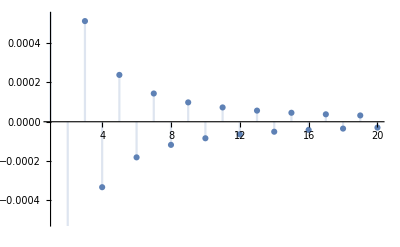

```mathematica
(MtTreeExpandzPatn[c[e,0]][jj])/(eta[lI[μ],lI[ν]]-(DD-2)v[3][lI[μ]] v[3][lI[ν]])/.DD->4/.{dot[a[3],a[3]]->1,dot[x[1],x[1]]->2,dot[a[3],x[1]]->1/2}//DiscretePlot[#,{jj,1,20}]&
```

```mathematica
(MtTreeExpandz[c[e,0]][0]/.{dot[x[1],x[1]]->1/2 (an^2+2 r^2-an^2 Cos[2 θ]), dot[a[3],x[1]]->an r Cos[θ],dot[a[3],a[3]]->an^2}/.DD->4//FullSimplify[#,r>=0&&an>=0&&r>=an&&0<=θ<=π]&)/.Cos[2θ]->2 Cos[θ]^2-1//Simplify
```

-(ArcSin[an/(√(an^2+r^2-an^2 Cos[θ]^2))] (eta[lI[μ],lI[ν]]-2 v[3][lI[μ]] v[3][lI[ν]]))/(8 an π)

```mathematica
MtTreeExpandzPatnBL[c[e,0]][jj]=(MtTreeExpandzPatn[c[e,0]][jj]/.{dot[x[1],x[1]]->1/2 (an^2+2 r^2-an^2 Cos[2 θ]), dot[a[3],x[1]]->an r Cos[θ],dot[a[3],a[3]]->an^2}/.DD->4//FullSimplify[#,r>=0&&an>=0&&r>=an&&0<=θ<=π&&jj>=1&&jj∈Integers]&)/.Cos[2θ]->2 Cos[θ]^2-1//Simplify[#,Trig->False]&
```

-(((an r Cos[θ])^(2 jj) (an^2+r^2-an^2 Cos[θ]^2)^-jj (-r^2+an^2 Cos[θ]^2)^(-2 jj) (an^(2+2 jj) (-r^2/an^2+Cos[θ]^2)^(1/2+2 jj) Gamma[1/2-2 jj]+(r^2-an^2 Cos[θ]^2) (an^2+r^2-an^2 Cos[θ]^2)^jj Gamma[1/2-jj] Hypergeometric2F1Regularized[1,1/2-jj,1+jj,1+r^2/an^2-Cos[θ]^2]) (eta[lI[μ],lI[ν]]-2 v[3][lI[μ]] v[3][lI[ν]]))/(16 an^2 jj π √(r^2-an^2 Cos[θ]^2) Gamma[1/2-2 jj]))

```mathematica
((MetricMinBL[θ,θ])//Simplify)/.Cos[2θ]->2 Cos[θ]^2-1//Simplify[#,Trig->False]&
((MetricMinBL[r,r])(an^2+r^2)//Simplify)/.Cos[2θ]->2 Cos[θ]^2-1//Simplify[#,Trig->False]&
```

-r^2-an^2 Cos[θ]^2

-r^2-an^2 Cos[θ]^2

```mathematica
MtTreeExpandzPatnBL[c[e,0]][jj]/.{eta[lI[μ],lI[ν]]->MetricMinBL[θ,θ], v[3][lI[μ]] v[3][lI[ν]]->0}(*dθdθ*)
```

-(((an r Cos[θ])^(2 jj) (-r^2-an^2 Cos[θ]^2) (an^2+r^2-an^2 Cos[θ]^2)^-jj (-r^2+an^2 Cos[θ]^2)^(-2 jj) (an^(2+2 jj) (-r^2/an^2+Cos[θ]^2)^(1/2+2 jj) Gamma[1/2-2 jj]+(r^2-an^2 Cos[θ]^2) (an^2+r^2-an^2 Cos[θ]^2)^jj Gamma[1/2-jj] Hypergeometric2F1Regularized[1,1/2-jj,1+jj,1+r^2/an^2-Cos[θ]^2]))/(16 an^2 jj π √(r^2-an^2 Cos[θ]^2) Gamma[1/2-2 jj]))

#### c[o,0] pattern from c[e,0], failed

```mathematica
M3Gen[3,1]
Vtree[1,di[μ],di[ν]]
```

(dot[p[3],ϵ[1]]^2 (c[e,-1] Cosh[dot[a[3],l[1]]]+(c[e,0] Sinh[dot[a[3],l[1]]])/dot[a[3],l[1]]+c[e,1] (Cosh[dot[a[3],l[1]]]/dot[a[3],l[1]]^2-Sinh[dot[a[3],l[1]]]/dot[a[3],l[1]]^3)))/M[3]^2-(ⅈ dot[p[3],ϵ[1]] dot[l[1],S[3],ϵ[1]] ((c[o,0] Sinh[dot[a[3],l[1]]])/dot[a[3],l[1]]+c[o,1] (Cosh[dot[a[3],l[1]]]/dot[a[3],l[1]]^2-Sinh[dot[a[3],l[1]]]/dot[a[3],l[1]]^3)))/M[3]^2

ϵ[1][di[μ]] ϵ[1][di[ν]]

The things except for the entire functions in c[e,0],c[o,0] after gluing.

```mathematica
vvgluing=(GlueAmp[A[dot[p[3],ϵ[1]]^2/M[3]^2/.{l[id_]->p[p[id]],ϵ[id_]->ϵ[p[id]]},{li[1]}],A[Vtree[1,di[μ],di[ν]]/.{l[id_]->p[p[id]],ϵ[id_]->ϵ[p[id]]},{lo[1]}],li[1]]/.{p[li[1]]->+p[1],p[lo[1]]->-p[1]}/.{di->lI}//contractAnti//contract)/.p[3]->M[3] v[3]/.{dot[_,S[par_],v[par_]]->0,dot[v[3],v[3]]->1}/.(M[3]v[3])[id_]->M[3]v[3][id]
vSgluing=(GlueAmp[A[(-ⅈ dot[p[3],ϵ[1]] dot[l[1],S[3],ϵ[1]])/M[3]^2/.{l[id_]->p[p[id]],ϵ[id_]->ϵ[p[id]]},{li[1]}],A[Vtree[1,di[μ],di[ν]]/.{l[id_]->p[p[id]],ϵ[id_]->ϵ[p[id]]},{lo[1]}],li[1]]/.{p[li[1]]->+p[1],p[lo[1]]->-p[1]}/.{di->lI}//contractAnti//contract)/.p[3]->M[3] v[3]/.{dot[_,S[par_],v[par_]]->0,dot[v[3],v[3]]->1}/.(M[3]v[3])[id_]->M[3]v[3][id]/.p[1]->q[1]
```

-eta[lI[μ],lI[ν]]/(-2+DD)+v[3][lI[μ]] v[3][lI[ν]]

-(ⅈ dot[q[1],S[3],lI[ν]] v[3][lI[μ]])/(2 M[3])-(ⅈ dot[q[1],S[3],lI[μ]] v[3][lI[ν]])/(2 M[3])

Check

```mathematica
intTree//Coefficient[#,c[o,0]]&
(intTree//Coefficient[#,c[e,0]]&)/vvgluing vSgluing/.q[1]->p[1]//Simplify//Expand
```

-(ⅈ dot[p[1],S[3],lI[ν]] Sinh[dot[a[3],p[1]]] v[3][lI[μ]])/(2 dot[a[3],p[1]] M[3])-(ⅈ dot[p[1],S[3],lI[μ]] Sinh[dot[a[3],p[1]]] v[3][lI[ν]])/(2 dot[a[3],p[1]] M[3])

-(ⅈ dot[p[1],S[3],lI[ν]] Sinh[dot[a[3],p[1]]] v[3][lI[μ]])/(2 dot[a[3],p[1]] M[3])-(ⅈ dot[p[1],S[3],lI[μ]] Sinh[dot[a[3],p[1]]] v[3][lI[ν]])/(2 dot[a[3],p[1]] M[3])

```mathematica
(MtTreeExpandz[c[e,0]][0])/vvgluing vSgluing//Simplify
(MtTreeExpandzPatn[c[e,0]][jj])/vvgluing vSgluing//FullSimplify[#,jj>=1&&jj∈Integers&&dot[a[3],a[3]]>=0&&dot[x[1],x[1]]>=0]&
```

-(ⅈ ArcSin[(√dot[a[3],a[3]])/(√dot[x[1],x[1]])] (dot[q[1],S[3],lI[ν]] v[3][lI[μ]]+dot[q[1],S[3],lI[μ]] v[3][lI[ν]]))/(8 π √dot[a[3],a[3]] M[3])

1/(16 jj π Gamma[1/2-2 jj] M[3])ⅈ dot[a[3],a[3]]^(-1-jj) dot[a[3],x[1]]^(2 jj) (dot[a[3],a[3]]-dot[x[1],x[1]])^(-1/2-2 jj) dot[x[1],x[1]]^-jj √(-dot[a[3],a[3]]+dot[x[1],x[1]]) (√dot[a[3],a[3]] (dot[a[3],a[3]]-dot[x[1],x[1]])^(2 jj) Gamma[1/2-2 jj]-√(dot[a[3],a[3]]-dot[x[1],x[1]]) (dot[a[3],a[3]] dot[x[1],x[1]])^jj Gamma[1/2-jj] Hypergeometric2F1Regularized[1,1/2-jj,1+jj,dot[x[1],x[1]]/dot[a[3],a[3]]]) (dot[q[1],S[3],lI[ν]] v[3][lI[μ]]+dot[q[1],S[3],lI[μ]] v[3][lI[ν]])

```mathematica
-(ⅈ ArcSin[(√dot[a[3],a[3]])/xn])/(8 π √dot[a[3],a[3]] M[3])/.dot[x[1],x[1]]->xn^2//Simplify[#,xn>=0]&
-I  D[%,xn] (x[1][ui[ρ]])/xn(*∂^ρ |x|*)
%dot[di[ρ],S[3],di[ν]] v[3][lI[μ]]/.{ui->lI,di->lI}//contractAnti
%+(%/.{μ->ν,ν->μ})/.xn->√dot[x[1],x[1]]//FullSimplify
(*check*)
MtTreeExpandz[c[o,0]][0]
```

-(ⅈ ArcSin[(√dot[a[3],a[3]])/xn])/(8 π √dot[a[3],a[3]] M[3])

(x[1][ui[ρ]])/(8 π xn^3 √(1-dot[a[3],a[3]]/xn^2) M[3])

(dot[x[1],S[3],lI[ν]] v[3][lI[μ]])/(8 π xn^3 √(1-dot[a[3],a[3]]/xn^2) M[3])

(dot[x[1],S[3],lI[ν]] v[3][lI[μ]]+dot[x[1],S[3],lI[μ]] v[3][lI[ν]])/(8 π √(1-dot[a[3],a[3]]/dot[x[1],x[1]]) dot[x[1],x[1]]^(3/2) M[3])

(dot[x[1],S[3],lI[ν]] v[3][lI[μ]]+dot[x[1],S[3],lI[μ]] v[3][lI[ν]])/(8 π √(1-dot[a[3],a[3]]/dot[x[1],x[1]]) dot[x[1],x[1]]^(3/2) M[3])

```mathematica
(((MtTreeExpandzPatn[c[e,0]][jj])/vvgluing vSgluing//FullSimplify[#,jj>=1&&jj∈Integers&&dot[a[3],a[3]]>=0&&dot[x[1],x[1]]>=0]&)/.{dot[x[1],x[1]]->xn^2,dot[a[3],x[1]]->xa}//Simplify[#,xn>=0]&)/(dot[q[1],S[3],lI[ν]] v[3][lI[μ]]+dot[q[1],S[3],lI[μ]] v[3][lI[ν]])
-I(  D[%,xn] (x[1][ui[ρ]])/xn(*∂^ρ |x|*)+D[%,xa]a[3][ui[ρ]](*∂^ρ a.x*));
%dot[di[ρ],S[3],di[ν]] v[3][lI[μ]]/.{ui->lI,di->lI}//contractAnti;
%+(%/.{μ->ν,ν->μ})/.{xn->√dot[x[1],x[1]],xa->dot[a[3],x[1]]}/.dot[a[par_],S[par_],__]->0//FullSimplify[#,jj>=1&&jj∈Integers]&
```

1/(16 jj π Gamma[1/2-2 jj] M[3])ⅈ (xa/xn)^(2 jj) √(xn^2-dot[a[3],a[3]]) dot[a[3],a[3]]^(-1-jj) (-xn^2+dot[a[3],a[3]])^(-1/2-2 jj) (√dot[a[3],a[3]] (-xn^2+dot[a[3],a[3]])^(2 jj) Gamma[1/2-2 jj]-(xn^2 dot[a[3],a[3]])^jj √(-xn^2+dot[a[3],a[3]]) Gamma[1/2-jj] Hypergeometric2F1Regularized[1,1/2-jj,1+jj,xn^2/dot[a[3],a[3]]])

(dot[a[3],x[1]]^(2 jj) (dot[a[3],a[3]]^(-1/2-jj) √(dot[a[3],a[3]]-dot[x[1],x[1]]) dot[x[1],x[1]]^-jj+((dot[a[3],a[3]]-dot[x[1],x[1]])^(-2 jj) Gamma[1/2-jj] (1/(jj!)+((-dot[a[3],a[3]]+dot[x[1],x[1]]) Hypergeometric2F1Regularized[1,1/2-jj,1+jj,dot[x[1],x[1]]/dot[a[3],a[3]]])/dot[a[3],a[3]]))/Gamma[1/2-2 jj]) (dot[x[1],S[3],lI[ν]] v[3][lI[μ]]+dot[x[1],S[3],lI[μ]] v[3][lI[ν]]))/(8 π dot[x[1],x[1]] √(-dot[a[3],a[3]]+dot[x[1],x[1]]) M[3])

```mathematica
MtTreeExpandzPatn[c[o,0]][jj_]:=(dot[a[3],x[1]]^(2 jj) (dot[a[3],a[3]]^(-1/2-jj) √(dot[a[3],a[3]]-dot[x[1],x[1]]) dot[x[1],x[1]]^-jj+((dot[a[3],a[3]]-dot[x[1],x[1]])^(-2 jj) Gamma[1/2-jj] (1/(jj!)+((-dot[a[3],a[3]]+dot[x[1],x[1]]) Hypergeometric2F1Regularized[1,1/2-jj,1+jj,dot[x[1],x[1]]/dot[a[3],a[3]]])/dot[a[3],a[3]]))/Gamma[1/2-2 jj]) (dot[x[1],S[3],lI[ν]] v[3][lI[μ]]+dot[x[1],S[3],lI[μ]] v[3][lI[ν]]))/(8 π dot[x[1],x[1]] √(-dot[a[3],a[3]]+dot[x[1],x[1]]) M[3])
```

```mathematica
MtTreeExpandzPatn[c[o,0]][1]//Expand//FullSimplify
MtTreeExpandz[c[o,0]][1]/.z->dot[a[3],x[1]]^2/(dot[a[3],a[3]] dot[x[1],x[1]])
```

(dot[a[3],x[1]]^2 (2 dot[a[3],a[3]]^2 √(dot[a[3],a[3]]-dot[x[1],x[1]])-4 dot[a[3],a[3]] √(dot[a[3],a[3]]-dot[x[1],x[1]]) dot[x[1],x[1]]+2 √(dot[a[3],a[3]]-dot[x[1],x[1]]) dot[x[1],x[1]]^2-2 √dot[a[3],a[3]] dot[x[1],x[1]]^2 √(1-dot[x[1],x[1]]/dot[a[3],a[3]])+dot[a[3],a[3]]^(5/2) (2-2 √(1-dot[x[1],x[1]]/dot[a[3],a[3]]))+dot[a[3],a[3]]^(3/2) dot[x[1],x[1]] (-5+4 √(1-dot[x[1],x[1]]/dot[a[3],a[3]]))) (dot[x[1],S[3],lI[ν]] v[3][lI[μ]]+dot[x[1],S[3],lI[μ]] v[3][lI[ν]]))/(16 π dot[a[3],a[3]]^(3/2) dot[x[1],x[1]]^2 (-dot[a[3],a[3]]+dot[x[1],x[1]])^(5/2) M[3])

(dot[a[3],x[1]]^2 √(1-dot[a[3],a[3]]/dot[x[1],x[1]]) (2 dot[a[3],a[3]]-5 dot[x[1],x[1]]) (dot[x[1],S[3],lI[ν]] v[3][lI[μ]]+dot[x[1],S[3],lI[μ]] v[3][lI[ν]]))/(16 π dot[x[1],x[1]]^(3/2) (-dot[a[3],a[3]]+dot[x[1],x[1]])^3 M[3])

```mathematica
MtTreeExpandzPatn[c[o,0]][1]-(MtTreeExpandz[c[o,0]][1]/.z->dot[a[3],x[1]]^2/(dot[a[3],a[3]] dot[x[1],x[1]]))//FullSimplify
```

1/(16 π dot[x[1],x[1]]^(3/2) M[3])dot[a[3],x[1]]^2 ((√(1-dot[a[3],a[3]]/dot[x[1],x[1]]) (2 dot[a[3],a[3]]-5 dot[x[1],x[1]]))/(dot[a[3],a[3]]-dot[x[1],x[1]])^3+(2 √dot[x[1],x[1]] ((√(dot[a[3],a[3]]-dot[x[1],x[1]]))/(dot[a[3],a[3]]^(3/2) dot[x[1],x[1]])-(3 (1-(2 (-dot[a[3],a[3]]+dot[x[1],x[1]]) (-1+(1-dot[x[1],x[1]]/dot[a[3],a[3]])^(3/2)))/(3 dot[x[1],x[1]])))/(2 (dot[a[3],a[3]]-dot[x[1],x[1]])^2)))/(√(-dot[a[3],a[3]]+dot[x[1],x[1]]))) (dot[x[1],S[3],lI[ν]] v[3][lI[μ]]+dot[x[1],S[3],lI[μ]] v[3][lI[ν]])

#### c[o,0] z-expnasion, failed

```mathematica
Coefficient[intTree,c[e,0]]//Simplify
Coefficient[intTree,c[o,0]]//Simplify
```

-(Sinh[dot[a[3],p[1]]] (eta[lI[μ],lI[ν]]-(-2+DD) v[3][lI[μ]] v[3][lI[ν]]))/((-2+DD) dot[a[3],p[1]])

-(ⅈ Sinh[dot[a[3],p[1]]] (dot[p[1],S[3],lI[ν]] v[3][lI[μ]]+dot[p[1],S[3],lI[μ]] v[3][lI[ν]]))/(2 dot[a[3],p[1]] M[3])

```mathematica
Coefficient[intTree,c[o,0]]/.p[1]->q[1]
%/.{a[3]->tt a[3],S[3]->tt S[3]}//SeriesCoefficient[#,{tt,0,nn}]&//FullSimplify
%[[1,1,1]]/.{dot[a[3],q[1]]->-dot[a[3],q[1]]}(*a.q=-a⃗.q⃗, dot[a[3],q[1]]=a⃗.q⃗ from now on*)//Simplify[#,Mod[nn,2]==1]&//Expand
%/.nn->2k+1/.dot[a[ParBH_],q[ParGon_]]^(2 k)dot[q[ParGon_],S[ParBH_],id_]:>(FTaqS[ParGon,ParBH][-1,k][id]/.DD->3)//FunctionExpand//FullSimplify
Table[z^jj SeriesCoefficient[%/.dot[a[3],x[1]]^2->dot[a[3],a[3]] dot[x[1],x[1]]z,{z,0,jj}],{jj,0,10}]//FullSimplify[#,k∈Integers&&k>=0]&;
Table[MtTreeExpandz[c[o,0]][jj]=Sum[%[[jj+1]],{k,0,∞}]//FullSimplify,{jj,0,10}];
```

-(ⅈ dot[q[1],S[3],lI[ν]] Sinh[dot[a[3],q[1]]] v[3][lI[μ]])/(2 dot[a[3],q[1]] M[3])-(ⅈ dot[q[1],S[3],lI[μ]] Sinh[dot[a[3],q[1]]] v[3][lI[ν]])/(2 dot[a[3],q[1]] M[3])

Piecewise[{{(ⅈ ((-dot[a[3],q[1]])^nn-dot[a[3],q[1]]^nn) (dot[q[1],S[3],lI[ν]] v[3][lI[μ]]+dot[q[1],S[3],lI[μ]] v[3][lI[ν]]))/(4 dot[a[3],q[1]] nn! M[3]), nn≥0}, {0, True}}]

-(ⅈ dot[a[3],q[1]]^(-1+nn) dot[q[1],S[3],lI[ν]] v[3][lI[μ]])/(2 nn! M[3])-(ⅈ dot[a[3],q[1]]^(-1+nn) dot[q[1],S[3],lI[μ]] v[3][lI[ν]])/(2 nn! M[3])

-1/(π^2 Gamma[2+2 k] M[3])2^(-3+2 k) dot[a[3],a[3]]^k dot[x[1],x[1]]^(-3/2-k) Gamma[1/2+k]^2 (2 k Hypergeometric2F1[1-k,1/2+k,1/2,dot[a[3],x[1]]^2/(dot[a[3],a[3]] dot[x[1],x[1]])]-(1+4 k) Hypergeometric2F1[-k,1/2+k,1/2,dot[a[3],x[1]]^2/(dot[a[3],a[3]] dot[x[1],x[1]])]) (dot[x[1],S[3],lI[ν]] v[3][lI[μ]]+dot[x[1],S[3],lI[μ]] v[3][lI[ν]])

```mathematica
MtTreeExpandzList[c[o,0]]=Table[MtTreeExpandz[c[o,0]][jj],{jj,0,10}];
SaveToCell[MtTreeExpandzList[c[o,0]]]
```

```mathematica
MtTreeExpandzList[c[o,0]]="data";
```

```mathematica
Table[MtTreeExpandzClear[c[o,0]][jj]=((-dot[a[3],a[3]]+dot[x[1],x[1]])^(2jj+1)dot[x[1],x[1]]^((2jj+1)/2)M[3]π)/((dot[x[1],S[3],lI[ν]] v[3][lI[μ]]+dot[x[1],S[3],lI[μ]] v[3][lI[ν]])dot[a[3],x[1]]^(2jj)√(1-dot[a[3],a[3]]/dot[x[1],x[1]]))MtTreeExpandz[c[o,0]][jj]/.z->dot[a[3],x[1]]^2/(dot[a[3],a[3]] dot[x[1],x[1]])//Simplify,{jj,0,10}];
```

```mathematica
Table[MtTreeExpandzClear[c[o,0]][jj],{jj,0,3}]
Table[MtTreeExpandzClear[c[e,0]][jj],{jj,0,3}]
```

{1/8,1/16 (2 dot[a[3],a[3]]-5 dot[x[1],x[1]]),1/64 (8 dot[a[3],a[3]]^2-36 dot[a[3],a[3]] dot[x[1],x[1]]+63 dot[x[1],x[1]]^2),1/128 (16 dot[a[3],a[3]]^3-104 dot[a[3],a[3]]^2 dot[x[1],x[1]]+286 dot[a[3],a[3]] dot[x[1],x[1]]^2-429 dot[x[1],x[1]]^3)}

{-ArcSin[(√dot[a[3],a[3]])/(√dot[x[1],x[1]])]/(4 √dot[a[3],a[3]] √(1-dot[a[3],a[3]]/dot[x[1],x[1]]) √dot[x[1],x[1]]),1/8,1/32 (2 dot[a[3],a[3]]-7 dot[x[1],x[1]]),1/192 (8 dot[a[3],a[3]]^2-44 dot[a[3],a[3]] dot[x[1],x[1]]+99 dot[x[1],x[1]]^2)}

```mathematica
Table[MtTreeExpandzClear[c[o,0]][jj],{jj,0,10}]//FindSequenceFunction[#,jj+1]&
```

FindSequenceFunction[{(π √(1-dot[a[3],a[3]]/dot[x[1],x[1]]) dot[x[1],x[1]]^(3/2) M[3] MTreeExpandz[c[o,0]][0])/(dot[x[1],S[3],lI[ν]] v[3][lI[μ]]+dot[x[1],S[3],lI[μ]] v[3][lI[ν]]),(π dot[x[1],x[1]]^(3/2) (-dot[a[3],a[3]]+dot[x[1],x[1]])^3 M[3] MTreeExpandz[c[o,0]][1])/(dot[a[3],x[1]]^2 √(1-dot[a[3],a[3]]/dot[x[1],x[1]]) (dot[x[1],S[3],lI[ν]] v[3][lI[μ]]+dot[x[1],S[3],lI[μ]] v[3][lI[ν]])),(π dot[x[1],x[1]]^(5/2) (-dot[a[3],a[3]]+dot[x[1],x[1]])^5 M[3] MTreeExpandz[c[o,0]][2])/(dot[a[3],x[1]]^4 √(1-dot[a[3],a[3]]/dot[x[1],x[1]]) (dot[x[1],S[3],lI[ν]] v[3][lI[μ]]+dot[x[1],S[3],lI[μ]] v[3][lI[ν]])),(π dot[x[1],x[1]]^(7/2) (-dot[a[3],a[3]]+dot[x[1],x[1]])^7 M[3] MTreeExpandz[c[o,0]][3])/(dot[a[3],x[1]]^6 √(1-dot[a[3],a[3]]/dot[x[1],x[1]]) (dot[x[1],S[3],lI[ν]] v[3][lI[μ]]+dot[x[1],S[3],lI[μ]] v[3][lI[ν]])),(π dot[x[1],x[1]]^(9/2) (-dot[a[3],a[3]]+dot[x[1],x[1]])^9 M[3] MTreeExpandz[c[o,0]][4])/(dot[a[3],x[1]]^8 √(1-dot[a[3],a[3]]/dot[x[1],x[1]]) (dot[x[1],S[3],lI[ν]] v[3][lI[μ]]+dot[x[1],S[3],lI[μ]] v[3][lI[ν]])),(π dot[x[1],x[1]]^(11/2) (-dot[a[3],a[3]]+dot[x[1],x[1]])^11 M[3] MTreeExpandz[c[o,0]][5])/(dot[a[3],x[1]]^10 √(1-dot[a[3],a[3]]/dot[x[1],x[1]]) (dot[x[1],S[3],lI[ν]] v[3][lI[μ]]+dot[x[1],S[3],lI[μ]] v[3][lI[ν]])),(π dot[x[1],x[1]]^(13/2) (-dot[a[3],a[3]]+dot[x[1],x[1]])^13 M[3] MTreeExpandz[c[o,0]][6])/(dot[a[3],x[1]]^12 √(1-dot[a[3],a[3]]/dot[x[1],x[1]]) (dot[x[1],S[3],lI[ν]] v[3][lI[μ]]+dot[x[1],S[3],lI[μ]] v[3][lI[ν]])),(π dot[x[1],x[1]]^(15/2) (-dot[a[3],a[3]]+dot[x[1],x[1]])^15 M[3] MTreeExpandz[c[o,0]][7])/(dot[a[3],x[1]]^14 √(1-dot[a[3],a[3]]/dot[x[1],x[1]]) (dot[x[1],S[3],lI[ν]] v[3][lI[μ]]+dot[x[1],S[3],lI[μ]] v[3][lI[ν]])),(π dot[x[1],x[1]]^(17/2) (-dot[a[3],a[3]]+dot[x[1],x[1]])^17 M[3] MTreeExpandz[c[o,0]][8])/(dot[a[3],x[1]]^16 √(1-dot[a[3],a[3]]/dot[x[1],x[1]]) (dot[x[1],S[3],lI[ν]] v[3][lI[μ]]+dot[x[1],S[3],lI[μ]] v[3][lI[ν]])),(π dot[x[1],x[1]]^(19/2) (-dot[a[3],a[3]]+dot[x[1],x[1]])^19 M[3] MTreeExpandz[c[o,0]][9])/(dot[a[3],x[1]]^18 √(1-dot[a[3],a[3]]/dot[x[1],x[1]]) (dot[x[1],S[3],lI[ν]] v[3][lI[μ]]+dot[x[1],S[3],lI[μ]] v[3][lI[ν]])),(π dot[x[1],x[1]]^(21/2) (-dot[a[3],a[3]]+dot[x[1],x[1]])^21 M[3] MTreeExpandz[c[o,0]][10])/(dot[a[3],x[1]]^20 √(1-dot[a[3],a[3]]/dot[x[1],x[1]]) (dot[x[1],S[3],lI[ν]] v[3][lI[μ]]+dot[x[1],S[3],lI[μ]] v[3][lI[ν]]))},1+jj]

#### h_tt for Kerr. Fix overall factor based on Yuexiang’s. With θ=π/2

```mathematica
MetricTree[c[e,-1]]/.{dot[x[1],x[1]]->r^2, dot[a[3],x[1]]->0, dot[a[3],a[3]]->an^2}/.DD->4//Simplify[#,r>=0&&an>=0]&
%/.{eta[id1_,id2_]->1,v[3][id_]->1}(*μ=ν=0*)
-(2GN M[3])/(r √(1-an^2/r^2))/%//Simplify[#,r>=0&&an>=0]&
```

(-eta[lI[μ],lI[ν]]+2 v[3][lI[μ]] v[3][lI[ν]])/(8 π √(-an^2+r^2))

1/(8 π √(-an^2+r^2))

-16 GN π M[3]

```mathematica
(-16 GN π M[3]) MetricTree[c[e,-1]]/.{eta[id1_,id2_]->1,v[3][id_]->1}(*μ=ν=0*)/.{dot[x[1],x[1]]->r^2, dot[a[3],x[1]]->0, dot[a[3],a[3]]->an^2}/.DD->4//Simplify[#,r>=0&&an>=0]&
```

-(2 GN M[3])/(√(-an^2+r^2))

```mathematica
MtKerrBL[0,0]=(1-(2GN M[3] r)/(r^2+an^2 Cos[θ]));
```

```mathematica
MtKerrBL[0,0]/.θ->π/2
%/.r->√(r^2-an^2)+GN M[3]//GN SeriesCoefficient[#,{GN,0,1}]&
```

1-(2 GN M[3])/r

-(2 GN M[3])/(√(-an^2+r^2))

```mathematica
MtKerrBL[0,0]
```

1-(2 GN r M[3])/(r^2+an^2 Cos[θ])

#### Final results

```mathematica
MetricTreeList=Table[MetricTree[ii],{ii,CoeList}];
SaveToCell[MetricTreeList]
```

```mathematica
MetricTreeList="data";
```

```mathematica
Table[MetricTree[CoeList[[ii]]]=MetricTreeList[[ii]],{ii,CoeList//Length}]
```

```mathematica
MetricTree[c[o,1]]//FunctionExpand//FullSimplify
```

((2 dot[a[3],x[1]]^2+(ArcTanh[dot[a[3],a[3]]/(ⅈ dot[a[3],x[1]]+√dot[a[3],a[3]] √(1-dot[a[3],x[1]]^2/(dot[a[3],a[3]] dot[x[1],x[1]])) √dot[x[1],x[1]])]+ArcTanh[(ⅈ dot[a[3],x[1]]+√dot[a[3],a[3]] √(1-dot[a[3],x[1]]^2/(dot[a[3],a[3]] dot[x[1],x[1]])) √dot[x[1],x[1]])/dot[x[1],x[1]]]) dot[a[3],a[3]]^(3/2) √(1-dot[a[3],x[1]]^2/(dot[a[3],a[3]] dot[x[1],x[1]])) √dot[x[1],x[1]]-2 dot[a[3],a[3]] dot[x[1],x[1]]+(ArcTanh[dot[a[3],a[3]]/(ⅈ dot[a[3],x[1]]+√dot[a[3],a[3]] √(1-dot[a[3],x[1]]^2/(dot[a[3],a[3]] dot[x[1],x[1]])) √dot[x[1],x[1]])]+ArcTanh[(ⅈ dot[a[3],x[1]]+√dot[a[3],a[3]] √(1-dot[a[3],x[1]]^2/(dot[a[3],a[3]] dot[x[1],x[1]])) √dot[x[1],x[1]])/dot[x[1],x[1]]]) √dot[a[3],a[3]] √(1-dot[a[3],x[1]]^2/(dot[a[3],a[3]] dot[x[1],x[1]])) dot[x[1],x[1]]^(3/2)) (dot[x[1],S[3],lI[ν]] v[3][lI[μ]]+dot[x[1],S[3],lI[μ]] v[3][lI[ν]]))/(32 π^2 (dot[a[3],x[1]]^2-dot[a[3],a[3]] dot[x[1],x[1]])^2 M[3])

```mathematica
FTaq[1,3][-1,k]/.DD->3//FullSimplify
Sum[1/((2k)!)%,{k,0,∞}]
```

(4^(-1+k) dot[x[1],x[1]]^(-1/2-2 k) (dot[a[3],a[3]] dot[x[1],x[1]])^k Gamma[1/2+k]^2 Hypergeometric2F1[-k,1/2+k,1/2,dot[a[3],x[1]]^2/(dot[a[3],a[3]] dot[x[1],x[1]])])/π^2

∑_(k=0)^∞ (4^(-1+k) dot[x[1],x[1]]^(-1/2-2 k) (dot[a[3],a[3]] dot[x[1],x[1]])^k Gamma[1/2+k]^2 Hypergeometric2F1[-k,1/2+k,1/2,dot[a[3],x[1]]^2/(dot[a[3],a[3]] dot[x[1],x[1]])])/(π^2 (2 k)!)

```mathematica
FTaq[1,3][-1,k]/.dot[a[3],x[1]]->0
```

4^(-1+k) π^(-1/2-DD/2) dot[x[1],x[1]]^(1-DD/2-2 k) (dot[a[3],a[3]] dot[x[1],x[1]])^k Gamma[1/2+k] Gamma[-1+DD/2+k]

#### draft

```mathematica
Cosh[dot[a[3],q[1]]]/.a[3]->tt a[3]//SeriesCoefficient[#,{tt,0,nn}]&
```

Piecewise[{{dot[a[3],q[1]]^nn/(nn!), Mod[nn,2]==0&&nn≥0}, {0, True}}]

```mathematica
(FTaq[1,3][-1,k])/((2k)!)
```

1/((2 k)!)4^(-1+k) π^(-1/2-DD/2) dot[x[1],x[1]]^(1-DD/2-2 k) (dot[a[3],a[3]] dot[x[1],x[1]])^k Gamma[1/2+k] Gamma[-1+DD/2+k] Hypergeometric2F1[-k,-1+DD/2+k,1/2,dot[a[3],x[1]]^2/(dot[a[3],a[3]] dot[x[1],x[1]])]

```mathematica
(FTaq[1,3][-1,k])/((2k)!)/.DD->4//PowerExpand//FullSimplify
Sum[%,{k,0,∞}]//FullSimplify
```

(Cos[(1+2 k) ArcSin[dot[a[3],x[1]]/(√dot[a[3],a[3]] √dot[x[1],x[1]])]] dot[a[3],a[3]]^k dot[x[1],x[1]]^(-1-k))/(4 π^2 √(1-dot[a[3],x[1]]^2/(dot[a[3],a[3]] dot[x[1],x[1]])))

(-dot[a[3],a[3]]+dot[x[1],x[1]])/(4 π^2 (4 dot[a[3],x[1]]^2+(dot[a[3],a[3]]-dot[x[1],x[1]])^2))

### Integrate to all spin (dovable)

#### Integral expression of entire functions

```mathematica
Integrate[Cosh[x u],{u,0,1}]
```

Sinh[x]/x

```mathematica
1/I Integrate[Cosh[x I u],{u,0,I}]
```

Sinh[x]/x

```mathematica
1/2 Integrate[(1-u^2)Cosh[x u],{u,0,1}]//Simplify
%-1/x D[Sinh[x]/x,x]//Simplify
```

(x Cosh[x]-Sinh[x])/x^3

0

```mathematica
1/(2I)Integrate[(1- (I u)^2)Cosh[x I u],{u,0,I}]//Simplify
%-1/x D[Sinh[x]/x,x]//Simplify
```

(x Cosh[x]-Sinh[x])/x^3

0

#### c[e,0]

```mathematica
(intTree//Coefficient[#,c[e,0]]&)/vvgluing//Simplify
```

Sinh[dot[a[3],p[1]]]/dot[a[3],p[1]]

```mathematica
FTaq[1,3][-1,0]/.x[1]->x[1]+u a[3]/.DD->3//Simplify
intTreeAS[c[e,0]][+1]=Assuming[dot[a[3],a[3]]>=0&&dot[x[1],x[1]]>=0,1/(2I)Integrate[%,{u,0,I}]]//FunctionExpand//Simplify
```

1/(4 π √(u^2 dot[a[3],a[3]]+2 u dot[a[3],x[1]]+dot[x[1],x[1]]))

ConditionalExpression[1/(16 π √dot[a[3],a[3]])(4 π+2 ⅈ ArcTanh[dot[a[3],x[1]]/(√(dot[a[3],a[3]] dot[x[1],x[1]]))]+ⅈ Log[(-ⅈ dot[a[3],a[3]]-dot[a[3],x[1]]+√(dot[a[3],a[3]] (-dot[a[3],a[3]]+2 ⅈ dot[a[3],x[1]]+dot[x[1],x[1]])))/(√(-dot[a[3],a[3]]+2 ⅈ dot[a[3],x[1]]+dot[x[1],x[1]]))]-ⅈ Log[(ⅈ dot[a[3],a[3]]+dot[a[3],x[1]]+√(dot[a[3],a[3]] (-dot[a[3],a[3]]+2 ⅈ dot[a[3],x[1]]+dot[x[1],x[1]])))/(√(-dot[a[3],a[3]]+2 ⅈ dot[a[3],x[1]]+dot[x[1],x[1]]))]), ]

```mathematica
FTaq[1,3][-1,0]/.x[1]->x[1]-u a[3]/.DD->3//Simplify
intTreeAS[c[e,0]][-1]=Assuming[dot[a[3],a[3]]>=0&&dot[x[1],x[1]]>=0,1/(2I)Integrate[%,{u,0,I}]]//FunctionExpand//Simplify
```

1/(4 π √(u^2 dot[a[3],a[3]]-2 u dot[a[3],x[1]]+dot[x[1],x[1]]))

ConditionalExpression[1/(16 π √dot[a[3],a[3]])(4 π-2 ⅈ ArcTanh[dot[a[3],x[1]]/(√(dot[a[3],a[3]] dot[x[1],x[1]]))]-ⅈ Log[(ⅈ dot[a[3],a[3]]-dot[a[3],x[1]]+√(dot[a[3],a[3]] (-dot[a[3],a[3]]-2 ⅈ dot[a[3],x[1]]+dot[x[1],x[1]])))/(√(-dot[a[3],a[3]]-2 ⅈ dot[a[3],x[1]]+dot[x[1],x[1]]))]+ⅈ Log[(-ⅈ dot[a[3],a[3]]+dot[a[3],x[1]]+√(dot[a[3],a[3]] (-dot[a[3],a[3]]-2 ⅈ dot[a[3],x[1]]+dot[x[1],x[1]])))/(√(-dot[a[3],a[3]]-2 ⅈ dot[a[3],x[1]]+dot[x[1],x[1]]))]), ]

```mathematica
(intTreeAS[c[e,0]][-1]//Normal)-((intTreeAS[c[e,0]][+1]//Normal)/.a[3]->-a[3])//Simplify
```

0

```mathematica
intTreeAS[c[e,0]][+1]+intTreeAS[c[e,0]][-1]//FullSimplify//Normal
Assuming[t>=0&&dot[a[3],a[3]]>=0&&dot[x[1],x[1]]>=0,%/.a[3]->t a[3]//Series[#,{t,0,6}]&//Simplify]
```

-1/(16 π √dot[a[3],a[3]])ⅈ (8 ⅈ π+Log[(ⅈ dot[a[3],a[3]]-dot[a[3],x[1]]+√(dot[a[3],a[3]] (-dot[a[3],a[3]]-2 ⅈ dot[a[3],x[1]]+dot[x[1],x[1]])))/(√(-dot[a[3],a[3]]-2 ⅈ dot[a[3],x[1]]+dot[x[1],x[1]]))]-Log[(-ⅈ dot[a[3],a[3]]+dot[a[3],x[1]]+√(dot[a[3],a[3]] (-dot[a[3],a[3]]-2 ⅈ dot[a[3],x[1]]+dot[x[1],x[1]])))/(√(-dot[a[3],a[3]]-2 ⅈ dot[a[3],x[1]]+dot[x[1],x[1]]))]-Log[(-ⅈ dot[a[3],a[3]]-dot[a[3],x[1]]+√(dot[a[3],a[3]] (-dot[a[3],a[3]]+2 ⅈ dot[a[3],x[1]]+dot[x[1],x[1]])))/(√(-dot[a[3],a[3]]+2 ⅈ dot[a[3],x[1]]+dot[x[1],x[1]]))]+Log[(ⅈ dot[a[3],a[3]]+dot[a[3],x[1]]+√(dot[a[3],a[3]] (-dot[a[3],a[3]]+2 ⅈ dot[a[3],x[1]]+dot[x[1],x[1]])))/(√(-dot[a[3],a[3]]+2 ⅈ dot[a[3],x[1]]+dot[x[1],x[1]]))])

1/(2 √dot[a[3],a[3]] t)+1/(4 π √dot[x[1],x[1]])+((-3 dot[a[3],x[1]]^2+dot[a[3],a[3]] dot[x[1],x[1]]) t^2)/(24 π dot[x[1],x[1]]^(5/2))+((35 dot[a[3],x[1]]^4-30 dot[a[3],a[3]] dot[a[3],x[1]]^2 dot[x[1],x[1]]+3 dot[a[3],a[3]]^2 dot[x[1],x[1]]^2) t^4)/(160 π dot[x[1],x[1]]^(9/2))+1/(448 π dot[x[1],x[1]]^(13/2))(-231 dot[a[3],x[1]]^6+315 dot[a[3],a[3]] dot[a[3],x[1]]^4 dot[x[1],x[1]]-105 dot[a[3],a[3]]^2 dot[a[3],x[1]]^2 dot[x[1],x[1]]^2+5 dot[a[3],a[3]]^3 dot[x[1],x[1]]^3) t^6+O[t]^7

```mathematica
intTreeAS[c[e,0]][+1]+intTreeAS[c[e,0]][-1]-1/(2 √dot[a[3],a[3]])//FullSimplify//Normal
Assuming[t>=0&&dot[a[3],a[3]]>=0&&dot[x[1],x[1]]>=0,%/.a[3]->t a[3]//Series[#,{t,0,6}]&//Simplify]
```

-1/(16 π √dot[a[3],a[3]])ⅈ (Log[(ⅈ dot[a[3],a[3]]-dot[a[3],x[1]]+√(dot[a[3],a[3]] (-dot[a[3],a[3]]-2 ⅈ dot[a[3],x[1]]+dot[x[1],x[1]])))/(√(-dot[a[3],a[3]]-2 ⅈ dot[a[3],x[1]]+dot[x[1],x[1]]))]-Log[(-ⅈ dot[a[3],a[3]]+dot[a[3],x[1]]+√(dot[a[3],a[3]] (-dot[a[3],a[3]]-2 ⅈ dot[a[3],x[1]]+dot[x[1],x[1]])))/(√(-dot[a[3],a[3]]-2 ⅈ dot[a[3],x[1]]+dot[x[1],x[1]]))]-Log[(-ⅈ dot[a[3],a[3]]-dot[a[3],x[1]]+√(dot[a[3],a[3]] (-dot[a[3],a[3]]+2 ⅈ dot[a[3],x[1]]+dot[x[1],x[1]])))/(√(-dot[a[3],a[3]]+2 ⅈ dot[a[3],x[1]]+dot[x[1],x[1]]))]+Log[(ⅈ dot[a[3],a[3]]+dot[a[3],x[1]]+√(dot[a[3],a[3]] (-dot[a[3],a[3]]+2 ⅈ dot[a[3],x[1]]+dot[x[1],x[1]])))/(√(-dot[a[3],a[3]]+2 ⅈ dot[a[3],x[1]]+dot[x[1],x[1]]))])

1/(4 π √dot[x[1],x[1]])+((-3 dot[a[3],x[1]]^2+dot[a[3],a[3]] dot[x[1],x[1]]) t^2)/(24 π dot[x[1],x[1]]^(5/2))+((35 dot[a[3],x[1]]^4-30 dot[a[3],a[3]] dot[a[3],x[1]]^2 dot[x[1],x[1]]+3 dot[a[3],a[3]]^2 dot[x[1],x[1]]^2) t^4)/(160 π dot[x[1],x[1]]^(9/2))+1/(448 π dot[x[1],x[1]]^(13/2))(-231 dot[a[3],x[1]]^6+315 dot[a[3],a[3]] dot[a[3],x[1]]^4 dot[x[1],x[1]]-105 dot[a[3],a[3]]^2 dot[a[3],x[1]]^2 dot[x[1],x[1]]^2+5 dot[a[3],a[3]]^3 dot[x[1],x[1]]^3) t^6+O[t]^7

```mathematica
1/vvgluing 1/((-2+DD) π^2 Gamma[2+2 k])4^(-1+k) dot[x[1],x[1]]^(-1/2-2 k) (dot[a[3],a[3]] dot[x[1],x[1]])^k Gamma[1/2+k]^2 Hypergeometric2F1[-k,1/2+k,1/2,dot[a[3],x[1]]^2/(dot[a[3],a[3]] dot[x[1],x[1]])] (-eta[lI[μ],lI[ν]]+(-2+DD) v[3][lI[μ]] v[3][lI[ν]])//Simplify
Table[%,{k,0,3}]//Simplify
```

(4^(-1+k) dot[x[1],x[1]]^(-1/2-2 k) (dot[a[3],a[3]] dot[x[1],x[1]])^k Gamma[1/2+k]^2 Hypergeometric2F1[-k,1/2+k,1/2,dot[a[3],x[1]]^2/(dot[a[3],a[3]] dot[x[1],x[1]])])/(π^2 Gamma[2+2 k])

{1/(4 π √dot[x[1],x[1]]),(-3 dot[a[3],x[1]]^2+dot[a[3],a[3]] dot[x[1],x[1]])/(24 π dot[x[1],x[1]]^(5/2)),(35 dot[a[3],x[1]]^4-30 dot[a[3],a[3]] dot[a[3],x[1]]^2 dot[x[1],x[1]]+3 dot[a[3],a[3]]^2 dot[x[1],x[1]]^2)/(160 π dot[x[1],x[1]]^(9/2)),1/(448 π dot[x[1],x[1]]^(13/2))(-231 dot[a[3],x[1]]^6+315 dot[a[3],a[3]] dot[a[3],x[1]]^4 dot[x[1],x[1]]-105 dot[a[3],a[3]]^2 dot[a[3],x[1]]^2 dot[x[1],x[1]]^2+5 dot[a[3],a[3]]^3 dot[x[1],x[1]]^3)}

The rough simplification of log

```mathematica
(intTreeAS[c[e,0]][+1]+intTreeAS[c[e,0]][-1]-1/(2 √dot[a[3],a[3]])//FullSimplify//Normal)//.{Log[aa__]+Log[bb__]->Log[aa bb],-Log[aa__]-Log[bb__]->-Log[aa bb],Log[aa__]-Log[bb__]->Log[aa/bb]}//FullSimplify
Assuming[t>=0&&dot[a[3],a[3]]>=0&&dot[x[1],x[1]]>=0,%/.a[3]->t a[3]//Series[#,{t,0,6}]&//Simplify]
```

-1/(16 π √dot[a[3],a[3]])ⅈ Log[((ⅈ dot[a[3],a[3]]-dot[a[3],x[1]]+√(dot[a[3],a[3]] (-dot[a[3],a[3]]-2 ⅈ dot[a[3],x[1]]+dot[x[1],x[1]]))) (ⅈ dot[a[3],a[3]]+dot[a[3],x[1]]+√(dot[a[3],a[3]] (-dot[a[3],a[3]]+2 ⅈ dot[a[3],x[1]]+dot[x[1],x[1]]))))/((-ⅈ dot[a[3],a[3]]+dot[a[3],x[1]]+√(dot[a[3],a[3]] (-dot[a[3],a[3]]-2 ⅈ dot[a[3],x[1]]+dot[x[1],x[1]]))) (-ⅈ dot[a[3],a[3]]-dot[a[3],x[1]]+√(dot[a[3],a[3]] (-dot[a[3],a[3]]+2 ⅈ dot[a[3],x[1]]+dot[x[1],x[1]]))))]

1/(4 π √dot[x[1],x[1]])+((-3 dot[a[3],x[1]]^2+dot[a[3],a[3]] dot[x[1],x[1]]) t^2)/(24 π dot[x[1],x[1]]^(5/2))+((35 dot[a[3],x[1]]^4-30 dot[a[3],a[3]] dot[a[3],x[1]]^2 dot[x[1],x[1]]+3 dot[a[3],a[3]]^2 dot[x[1],x[1]]^2) t^4)/(160 π dot[x[1],x[1]]^(9/2))+1/(448 π dot[x[1],x[1]]^(13/2))(-231 dot[a[3],x[1]]^6+315 dot[a[3],a[3]] dot[a[3],x[1]]^4 dot[x[1],x[1]]-105 dot[a[3],a[3]]^2 dot[a[3],x[1]]^2 dot[x[1],x[1]]^2+5 dot[a[3],a[3]]^3 dot[x[1],x[1]]^3) t^6+O[t]^7

In the Boyer–Lindquist coordinate. Agree with the spin-expanded results in BL coordinate.

```mathematica
(intTreeAS[c[e,0]][+1]+intTreeAS[c[e,0]][-1]-1/(2 √dot[a[3],a[3]])//FullSimplify//Normal)/.{dot[x[1],x[1]]->1/2 (an^2+2 r^2-an^2 Cos[2 θ]), dot[a[3],x[1]]->an r Cos[θ],dot[a[3],a[3]]->an^2}//.{Log[aa__]+Log[bb__]->Log[aa bb],-Log[aa__]-Log[bb__]->-Log[aa bb],Log[aa__]-Log[bb__]->Log[aa/bb]}//FullSimplify[#,r>=0&&an>=0&&r>=an&&0<=θ<=π]&
%/.Log[(an-ⅈ r)^2/(an+ⅈ r)^2]->2Log[(an-ⅈ r)/(an+ⅈ r)]
Assuming[1/r>=0&&r>=0&&an>=0&&r>=an,%//Series[#,{an,0,8}]&]
```

-(ⅈ Log[(an-ⅈ r)^2/(an+ⅈ r)^2])/(16 an π)

-(ⅈ Log[(an-ⅈ r)/(an+ⅈ r)])/(8 an π)

Piecewise[{{-1/(8 an)+1/(4 π r)-an^2/(12 (π r^3))+an^4/(20 π r^5)-an^6/(28 (π r^7))+O[an]^8, an^7/r^7-an^5/r^5+an^3/r^3-an/r<0}, {1/(8 an)+1/(4 π r)-an^2/(12 (π r^3))+an^4/(20 π r^5)-an^6/(28 (π r^7))+O[an]^8, True}}]

Spin-expanded results.

```mathematica
(1/vvgluing 1/((-2+DD) π^2 Gamma[2+2 k])4^(-1+k) dot[x[1],x[1]]^(-1/2-2 k) (dot[a[3],a[3]] dot[x[1],x[1]])^k Gamma[1/2+k]^2 Hypergeometric2F1[-k,1/2+k,1/2,dot[a[3],x[1]]^2/(dot[a[3],a[3]] dot[x[1],x[1]])] (-eta[lI[μ],lI[ν]]+(-2+DD) v[3][lI[μ]] v[3][lI[ν]])//Table[#,{k,0,5}]&//Simplify)/.{dot[x[1],x[1]]->1/2 (an^2+2 r^2-an^2 Cos[2 θ]), dot[a[3],x[1]]->an r Cos[θ],dot[a[3],a[3]]->an^2}//FullSimplify[#,r>=0&&an>=0&&r>=an&&0<=θ<=π]&//Series[#,{an,0,6}]&/@#&//Simplify[#,r>=0&&an>=0&&r>=an&&0<=θ<=π]&//Total//Simplify
```

1/(4 π r)-an^2/(12 (π r^3))+an^4/(20 π r^5)-an^6/(28 (π r^7))+O[an]^7

Although the transformation to BL coordinate involve spin a, the k-th term in spin-expanded results starts from a^(2k), i.e. there wouldn’t be a pure 1/a^n appearing after the transformation.

```mathematica
(1/vvgluing 1/((-2+DD) π^2 Gamma[2+2 k])4^(-1+k) dot[x[1],x[1]]^(-1/2-2 k) (dot[a[3],a[3]] dot[x[1],x[1]])^k Gamma[1/2+k]^2 Hypergeometric2F1[-k,1/2+k,1/2,dot[a[3],x[1]]^2/(dot[a[3],a[3]] dot[x[1],x[1]])] (-eta[lI[μ],lI[ν]]+(-2+DD) v[3][lI[μ]] v[3][lI[ν]])//Table[#,{k,0,5}]&//Simplify)/.{dot[x[1],x[1]]->1/2 (an^2+2 r^2-an^2 Cos[2 θ]), dot[a[3],x[1]]->an r Cos[θ],dot[a[3],a[3]]->an^2}//Series[#,{an,0,6}]&/@#&//FullSimplify[#,r>=0&&an>=0&&r>=an&&0<=θ<=π]&
```

{1/(4 π r)-(Sin[θ]^2 an^2)/(8 (π r^3))+(3 Sin[θ]^4 an^4)/(32 π r^5)-(5 Sin[θ]^6 an^6)/(64 (π r^7))+O[an]^7,-((1+3 Cos[2 θ]) an^2)/(48 (π r^3))+((3+5 Cos[2 θ]) Sin[θ]^2 an^4)/(32 π r^5)-(5 ((5+7 Cos[2 θ]) Sin[θ]^4) an^6)/(128 (π r^7))+O[an]^7,((9+20 Cos[2 θ]+35 Cos[4 θ]) an^4)/(1280 π r^5)-(3 ((15+28 Cos[2 θ]+21 Cos[4 θ]) Sin[θ]^2) an^6)/(512 (π r^7))+O[an]^7,((5-21 Cos[θ]^2 (5-15 Cos[θ]^2+11 Cos[θ]^4)) an^6)/(448 π r^7)+O[an]^7,O[an]^8,O[an]^10}

```mathematica
1/(an^2+CC)//Series[#,{an,0,3}]&
```

1/CC-an^2/CC^2+O[an]^4

```mathematica
-(ⅈ Log[(an-ⅈ r)/(an+ⅈ r)])/(8 an π)-1/(8 an)//Series[#,{an,0,12}]&;
%[[2]]//Normal//List@@#&//Reverse
%//FindSequenceFunction[#,k+1]&
Sum[%,{k,0,∞}]
%//Series[#,{an,0,12}]&
```

{1/(4 π r),-an^2/(12 π r^3),an^4/(20 π r^5),-an^6/(28 π r^7),an^8/(36 π r^9),-an^10/(44 π r^11)}

-((-an^2/r^2)^(1+k) r)/(4 an^2 (-1+2 (1+k)) π)

ArcTan[an/r]/(4 an π)

1/(4 π r)-an^2/(12 (π r^3))+an^4/(20 π r^5)-an^6/(28 (π r^7))+an^8/(36 π r^9)-an^10/(44 (π r^11))+an^12/(52 π r^13)+O[an]^13

### Spin expansion and resummation in the Boyer–Lindquist coordinate (done) (load amplitude metric here)

The expression in the BL coordinate looks not in a covariant form while the pattern looks so. This is because we let  dot[a[3],x[1]]->|a| r cos(θ) which breaks the covariance. It would also happen in the Lorentz coordinate if we let  dot[a[3],x[1]]->|a| z

#### c[e,-1] in BL coordinate, done

```mathematica
Coefficient[intTree,c[e,-1]]/.p[1]->q[1]
%/.a[3]->tt a[3]//SeriesCoefficient[#,{tt,0,nn}]&//FullSimplify
%[[1,1,1]]/.{dot[a[3],q[1]]->-dot[a[3],q[1]]}(*a.q=-a⃗.q⃗, dot[a[3],q[1]]=a⃗.q⃗ from now on*)//Simplify[#,Mod[nn,2]==0]&
%/.nn->2k/.dot[a[ParBH_],q[ParGon_]]^(2 k):>(FTaq[ParGon,ParBH][-1,k]/.DD->3(*The Fourier transform ∫(d^d q)/(2π)^d e^(ix⃗.q⃗)1/(q⃗.q⃗).... with d=3 imposed*))//FullSimplify
((-2+DD)%)/(-eta[lI[μ],lI[ν]]+(-2+DD) v[3][lI[μ]] v[3][lI[ν]])/.{dot[x[1],x[1]]->an^2+r^2-an^2 Cos[θ]^2,dot[a[3],x[1]]->an r Cos[θ], dot[a[3],a[3]]->an^2}//Table[#,{k,0,6}]&//Simplify
Series[#,{an,0,12}]&/@%//FullSimplify[#,r>=0&&an>=0&&0<=θ<=π]&
%//Total//Simplify//Normal//MonomialList[#,an]&//FullSimplify[#,r>=0&&an>=0&&0<=θ<=π]&//Reverse
MetricTreePatnBL[c[e,-1]]=FindSequenceFunction[%,k+1]//FullSimplify[#,r>=0&&an>=0&&0<=θ<=π]&
```

-(Cosh[dot[a[3],q[1]]] eta[lI[μ],lI[ν]])/(-2+DD)+Cosh[dot[a[3],q[1]]] v[3][lI[μ]] v[3][lI[ν]]

Piecewise[{{-(((-dot[a[3],q[1]])^nn+dot[a[3],q[1]]^nn) (eta[lI[μ],lI[ν]]-(-2+DD) v[3][lI[μ]] v[3][lI[ν]]))/(2 (-2+DD) nn!), nn≥0}, {0, True}}]

(dot[a[3],q[1]]^nn (-eta[lI[μ],lI[ν]]+(-2+DD) v[3][lI[μ]] v[3][lI[ν]]))/((-2+DD) nn!)

1/(4 (-2+DD) π^(3/2) Gamma[1+k])dot[x[1],x[1]]^(-1/2-2 k) (dot[a[3],a[3]] dot[x[1],x[1]])^k Gamma[1/2+k] Hypergeometric2F1[-k,1/2+k,1/2,dot[a[3],x[1]]^2/(dot[a[3],a[3]] dot[x[1],x[1]])] (-eta[lI[μ],lI[ν]]+(-2+DD) v[3][lI[μ]] v[3][lI[ν]])

{1/(4 π √(an^2+r^2-an^2 Cos[θ]^2)),(an^2 (an^2+r^2-(an^2+3 r^2) Cos[θ]^2))/(8 π (an^2+r^2-an^2 Cos[θ]^2)^(5/2)),(an^4 (3 (an^2+r^2)^2-6 (an^4+6 an^2 r^2+5 r^4) Cos[θ]^2+(3 an^4+30 an^2 r^2+35 r^4) Cos[θ]^4))/(32 π (an^2+r^2-an^2 Cos[θ]^2)^(9/2)),-(an^6 (-5 (an^2+r^2)^3+15 (an^2+r^2)^2 (an^2+7 r^2) Cos[θ]^2-15 (an^6+15 an^4 r^2+35 an^2 r^4+21 r^6) Cos[θ]^4+(5 an^6+105 an^4 r^2+315 an^2 r^4+231 r^6) Cos[θ]^6))/(64 π (an^2+r^2-an^2 Cos[θ]^2)^(13/2)),1/(512 π (an^2+r^2-an^2 Cos[θ]^2)^(17/2))an^8 (35 (an^2+r^2)^4-140 (an^2+r^2)^3 (an^2+9 r^2) Cos[θ]^2+210 (an^2+r^2)^2 (an^4+18 an^2 r^2+33 r^4) Cos[θ]^4-28 (5 an^8+140 an^6 r^2+630 an^4 r^4+924 an^2 r^6+429 r^8) Cos[θ]^6+(35 an^8+1260 an^6 r^2+6930 an^4 r^4+12012 an^2 r^6+6435 r^8) Cos[θ]^8),-1/(1024 π (an^2+r^2-an^2 Cos[θ]^2)^(21/2))an^10 (-63 (an^2+r^2)^5+315 (an^2+r^2)^4 (an^2+11 r^2) Cos[θ]^2-210 (an^2+r^2)^3 (3 an^4+66 an^2 r^2+143 r^4) Cos[θ]^4+630 (an^2+r^2)^2 (an^6+33 an^4 r^2+143 an^2 r^4+143 r^6) Cos[θ]^6-45 (7 an^10+315 an^8 r^2+2310 an^6 r^4+6006 an^4 r^6+6435 an^2 r^8+2431 r^10) Cos[θ]^8+(63 an^10+3465 an^8 r^2+30030 an^6 r^4+90090 an^4 r^6+109395 an^2 r^8+46189 r^10) Cos[θ]^10),1/(4096 π (an^2+r^2-an^2 Cos[θ]^2)^(25/2))an^12 (231 (an^2+r^2)^6-1386 (an^2+r^2)^5 (an^2+13 r^2) Cos[θ]^2+3465 (an^2+r^2)^4 (an^4+26 an^2 r^2+65 r^4) Cos[θ]^4-4620 (an^2+r^2)^3 (an^6+39 an^4 r^2+195 an^2 r^4+221 r^6) Cos[θ]^6+495 (an^2+r^2)^2 (7 an^8+364 an^6 r^2+2730 an^4 r^4+6188 an^2 r^6+4199 r^8) Cos[θ]^8-66 (21 an^12+1386 an^10 r^2+15015 an^8 r^4+60060 an^6 r^6+109395 an^4 r^8+92378 an^2 r^10+29393 r^12) Cos[θ]^10+(231 an^12+18018 an^10 r^2+225225 an^8 r^4+1021020 an^6 r^6+2078505 an^4 r^8+1939938 an^2 r^10+676039 r^12) Cos[θ]^12)}

{1/(4 π r)-(Sin[θ]^2 an^2)/(8 (π r^3))+(3 Sin[θ]^4 an^4)/(32 π r^5)-(5 Sin[θ]^6 an^6)/(64 (π r^7))+(35 Sin[θ]^8 an^8)/(512 π r^9)-(63 Sin[θ]^10 an^10)/(1024 (π r^11))+(231 Sin[θ]^12 an^12)/(4096 π r^13)+O[an]^13,((1-3 Cos[θ]^2) an^2)/(8 π r^3)+(3 (3+5 Cos[2 θ]) Sin[θ]^2 an^4)/(32 π r^5)-(15 ((5+7 Cos[2 θ]) Sin[θ]^4) an^6)/(128 (π r^7))+(35 (7+9 Cos[2 θ]) Sin[θ]^6 an^8)/(256 π r^9)-(315 ((9+11 Cos[2 θ]) Sin[θ]^8) an^10)/(2048 (π r^11))+(693 (11+13 Cos[2 θ]) Sin[θ]^10 an^12)/(4096 π r^13)+O[an]^13,((9+20 Cos[2 θ]+35 Cos[4 θ]) an^4)/(256 π r^5)-(15 ((15+28 Cos[2 θ]+21 Cos[4 θ]) Sin[θ]^2) an^6)/(512 (π r^7))+(105 (35+60 Cos[2 θ]+33 Cos[4 θ]) Sin[θ]^4 an^8)/(2048 π r^9)-(105 ((189+308 Cos[2 θ]+143 Cos[4 θ]) Sin[θ]^6) an^10)/(4096 (π r^11))+(3465 (99+156 Cos[2 θ]+65 Cos[4 θ]) Sin[θ]^8 an^12)/(32768 π r^13)+O[an]^13,((5-21 Cos[θ]^2 (5-15 Cos[θ]^2+11 Cos[θ]^4)) an^6)/(64 π r^7)+(7 (350+675 Cos[2 θ]+594 Cos[4 θ]+429 Cos[6 θ]) Sin[θ]^2 an^8)/(4096 π r^9)-(315 ((210+385 Cos[2 θ]+286 Cos[4 θ]+143 Cos[6 θ]) Sin[θ]^4) an^10)/(16384 (π r^11))+(1155 (462+819 Cos[2 θ]+546 Cos[4 θ]+221 Cos[6 θ]) Sin[θ]^6 an^12)/(32768 π r^13)+O[an]^13,((35-1260 Cos[θ]^2+6930 Cos[θ]^4-12012 Cos[θ]^6+6435 Cos[θ]^8) an^8)/(512 π r^9)-(45 ((2205+4312 Cos[2 θ]+4004 Cos[4 θ]+3432 Cos[6 θ]+2431 Cos[8 θ]) Sin[θ]^2) an^10)/(131072 (π r^11))+(495 (8085+15288 Cos[2 θ]+12740 Cos[4 θ]+8840 Cos[6 θ]+4199 Cos[8 θ]) Sin[θ]^4 an^12)/(524288 π r^13)+O[an]^13,((63-11 Cos[θ]^2 (315+13 Cos[θ]^2 (-210+630 Cos[θ]^2-765 Cos[θ]^4+323 Cos[θ]^6))) an^10)/(1024 π r^11)+(33 (29106+57330 Cos[2 θ]+54600 Cos[4 θ]+49725 Cos[6 θ]+41990 Cos[8 θ]+29393 Cos[10 θ]) Sin[θ]^2 an^12)/(1048576 π r^13)+O[an]^13,((231+13 Cos[θ]^2 (-1386+17325 Cos[θ]^2+17 Cos[θ]^4 (-4620+9405 Cos[θ]^2-8778 Cos[θ]^4+3059 Cos[θ]^6))) an^12)/(4096 π r^13)+O[an]^13}

{1/(4 π r),-(an^2 Cos[θ]^2)/(4 π r^3),(an^4 Cos[θ]^4)/(4 π r^5),-(an^6 Cos[θ]^6)/(4 π r^7),(an^8 Cos[θ]^8)/(4 π r^9),-(an^10 Cos[θ]^10)/(4 π r^11),(an^12 Cos[θ]^12)/(4 π r^13)}

((-(an^2 Cos[θ]^2)/r^2)^k)/(4 π r)

```mathematica
MetricTree[c[e,-1]]=(-eta[lI[μ],lI[ν]]+(-2+DD) v[3][lI[μ]] v[3][lI[ν]])/(-2+DD)Sum[MetricTreePatnBL[c[e,-1]],{k,0,∞}]/.DD->4//FullSimplify[#,r>=0&&an>=0&&0<=θ<=π]&
```

-(r (eta[lI[μ],lI[ν]]-2 v[3][lI[μ]] v[3][lI[ν]]))/(8 π (r^2+an^2 Cos[θ]^2))

#### c[e,0] in BL coordinate, done

```mathematica
Coefficient[intTree,c[e,0]]/.p[1]->q[1]
%/.a[3]->tt a[3]//SeriesCoefficient[#,{tt,0,nn}]&//FullSimplify
%[[1,1,1]]/.{dot[a[3],q[1]]->-dot[a[3],q[1]]}(*a.q=-a⃗.q⃗, dot[a[3],q[1]]=a⃗.q⃗ from now on*)//Simplify[#,Mod[nn,2]==0]&
%/.nn->2k/.dot[a[ParBH_],q[ParGon_]]^(2 k):>(FTaq[ParGon,ParBH][-1,k]/.DD->3(*The Fourier transform ∫(d^d q)/(2π)^d e^(ix⃗.q⃗)1/(q⃗.q⃗).... with d=3 imposed*))//FullSimplify
((-2+DD)%)/(-eta[lI[μ],lI[ν]]+(-2+DD) v[3][lI[μ]] v[3][lI[ν]])/.{dot[x[1],x[1]]->an^2+r^2-an^2 Cos[θ]^2,dot[a[3],x[1]]->an r Cos[θ], dot[a[3],a[3]]->an^2}//Table[#,{k,0,6}]&//Simplify
Series[#,{an,0,12}]&/@%//FullSimplify[#,r>=0&&an>=0&&0<=θ<=π]&
%//Total//Simplify//Normal//List@@#&//FullSimplify[#,r>=0&&an>=0&&0<=θ<=π]&//Reverse
MetricTreePatnBL[c[e,0]]=FindSequenceFunction[%,k+1]//FullSimplify[#,r>=0&&an>=0&&0<=θ<=π]&
```

-(eta[lI[μ],lI[ν]] Sinh[dot[a[3],q[1]]])/((-2+DD) dot[a[3],q[1]])+(Sinh[dot[a[3],q[1]]] v[3][lI[μ]] v[3][lI[ν]])/dot[a[3],q[1]]

Piecewise[{{-(((-dot[a[3],q[1]])^nn+dot[a[3],q[1]]^nn) (eta[lI[μ],lI[ν]]-(-2+DD) v[3][lI[μ]] v[3][lI[ν]]))/(2 (-2+DD) (1+nn)!), nn≥-1}, {0, True}}]

(dot[a[3],q[1]]^nn (-eta[lI[μ],lI[ν]]+(-2+DD) v[3][lI[μ]] v[3][lI[ν]]))/((-2+DD) (1+nn)!)

1/((-2+DD) π^2 Gamma[2+2 k])4^(-1+k) dot[x[1],x[1]]^(-1/2-2 k) (dot[a[3],a[3]] dot[x[1],x[1]])^k Gamma[1/2+k]^2 Hypergeometric2F1[-k,1/2+k,1/2,dot[a[3],x[1]]^2/(dot[a[3],a[3]] dot[x[1],x[1]])] (-eta[lI[μ],lI[ν]]+(-2+DD) v[3][lI[μ]] v[3][lI[ν]])

{1/(4 π √(an^2+r^2-an^2 Cos[θ]^2)),(an^2 (an^2+r^2-(an^2+3 r^2) Cos[θ]^2))/(24 π (an^2+r^2-an^2 Cos[θ]^2)^(5/2)),(an^4 (3 (an^2+r^2)^2-6 (an^4+6 an^2 r^2+5 r^4) Cos[θ]^2+(3 an^4+30 an^2 r^2+35 r^4) Cos[θ]^4))/(160 π (an^2+r^2-an^2 Cos[θ]^2)^(9/2)),-(an^6 (-5 (an^2+r^2)^3+15 (an^2+r^2)^2 (an^2+7 r^2) Cos[θ]^2-15 (an^6+15 an^4 r^2+35 an^2 r^4+21 r^6) Cos[θ]^4+(5 an^6+105 an^4 r^2+315 an^2 r^4+231 r^6) Cos[θ]^6))/(448 π (an^2+r^2-an^2 Cos[θ]^2)^(13/2)),1/(4608 π (an^2+r^2-an^2 Cos[θ]^2)^(17/2))an^8 (35 (an^2+r^2)^4-140 (an^2+r^2)^3 (an^2+9 r^2) Cos[θ]^2+210 (an^2+r^2)^2 (an^4+18 an^2 r^2+33 r^4) Cos[θ]^4-28 (5 an^8+140 an^6 r^2+630 an^4 r^4+924 an^2 r^6+429 r^8) Cos[θ]^6+(35 an^8+1260 an^6 r^2+6930 an^4 r^4+12012 an^2 r^6+6435 r^8) Cos[θ]^8),-1/(11264 π (an^2+r^2-an^2 Cos[θ]^2)^(21/2))an^10 (-63 (an^2+r^2)^5+315 (an^2+r^2)^4 (an^2+11 r^2) Cos[θ]^2-210 (an^2+r^2)^3 (3 an^4+66 an^2 r^2+143 r^4) Cos[θ]^4+630 (an^2+r^2)^2 (an^6+33 an^4 r^2+143 an^2 r^4+143 r^6) Cos[θ]^6-45 (7 an^10+315 an^8 r^2+2310 an^6 r^4+6006 an^4 r^6+6435 an^2 r^8+2431 r^10) Cos[θ]^8+(63 an^10+3465 an^8 r^2+30030 an^6 r^4+90090 an^4 r^6+109395 an^2 r^8+46189 r^10) Cos[θ]^10),1/(53248 π (an^2+r^2-an^2 Cos[θ]^2)^(25/2))an^12 (231 (an^2+r^2)^6-1386 (an^2+r^2)^5 (an^2+13 r^2) Cos[θ]^2+3465 (an^2+r^2)^4 (an^4+26 an^2 r^2+65 r^4) Cos[θ]^4-4620 (an^2+r^2)^3 (an^6+39 an^4 r^2+195 an^2 r^4+221 r^6) Cos[θ]^6+495 (an^2+r^2)^2 (7 an^8+364 an^6 r^2+2730 an^4 r^4+6188 an^2 r^6+4199 r^8) Cos[θ]^8-66 (21 an^12+1386 an^10 r^2+15015 an^8 r^4+60060 an^6 r^6+109395 an^4 r^8+92378 an^2 r^10+29393 r^12) Cos[θ]^10+(231 an^12+18018 an^10 r^2+225225 an^8 r^4+1021020 an^6 r^6+2078505 an^4 r^8+1939938 an^2 r^10+676039 r^12) Cos[θ]^12)}

{1/(4 π r)-(Sin[θ]^2 an^2)/(8 (π r^3))+(3 Sin[θ]^4 an^4)/(32 π r^5)-(5 Sin[θ]^6 an^6)/(64 (π r^7))+(35 Sin[θ]^8 an^8)/(512 π r^9)-(63 Sin[θ]^10 an^10)/(1024 (π r^11))+(231 Sin[θ]^12 an^12)/(4096 π r^13)+O[an]^13,-((1+3 Cos[2 θ]) an^2)/(48 (π r^3))+((3+5 Cos[2 θ]) Sin[θ]^2 an^4)/(32 π r^5)-(5 ((5+7 Cos[2 θ]) Sin[θ]^4) an^6)/(128 (π r^7))+(35 (7+9 Cos[2 θ]) Sin[θ]^6 an^8)/(768 π r^9)-(105 ((9+11 Cos[2 θ]) Sin[θ]^8) an^10)/(2048 (π r^11))+(231 (11+13 Cos[2 θ]) Sin[θ]^10 an^12)/(4096 π r^13)+O[an]^13,((9+20 Cos[2 θ]+35 Cos[4 θ]) an^4)/(1280 π r^5)-(3 ((15+28 Cos[2 θ]+21 Cos[4 θ]) Sin[θ]^2) an^6)/(512 (π r^7))+(21 (35+60 Cos[2 θ]+33 Cos[4 θ]) Sin[θ]^4 an^8)/(2048 π r^9)-(21 ((189+308 Cos[2 θ]+143 Cos[4 θ]) Sin[θ]^6) an^10)/(4096 (π r^11))+(693 (99+156 Cos[2 θ]+65 Cos[4 θ]) Sin[θ]^8 an^12)/(32768 π r^13)+O[an]^13,((5-21 Cos[θ]^2 (5-15 Cos[θ]^2+11 Cos[θ]^4)) an^6)/(448 π r^7)+((350+675 Cos[2 θ]+594 Cos[4 θ]+429 Cos[6 θ]) Sin[θ]^2 an^8)/(4096 π r^9)-(45 ((210+385 Cos[2 θ]+286 Cos[4 θ]+143 Cos[6 θ]) Sin[θ]^4) an^10)/(16384 (π r^11))+(165 (462+819 Cos[2 θ]+546 Cos[4 θ]+221 Cos[6 θ]) Sin[θ]^6 an^12)/(32768 π r^13)+O[an]^13,((35-1260 Cos[θ]^2+6930 Cos[θ]^4-12012 Cos[θ]^6+6435 Cos[θ]^8) an^8)/(4608 π r^9)-(5 ((2205+4312 Cos[2 θ]+4004 Cos[4 θ]+3432 Cos[6 θ]+2431 Cos[8 θ]) Sin[θ]^2) an^10)/(131072 (π r^11))+(55 (8085+15288 Cos[2 θ]+12740 Cos[4 θ]+8840 Cos[6 θ]+4199 Cos[8 θ]) Sin[θ]^4 an^12)/(524288 π r^13)+O[an]^13,((63-11 Cos[θ]^2 (315+13 Cos[θ]^2 (-210+630 Cos[θ]^2-765 Cos[θ]^4+323 Cos[θ]^6))) an^10)/(11264 π r^11)+(3 (29106+57330 Cos[2 θ]+54600 Cos[4 θ]+49725 Cos[6 θ]+41990 Cos[8 θ]+29393 Cos[10 θ]) Sin[θ]^2 an^12)/(1048576 π r^13)+O[an]^13,((231+13 Cos[θ]^2 (-1386+17325 Cos[θ]^2+17 Cos[θ]^4 (-4620+9405 Cos[θ]^2-8778 Cos[θ]^4+3059 Cos[θ]^6))) an^12)/(53248 π r^13)+O[an]^13}

{1/(4 π r),-an^2/(12 π r^3),an^4/(20 π r^5),-an^6/(28 π r^7),an^8/(36 π r^9),-an^10/(44 π r^11),an^12/(52 π r^13)}

((-an^2/r^2)^k)/(4 (1+2 k) π r)

```mathematica
MetricTree[c[e,0]]=(-eta[lI[μ],lI[ν]]+(-2+DD) v[3][lI[μ]] v[3][lI[ν]])/(-2+DD)Sum[MetricTreePatnBL[c[e,0]],{k,0,∞}]/.DD->4//FullSimplify[#,r>=0&&an>=0&&0<=θ<=π]&
```

-(ArcTan[an/r] (eta[lI[μ],lI[ν]]-2 v[3][lI[μ]] v[3][lI[ν]]))/(8 an π)

#### c[e,1] in BL coordinate, done

```mathematica
Coefficient[intTree,c[e,1]]/.p[1]->q[1]
%/.a[3]->tt a[3]//SeriesCoefficient[#,{tt,0,nn}]&//FullSimplify
%[[1,1,1]]/.{dot[a[3],q[1]]->-dot[a[3],q[1]]}(*a.q=-a⃗.q⃗, dot[a[3],q[1]]=a⃗.q⃗ from now on*)//Simplify[#,Mod[nn,2]==0]&
%/.nn->2k/.dot[a[ParBH_],q[ParGon_]]^(2 k):>(FTaq[ParGon,ParBH][-1,k]/.DD->3(*The Fourier transform ∫(d^d q)/(2π)^d e^(ix⃗.q⃗)1/(q⃗.q⃗).... with d=3 imposed*))//FullSimplify
((-2+DD)%)/(-eta[lI[μ],lI[ν]]+(-2+DD) v[3][lI[μ]] v[3][lI[ν]])/.{dot[x[1],x[1]]->an^2+r^2-an^2 Cos[θ]^2,dot[a[3],x[1]]->an r Cos[θ], dot[a[3],a[3]]->an^2}//Table[#,{k,0,6}]&//Simplify
Series[#,{an,0,12}]&/@%//FullSimplify[#,r>=0&&an>=0&&0<=θ<=π]&
MetricTreeBLan[c[e,1]]=%//Total//Simplify//Normal//MonomialList[#,an]&//Reverse//Simplify
```

-(Cosh[dot[a[3],q[1]]] eta[lI[μ],lI[ν]])/((-2+DD) dot[a[3],q[1]]^2)+(eta[lI[μ],lI[ν]] Sinh[dot[a[3],q[1]]])/((-2+DD) dot[a[3],q[1]]^3)+(Cosh[dot[a[3],q[1]]] v[3][lI[μ]] v[3][lI[ν]])/dot[a[3],q[1]]^2-(Sinh[dot[a[3],q[1]]] v[3][lI[μ]] v[3][lI[ν]])/dot[a[3],q[1]]^3

Piecewise[{{-((2+nn) ((-dot[a[3],q[1]])^nn+dot[a[3],q[1]]^nn) (eta[lI[μ],lI[ν]]-(-2+DD) v[3][lI[μ]] v[3][lI[ν]]))/(2 (-2+DD) Gamma[4+nn]), nn≥-2}, {0, True}}]

-((2+nn) dot[a[3],q[1]]^nn (eta[lI[μ],lI[ν]]-(-2+DD) v[3][lI[μ]] v[3][lI[ν]]))/((-2+DD) Gamma[4+nn])

-1/((-2+DD) π^2 Gamma[4+2 k])2^(-1+2 k) (1+k) dot[x[1],x[1]]^(-1/2-2 k) (dot[a[3],a[3]] dot[x[1],x[1]])^k Gamma[1/2+k]^2 Hypergeometric2F1[-k,1/2+k,1/2,dot[a[3],x[1]]^2/(dot[a[3],a[3]] dot[x[1],x[1]])] (eta[lI[μ],lI[ν]]-(-2+DD) v[3][lI[μ]] v[3][lI[ν]])

{1/(12 π √(an^2+r^2-an^2 Cos[θ]^2)),(an^2 (an^2+r^2-(an^2+3 r^2) Cos[θ]^2))/(120 π (an^2+r^2-an^2 Cos[θ]^2)^(5/2)),(an^4 (3 (an^2+r^2)^2-6 (an^4+6 an^2 r^2+5 r^4) Cos[θ]^2+(3 an^4+30 an^2 r^2+35 r^4) Cos[θ]^4))/(1120 π (an^2+r^2-an^2 Cos[θ]^2)^(9/2)),-(an^6 (-5 (an^2+r^2)^3+15 (an^2+r^2)^2 (an^2+7 r^2) Cos[θ]^2-15 (an^6+15 an^4 r^2+35 an^2 r^4+21 r^6) Cos[θ]^4+(5 an^6+105 an^4 r^2+315 an^2 r^4+231 r^6) Cos[θ]^6))/(4032 π (an^2+r^2-an^2 Cos[θ]^2)^(13/2)),1/(50688 π (an^2+r^2-an^2 Cos[θ]^2)^(17/2))an^8 (35 (an^2+r^2)^4-140 (an^2+r^2)^3 (an^2+9 r^2) Cos[θ]^2+210 (an^2+r^2)^2 (an^4+18 an^2 r^2+33 r^4) Cos[θ]^4-28 (5 an^8+140 an^6 r^2+630 an^4 r^4+924 an^2 r^6+429 r^8) Cos[θ]^6+(35 an^8+1260 an^6 r^2+6930 an^4 r^4+12012 an^2 r^6+6435 r^8) Cos[θ]^8),-1/(146432 π (an^2+r^2-an^2 Cos[θ]^2)^(21/2))an^10 (-63 (an^2+r^2)^5+315 (an^2+r^2)^4 (an^2+11 r^2) Cos[θ]^2-210 (an^2+r^2)^3 (3 an^4+66 an^2 r^2+143 r^4) Cos[θ]^4+630 (an^2+r^2)^2 (an^6+33 an^4 r^2+143 an^2 r^4+143 r^6) Cos[θ]^6-45 (7 an^10+315 an^8 r^2+2310 an^6 r^4+6006 an^4 r^6+6435 an^2 r^8+2431 r^10) Cos[θ]^8+(63 an^10+3465 an^8 r^2+30030 an^6 r^4+90090 an^4 r^6+109395 an^2 r^8+46189 r^10) Cos[θ]^10),1/(798720 π (an^2+r^2-an^2 Cos[θ]^2)^(25/2))an^12 (231 (an^2+r^2)^6-1386 (an^2+r^2)^5 (an^2+13 r^2) Cos[θ]^2+3465 (an^2+r^2)^4 (an^4+26 an^2 r^2+65 r^4) Cos[θ]^4-4620 (an^2+r^2)^3 (an^6+39 an^4 r^2+195 an^2 r^4+221 r^6) Cos[θ]^6+495 (an^2+r^2)^2 (7 an^8+364 an^6 r^2+2730 an^4 r^4+6188 an^2 r^6+4199 r^8) Cos[θ]^8-66 (21 an^12+1386 an^10 r^2+15015 an^8 r^4+60060 an^6 r^6+109395 an^4 r^8+92378 an^2 r^10+29393 r^12) Cos[θ]^10+(231 an^12+18018 an^10 r^2+225225 an^8 r^4+1021020 an^6 r^6+2078505 an^4 r^8+1939938 an^2 r^10+676039 r^12) Cos[θ]^12)}

{1/(12 π r)-(Sin[θ]^2 an^2)/(24 (π r^3))+(Sin[θ]^4 an^4)/(32 π r^5)-(5 Sin[θ]^6 an^6)/(192 (π r^7))+(35 Sin[θ]^8 an^8)/(1536 π r^9)-(21 Sin[θ]^10 an^10)/(1024 (π r^11))+(77 Sin[θ]^12 an^12)/(4096 π r^13)+O[an]^13,-((1+3 Cos[2 θ]) an^2)/(240 (π r^3))+((3+5 Cos[2 θ]) Sin[θ]^2 an^4)/(160 π r^5)-(((5+7 Cos[2 θ]) Sin[θ]^4) an^6)/(128 (π r^7))+(7 (7+9 Cos[2 θ]) Sin[θ]^6 an^8)/(768 π r^9)-(21 ((9+11 Cos[2 θ]) Sin[θ]^8) an^10)/(2048 (π r^11))+(231 (11+13 Cos[2 θ]) Sin[θ]^10 an^12)/(20480 π r^13)+O[an]^13,((9+20 Cos[2 θ]+35 Cos[4 θ]) an^4)/(8960 π r^5)-(3 ((15+28 Cos[2 θ]+21 Cos[4 θ]) Sin[θ]^2) an^6)/(3584 (π r^7))+(3 (35+60 Cos[2 θ]+33 Cos[4 θ]) Sin[θ]^4 an^8)/(2048 π r^9)-(3 ((189+308 Cos[2 θ]+143 Cos[4 θ]) Sin[θ]^6) an^10)/(4096 (π r^11))+(99 (99+156 Cos[2 θ]+65 Cos[4 θ]) Sin[θ]^8 an^12)/(32768 π r^13)+O[an]^13,((5-21 Cos[θ]^2 (5-15 Cos[θ]^2+11 Cos[θ]^4)) an^6)/(4032 π r^7)+((350+675 Cos[2 θ]+594 Cos[4 θ]+429 Cos[6 θ]) Sin[θ]^2 an^8)/(36864 π r^9)-(5 ((210+385 Cos[2 θ]+286 Cos[4 θ]+143 Cos[6 θ]) Sin[θ]^4) an^10)/(16384 (π r^11))+(55 (462+819 Cos[2 θ]+546 Cos[4 θ]+221 Cos[6 θ]) Sin[θ]^6 an^12)/(98304 π r^13)+O[an]^13,((35-1260 Cos[θ]^2+6930 Cos[θ]^4-12012 Cos[θ]^6+6435 Cos[θ]^8) an^8)/(50688 π r^9)-(5 ((2205+4312 Cos[2 θ]+4004 Cos[4 θ]+3432 Cos[6 θ]+2431 Cos[8 θ]) Sin[θ]^2) an^10)/(1441792 (π r^11))+(5 (8085+15288 Cos[2 θ]+12740 Cos[4 θ]+8840 Cos[6 θ]+4199 Cos[8 θ]) Sin[θ]^4 an^12)/(524288 π r^13)+O[an]^13,((63-11 Cos[θ]^2 (315+13 Cos[θ]^2 (-210+630 Cos[θ]^2-765 Cos[θ]^4+323 Cos[θ]^6))) an^10)/(146432 π r^11)+(3 (29106+57330 Cos[2 θ]+54600 Cos[4 θ]+49725 Cos[6 θ]+41990 Cos[8 θ]+29393 Cos[10 θ]) Sin[θ]^2 an^12)/(13631488 π r^13)+O[an]^13,((231+13 Cos[θ]^2 (-1386+17325 Cos[θ]^2+17 Cos[θ]^4 (-4620+9405 Cos[θ]^2-8778 Cos[θ]^4+3059 Cos[θ]^6))) an^12)/(798720 π r^13)+O[an]^13}

{1/(12 π r),(an^2 (-3+Cos[2 θ]))/(120 π r^3),-(an^4 (-2+Cos[2 θ]))/(140 π r^5),(an^6 (-5+3 Cos[2 θ]))/(504 π r^7),-(an^8 (-3+2 Cos[2 θ]))/(396 π r^9),(an^10 (-7+5 Cos[2 θ]))/(1144 π r^11),-(an^12 (-4+3 Cos[2 θ]))/(780 π r^13)}

```mathematica
MetricTreeBLan[c[e,1]]/.Cos[2θ]->2 Cos[θ]^2-1//Simplify[#,Trig->False]&
MetricTreePatnBL[c[e,1]]=FindSequenceFunction[%,k+1]
```

{1/(12 π r),(an^2 (-2+Cos[θ]^2))/(60 π r^3),-(an^4 (-3+2 Cos[θ]^2))/(140 π r^5),(an^6 (-4+3 Cos[θ]^2))/(252 π r^7),-(an^8 (-5+4 Cos[θ]^2))/(396 π r^9),(an^10 (-6+5 Cos[θ]^2))/(572 π r^11),-(an^12 (-7+6 Cos[θ]^2))/(780 π r^13)}

FindSequenceFunction[{1/(12 π r),(an^2 (-2+Cos[θ]^2))/(60 π r^3),-(an^4 (-3+2 Cos[θ]^2))/(140 π r^5),(an^6 (-4+3 Cos[θ]^2))/(252 π r^7),-(an^8 (-5+4 Cos[θ]^2))/(396 π r^9),(an^10 (-6+5 Cos[θ]^2))/(572 π r^11),-(an^12 (-7+6 Cos[θ]^2))/(780 π r^13)},1+k]

```mathematica
MetricTreePatnBL[c[e,1]]=(-1)^(k+1)an^(2k)/(π r^(2k+1))(-(k+1)+k Cos[θ]^2)/(16(k+1)^2-4)//FullSimplify[#,r>=0&&an>=0&&0<=θ<=π]&
Table[MetricTreePatnBL[c[e,1]],{k,0,4}]//Simplify[#,Trig->False]&
```

((-1)^k an^(2 k) r^(-1-2 k) (1+k-k Cos[θ]^2))/(4 (3+4 k (2+k)) π)

{1/(12 π r),(an^2 (-2+Cos[θ]^2))/(60 π r^3),(an^4 (3-2 Cos[θ]^2))/(140 π r^5),(an^6 (-4+3 Cos[θ]^2))/(252 π r^7),(an^8 (5-4 Cos[θ]^2))/(396 π r^9)}

```mathematica
MetricTree[c[e,1]]=(-eta[lI[μ],lI[ν]]+(-2+DD) v[3][lI[μ]] v[3][lI[ν]])/(-2+DD)Sum[MetricTreePatnBL[c[e,1]],{k,0,∞}]/.DD->4//FullSimplify[#,r>=0&&an>=0&&0<=θ<=π]&
```

((15 r^3 (an r-(an^2+r^2) ArcTan[an/r])+2 an^5 Hypergeometric2F1[3/2,2,7/2,-an^2/r^2] Sin[θ]^2) (eta[lI[μ],lI[ν]]-2 v[3][lI[μ]] v[3][lI[ν]]))/(240 an^3 π r^3)

#### c[o,0] in BL coordinate, done

```mathematica
Coefficient[intTree,c[o,0]]/.p[1]->q[1]
%/.{a[3]->tt a[3],S[3]->tt S[3]}//SeriesCoefficient[#,{tt,0,nn}]&//FullSimplify
%[[1,1,1]]/.{dot[a[3],q[1]]->-dot[a[3],q[1]]}(*a.q=-a⃗.q⃗, dot[a[3],q[1]]=a⃗.q⃗ from now on*)//Simplify[#,Mod[nn,2]==1]&//Expand
%/.nn->2k+1/.dot[a[ParBH_],q[ParGon_]]^(2 k)dot[q[ParGon_],S[ParBH_],id_]:>(FTaqS[ParGon,ParBH][-1,k][id]/.DD->3)//FunctionExpand//FullSimplify
%/(dot[x[1],S[3],lI[ν]] v[3][lI[μ]]+dot[x[1],S[3],lI[μ]] v[3][lI[ν]])/.{dot[x[1],x[1]]->an^2+r^2-an^2 Cos[θ]^2,dot[a[3],x[1]]->an r Cos[θ], dot[a[3],a[3]]->an^2}//Table[#,{k,0,6}]&//Simplify
Series[#,{an,0,12}]&/@%//FullSimplify[#,r>=0&&an>=0&&0<=θ<=π]&
%//Total//Simplify//Normal//List@@#&//FullSimplify[#,r>=0&&an>=0&&0<=θ<=π]&
MetricTreePatnBL[c[o,0]]=FindSequenceFunction[%,k+1]//FullSimplify[#,r>=0&&an>=0&&0<=θ<=π]&
```

-(ⅈ dot[q[1],S[3],lI[ν]] Sinh[dot[a[3],q[1]]] v[3][lI[μ]])/(2 dot[a[3],q[1]] M[3])-(ⅈ dot[q[1],S[3],lI[μ]] Sinh[dot[a[3],q[1]]] v[3][lI[ν]])/(2 dot[a[3],q[1]] M[3])

Piecewise[{{(ⅈ ((-dot[a[3],q[1]])^nn-dot[a[3],q[1]]^nn) (dot[q[1],S[3],lI[ν]] v[3][lI[μ]]+dot[q[1],S[3],lI[μ]] v[3][lI[ν]]))/(4 dot[a[3],q[1]] nn! M[3]), nn≥0}, {0, True}}]

-(ⅈ dot[a[3],q[1]]^(-1+nn) dot[q[1],S[3],lI[ν]] v[3][lI[μ]])/(2 nn! M[3])-(ⅈ dot[a[3],q[1]]^(-1+nn) dot[q[1],S[3],lI[μ]] v[3][lI[ν]])/(2 nn! M[3])

-1/(π^2 Gamma[2+2 k] M[3])2^(-3+2 k) dot[a[3],a[3]]^k dot[x[1],x[1]]^(-3/2-k) Gamma[1/2+k]^2 (2 k Hypergeometric2F1[1-k,1/2+k,1/2,dot[a[3],x[1]]^2/(dot[a[3],a[3]] dot[x[1],x[1]])]-(1+4 k) Hypergeometric2F1[-k,1/2+k,1/2,dot[a[3],x[1]]^2/(dot[a[3],a[3]] dot[x[1],x[1]])]) (dot[x[1],S[3],lI[ν]] v[3][lI[μ]]+dot[x[1],S[3],lI[μ]] v[3][lI[ν]])

{1/(8 π (an^2+r^2-an^2 Cos[θ]^2)^(3/2) M[3]),-(an^2 (-an^2-r^2+(an^2+5 r^2) Cos[θ]^2))/(16 π (an^2+r^2-an^2 Cos[θ]^2)^(7/2) M[3]),(3 an^4 ((an^2+r^2)^2-2 (an^4+8 an^2 r^2+7 r^4) Cos[θ]^2+(an^4+14 an^2 r^2+21 r^4) Cos[θ]^4))/(64 π (an^2+r^2-an^2 Cos[θ]^2)^(11/2) M[3]),-(an^6 (-5 (an^2+r^2)^3+15 (an^2+r^2)^2 (an^2+9 r^2) Cos[θ]^2-15 (an^6+19 an^4 r^2+51 an^2 r^4+33 r^6) Cos[θ]^4+(5 an^6+135 an^4 r^2+495 an^2 r^4+429 r^6) Cos[θ]^6))/(128 π (an^2+r^2-an^2 Cos[θ]^2)^(15/2) M[3]),(5 an^8 (245 an^8-420 an^6 r^2+630 an^4 r^4-980 an^2 r^6+2205 r^8-56 (7 an^8+8 an^6 r^2-18 an^4 r^4+32 an^2 r^6-77 r^8) Cos[2 θ]+28 (7 an^8+68 an^6 r^2+2 an^4 r^4-44 an^2 r^6+143 r^8) Cos[4 θ]-56 an^8 Cos[6 θ]-1344 an^6 r^2 Cos[6 θ]-3696 an^4 r^4 Cos[6 θ]+3432 r^8 Cos[6 θ]+7 an^8 Cos[8 θ]+308 an^6 r^2 Cos[8 θ]+2002 an^4 r^4 Cos[8 θ]+4004 an^2 r^6 Cos[8 θ]+2431 r^8 Cos[8 θ]))/(131072 π (an^2+r^2-an^2 Cos[θ]^2)^(19/2) M[3]),-1/(2048 π (an^2+r^2-an^2 Cos[θ]^2)^(23/2) M[3])3 an^10 (-21 (an^2+r^2)^5+105 (an^2+r^2)^4 (an^2+13 r^2) Cos[θ]^2-210 (an^2+r^2)^3 (an^4+26 an^2 r^2+65 r^4) Cos[θ]^4+210 (an^2+r^2)^2 (an^6+39 an^4 r^2+195 an^2 r^4+221 r^6) Cos[θ]^6-15 (7 an^10+371 an^8 r^2+3094 an^6 r^4+8918 an^4 r^6+10387 an^2 r^8+4199 r^10) Cos[θ]^8+(21 an^10+1365 an^8 r^2+13650 an^6 r^4+46410 an^4 r^6+62985 an^2 r^8+29393 r^10) Cos[θ]^10),1/(8192 π (an^2+r^2-an^2 Cos[θ]^2)^(27/2) M[3])7 an^12 (33 (an^2+r^2)^6-198 (an^2+r^2)^5 (an^2+15 r^2) Cos[θ]^2+495 (an^2+r^2)^4 (an^4+30 an^2 r^2+85 r^4) Cos[θ]^4-660 (an^2+r^2)^3 (an^6+45 an^4 r^2+255 an^2 r^4+323 r^6) Cos[θ]^6+495 (an^2+r^2)^2 (an^8+60 an^6 r^2+510 an^4 r^4+1292 an^2 r^6+969 r^8) Cos[θ]^8-66 (3 an^12+228 an^10 r^2+2775 an^8 r^4+12240 an^6 r^6+24225 an^4 r^8+21964 an^2 r^10+7429 r^12) Cos[θ]^10+(33 an^12+2970 an^10 r^2+42075 an^8 r^4+213180 an^6 r^6+479655 an^4 r^8+490314 an^2 r^10+185725 r^12) Cos[θ]^12)}

{1/(8 π r^3 M[3])-(3 Sin[θ]^2 an^2)/(16 (π r^5 M[3]))+(15 Sin[θ]^4 an^4)/(64 π r^7 M[3])-(35 Sin[θ]^6 an^6)/(128 (π r^9 M[3]))+(315 Sin[θ]^8 an^8)/(1024 π r^11 M[3])-(693 Sin[θ]^10 an^10)/(2048 (π r^13 M[3]))+(3003 Sin[θ]^12 an^12)/(8192 π r^15 M[3])+O[an]^13,-((3+5 Cos[2 θ]) an^2)/(32 (π r^5 M[3]))+(5 (5+7 Cos[2 θ]) Sin[θ]^2 an^4)/(64 π r^7 M[3])-(35 ((7+9 Cos[2 θ]) Sin[θ]^4) an^6)/(256 (π r^9 M[3]))+(105 (9+11 Cos[2 θ]) Sin[θ]^6 an^8)/(512 π r^11 M[3])-(1155 ((11+13 Cos[2 θ]) Sin[θ]^8) an^10)/(4096 (π r^13 M[3]))+(3003 (13+15 Cos[2 θ]) Sin[θ]^10 an^12)/(8192 π r^15 M[3])+O[an]^13,(3 (1-14 Cos[θ]^2+21 Cos[θ]^4) an^4)/(64 π r^7 M[3])-(21 ((35+60 Cos[2 θ]+33 Cos[4 θ]) Sin[θ]^2) an^6)/(1024 (π r^9 M[3]))+(63 (189+308 Cos[2 θ]+143 Cos[4 θ]) Sin[θ]^4 an^8)/(4096 π r^11 M[3])-(693 ((99+156 Cos[2 θ]+65 Cos[4 θ]) Sin[θ]^6) an^10)/(8192 (π r^13 M[3]))+(9009 (143+220 Cos[2 θ]+85 Cos[4 θ]) Sin[θ]^8 an^12)/(65536 π r^15 M[3])+O[an]^13,((5-135 Cos[θ]^2+495 Cos[θ]^4-429 Cos[θ]^6) an^6)/(128 π r^9 M[3])+(45 (35+64 Cos[2 θ]+44 Cos[4 θ]-143 Cos[8 θ]) an^8)/(32768 π r^11 M[3])-(495 ((462+819 Cos[2 θ]+546 Cos[4 θ]+221 Cos[6 θ]) Sin[θ]^4) an^10)/(32768 (π r^13 M[3]))+(2145 (858+1485 Cos[2 θ]+918 Cos[4 θ]+323 Cos[6 θ]) Sin[θ]^6 an^12)/(65536 π r^15 M[3])+O[an]^13,(5 (2205+4312 Cos[2 θ]+4004 Cos[4 θ]+3432 Cos[6 θ]+2431 Cos[8 θ]) an^8)/(131072 π r^11 M[3])-(55 ((8085+15288 Cos[2 θ]+12740 Cos[4 θ]+8840 Cos[6 θ]+4199 Cos[8 θ]) Sin[θ]^2) an^10)/(262144 (π r^13 M[3]))+(5005 (3003+5544 Cos[2 θ]+4284 Cos[4 θ]+2584 Cos[6 θ]+969 Cos[8 θ]) Sin[θ]^4 an^12)/(1048576 π r^15 M[3])+O[an]^13,((63-39 Cos[θ]^2 (105-1050 Cos[θ]^2+3570 Cos[θ]^4-4845 Cos[θ]^6+2261 Cos[θ]^8)) an^10)/(2048 π r^13 M[3])+(273 (18018+34650 Cos[2 θ]+30600 Cos[4 θ]+24225 Cos[6 θ]+16150 Cos[8 θ]+7429 Cos[10 θ]) Sin[θ]^2 an^12)/(2097152 π r^15 M[3])+O[an]^13,(7 (33-2970 Cos[θ]^2+42075 Cos[θ]^4+323 Cos[θ]^6 (-660+1485 Cos[θ]^2-1518 Cos[θ]^4+575 Cos[θ]^6)) an^12)/(8192 π r^15 M[3])+O[an]^13}

{1/(8 π r^3 M[3]),-(an^2 (3+Cos[2 θ]))/(16 π r^5 M[3]),(an^4 (15+8 Cos[2 θ]+Cos[4 θ]))/(64 π r^7 M[3]),-(an^6 (70+47 Cos[2 θ]+10 Cos[4 θ]+Cos[6 θ]))/(256 π r^9 M[3]),(an^8 (315+244 Cos[2 θ]+68 Cos[4 θ]+12 Cos[6 θ]+Cos[8 θ]))/(1024 π r^11 M[3]),-(an^10 (1186 Cos[2 θ]+392 Cos[4 θ]+93 Cos[6 θ]+14 (99+Cos[8 θ])+Cos[10 θ]))/(4096 π r^13 M[3]),(an^12 (6006+5536 Cos[2 θ]+2063 Cos[4 θ]+592 Cos[6 θ]+122 Cos[8 θ]+16 Cos[10 θ]+Cos[12 θ]))/(16384 π r^15 M[3])}

(ⅇ^(ⅈ k π) (an/r)^(2 k) (-(Cos[θ]^2)^k Cot[θ]^2+Csc[θ]^2))/(8 π r^3 M[3])

```mathematica
MetricTree[c[o,0]]=(dot[x[1],S[3],lI[ν]] v[3][lI[μ]]+dot[x[1],S[3],lI[μ]] v[3][lI[ν]])Sum[MetricTreePatnBL[c[o,0]],{k,0,∞}]//FullSimplify[#,r>=0&&an>=0&&0<=θ<=π]&
```

(r (dot[x[1],S[3],lI[ν]] v[3][lI[μ]]+dot[x[1],S[3],lI[μ]] v[3][lI[ν]]))/(8 π (an^2+r^2) (r^2+an^2 Cos[θ]^2) M[3])

#### c[o,1] in BL coordinate, done

```mathematica
Coefficient[intTree,c[o,1]]/.p[1]->q[1]
%/.{a[3]->tt a[3],S[3]->tt S[3]}//SeriesCoefficient[#,{tt,0,nn}]&//FullSimplify
%[[1,1,1]]/.{dot[a[3],q[1]]->-dot[a[3],q[1]]}(*a.q=-a⃗.q⃗, dot[a[3],q[1]]=a⃗.q⃗ from now on*)//Simplify[#,Mod[nn,2]==1]&//Expand
%/.nn->2k+1/.dot[a[ParBH_],q[ParGon_]]^(2 k)dot[q[ParGon_],S[ParBH_],id_]:>(FTaqS[ParGon,ParBH][-1,k][id]/.DD->3)//FunctionExpand//FullSimplify
%/(dot[x[1],S[3],lI[ν]] v[3][lI[μ]]+dot[x[1],S[3],lI[μ]] v[3][lI[ν]])/.{dot[x[1],x[1]]->an^2+r^2-an^2 Cos[θ]^2,dot[a[3],x[1]]->an r Cos[θ], dot[a[3],a[3]]->an^2}//Table[#,{k,0,6}]&//Simplify
Series[#,{an,0,12}]&/@%//FullSimplify[#,r>=0&&an>=0&&0<=θ<=π]&
MetricTreeBLan[c[o,1]]=%//Total//Simplify//Normal//MonomialList[#,an]&//FullSimplify[#,r>=0&&an>=0&&0<=θ<=π]&//Reverse
```

-(ⅈ Cosh[dot[a[3],q[1]]] dot[q[1],S[3],lI[ν]] v[3][lI[μ]])/(2 dot[a[3],q[1]]^2 M[3])+(ⅈ dot[q[1],S[3],lI[ν]] Sinh[dot[a[3],q[1]]] v[3][lI[μ]])/(2 dot[a[3],q[1]]^3 M[3])-(ⅈ Cosh[dot[a[3],q[1]]] dot[q[1],S[3],lI[μ]] v[3][lI[ν]])/(2 dot[a[3],q[1]]^2 M[3])+(ⅈ dot[q[1],S[3],lI[μ]] Sinh[dot[a[3],q[1]]] v[3][lI[ν]])/(2 dot[a[3],q[1]]^3 M[3])

Piecewise[{{(ⅈ (1+nn) ((-dot[a[3],q[1]])^nn-dot[a[3],q[1]]^nn) (dot[q[1],S[3],lI[ν]] v[3][lI[μ]]+dot[q[1],S[3],lI[μ]] v[3][lI[ν]]))/(4 dot[a[3],q[1]] Gamma[3+nn] M[3]), nn≥-1}, {0, True}}]

-(ⅈ dot[a[3],q[1]]^(-1+nn) dot[q[1],S[3],lI[ν]] v[3][lI[μ]])/(2 Gamma[3+nn] M[3])-(ⅈ nn dot[a[3],q[1]]^(-1+nn) dot[q[1],S[3],lI[ν]] v[3][lI[μ]])/(2 Gamma[3+nn] M[3])-(ⅈ dot[a[3],q[1]]^(-1+nn) dot[q[1],S[3],lI[μ]] v[3][lI[ν]])/(2 Gamma[3+nn] M[3])-(ⅈ nn dot[a[3],q[1]]^(-1+nn) dot[q[1],S[3],lI[μ]] v[3][lI[ν]])/(2 Gamma[3+nn] M[3])

-1/(π^2 Gamma[4+2 k] M[3])4^(-1+k) (1+k) dot[a[3],a[3]]^k dot[x[1],x[1]]^(-3/2-k) Gamma[1/2+k]^2 (2 k Hypergeometric2F1[1-k,1/2+k,1/2,dot[a[3],x[1]]^2/(dot[a[3],a[3]] dot[x[1],x[1]])]-(1+4 k) Hypergeometric2F1[-k,1/2+k,1/2,dot[a[3],x[1]]^2/(dot[a[3],a[3]] dot[x[1],x[1]])]) (dot[x[1],S[3],lI[ν]] v[3][lI[μ]]+dot[x[1],S[3],lI[μ]] v[3][lI[ν]])

{1/(24 π (an^2+r^2-an^2 Cos[θ]^2)^(3/2) M[3]),-(an^2 (-an^2-r^2+(an^2+5 r^2) Cos[θ]^2))/(80 π (an^2+r^2-an^2 Cos[θ]^2)^(7/2) M[3]),(3 an^4 ((an^2+r^2)^2-2 (an^4+8 an^2 r^2+7 r^4) Cos[θ]^2+(an^4+14 an^2 r^2+21 r^4) Cos[θ]^4))/(448 π (an^2+r^2-an^2 Cos[θ]^2)^(11/2) M[3]),-(an^6 (-5 (an^2+r^2)^3+15 (an^2+r^2)^2 (an^2+9 r^2) Cos[θ]^2-15 (an^6+19 an^4 r^2+51 an^2 r^4+33 r^6) Cos[θ]^4+(5 an^6+135 an^4 r^2+495 an^2 r^4+429 r^6) Cos[θ]^6))/(1152 π (an^2+r^2-an^2 Cos[θ]^2)^(15/2) M[3]),(5 an^8 (245 an^8-420 an^6 r^2+630 an^4 r^4-980 an^2 r^6+2205 r^8-56 (7 an^8+8 an^6 r^2-18 an^4 r^4+32 an^2 r^6-77 r^8) Cos[2 θ]+28 (7 an^8+68 an^6 r^2+2 an^4 r^4-44 an^2 r^6+143 r^8) Cos[4 θ]-56 an^8 Cos[6 θ]-1344 an^6 r^2 Cos[6 θ]-3696 an^4 r^4 Cos[6 θ]+3432 r^8 Cos[6 θ]+7 an^8 Cos[8 θ]+308 an^6 r^2 Cos[8 θ]+2002 an^4 r^4 Cos[8 θ]+4004 an^2 r^6 Cos[8 θ]+2431 r^8 Cos[8 θ]))/(1441792 π (an^2+r^2-an^2 Cos[θ]^2)^(19/2) M[3]),-((3 an^10 (-21 (an^2+r^2)^5+105 (an^2+r^2)^4 (an^2+13 r^2) Cos[θ]^2-210 (an^2+r^2)^3 (an^4+26 an^2 r^2+65 r^4) Cos[θ]^4+210 (an^2+r^2)^2 (an^6+39 an^4 r^2+195 an^2 r^4+221 r^6) Cos[θ]^6-15 (7 an^10+371 an^8 r^2+3094 an^6 r^4+8918 an^4 r^6+10387 an^2 r^8+4199 r^10) Cos[θ]^8+(21 an^10+1365 an^8 r^2+13650 an^6 r^4+46410 an^4 r^6+62985 an^2 r^8+29393 r^10) Cos[θ]^10))/(26624 π (an^2+r^2-an^2 Cos[θ]^2)^(23/2) M[3])),(7 an^12 (33 (an^2+r^2)^6-198 (an^2+r^2)^5 (an^2+15 r^2) Cos[θ]^2+495 (an^2+r^2)^4 (an^4+30 an^2 r^2+85 r^4) Cos[θ]^4-660 (an^2+r^2)^3 (an^6+45 an^4 r^2+255 an^2 r^4+323 r^6) Cos[θ]^6+495 (an^2+r^2)^2 (an^8+60 an^6 r^2+510 an^4 r^4+1292 an^2 r^6+969 r^8) Cos[θ]^8-66 (3 an^12+228 an^10 r^2+2775 an^8 r^4+12240 an^6 r^6+24225 an^4 r^8+21964 an^2 r^10+7429 r^12) Cos[θ]^10+(33 an^12+2970 an^10 r^2+42075 an^8 r^4+213180 an^6 r^6+479655 an^4 r^8+490314 an^2 r^10+185725 r^12) Cos[θ]^12))/(122880 π (an^2+r^2-an^2 Cos[θ]^2)^(27/2) M[3])}

{1/(24 π r^3 M[3])-(Sin[θ]^2 an^2)/(16 (π r^5 M[3]))+(5 Sin[θ]^4 an^4)/(64 π r^7 M[3])-(35 Sin[θ]^6 an^6)/(384 (π r^9 M[3]))+(105 Sin[θ]^8 an^8)/(1024 π r^11 M[3])-(231 Sin[θ]^10 an^10)/(2048 (π r^13 M[3]))+(1001 Sin[θ]^12 an^12)/(8192 π r^15 M[3])+O[an]^13,((1-5 Cos[θ]^2) an^2)/(80 π r^5 M[3])+((5+7 Cos[2 θ]) Sin[θ]^2 an^4)/(64 π r^7 M[3])-(7 ((7+9 Cos[2 θ]) Sin[θ]^4) an^6)/(256 (π r^9 M[3]))+(21 (9+11 Cos[2 θ]) Sin[θ]^6 an^8)/(512 π r^11 M[3])-(231 ((11+13 Cos[2 θ]) Sin[θ]^8) an^10)/(4096 (π r^13 M[3]))+(3003 (13+15 Cos[2 θ]) Sin[θ]^10 an^12)/(40960 π r^15 M[3])+O[an]^13,(3 (1-14 Cos[θ]^2+21 Cos[θ]^4) an^4)/(448 π r^7 M[3])-(3 ((35+60 Cos[2 θ]+33 Cos[4 θ]) Sin[θ]^2) an^6)/(1024 (π r^9 M[3]))+(9 (189+308 Cos[2 θ]+143 Cos[4 θ]) Sin[θ]^4 an^8)/(4096 π r^11 M[3])-(99 ((99+156 Cos[2 θ]+65 Cos[4 θ]) Sin[θ]^6) an^10)/(8192 (π r^13 M[3]))+(1287 (143+220 Cos[2 θ]+85 Cos[4 θ]) Sin[θ]^8 an^12)/(65536 π r^15 M[3])+O[an]^13,((5-135 Cos[θ]^2+495 Cos[θ]^4-429 Cos[θ]^6) an^6)/(1152 π r^9 M[3])+(5 (35+64 Cos[2 θ]+44 Cos[4 θ]-143 Cos[8 θ]) an^8)/(32768 π r^11 M[3])-(55 ((462+819 Cos[2 θ]+546 Cos[4 θ]+221 Cos[6 θ]) Sin[θ]^4) an^10)/(32768 (π r^13 M[3]))+(715 (858+1485 Cos[2 θ]+918 Cos[4 θ]+323 Cos[6 θ]) Sin[θ]^6 an^12)/(196608 π r^15 M[3])+O[an]^13,(5 (2205+4312 Cos[2 θ]+4004 Cos[4 θ]+3432 Cos[6 θ]+2431 Cos[8 θ]) an^8)/(1441792 π r^11 M[3])-(5 ((8085+15288 Cos[2 θ]+12740 Cos[4 θ]+8840 Cos[6 θ]+4199 Cos[8 θ]) Sin[θ]^2) an^10)/(262144 (π r^13 M[3]))+(455 (3003+5544 Cos[2 θ]+4284 Cos[4 θ]+2584 Cos[6 θ]+969 Cos[8 θ]) Sin[θ]^4 an^12)/(1048576 π r^15 M[3])+O[an]^13,((63-39 Cos[θ]^2 (105-1050 Cos[θ]^2+3570 Cos[θ]^4-4845 Cos[θ]^6+2261 Cos[θ]^8)) an^10)/(26624 π r^13 M[3])+(21 (18018+34650 Cos[2 θ]+30600 Cos[4 θ]+24225 Cos[6 θ]+16150 Cos[8 θ]+7429 Cos[10 θ]) Sin[θ]^2 an^12)/(2097152 π r^15 M[3])+O[an]^13,(7 (33-2970 Cos[θ]^2+42075 Cos[θ]^4+323 Cos[θ]^6 (-660+1485 Cos[θ]^2-1518 Cos[θ]^4+575 Cos[θ]^6)) an^12)/(122880 π r^15 M[3])+O[an]^13}

{1/(24 π r^3 M[3]),-an^2/(20 π r^5 M[3]),(3 an^4)/(56 π r^7 M[3]),-an^6/(18 π r^9 M[3]),(5 an^8)/(88 π r^11 M[3]),-(3 an^10)/(52 π r^13 M[3]),(7 an^12)/(120 π r^15 M[3])}

```mathematica
π M[3]MetricTreeBLan[c[o,1]]/.r->1/.an->1
FindSequenceFunction[%//Abs,k+1]
```

{1/24,-1/20,3/56,-1/18,5/88,-3/52,7/120}

(1+k)/(8 (1+2 (1+k)))

```mathematica
Table[(-1)^k an^(2k)/(π r^(2k+3)M[3])(1+k)/(8 (1+2 (1+k))),{k,0,6}]
```

{1/(24 π r^3 M[3]),-an^2/(20 π r^5 M[3]),(3 an^4)/(56 π r^7 M[3]),-an^6/(18 π r^9 M[3]),(5 an^8)/(88 π r^11 M[3]),-(3 an^10)/(52 π r^13 M[3]),(7 an^12)/(120 π r^15 M[3])}

```mathematica
MetricTree[c[o,1]]=(dot[x[1],S[3],lI[ν]] v[3][lI[μ]]+dot[x[1],S[3],lI[μ]] v[3][lI[ν]])Sum[(-1)^k an^(2k)/(π r^(2k+3)M[3])(1+k)/(8 (1+2 (1+k))),{k,0,∞}]//FullSimplify[#,r>=0&&an>=0&&0<=θ<=π]&
```

((-an r+(an^2+r^2) ArcTan[an/r]) (dot[x[1],S[3],lI[ν]] v[3][lI[μ]]+dot[x[1],S[3],lI[μ]] v[3][lI[ν]]))/(16 an^3 π (an^2+r^2) M[3])

#### h_tt for Kerr. Fix overall factor based on Yuexiang’s. With θ=π/2

```mathematica
MetricTree[c[e,-1]]/.{dot[x[1],x[1]]->r^2, dot[a[3],x[1]]->0, dot[a[3],a[3]]->an^2}/.DD->4//Simplify[#,r>=0&&an>=0]&
%/.{eta[id1_,id2_]->1,v[3][id_]->1}(*μ=ν=0*)
-(2GN M[3])/(r √(1-an^2/r^2))/%//Simplify[#,r>=0&&an>=0]&
```

(-eta[lI[μ],lI[ν]]+2 v[3][lI[μ]] v[3][lI[ν]])/(8 π √(-an^2+r^2))

1/(8 π √(-an^2+r^2))

-16 GN π M[3]

```mathematica
(-16 GN π M[3]) MetricTree[c[e,-1]]/.{eta[id1_,id2_]->1,v[3][id_]->1}(*μ=ν=0*)/.{dot[x[1],x[1]]->r^2, dot[a[3],x[1]]->0, dot[a[3],a[3]]->an^2}/.DD->4//Simplify[#,r>=0&&an>=0]&
```

-(2 GN M[3])/(√(-an^2+r^2))

```mathematica
MtKerrBL[0,0]=(1-(2GN M[3] r)/(r^2+an^2 Cos[θ]));
```

```mathematica
MtKerrBL[0,0]/.θ->π/2
%/.r->√(r^2-an^2)+GN M[3]//GN SeriesCoefficient[#,{GN,0,1}]&
```

1-(2 GN M[3])/r

-(2 GN M[3])/(√(-an^2+r^2))

```mathematica
MtKerrBL[0,0]
```

1-(2 GN r M[3])/(r^2+an^2 Cos[θ])

#### Final result (load amplitude metric here)

```mathematica
MetricTreeBL[c[e,-1]]=(-16 GN π M[3])(-eta[lI[μ],lI[ν]]+(-2+DD) v[3][lI[μ]] v[3][lI[ν]])/(-2+DD)Sum[((-(an^2 Cos[θ]^2)/r^2)^k)/(4 π r),{k,0,∞}]/.DD->4//FullSimplify[#,r>=0&&an>=0&&0<=θ<=π]&
MetricTreeBL[c[e,0]]=(-16 GN π M[3])(-eta[lI[μ],lI[ν]]+(-2+DD) v[3][lI[μ]] v[3][lI[ν]])/(-2+DD)Sum[((-an^2/r^2)^k)/(4 (1+2 k) π r),{k,0,∞}]/.DD->4//FullSimplify[#,r>=0&&an>=0&&0<=θ<=π]&
MetricTreeBL[c[e,1]]=(-16 GN π M[3])(-eta[lI[μ],lI[ν]]+(-2+DD) v[3][lI[μ]] v[3][lI[ν]])/(-2+DD)Sum[((-1)^k an^(2 k) r^(-1-2 k) (1+k-k Cos[θ]^2))/(4 (3+4 k (2+k)) π),{k,0,∞}]/.DD->4//FunctionExpand//FullSimplify[#,r>=0&&an>=0&&0<=θ<=π]&
MetricTreeBL[c[o,0]]=(-16 GN π M[3])(dot[x[1],S[3],lI[ν]] v[3][lI[μ]]+dot[x[1],S[3],lI[μ]] v[3][lI[ν]])Sum[(ⅇ^(ⅈ k π) (an/r)^(2 k) (-(Cos[θ]^2)^k Cot[θ]^2+Csc[θ]^2))/(8 π r^3 M[3]),{k,0,∞}]//FullSimplify[#,r>=0&&an>=0&&0<=θ<=π]&
MetricTreeBL[c[o,1]]=(-16 GN π M[3])(dot[x[1],S[3],lI[ν]] v[3][lI[μ]]+dot[x[1],S[3],lI[μ]] v[3][lI[ν]])Sum[(-1)^k an^(2k)/(π r^(2k+3)M[3])(1+k)/(8 (1+2 (1+k))),{k,0,∞}]//FullSimplify[#,r>=0&&an>=0&&0<=θ<=π]&
```

(2 GN r M[3] (eta[lI[μ],lI[ν]]-2 v[3][lI[μ]] v[3][lI[ν]]))/(r^2+an^2 Cos[θ]^2)

(2 GN ArcTan[an/r] M[3] (eta[lI[μ],lI[ν]]-2 v[3][lI[μ]] v[3][lI[ν]]))/an

(GN (an r (1-3 Cos[θ]^2)+ArcTan[an/r] (an^2-r^2+(an^2+3 r^2) Cos[θ]^2)) M[3] (eta[lI[μ],lI[ν]]-2 v[3][lI[μ]] v[3][lI[ν]]))/(2 an^3)

-(2 GN r (dot[x[1],S[3],lI[ν]] v[3][lI[μ]]+dot[x[1],S[3],lI[μ]] v[3][lI[ν]]))/((an^2+r^2) (r^2+an^2 Cos[θ]^2))

-(GN (-an r+(an^2+r^2) ArcTan[an/r]) (dot[x[1],S[3],lI[ν]] v[3][lI[μ]]+dot[x[1],S[3],lI[μ]] v[3][lI[ν]]))/(an^3 (an^2+r^2))

The metric with explicit components in the Boyer–Lindquist coordinate

```mathematica
MetricTreeBL[c[e,-1]]/.{v[3][id_]->dxBL[t][id]}/.lI->di/.etaBL//Collect[#,dxBL[_][_],Simplify]&
MetricTreeBL[c[e,0]]/.{v[3][id_]->dxBL[t][id]}/.lI->di/.etaBL/.Cos[2θ]->2 Cos[θ]^2-1//Collect[#,dxBL[_][_],Simplify]&
MetricTreeBL[c[e,1]]/.{v[3][id_]->dxBL[t][id]}/.lI->di//.etaBL/.Cos[2θ]->2 Cos[θ]^2-1//Collect[#,dxBL[_][_],Simplify]&
MetricTreeBL[c[o,0]]/.dot[x[1],S[3],id_]->M[3]an (x dxL[y][id]-y dxL[x][id])/.{v[3][id_]->dxL[t][id]}/.LToBL//Collect[#,dxBL[_][_],Simplify]&
MetricTreeBL[c[o,1]]/.dot[x[1],S[3],id_]->M[3]an (x dxL[y][id]-y dxL[x][id])/.{v[3][id_]->dxL[t][id]}/.LToBL//Collect[#,dxBL[_][_],Simplify]&
```

-(2 GN r M[3] dxBL[r][di[μ]] dxBL[r][di[ν]])/(an^2+r^2)-(2 GN r M[3] dxBL[t][di[μ]] dxBL[t][di[ν]])/(r^2+an^2 Cos[θ]^2)-2 GN r M[3] dxBL[θ][di[μ]] dxBL[θ][di[ν]]-(2 GN r (an^2+r^2) M[3] Sin[θ]^2 dxBL[ϕ][di[μ]] dxBL[ϕ][di[ν]])/(r^2+an^2 Cos[θ]^2)

-(2 GN ArcTan[an/r] (r^2+an^2 Cos[θ]^2) M[3] dxBL[r][di[μ]] dxBL[r][di[ν]])/(an (an^2+r^2))-(2 GN ArcTan[an/r] M[3] dxBL[t][di[μ]] dxBL[t][di[ν]])/an-(2 GN ArcTan[an/r] (r^2+an^2 Cos[θ]^2) M[3] dxBL[θ][di[μ]] dxBL[θ][di[ν]])/an-(2 GN (an^2+r^2) ArcTan[an/r] M[3] Sin[θ]^2 dxBL[ϕ][di[μ]] dxBL[ϕ][di[ν]])/an

-(GN (r^2+an^2 Cos[θ]^2) (an r (1-3 Cos[θ]^2)+ArcTan[an/r] (an^2-r^2+(an^2+3 r^2) Cos[θ]^2)) M[3] dxBL[r][di[μ]] dxBL[r][di[ν]])/(2 an^3 (an^2+r^2))-(GN (an r (1-3 Cos[θ]^2)+ArcTan[an/r] (an^2-r^2+(an^2+3 r^2) Cos[θ]^2)) M[3] dxBL[t][di[μ]] dxBL[t][di[ν]])/(2 an^3)-(GN (r^2+an^2 Cos[θ]^2) (an r (1-3 Cos[θ]^2)+ArcTan[an/r] (an^2-r^2+(an^2+3 r^2) Cos[θ]^2)) M[3] dxBL[θ][di[μ]] dxBL[θ][di[ν]])/(2 an^3)-(GN (an^2+r^2) (an r (1-3 Cos[θ]^2)+ArcTan[an/r] (an^2-r^2+(an^2+3 r^2) Cos[θ]^2)) M[3] Sin[θ]^2 dxBL[ϕ][di[μ]] dxBL[ϕ][di[ν]])/(2 an^3)

-(2 an GN r M[3] Sin[θ]^2 dxBL[t][lI[ν]] dxBL[ϕ][lI[μ]])/(r^2+an^2 Cos[θ]^2)-(2 an GN r M[3] Sin[θ]^2 dxBL[t][lI[μ]] dxBL[ϕ][lI[ν]])/(r^2+an^2 Cos[θ]^2)

-(GN (-an r+(an^2+r^2) ArcTan[an/r]) M[3] Sin[θ]^2 dxBL[t][lI[ν]] dxBL[ϕ][lI[μ]])/an^2-(GN (-an r+(an^2+r^2) ArcTan[an/r]) M[3] Sin[θ]^2 dxBL[t][lI[μ]] dxBL[ϕ][lI[ν]])/an^2

The Metric form

```mathematica
ℊAmpTreeBLM[c[e,-1]]=Table[MetricTreeBL[c[e,-1]]/.{v[3][id_]->dxBL[t][id]}/.lI->di/.etaBL/.{μ->id1,ν->id2}/.dxBL[cod_][di[id_]]:>If[cod===id,1,0],{id1,{t,r,θ,ϕ}},{id2,{t,r,θ,ϕ}}]//Simplify
ℊAmpTreeBLM[c[e,0]]=Table[MetricTreeBL[c[e,0]]/.{v[3][id_]->dxBL[t][id]}/.lI->di/.etaBL/.{μ->id1,ν->id2}/.dxBL[cod_][di[id_]]:>If[cod===id,1,0],{id1,{t,r,θ,ϕ}},{id2,{t,r,θ,ϕ}}]//Simplify
ℊAmpTreeBLM[c[e,1]]=Table[MetricTreeBL[c[e,1]]/.{v[3][id_]->dxBL[t][id]}/.lI->di/.etaBL/.{μ->id1,ν->id2}/.dxBL[cod_][di[id_]]:>If[cod===id,1,0],{id1,{t,r,θ,ϕ}},{id2,{t,r,θ,ϕ}}]//Simplify
ℊAmpTreeBLM[c[o,0]]=Table[MetricTreeBL[c[o,0]]/.dot[x[1],S[3],id_]->M[3]an (x dxL[y][id]-y dxL[x][id])/.{v[3][id_]->dxL[t][id]}/.lI->di/.LToBL/.{μ->id1,ν->id2}/.dxBL[cod_][di[id_]]:>If[cod===id,1,0],{id1,{t,r,θ,ϕ}},{id2,{t,r,θ,ϕ}}]//Simplify
ℊAmpTreeBLM[c[o,1]]=Table[MetricTreeBL[c[o,1]]/.dot[x[1],S[3],id_]->M[3]an (x dxL[y][id]-y dxL[x][id])/.{v[3][id_]->dxL[t][id]}/.lI->di/.LToBL/.{μ->id1,ν->id2}/.dxBL[cod_][di[id_]]:>If[cod===id,1,0],{id1,{t,r,θ,ϕ}},{id2,{t,r,θ,ϕ}}]//Simplify
```

{{-(2 GN r M[3])/(r^2+an^2 Cos[θ]^2),0,0,0},{0,-(2 GN r M[3])/(an^2+r^2),0,0},{0,0,-2 GN r M[3],0},{0,0,0,-(2 GN r (an^2+r^2) M[3] Sin[θ]^2)/(r^2+an^2 Cos[θ]^2)}}

{{-(2 GN ArcTan[an/r] M[3])/an,0,0,0},{0,-(2 GN ArcTan[an/r] (r^2+an^2 Cos[θ]^2) M[3])/(an (an^2+r^2)),0,0},{0,0,-(2 GN ArcTan[an/r] (r^2+an^2 Cos[θ]^2) M[3])/an,0},{0,0,0,-(2 GN (an^2+r^2) ArcTan[an/r] M[3] Sin[θ]^2)/an}}

{{-(GN (an r (1-3 Cos[θ]^2)+ArcTan[an/r] (an^2-r^2+(an^2+3 r^2) Cos[θ]^2)) M[3])/(2 an^3),0,0,0},{0,-(GN (r^2+an^2 Cos[θ]^2) (an r (1-3 Cos[θ]^2)+ArcTan[an/r] (an^2-r^2+(an^2+3 r^2) Cos[θ]^2)) M[3])/(2 an^3 (an^2+r^2)),0,0},{0,0,-(GN (r^2+an^2 Cos[θ]^2) (an r (1-3 Cos[θ]^2)+ArcTan[an/r] (an^2-r^2+(an^2+3 r^2) Cos[θ]^2)) M[3])/(2 an^3),0},{0,0,0,-(GN (an^2+r^2) (an r (1-3 Cos[θ]^2)+ArcTan[an/r] (an^2-r^2+(an^2+3 r^2) Cos[θ]^2)) M[3] Sin[θ]^2)/(2 an^3)}}

{{0,0,0,-(2 an GN r M[3] Sin[θ]^2)/(r^2+an^2 Cos[θ]^2)},{0,0,0,0},{0,0,0,0},{-(2 an GN r M[3] Sin[θ]^2)/(r^2+an^2 Cos[θ]^2),0,0,0}}

{{0,0,0,-(GN (-an r+(an^2+r^2) ArcTan[an/r]) M[3] Sin[θ]^2)/an^2},{0,0,0,0},{0,0,0,0},{-(GN (-an r+(an^2+r^2) ArcTan[an/r]) M[3] Sin[θ]^2)/an^2,0,0,0}}

The component form

```mathematica
Clear[ℊAmpTreeBLCpn, ℊAmpTreeKerrCpn]
ℊAmpTreeBLCpn[ii_][di[μ_],di[ν_]]:=ℊAmpTreeBLM[ii][[Which[μ===t,1,μ===r,2,μ===θ,3,μ===ϕ,4],Which[ν===t,1,ν===r,2,ν===θ,3,ν===ϕ,4]]]
ℊAmpTreeKerrCpn[di[μ_],di[ν_]]:=etaBLCpn[di[μ],di[ν]]+(ℊAmpTreeBLCpn[c[e,-1]][di[μ],di[ν]]+ℊAmpTreeBLCpn[c[o,0]][di[μ],di[ν]])
ℊAmpTreeKerrCpn[ui[μ_],ui[ν_]]:=etaBLCpn[ui[μ],ui[ν]]-Sum[etaBLCpn[ui[μ],ui[ρ]]etaBLCpn[ui[ν],ui[σ]](ℊAmpTreeBLCpn[c[e,-1]][di[ρ],di[σ]]+ℊAmpTreeBLCpn[c[o,0]][di[ρ],di[σ]])//Simplify,{ρ,{t,r,θ,ϕ}},{σ,{t,r,θ,ϕ}}]
```

```mathematica
Table[ℊAmpTreeKerrCpn[di[μ],di[ν]],{μ,{t,r,θ,ϕ}},{ν,{t,r,θ,ϕ}}]
Table[ℊAmpTreeKerrCpn[ui[μ],ui[ν]],{μ,{t,r,θ,ϕ}},{ν,{t,r,θ,ϕ}}]
%.%%//Series[#,{GN,0,1}]&//Normal
```

{{1-(2 GN r M[3])/(r^2+an^2 Cos[θ]^2),0,0,-(2 an GN r M[3] Sin[θ]^2)/(r^2+an^2 Cos[θ]^2)},{0,-(r^2+an^2 Cos[θ]^2)/(an^2+r^2)-(2 GN r M[3])/(an^2+r^2),0,0},{0,0,-r^2-an^2 Cos[θ]^2-2 GN r M[3],0},{-(2 an GN r M[3] Sin[θ]^2)/(r^2+an^2 Cos[θ]^2),0,0,-((an^2+r^2) Sin[θ]^2)-(2 GN r (an^2+r^2) M[3] Sin[θ]^2)/(r^2+an^2 Cos[θ]^2)}}

{{1+(2 GN r M[3])/(r^2+an^2 Cos[θ]^2),0,0,-(2 an GN r M[3])/((an^2+r^2) (r^2+an^2 Cos[θ]^2))},{0,-(an^2+r^2)/(r^2+an^2 Cos[θ]^2)+(2 GN r (an^2+r^2) M[3])/((r^2+an^2 Cos[θ]^2)^2),0,0},{0,0,-1/(r^2+an^2 Cos[θ]^2)+(2 GN r M[3])/((r^2+an^2 Cos[θ]^2)^2),0},{-(2 an GN r M[3])/((an^2+r^2) (r^2+an^2 Cos[θ]^2)),0,0,-Csc[θ]^2/(an^2+r^2)+(2 GN r Csc[θ]^2 M[3])/((an^2+r^2) (r^2+an^2 Cos[θ]^2))}}

{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}

### Match with Kerr metric

#### Minkowski metric in the Boyer–Lindquist coordinate

```mathematica
Clear[dx,dy,dz]
dx=(1/2 1/(√(r^2+an^2))2r dr) Sin[θ]Cos[ϕ]+√(r^2+an^2)(Cos[θ]dθ) Cos[ϕ]+√(r^2+an^2)Sin[θ] (-Sin[ϕ]dϕ);
dy=(1/2 1/(√(r^2+an^2))2r dr) Sin[θ]Sin[ϕ]+√(r^2+an^2)(Cos[θ]dθ) Sin[ϕ]+√(r^2+an^2)Sin[θ] (Cos[ϕ]dϕ);
dz=dr Cos[θ]+r (-Sin[θ]dθ);
```

```mathematica
ds2=dx dx + dy dy + dz dz//FullSimplify[#,r>=0&&an>=0&&0<=θ<=π]&
```

(dr^2+dθ^2 (an^2+r^2)) Cos[θ]^2+(an^2 dϕ^2+r^2 (dθ^2+dϕ^2+dr^2/(an^2+r^2))) Sin[θ]^2

```mathematica
x dy - y dx /.{x->√(r^2+an^2)Sin[θ]Cos[ϕ],y->√(r^2+an^2)Sin[θ]Sin[ϕ]}//Simplify
```

dϕ (an^2+r^2) Sin[θ]^2

```mathematica
Clear[MetricMinBL]
MetricMinBL[t,t]=1
MetricMinBL[r,r]=-(Coefficient[ds2,dr dr]//Simplify)/.Cos[2 θ]->2 Cos[θ]^2-1//FullSimplify
MetricMinBL[θ,θ]=-(Coefficient[ds2,dθ dθ]//Simplify)/.Cos[2 θ]->2 Cos[θ]^2-1//Simplify
MetricMinBL[ϕ,ϕ]=-(Coefficient[ds2,dϕ dϕ]//Simplify)/.Cos[2 θ]->2 Cos[θ]^2-1//Simplify
```

1

-Cos[θ]^2-(r^2 Sin[θ]^2)/(an^2+r^2)

-r^2-an^2 Cos[θ]^2

-((an^2+r^2) Sin[θ]^2)

Compare with the (G_N)^0 term of the Kerr metric

```mathematica
{(1-(2GN M[3] r)/(an^2 Cos[θ]^2+r^2))// SeriesCoefficient[#,{GN,0,0}]&//Simplify,MetricMinBL[t,t]}
{-(an^2 Cos[θ]^2+r^2)/(an^2-2GN M[3] r+r^2)// SeriesCoefficient[#,{GN,0,0}]&//FullSimplify,MetricMinBL[r,r]//Together//Simplify}/.Cos[2θ]->2 Cos[θ]^2-1//Simplify
{-(r^2+an^2 Cos[θ]^2)// SeriesCoefficient[#,{GN,0,0}]&//Simplify,MetricMinBL[θ,θ]}
{-Sin[θ]^2((2GN M[3] r an^2 Sin[θ]^2)/(r^2+an^2 Cos[θ]^2)+r^2+an^2)// SeriesCoefficient[#,{GN,0,0}]&//Simplify,MetricMinBL[ϕ,ϕ]}
```

{1,1}

{-(r^2+an^2 Cos[θ]^2)/(an^2+r^2),-(r^2+an^2 Cos[θ]^2)/(an^2+r^2)}

{-r^2-an^2 Cos[θ]^2,-r^2-an^2 Cos[θ]^2}

{-((an^2+r^2) Sin[θ]^2),-((an^2+r^2) Sin[θ]^2)}

```mathematica
x dy - y dx/.{x->√(r^2+an^2)Sin[θ]Cos[ϕ],y->√(r^2+an^2)Sin[θ]Sin[ϕ]}//Collect[#,{dr,dθ,dϕ}]&//Simplify
```

dϕ (an^2+r^2) Sin[θ]^2

#### h_μν diagonal components in the Boyer–Lindquist coordinate

The 1PM Kerr metric in the in the Boyer–Lindquist coordinate

```mathematica
Clear[MetricKerrTree]
MetricKerrTree[t,t]=(1-(2GN M[3] r)/(an^2 Cos[θ]^2+r^2))//GN SeriesCoefficient[#,{GN,0,1}]&//Simplify
MetricKerrTree[r,r]=-(an^2 Cos[θ]^2+r^2)/(an^2-2GN M[3] r+r^2)//GN SeriesCoefficient[#,{GN,0,1}]&//Simplify
MetricKerrTree[θ,θ]=-(r^2+an^2 Cos[θ]^2)//GN SeriesCoefficient[#,{GN,0,1}]&//Simplify
MetricKerrTree[ϕ,ϕ]=-Sin[θ]^2((2GN M[3] r an^2 Sin[θ]^2)/(r^2+an^2 Cos[θ]^2)+r^2+an^2)//GN SeriesCoefficient[#,{GN,0,1}]&//Simplify
```

-(2 GN r M[3])/(r^2+an^2 Cos[θ]^2)

-(2 GN r (r^2+an^2 Cos[θ]^2) M[3])/((an^2+r^2)^2)

0

-(2 an^2 GN r M[3] Sin[θ]^4)/(r^2+an^2 Cos[θ]^2)

The amplitude metric in the Boyer–Lindquist coordinate

```mathematica
(-16 GN π M[3])MetricTree[c[e,-1]]/.{dot[x[1],x[1]]->1/2 (an^2+2 r^2-an^2 Cos[2 θ]), dot[a[3],x[1]]->an r Cos[θ],dot[a[3],a[3]]->an^2}/.DD->4//FullSimplify[#,r>=0&&an>=0&&r>=an&&0<=θ<=π]&
MetricTreeBL[c[e,-1]]=%/.Cos[2θ]->2 Cos[θ]^2-1//Simplify
```

(4 GN r M[3] (eta[lI[μ],lI[ν]]-2 v[3][lI[μ]] v[3][lI[ν]]))/(an^2+2 r^2+an^2 Cos[2 θ])

(2 GN r M[3] (eta[lI[μ],lI[ν]]-2 v[3][lI[μ]] v[3][lI[ν]]))/(r^2+an^2 Cos[θ]^2)

```mathematica
{MetricTreeBL[c[e,-1]]/.{eta[lI[μ],lI[ν]]->MetricMinBL[t,t], v[3][lI[μ]] v[3][lI[ν]]->1}(*dtdt*),MetricKerrTree[t,t]}
{MetricTreeBL[c[e,-1]]/.{eta[lI[μ],lI[ν]]->MetricMinBL[r,r], v[3][lI[μ]] v[3][lI[ν]]->0}(*drdr*)//Simplify,MetricKerrTree[r,r]}
{MetricTreeBL[c[e,-1]]/.{eta[lI[μ],lI[ν]]->MetricMinBL[θ,θ], v[3][lI[μ]] v[3][lI[ν]]->0}(*dθdθ*)//Simplify,MetricKerrTree[θ,θ]}
{MetricTreeBL[c[e,-1]]/.{eta[lI[μ],lI[ν]]->MetricMinBL[ϕ,ϕ], v[3][lI[μ]] v[3][lI[ν]]->0}(*dϕdϕ*)//Simplify,MetricKerrTree[ϕ,ϕ]}
```

{-(2 GN r M[3])/(r^2+an^2 Cos[θ]^2),-(2 GN r M[3])/(r^2+an^2 Cos[θ]^2)}

{-(2 GN r M[3])/(an^2+r^2),-(2 GN r (r^2+an^2 Cos[θ]^2) M[3])/((an^2+r^2)^2)}

{-2 GN r M[3],0}

{-(2 GN r (an^2+r^2) M[3] Sin[θ]^2)/(r^2+an^2 Cos[θ]^2),-(2 an^2 GN r M[3] Sin[θ]^4)/(r^2+an^2 Cos[θ]^2)}

Conclusion: To match with Kerr, one needs an extra unit spacelike vector ℯ_μ=(0,...) and η_μν-2 v_μ v_ν->η_μν-2 v_μ v_ν+2 ℯ_μ ℯ_ν.  May be the gauge terms in gluing?

```mathematica
MetricTreeBL[c[e,-1]]/.{eta[lI[μ],lI[ν]]->MetricMinBL[t,t], v[3][lI[μ]] v[3][lI[ν]]->v[t]v[t]}//Solve[#==MetricKerrTree[t,t],v[t]]&//FullSimplify[#,r>=0&&an>=0&&r>=an&&0<=θ<=π]&
MetricTreeBL[c[e,-1]]/.{eta[lI[μ],lI[ν]]->MetricMinBL[r,r], v[3][lI[μ]] v[3][lI[ν]]->v[r]v[r]}//Solve[#==MetricKerrTree[r,r],v[r]]&//FullSimplify[#,r>=0&&an>=0&&r>=an&&0<=θ<=π]&
MetricTreeBL[c[e,-1]]/.{eta[lI[μ],lI[ν]]->MetricMinBL[θ,θ], v[3][lI[μ]] v[3][lI[ν]]->v[θ]v[θ]}//Solve[#==MetricKerrTree[θ,θ],v[θ]]&//FullSimplify[#,r>=0&&an>=0&&r>=an&&0<=θ<=π]&
MetricTreeBL[c[e,-1]]/.{eta[lI[μ],lI[ν]]->MetricMinBL[ϕ,ϕ], v[3][lI[μ]] v[3][lI[ν]]->v[ϕ]v[ϕ]}//Solve[#==MetricKerrTree[ϕ,ϕ],v[ϕ]]&//FullSimplify[#,r>=0&&an>=0&&r>=an&&0<=θ<=π]&
```

{{v[t]→-1},{v[t]→1}}

{{v[r]→-(ⅈ an √(an^2+2 r^2+an^2 Cos[2 θ]) Sin[θ])/(2 (an^2+r^2))},{v[r]→(ⅈ an √(an^2+2 r^2+an^2 Cos[2 θ]) Sin[θ])/(2 (an^2+r^2))}}

{{v[θ]→-(√(-r^2-an^2 Cos[θ]^2))/(√2)},{v[θ]→(√(-r^2-an^2 Cos[θ]^2))/(√2)}}

{{v[ϕ]→-1/2 √(-an^2-2 r^2-an^2 Cos[2 θ]) Sin[θ]},{v[ϕ]→1/2 √(-an^2-2 r^2-an^2 Cos[2 θ]) Sin[θ]}}

```mathematica
1/MetricMinBL[r,r] v[r]v[r]+1/MetricMinBL[θ,θ] v[θ]v[θ]+1/MetricMinBL[ϕ,ϕ] v[ϕ]v[ϕ]/.{v[r]->(ⅈ an √(an^2+2 r^2+an^2 Cos[2 θ]) Sin[θ])/(2 (an^2+r^2)),v[θ]->(√(-r^2-an^2 Cos[θ]^2))/(√2),v[ϕ]->1/2 √(-an^2-2 r^2-an^2 Cos[2 θ]) Sin[θ]}//FullSimplify
```

1

#### h_tϕ in the Boyer–Lindquist coordinate

The 1PM Kerr metric in the in the Boyer–Lindquist coordinate

```mathematica
MetricKerrTree[t,ϕ]=-1/2(4GN M[3]an r Sin[θ]^2)/(an^2 Cos[θ]^2+r^2)//GN SeriesCoefficient[#,{GN,0,1}]&//Simplify
```

-(2 an GN r M[3] Sin[θ]^2)/(r^2+an^2 Cos[θ]^2)

The amplitude metric in the Boyer–Lindquist coordinate

```mathematica
MetricTreeBL[c[o,0]]=(-16 GN π M[3])MetricTree[c[o,0]]
```

-(2 GN r (dot[x[1],S[3],lI[ν]] v[3][lI[μ]]+dot[x[1],S[3],lI[μ]] v[3][lI[ν]]))/((an^2+r^2) (r^2+an^2 Cos[θ]^2))

```mathematica
{MetricTreeBL[c[o,0]]/.{eta[lI[μ],lI[ν]]->MetricMinBL[t,t], v[3][lI[μ]] v[3][lI[ν]]->1}(*dtdt*),MetricKerrTree[t,ϕ]}
```

```mathematica
{MetricTreeBL[c[o,0]]/.(dot[x[1],S[3],lI[ν]] v[3][lI[μ]]+dot[x[1],S[3],lI[μ]] v[3][lI[ν]])->M[3]an(an^2+r^2)Sin[θ]^2(*dtdt*),MetricKerrTree[t,ϕ]}//Simplify
```

{-(2 an GN r M[3] Sin[θ]^2)/(r^2+an^2 Cos[θ]^2),-(2 an GN r M[3] Sin[θ]^2)/(r^2+an^2 Cos[θ]^2)}

### Match with Kerr metric (New)

The dtdt and dtdϕ components exactly match, including a sign flip on ϕ

```mathematica
ℊKerr[di[μ],di[ν]]//GN SeriesCoefficient[#,{GN,0,1}]&//Collect[#,dxBL[xx_][id1_]dxBL[yy_][id2_]]&
MetricTreeBL[c[e,-1]]/.lI->di/.etaBL/.{v[3][id_]->dxBL[t][id]}//Collect[#,dxBL[_][_],Simplify]&
MetricTreeBL[c[o,0]]/.dot[x[1],S[3],id_]->M[3]an (x dxL[y][id]-y dxL[x][id])/.{v[3][id_]->dxBL[t][id]}/.LToBL//Collect[#,dxBL[_][_],Simplify]&
```

-(2 GN r (r^2+an^2 Cos[θ]^2) M[3] dxBL[r][di[μ]] dxBL[r][di[ν]])/((an^2+r^2)^2)-(2 GN r M[3] dxBL[t][di[μ]] dxBL[t][di[ν]])/(r^2+an^2 Cos[θ]^2)-(2 an GN r M[3] Sin[θ]^2 dxBL[t][di[ν]] dxBL[ϕ][di[μ]])/(r^2+an^2 Cos[θ]^2)-(2 an GN r M[3] Sin[θ]^2 dxBL[t][di[μ]] dxBL[ϕ][di[ν]])/(r^2+an^2 Cos[θ]^2)-(2 an^2 GN r M[3] Sin[θ]^4 dxBL[ϕ][di[μ]] dxBL[ϕ][di[ν]])/(r^2+an^2 Cos[θ]^2)

-(2 GN r M[3] dxBL[r][di[μ]] dxBL[r][di[ν]])/(an^2+r^2)-(2 GN r M[3] dxBL[t][di[μ]] dxBL[t][di[ν]])/(r^2+an^2 Cos[θ]^2)-2 GN r M[3] dxBL[θ][di[μ]] dxBL[θ][di[ν]]-(2 GN r (an^2+r^2) M[3] Sin[θ]^2 dxBL[ϕ][di[μ]] dxBL[ϕ][di[ν]])/(r^2+an^2 Cos[θ]^2)

-(2 an GN r M[3] Sin[θ]^2 dxBL[t][lI[ν]] dxBL[ϕ][lI[μ]])/(r^2+an^2 Cos[θ]^2)-(2 an GN r M[3] Sin[θ]^2 dxBL[t][lI[μ]] dxBL[ϕ][lI[ν]])/(r^2+an^2 Cos[θ]^2)

-(2 GN r^3 M[3] dxBL[r][di[μ]] dxBL[r][di[ν]])/((an^2+r^2)^2)-(2 GN M[3] dxBL[t][di[μ]] dxBL[t][di[ν]])/r-(2 an GN M[3] dxBL[t][di[ν]] dxBL[ϕ][di[μ]])/r-(2 an GN M[3] dxBL[t][di[μ]] dxBL[ϕ][di[ν]])/r-(2 an^2 GN M[3] dxBL[ϕ][di[μ]] dxBL[ϕ][di[ν]])/r

-2 GN r M[3] dxBL[π/2][di[μ]] dxBL[π/2][di[ν]]-(2 GN r M[3] dxBL[r][di[μ]] dxBL[r][di[ν]])/(an^2+r^2)-(2 GN M[3] dxBL[t][di[μ]] dxBL[t][di[ν]])/r-(2 GN (an^2+r^2) M[3] dxBL[ϕ][di[μ]] dxBL[ϕ][di[ν]])/r

-(2 an GN M[3] dxBL[t][lI[ν]] dxBL[ϕ][lI[μ]])/r-(2 an GN M[3] dxBL[t][lI[μ]] dxBL[ϕ][lI[ν]])/r

Gauge construction 1

```mathematica
(ℊKerr[di[μ],di[ν]]//GN SeriesCoefficient[#,{GN,0,1}]&//Collect[#,dxBL[xx_][id1_]dxBL[yy_][id2_]]&)/.dxBL[t][_]->0
MetricTreeBL[c[e,-1]]/.(eta[lI[μ],lI[ν]]-2 v[3][lI[μ]] v[3][lI[ν]])->(eta[lI[μ],lI[ν]]-2 v[3][lI[μ]] v[3][lI[ν]]+Δ[lI[μ],lI[ν]])/.Δ[id1_,id2_]->Δ[r]dxBL[r][id1]dxBL[r][id2]+Δ[θ]dxBL[θ][id1]dxBL[θ][id2]+Δ[ϕ]dxBL[ϕ][id1]dxBL[ϕ][id2]/.lI->di/.etaBL/.v[3][id_]->dxBL[t][id]/.dxBL[t][_]->0/.Cos[2θ]->2 Cos[θ]^2-1//Collect[#,dxBL[xx_][id1_]dxBL[yy_][id2_],Simplify]&
Table[Coefficient[%%-%,xx],{xx,dxBL[#][di[μ]]dxBL[#][di[ν]]&/@{r,θ,ϕ}}]//Simplify
Solve[%==0,{Δ[r],Δ[θ],Δ[ϕ]}]/.Cos[2θ]->2 Cos[θ]^2-1//Simplify
DiagonalMatrix[{0,Δ[r],Δ[θ],Δ[ϕ]}]/.Flatten[%]//MatrixForm
%//Normal//Tr//Simplify
```

-(2 GN r (r^2+an^2 Cos[θ]^2) M[3] dxBL[r][di[μ]] dxBL[r][di[ν]])/((an^2+r^2)^2)-(2 an^2 GN r M[3] Sin[θ]^4 dxBL[ϕ][di[μ]] dxBL[ϕ][di[ν]])/(r^2+an^2 Cos[θ]^2)

(2 GN r M[3] (-r^2-an^2 Cos[θ]^2+(an^2+r^2) Δ[r]) dxBL[r][di[μ]] dxBL[r][di[ν]])/((an^2+r^2) (r^2+an^2 Cos[θ]^2))-(2 GN r M[3] (r^2+an^2 Cos[θ]^2-Δ[θ]) dxBL[θ][di[μ]] dxBL[θ][di[ν]])/(r^2+an^2 Cos[θ]^2)-(2 GN r M[3] ((an^2+r^2) Sin[θ]^2-Δ[ϕ]) dxBL[ϕ][di[μ]] dxBL[ϕ][di[ν]])/(r^2+an^2 Cos[θ]^2)

{(GN r M[3] (an^2 (an^2+2 r^2+an^2 Cos[2 θ]) Sin[θ]^2-2 (an^2+r^2)^2 Δ[r]))/((an^2+r^2)^2 (r^2+an^2 Cos[θ]^2)),(2 GN r M[3] (r^2+an^2 Cos[θ]^2-Δ[θ]))/(r^2+an^2 Cos[θ]^2),(GN r M[3] ((an^2+2 r^2+an^2 Cos[2 θ]) Sin[θ]^2-2 Δ[ϕ]))/(r^2+an^2 Cos[θ]^2)}

{{Δ[r]→(an^2 (r^2+an^2 Cos[θ]^2) Sin[θ]^2)/((an^2+r^2)^2),Δ[θ]→r^2+an^2 Cos[θ]^2,Δ[ϕ]→(r^2+an^2 Cos[θ]^2) Sin[θ]^2}}

(0 | 0 | 0 | 0
0 | (an^2 (r^2+an^2 Cos[θ]^2) Sin[θ]^2)/((an^2+r^2)^2) | 0 | 0
0 | 0 | r^2+an^2 Cos[θ]^2 | 0
0 | 0 | 0 | (r^2+an^2 Cos[θ]^2) Sin[θ]^2)

((r^2+an^2 Cos[θ]^2) ((an^2+r^2)^2+(an^4+r^4+an^2 (1+2 r^2)) Sin[θ]^2))/((an^2+r^2)^2)

Gauge construction 2

```mathematica
(ℊKerr[di[μ],di[ν]]//GN SeriesCoefficient[#,{GN,0,1}]&//Collect[#,dxBL[xx_][id1_]dxBL[yy_][id2_]]&)/.dxBL[t][_]->0
MetricTreeBL[c[e,-1]]+Δ[lI[μ],lI[ν]]/.(eta[lI[μ],lI[ν]]-2 v[3][lI[μ]] v[3][lI[ν]])->(eta[lI[μ],lI[ν]]-2 v[3][lI[μ]] v[3][lI[ν]])/.Δ[id1_,id2_]->Δ[r]dxBL[r][id1]dxBL[r][id2]+Δ[θ]dxBL[θ][id1]dxBL[θ][id2]+Δ[ϕ]dxBL[ϕ][id1]dxBL[ϕ][id2]/.lI->di/.etaBL/.v[3][id_]->dxBL[t][id]/.dxBL[t][_]->0//Collect[#,dxBL[xx_][id1_]dxBL[yy_][id2_]]&
Table[Coefficient[%%-%,xx],{xx,dxBL[#][di[μ]]dxBL[#][di[ν]]&/@{r,θ,ϕ}}]//Simplify
Solve[%==0,{Δ[r],Δ[θ],Δ[ϕ]}]/.Cos[2θ]->2 Cos[θ]^2-1//Simplify
```

-(2 GN r (r^2+an^2 Cos[θ]^2) M[3] dxBL[r][di[μ]] dxBL[r][di[ν]])/((an^2+r^2)^2)-(2 an^2 GN r M[3] Sin[θ]^4 dxBL[ϕ][di[μ]] dxBL[ϕ][di[ν]])/(r^2+an^2 Cos[θ]^2)

(-(GN r (an^2+2 r^2+an^2 Cos[2 θ]) M[3])/((an^2+r^2) (r^2+an^2 Cos[θ]^2))+Δ[r]) dxBL[r][di[μ]] dxBL[r][di[ν]]+(-(GN r (an^2+2 r^2+an^2 Cos[2 θ]) M[3])/(r^2+an^2 Cos[θ]^2)+Δ[θ]) dxBL[θ][di[μ]] dxBL[θ][di[ν]]+(-(2 GN r (an^2+r^2) M[3] Sin[θ]^2)/(r^2+an^2 Cos[θ]^2)+Δ[ϕ]) dxBL[ϕ][di[μ]] dxBL[ϕ][di[ν]]

{(2 an^2 GN r M[3] Sin[θ]^2-(an^2+r^2)^2 Δ[r])/((an^2+r^2)^2),2 GN r M[3]-Δ[θ],2 GN r M[3] Sin[θ]^2-Δ[ϕ]}

{{Δ[r]→(2 an^2 GN r M[3] Sin[θ]^2)/((an^2+r^2)^2),Δ[θ]→2 GN r M[3],Δ[ϕ]→2 GN r M[3] Sin[θ]^2}}

### Check Einstein equation

We use ℊ_μν=η_μν+κ 𝒽_μν to denote the background metric. The notations are typed by scg, sch

#### connection, curvature, angular velocity and Einstein tensor

The contraction for symmetric rank-2 tensors.

```mathematica
Unprotect[𝒽];
declareTensorHead[{𝒽,ℊκ},{"rank"-> 2}]
```

𝒽 declared as a dim-dimensional rank-2 tensor header.

ℊκ declared as a dim-dimensional rank-2 tensor header.

```mathematica
$declareSymTensorHeads={};
ClearAll[declareSymTensorHead]
declareSymTensorHead[expr_List]:=Scan[declareSymTensorHead[#1]&,expr]
declareSymTensorHead[tens_Symbol]:=(AppendTo[$declareSymTensorHeads,tens];)

ClearAll[symTensorQ]
symTensorQ[tens_]:=tensorQ[tens]∧MemberQ[$declareSymTensorHeads,Head[tens]]
```

```mathematica
declareSymTensorHead[{𝒽}]
```

```mathematica
ClearAll[contractSym]
contractSym[expr_]:=Expand[expr]/.h1_?symTensorQ[i1_lI,i2_lI]:>Sort[h1[i1,i2]]//.{h1_?symTensorQ[i1_lI,i2_lI] p1_?vectorQ[i1_lI]:>dot[p1,h1,i2],h1_?symTensorQ[i1_lI,i2_lI] p1_?vectorQ[i2_lI]:>dot[i1,h1,p1],h1_?symTensorQ[i1_lI,i2_lI] p1_?vectorQ[i1_lI] p2_?vectorQ[i2_lI]:>Sort[dot[p1,h1,p2]]}//.{h1_?symTensorQ[i1_lI,i2_lI] h2_?symTensorQ[i1_lI,j2_lI]:>dot[i2,h1,h2,j2],h1_?symTensorQ[i1_lI,i2_lI] h2_?symTensorQ[i2_lI,j2_lI]:>dot[i1,h1,h2,j2],h1_?symTensorQ[i1_lI,i2_lI] h2_?symTensorQ[j1_lI,i2_lI]:>dot[i1,h1,h2,j1]}(*works up to two 𝒽*)//.{dot[μ_,f__]h1_?symTensorQ[μ_,ν_]->dot[ν,h1,f],dot[f__,μ_]h1_?symTensorQ[ν_,μ_]->dot[f,h1,ν]}(*dot[μ,...]𝒽[μ,ν]=dot[ν,𝒽,...]*)//.h_?symTensorQ [i1_lI,i2_lI] T_?tensorQ[i1_lI,i3_lI]:>dot[i2,h,T,i3]
```

Label the gravitons and symmetrize them (for convenience when going to momentum space)

```mathematica
Clear[gravLabel]
gravLabel[expr_]:=Table[Table[1/((Position[mono,𝒽]//Length)!)(*normalization factor 1/(n!)*)ReplacePart[mono,Thread[Position[mono,𝒽]->perm]](*label each 𝒽 by a permutation*),{perm,Permutations[Table[𝒽[i],{i,Position[mono,𝒽]//Length}]]}(*all permutations*)]//Total,{mono,MonomialList[expr]}]//Total
```

Define the ordinary derivative ∂ (not necessarily w.r.t. Lorentz coordinate) on the target space and the linear action&Leibniz rule of ∂. The linear&Leibniz rules work for both up and down indices so no need to specify up/down index in definition. dT means derivative on the target space. dT[g,μ,ν] = ∂_ν ∂_μ g

```mathematica
Clear[dT]
(*∂_ρ (f+g) = ∂_ρ f+∂_ρ g*)
dT[f_Plus, aa__]:=dT[#,aa]&/@f
(*∂_ρ fg = (∂_ρ f)g+f(∂_ρ g)*)
dT[f_ g_, aa_]:=dT[f,aa]g+f dT[g,aa]
(*∂_ρ const = 0*)
dT[num_?NumberQ,aa__]:=0
(*∂_ρ (∂_σ f)=∂_ρ ∂_σ f=dT[f,σ,ρ]*)
dT[dT[par___],aa_]:=dT[par,aa]
(*(*∂_ρ Subscript[η, μν]=0*)
dT[eta[__],aa__]:=0*)

(*∂_ρ κ=0*)
dT[κ^(q_.),aa__]:=0
dT[κ^(q_.) f_,aa__]:=κ^q dT[f,aa]
(*∂_ρ Subscript[G, N]=0*)
dT[GN^(q_.),aa__]:=0
dT[GN^(q_.) f_,aa__]:=GN^q dT[f,aa]
(*∂_ρ |a|=0*)
dT[an^(q_.),aa__]:=0
dT[an^(q_.) f_,aa__]:=an^q dT[f,aa]
(*∂_ρ m=0*)
dT[M[_]^(q_.),aa__]:=0
dT[M[par_]^(q_.) f_,aa__]:=M[par]^q dT[f,aa]
```

```mathematica
dT[g[μ,ν]+h[μ,ν],ρ]
dT[g[μ,ν]h[σ,λ], ρ]
dT[3 g[μ,ν],ρ]
dT[dT[g[μ,ν]+h[μ,ν],σ],ρ]
dT[dT[g[μ,ν]h[aa,bb],σ],ρ]
```

dT[g[μ,ν],ρ]+dT[h[μ,ν],ρ]

dT[h[σ,λ],ρ] g[μ,ν]+dT[g[μ,ν],ρ] h[σ,λ]

3 dT[g[μ,ν],ρ]

dT[g[μ,ν],σ,ρ]+dT[h[μ,ν],σ,ρ]

dT[g[μ,ν],σ] dT[h[aa,bb],ρ]+dT[g[μ,ν],ρ] dT[h[aa,bb],σ]+dT[h[aa,bb],σ,ρ] g[μ,ν]+dT[g[μ,ν],σ,ρ] h[aa,bb]

The connection Γ_νρ^μ

```mathematica
Clear[Γ]
Γ[ui[ρ_],di[μ_],di[ν_]]:=Γ[ui[ρ],di[μ],di[ν]]=Module[{λ},1/2 ℊ[ui[ρ],ui[λ]](dT[ℊ[di[λ],di[ν]],di[μ]]+dT[ℊ[di[μ],di[λ]],di[ν]]-dT[ℊ[di[μ],di[ν]],di[λ]])]
```

The Riemann tensor R_σμν^ρ , Ricci tensor R_μν=R_μρν^ρ,  Ricci scalar R=g^μνR_μν and Einstein tensor G_μν=R_μν-1/2 R g_μν

```mathematica
ClearAll[Riem,Rici,Rsca,GEstin]
Riem[ui[ρ_],di[σ_],di[μ_],di[ν_]]:=Riem[ui[ρ],di[σ],di[μ],di[ν]]=Module[{λ},dT[Γ[ui[ρ],di[ν],di[σ]],di[μ]]-dT[Γ[ui[ρ],di[μ],di[σ]],di[ν]]+Γ[ui[ρ],di[μ],di[λ]] Γ[ui[λ],di[ν],di[σ]]-Γ[ui[ρ],di[ν],di[λ]] Γ[ui[λ],di[μ],di[σ]]]//Expand
Rici[di[μ_],di[ν_]]:=Module[{ρ},Riem[ui[ρ],di[μ],di[ρ],di[ν]]]
Rsca:=Module[{μ,ν},ℊ[ui[μ],ui[ν]]Rici[di[μ],di[ν]]]
GEstin[di[μ_],di[ν_]]:=Rici[di[μ],di[ν]]-1/2 Rsca ℊ[di[μ],di[ν]]
```

```mathematica
Riem[ui[ρ],di[σ],di[μ],di[ν]]//Length
Riem[ui[ρ],di[σ],di[μ],di[ν]]//List@@#&//Cases[#,num_ ?NumberQ dT[f___] ℊ[g___]]&//Total
```

30

1/2 dT[ℊ[di[λ$25766],di[σ]],di[ν],di[μ]] ℊ[ui[ρ],ui[λ$25766]]+1/2 dT[ℊ[di[ν],di[λ$25766]],di[σ],di[μ]] ℊ[ui[ρ],ui[λ$25766]]-1/2 dT[ℊ[di[ν],di[σ]],di[λ$25766],di[μ]] ℊ[ui[ρ],ui[λ$25766]]-1/2 dT[ℊ[di[λ$25767],di[σ]],di[μ],di[ν]] ℊ[ui[ρ],ui[λ$25767]]-1/2 dT[ℊ[di[μ],di[λ$25767]],di[σ],di[ν]] ℊ[ui[ρ],ui[λ$25767]]+1/2 dT[ℊ[di[μ],di[σ]],di[λ$25767],di[ν]] ℊ[ui[ρ],ui[λ$25767]]

#### Simplify expression, evaluate the index summation and target space derivative

```mathematica
(*Clear[simplifyDumbId]
simplifyDumbId[expr_]:=Module[{exprList,DumbList,preNum},
exprList=MonomialList[expr/.dT[gg_, id__]:>(dT[gg,#]&@@ Sort[{id}])];
Table[DumbList=Intersection@@((mono//{Cases[#,ui[_],All],Cases[#,di[_],All]}&)/.{ui[id_]->id,di[id_]->id});
preNum=Cases[mono,_?NumberQ]&;
(mono/preNum/.(Table[ui[ii]->ui[Position[mono,ui[ii]]//Flatten,Position[mono,di[ii]]//Flatten],{ii,DumbList}]~Join~Table[di[ii]->di[Position[mono,ui[ii]]//Flatten,Position[mono,di[ii]]//Flatten],{ii,DumbList}]))preNum
,{mono,exprList}]//Total
]*)
```

Function to simplify the expression of Riemann tensor e.t.c. but very useless

```mathematica
Clear[simplifyDumbId]
simplifyDumbId[expr_]:=Module[{exprList,DumbList},
exprList=MonomialList[expr/.g[id__]:>g[Sort[{id}]/.List->Sequence]/.dT[gg_, id__]:>(dT[gg,Sort[{id}]/.List->Sequence] )];
Table[DumbList=Intersection@@((mono//{Cases[#,ui[_],All],Cases[#,di[_],All]}&)/.{ui[id_]->id,di[id_]->id});
mono/.(Table[ui[ii]->Did[Position[DumbList,ii]/.List->Sequence],{ii,DumbList}]~Join~Table[di[ii]->Did[Position[DumbList,ii]/.List->Sequence],{ii,DumbList}])/.g[id__]:>g[Sort[{id}]/.List->Sequence]/.dT[gg_, id__]:>(dT[gg,Sort[{id}]/.List->Sequence] )
,{mono,exprList}]//Total
]
```

```mathematica
Riem[ui[ρ],di[σ],di[μ],di[ν]]//List@@#&//Cases[#,num_ ?NumberQ dT[f___] ℊ[g___]]&//Total
%//simplifyDumbId
```

1/2 dT[ℊ[di[λ$25766],di[σ]],di[ν],di[μ]] ℊ[ui[ρ],ui[λ$25766]]+1/2 dT[ℊ[di[ν],di[λ$25766]],di[σ],di[μ]] ℊ[ui[ρ],ui[λ$25766]]-1/2 dT[ℊ[di[ν],di[σ]],di[λ$25766],di[μ]] ℊ[ui[ρ],ui[λ$25766]]-1/2 dT[ℊ[di[λ$25767],di[σ]],di[μ],di[ν]] ℊ[ui[ρ],ui[λ$25767]]-1/2 dT[ℊ[di[μ],di[λ$25767]],di[σ],di[ν]] ℊ[ui[ρ],ui[λ$25767]]+1/2 dT[ℊ[di[μ],di[σ]],di[λ$25767],di[ν]] ℊ[ui[ρ],ui[λ$25767]]

1/2 dT[ℊ[di[μ],di[σ]],di[ν],Did[1]] ℊ[ui[ρ],Did[1]]-1/2 dT[ℊ[di[μ],Did[1]],di[ν],di[σ]] ℊ[ui[ρ],Did[1]]-1/2 dT[ℊ[di[ν],di[σ]],di[μ],Did[1]] ℊ[ui[ρ],Did[1]]+1/2 dT[ℊ[di[ν],Did[1]],di[μ],di[σ]] ℊ[ui[ρ],Did[1]]

```mathematica
Riem[ui[ρ],di[σ],di[μ],di[ν]]//Length
Riem[ui[ρ],di[σ],di[μ],di[ν]]//simplifyDumbId//Length
```

30

28

Expand the target space index contraction in a chosen coordinate.

```mathematica
Clear[TarIdSum]
TarIdSum[expr_,cod_?ListQ]:=Module[{exprList,DumbId},
exprList=MonomialList[expr];
Table[DumbId=Intersection@@({Cases[mono,ui[_],All],Cases[mono,di[_],All]}/.{ui[id_]->id,di[id_]->id});
Sum[mono,##]&@@Table[{id,cod},{id,DumbId}]
,{mono,exprList}]//Total
]
```

Evaluate the derivative. Applied after evaluating the index summation, free indices and components.

```mathematica
Clear[evaldT]
evaldT[expr_]:=expr//.dT[f___,di[id_],g___]->dT[f,id,g]/.dT->D
```

Example

```mathematica
(GEstin[di[μ],di[ν]]//Expand)[[40]]//TarIdSum[#,{t,r,θ,ϕ}]&
%/.{μ->r,ν->r}/.ℊ->ℊKerrCpn//evaldT
```

-((an^2+r^2-2 GN r M[3]) (-(2 (r^2+an^2 Cos[θ]^2) (2 r-2 GN M[3])^2)/((an^2+r^2-2 GN r M[3])^3)+(2 (r^2+an^2 Cos[θ]^2))/((an^2+r^2-2 GN r M[3])^2)+(4 r (2 r-2 GN M[3]))/((an^2+r^2-2 GN r M[3])^2)-2/(an^2+r^2-2 GN r M[3])))/(4 (r^2+an^2 Cos[θ]^2))-(an^2 (2 Cos[θ]^2-2 Sin[θ]^2))/(4 (r^2+an^2 Cos[θ]^2) (an^2+r^2-2 GN r M[3]))

#### The Einstein equation for the Minkowski and Kerr metric (true)

For speeding up codes.

```mathematica
GEstinBL[di[μ_],di[ν_]]:=GEstinBL[di[μ],di[ν]]=GEstin[di[μ],di[ν]]//TarIdSum[#,{t,r,θ,ϕ}]&;
```

Check the Einstein tensor vanishes with the Minkowski metric

```mathematica
Timing[GEstinMinM=Table[GEstinBL[di[μ],di[ν]]/.{μ->id1,ν->id2}/.ℊ->etaBLCpn//evaldT//Simplify,{id1,{t,r,θ,ϕ}},{id2,{t,r,θ,ϕ}}]]
```

{8.03125,{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}}

Check the Einstein tensor vanishes with the Kerr metric

```mathematica
Timing[GEstinMinM=Table[GEstinBL[di[μ],di[ν]]/.{μ->id1,ν->id2}/.ℊ->ℊKerrCpn//evaldT//Simplify,{id1,{t,r,θ,ϕ}},{id2,{t,r,θ,ϕ}}]]
```

{12.9375,{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}}

Check non-triviality

```mathematica
(GEstinBL[di[r],di[r]]/.ℊ->ℊKerrCpn)[[1;;50]]//evaldT//Simplify
(GEstinBL[di[r],di[r]]/.ℊ->ℊKerrCpn)//evaldT//Simplify
```

(4 an^12 Cos[θ]^10 Cot[θ]^2 (6 GN r M[3]+Cos[2 θ] (an^2+r (r-6 GN M[3])))+an^8 Cos[θ]^6 Cot[θ]^2 (6 an^4 r^2+6 an^2 r^4-6 an^4 GN r M[3]+73 an^2 GN r^3 M[3]+222 GN r^5 M[3]+an^4 GN r Cos[6 θ] M[3]-2 an^4 GN^2 M[3]^2+20 an^2 GN^2 r^2 M[3]^2-98 GN^2 r^4 M[3]^2+8 an^2 GN^3 r M[3]^3-8 GN^4 r^2 M[3]^4+an^2 r Cos[4 θ] (an^2 (6 r-4 GN M[3])+r (6 r^2-9 GN r M[3]+16 GN^2 M[3]^2))+Cos[2 θ] (60 r^6-262 GN r^5 M[3]+98 GN^2 r^4 M[3]^2+8 GN^4 r^2 M[3]^4+an^4 (12 r^2+GN r M[3]+2 GN^2 M[3]^2)+4 an^2 r (18 r^3-28 GN r^2 M[3]-9 GN^2 r M[3]^2-2 GN^3 M[3]^3)))-4 an^4 r^2 Cos[θ]^4 (15 an^2 r^6+15 r^8-12 an^2 GN r^5 M[3]-72 GN r^7 M[3]+12 an^2 GN^2 r^4 M[3]^2+60 GN^2 r^6 M[3]^2-4 an^4 GN^3 r M[3]^3-4 an^2 GN^3 r^3 M[3]^3+4 an^4 GN^4 M[3]^4+16 an^2 GN^4 r^2 M[3]^4+4 GN^4 r^4 M[3]^4-5 r^5 (an^2+r^2) Cot[θ]^2 (3 r-4 GN M[3])+2 an^2 GN r^2 M[3] (-r^2 (7 r+10 GN M[3])+an^2 (9 r+14 GN M[3])) Sin[θ]^2)+8 an^2 r^4 Cos[θ]^2 (-3 an^2 r^6-3 r^8+an^4 GN r^3 M[3]+6 an^2 GN r^5 M[3]+11 GN r^7 M[3]+an^4 GN^2 r^2 M[3]^2-4 an^2 GN^2 r^4 M[3]^2-11 GN^2 r^6 M[3]^2+2 an^4 GN^3 r M[3]^3+2 an^2 GN^3 r^3 M[3]^3+4 GN^3 r^5 M[3]^3+4 an^4 GN^4 M[3]^4+4 an^2 GN^4 r^2 M[3]^4+r^5 (an^2+r^2) Cot[θ]^2 (3 r-5 GN M[3])+2 an^4 GN^2 r^2 M[3]^2 Sin[θ]^4)+8 an^6 r Cos[θ]^6 (-10 an^2 r^5-10 r^7-an^4 GN r^2 M[3]+2 an^2 GN r^4 M[3]+63 GN r^6 M[3]-an^4 GN^2 r M[3]^2-4 an^2 GN^2 r^3 M[3]^2-39 GN^2 r^5 M[3]^2-2 an^4 GN^3 M[3]^3-2 an^2 GN^3 r^2 M[3]^3-4 GN^3 r^4 M[3]^3+4 an^2 GN^4 r M[3]^4+4 GN^4 r^3 M[3]^4+10 r^4 (an^2+r^2) Cot[θ]^2 (r-GN M[3])-an^2 GN r M[3] (an^2 (11 r+8 GN M[3])-r^2 (23 r+20 GN M[3])) Sin[θ]^2+2 an^4 GN r M[3] (4 r+3 GN M[3]) Sin[θ]^4)+r^4 (-4 an^2 r^8-4 r^10+4 an^4 GN r^5 M[3]+16 an^2 GN r^7 M[3]+12 GN r^9 M[3]+4 an^4 GN^2 r^4 M[3]^2-8 an^2 GN^2 r^6 M[3]^2-12 GN^2 r^8 M[3]^2-16 an^4 GN^3 r^3 M[3]^3-32 an^2 GN^3 r^5 M[3]^3-16 an^4 GN^4 r^2 M[3]^4+4 r^7 (an^2+r^2) Cot[θ]^2 (r-2 GN M[3])+8 an^2 GN r^4 M[3] (-r^3+an^2 (r+2 GN M[3])) Sin[θ]^2-8 an^4 GN r^4 M[3] (r+2 GN M[3]) Sin[θ]^4-2 an^6 GN r^3 M[3] Sin[2 θ]^2-4 an^4 GN r^5 M[3] Sin[2 θ]^2-8 an^6 GN^2 r^2 M[3]^2 Sin[2 θ]^2+3 an^8 GN r M[3] Sin[2 θ]^4+5 an^8 GN^2 M[3]^2 Sin[2 θ]^4))/(4 (r^2+an^2 Cos[θ]^2)^6 (an^2+r (r-2 GN M[3]))^2)

0

Check the Einstein tensor vanishes with the Kerr metric order by order of G_N

```mathematica
Timing[GEstinMinM=Table[(GEstinBL[di[μ],di[ν]]/.{μ->id1,ν->id2}/.ℊ[id__]->ℊKerrCpnG[id][1]//evaldT)/.GN->tt GN//Coefficient[#,tt]&//Simplify,{id1,{t,r,θ,ϕ}},{id2,{t,r,θ,ϕ}}]]
Timing[GEstinMinM=Table[(GEstinBL[di[μ],di[ν]]/.{μ->id1,ν->id2}/.ℊ[id__]->ℊKerrCpnG[id][2]//evaldT)/.GN->tt GN//Coefficient[#,tt^2]&//Simplify,{id1,{t,r,θ,ϕ}},{id2,{t,r,θ,ϕ}}]]
Timing[GEstinMinM=Table[(GEstinBL[di[μ],di[ν]]/.{μ->id1,ν->id2}/.ℊ[id__]->ℊKerrCpnG[id][3]//evaldT)/.GN->tt GN//Coefficient[#,tt^3]&//Simplify,{id1,{t,r,θ,ϕ}},{id2,{t,r,θ,ϕ}}]]
```

{14.0156,{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}}

{16.7188,{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}}

{17.9844,{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}}

#### The Einstein equation for the amplitude metric (true)

For speeding up codes.

```mathematica
GEstinBL[di[μ_],di[ν_]]:=GEstinBL[di[μ],di[ν]]=GEstin[di[μ],di[ν]]//TarIdSum[#,{t,r,θ,ϕ}]&;
```

The Einstein tensor with the amplitude metric

```mathematica
Timing[GEstinMinM=Table[GEstinBL[di[μ],di[ν]]/.{μ->id1,ν->id2}/.ℊ->ℊAmpTreeKerrCpn/.GN->tt GN//Coefficient[#,tt]&//evaldT//Simplify,{id1,{t,r,θ,ϕ}},{id2,{t,r,θ,ϕ}}]]
```

{178.766,{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}}

### Singularity

```mathematica
Table[ℊAmpTreeKerrCpn[di[id1],di[id2]]-etaBLCpn[di[id1],di[id2]],{id1,{t,r,θ,ϕ}},{id2,{t,r,θ,ϕ}}]/.r->0//TableForm
```

0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0

```mathematica
Table[ℊAmpTreeKerrCpn[di[id1],di[id2]]-etaBLCpn[di[id1],di[id2]],{id1,{t,r,θ,ϕ}},{id2,{t,r,θ,ϕ}}]/.θ->π/2//TableForm
```

-(2 GN M[3])/r | 0 | 0 | -(2 an GN M[3])/r
0 | -(2 GN r M[3])/(an^2+r^2) | 0 | 0
0 | 0 | -2 GN r M[3] | 0
-(2 an GN M[3])/r | 0 | 0 | -(2 GN (an^2+r^2) M[3])/r

Only those the Kerr metric reduce to the flat metric on the disk area (r->0)

```mathematica
Table[ℊAmpTreeBLCpn[c[e,-1]][di[id1],di[id2]],{id1,{t,r,θ,ϕ}},{id2,{t,r,θ,ϕ}}]/.r->1/rInv//Limit[#,rInv->∞]&//Simplify[#,an>=0]&//TableForm
Table[ℊAmpTreeBLCpn[c[e,0]][di[id1],di[id2]],{id1,{t,r,θ,ϕ}},{id2,{t,r,θ,ϕ}}]/.r->1/rInv//Limit[#,rInv->∞]&//Simplify[#,an>=0]&//TableForm
Table[ℊAmpTreeBLCpn[c[e,1]][di[id1],di[id2]],{id1,{t,r,θ,ϕ}},{id2,{t,r,θ,ϕ}}]/.r->1/rInv//Limit[#,rInv->∞]&//Simplify[#,an>=0]&//TableForm
```

0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0

-(GN π M[3])/an | 0 | 0 | 0
0 | -(GN π Cos[θ]^2 M[3])/an | 0 | 0
0 | 0 | -an GN π Cos[θ]^2 M[3] | 0
0 | 0 | 0 | -an GN π M[3] Sin[θ]^2

-(GN π (3+Cos[2 θ]) M[3])/(8 an) | 0 | 0 | 0
0 | -(GN π Cos[θ]^2 (3+Cos[2 θ]) M[3])/(8 an) | 0 | 0
0 | 0 | -1/8 an GN π Cos[θ]^2 (3+Cos[2 θ]) M[3] | 0
0 | 0 | 0 | -1/8 an GN π (3+Cos[2 θ]) M[3] Sin[θ]^2

```mathematica
Table[ℊAmpTreeBLCpn[c[o,0]][di[id1],di[id2]],{id1,{t,r,θ,ϕ}},{id2,{t,r,θ,ϕ}}]/.r->1/rInv//Limit[#,rInv->∞]&//Simplify[#,an>=0]&//TableForm
Table[ℊAmpTreeBLCpn[c[o,1]][di[id1],di[id2]],{id1,{t,r,θ,ϕ}},{id2,{t,r,θ,ϕ}}]/.r->1/rInv//Limit[#,rInv->∞]&//Simplify[#,an>=0]&//TableForm
```

0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0

0 | 0 | 0 | -1/2 GN π M[3] Sin[θ]^2
0 | 0 | 0 | 0
0 | 0 | 0 | 0
-1/2 GN π M[3] Sin[θ]^2 | 0 | 0 | 0

## Comptonian amplitude from Einstein equation

### The Boyer-Lindquist coordinate, Minkowski metric and Kerr metric

The indices are raised/lowered by a chosen background metric. But any metric tensor with upper indices is defined by the inverse of the metric itself. So the di/ui should be explicitly shown in the definition of a metric.
The Lorentz coordinate covector is (dx^α)_μ = dxL[α][μ] while the vector is (∂/(∂x^α))^μ = ddxL[α][μ]. Same for the BL coordinate.

Lorentz coordinate basis expanded in the Boyer–Lindquist coordinate.

```mathematica
dxLTodxBL={
dxL[t][id_]->dxBL[t][id],
dxL[x][id_]->(Table[D[√(r^2+an^2)Sin[θ]Cos[ϕ],xx]dxBL[xx][id]//Simplify,{xx,{r,θ,ϕ}}]//Total),
dxL[y][id_]->(Table[D[√(r^2+an^2)Sin[θ]Sin[ϕ],xx]dxBL[xx][id]//Simplify,{xx,{r,θ,ϕ}}]//Total),
dxL[z][id_]->(Table[D[r Cos[θ],xx]dxBL[xx][id]//Simplify,{xx,{r,θ,ϕ}}]//Total)}
LToBL={x->√(r^2+an^2)Sin[θ]Cos[ϕ], y->√(r^2+an^2)Sin[θ]Sin[ϕ], z->r Cos[θ]}~Join~dxLTodxBL
```

{dxL[t][id_]→dxBL[t][id],dxL[x][id_]→(r Cos[ϕ] Sin[θ] dxBL[r][id])/(√(an^2+r^2))+√(an^2+r^2) Cos[θ] Cos[ϕ] dxBL[θ][id]-√(an^2+r^2) Sin[θ] Sin[ϕ] dxBL[ϕ][id],dxL[y][id_]→(r Sin[θ] Sin[ϕ] dxBL[r][id])/(√(an^2+r^2))+√(an^2+r^2) Cos[θ] Sin[ϕ] dxBL[θ][id]+√(an^2+r^2) Cos[ϕ] Sin[θ] dxBL[ϕ][id],dxL[z][id_]→Cos[θ] dxBL[r][id]-r Sin[θ] dxBL[θ][id]}

{x→√(an^2+r^2) Cos[ϕ] Sin[θ],y→√(an^2+r^2) Sin[θ] Sin[ϕ],z→r Cos[θ],dxL[t][id_]→dxBL[t][id],dxL[x][id_]→(r Cos[ϕ] Sin[θ] dxBL[r][id])/(√(an^2+r^2))+√(an^2+r^2) Cos[θ] Cos[ϕ] dxBL[θ][id]-√(an^2+r^2) Sin[θ] Sin[ϕ] dxBL[ϕ][id],dxL[y][id_]→(r Sin[θ] Sin[ϕ] dxBL[r][id])/(√(an^2+r^2))+√(an^2+r^2) Cos[θ] Sin[ϕ] dxBL[θ][id]+√(an^2+r^2) Cos[ϕ] Sin[θ] dxBL[ϕ][id],dxL[z][id_]→Cos[θ] dxBL[r][id]-r Sin[θ] dxBL[θ][id]}

Minkowski metric (eta) in the Lorentz and the Boyer–Lindquist coordinate

```mathematica
Clear[etaLorentz,etaBL,etaBLM,etaBLCpn]
(*Tensor form*)
etaLorentz=eta[id1_,id2_]->dxL[t][id1]dxL[t][id2]-Sum[dxL[xx][id1]dxL[xx][id2],{xx,{x,y,z}}]

etaBL=(eta[di[id1_],di[id2_]]->dxL[t][di[id1]]dxL[t][di[id2]]-Sum[dxL[xx][di[id1]]dxL[xx][di[id2]],{xx,{x,y,z}}]/.LToBL//FullSimplify)/. Cos[2 θ]->2 Cos[θ]^2-1//Simplify
(*Matrix form. Define the inverse for speeding up codes.*)
etaBLM=Table[eta[di[id1],di[id2]]/.etaBL/.dxBL[cod_][di[id_]]:>If[cod===id,1,0],{id1,{t,r,θ,ϕ}},{id2,{t,r,θ,ϕ}}]
etaBLMInv=(etaBLM//Inverse)/. Cos[2 θ]->2 Cos[θ]^2-1//Simplify
(*Component form*)
etaBLCpn[di[μ_],di[ν_]]:=etaBLM[[Which[μ===t,1,μ===r,2,μ===θ,3,μ===ϕ,4],Which[ν===t,1,ν===r,2,ν===θ,3,ν===ϕ,4]]]
etaBLCpn[ui[μ_],ui[ν_]]:=etaBLMInv[[Which[μ===t,1,μ===r,2,μ===θ,3,μ===ϕ,4],Which[ν===t,1,ν===r,2,ν===θ,3,ν===ϕ,4]]]
```

eta[id1_,id2_]→dxL[t][id1] dxL[t][id2]-dxL[x][id1] dxL[x][id2]-dxL[y][id1] dxL[y][id2]-dxL[z][id1] dxL[z][id2]

eta[di[id1_],di[id2_]]→dxBL[t][di[id1]] dxBL[t][di[id2]]-((r^2+an^2 Cos[θ]^2) (dxBL[r][di[id1]] dxBL[r][di[id2]]+(an^2+r^2) dxBL[θ][di[id1]] dxBL[θ][di[id2]]))/(an^2+r^2)-(an^2+r^2) Sin[θ]^2 dxBL[ϕ][di[id1]] dxBL[ϕ][di[id2]]

{{1,0,0,0},{0,-(r^2+an^2 Cos[θ]^2)/(an^2+r^2),0,0},{0,0,-r^2-an^2 Cos[θ]^2,0},{0,0,0,-((an^2+r^2) Sin[θ]^2)}}

{{1,0,0,0},{0,-(an^2+r^2)/(r^2+an^2 Cos[θ]^2),0,0},{0,0,-1/(r^2+an^2 Cos[θ]^2),0},{0,0,0,-Csc[θ]^2/(an^2+r^2)}}

The Kerr metric in the Boyer-Lindquist coordinate

```mathematica
Clear[ℊKerr,ℊKerrM,ℊKerrCpn]
(*Tensor form*)
ℊKerr[di[id1_],di[id2_]]:=(1-(2GN M[3] r)/(an^2 Cos[θ]^2+r^2))dxBL[t][di[id1]]dxBL[t][di[id2]]-(an^2 Cos[θ]^2+r^2)/(an^2-2GN M[3] r+r^2)dxBL[r][di[id1]]dxBL[r][di[id2]]-(r^2+an^2 Cos[θ]^2)dxBL[θ][di[id1]]dxBL[θ][di[id2]]-Sin[θ]^2((2GN M[3] r an^2 Sin[θ]^2)/(r^2+an^2 Cos[θ]^2)+r^2+an^2)dxBL[ϕ][di[id1]]dxBL[ϕ][di[id2]]+(2GN M[3]an r Sin[θ]^2)/(an^2 Cos[θ]^2+r^2)(dxBL[t][di[id1]]dxBL[ϕ][di[id2]]+dxBL[t][di[id2]]dxBL[ϕ][di[id1]])
ℊKerr[ui[id1_],ui[id2_]]:=((r^2+an^2)^2-(r^2-2GN M[3]r+an^2)an^2 Sin[θ]^2)/((r^2-2GN M[3]r+an^2)(r^2+an^2 Cos[θ]^2))ddxBL[t][ui[id1]]ddxBL[t][ui[id2]]-(r^2-2GN M[3]r+an^2)/(r^2+an^2 Cos[θ]^2)ddxBL[r][ui[id1]]ddxBL[r][ui[id2]]-1/(r^2+an^2 Cos[θ]^2)ddxBL[θ][ui[id1]]ddxBL[θ][ui[id2]]-((r^2-2GN M[3]r+an^2)-an^2 Sin[θ]^2)/((r^2-2GN M[3]r+an^2)(r^2+an^2 Cos[θ]^2)Sin[θ]^2)ddxBL[ϕ][ui[id1]]ddxBL[ϕ][ui[id2]]+(2GN M[3]an r)/((r^2-2GN M[3]r+an^2)(r^2+an^2 Cos[θ]^2))(ddxBL[t][ui[id1]]ddxBL[ϕ][ui[id2]]+ddxBL[t][ui[id2]]ddxBL[ϕ][ui[id1]])
(*Metric form*)
ℊKerrM=Table[ℊKerr[di[id1],di[id2]]/.dxBL[cod_][di[id_]]:>If[cod===id,1,0],{id1,{t,r,θ,ϕ}},{id2,{t,r,θ,ϕ}}]
ℊKerrMInv=(ℊKerrM//Inverse//FullSimplify)/. Cos[2 θ]->2 Cos[θ]^2-1//Simplify
(*Component form*)
ℊKerrCpn[di[μ_],di[ν_]]:=ℊKerrM[[Which[μ===t,1,μ===r,2,μ===θ,3,μ===ϕ,4],Which[ν===t,1,ν===r,2,ν===θ,3,ν===ϕ,4]]]
ℊKerrCpn[ui[μ_],ui[ν_]]:=ℊKerrMInv[[Which[μ===t,1,μ===r,2,μ===θ,3,μ===ϕ,4],Which[ν===t,1,ν===r,2,ν===θ,3,ν===ϕ,4]]]
```

{{1-(2 GN r M[3])/(r^2+an^2 Cos[θ]^2),0,0,(2 an GN r M[3] Sin[θ]^2)/(r^2+an^2 Cos[θ]^2)},{0,-(r^2+an^2 Cos[θ]^2)/(an^2+r^2-2 GN r M[3]),0,0},{0,0,-r^2-an^2 Cos[θ]^2,0},{(2 an GN r M[3] Sin[θ]^2)/(r^2+an^2 Cos[θ]^2),0,0,-Sin[θ]^2 (an^2+r^2+(2 an^2 GN r M[3] Sin[θ]^2)/(r^2+an^2 Cos[θ]^2))}}

{{1+(2 GN r (an^2+r^2) M[3])/((r^2+an^2 Cos[θ]^2) (an^2+r (r-2 GN M[3]))),0,0,(2 an GN r M[3])/((r^2+an^2 Cos[θ]^2) (an^2+r (r-2 GN M[3])))},{0,-(an^2+r^2-2 GN r M[3])/(r^2+an^2 Cos[θ]^2),0,0},{0,0,-1/(r^2+an^2 Cos[θ]^2),0},{(2 an GN r M[3])/((r^2+an^2 Cos[θ]^2) (an^2+r (r-2 GN M[3]))),0,0,-(Csc[θ]^2 (an^2 Cos[θ]^2+r (r-2 GN M[3])))/((r^2+an^2 Cos[θ]^2) (an^2+r (r-2 GN M[3])))}}

The G_N expansion of the Kerr metric. For speeding up codes.

```mathematica
(*Metric form*)
ℊKerrMG[n_]:=ℊKerrMG[n]=ℊKerrM//Series[#,{GN,0,n}]&//Normal
ℊKerrMInvG[n_]:=ℊKerrMInvG[n]=ℊKerrMInv//Series[#,{GN,0,n}]&//Normal
(*Component form*)
ℊKerrCpnG[di[μ_],di[ν_]][n_]:=ℊKerrMG[n][[Which[μ===t,1,μ===r,2,μ===θ,3,μ===ϕ,4],Which[ν===t,1,ν===r,2,ν===θ,3,ν===ϕ,4]]]
ℊKerrCpnG[ui[μ_],ui[ν_]][n_]:=ℊKerrMInvG[n][[Which[μ===t,1,μ===r,2,μ===θ,3,μ===ϕ,4],Which[ν===t,1,ν===r,2,ν===θ,3,ν===ϕ,4]]]
```

Check inverse

```mathematica
Table[ℊKerr[di[id1],di[id2]]/.dxBL[cod_][di[id_]]:>If[cod===id,1,0],{id1,{t,r,θ,ϕ}},{id2,{t,r,θ,ϕ}}]
%.Table[ℊKerr[ui[id1],ui[id2]]/.ddxBL[cod_][ui[id_]]:>If[cod===id,1,0],{id1,{t,r,θ,ϕ}},{id2,{t,r,θ,ϕ}}]//Simplify
```

{{1-(2 GN r M[3])/(r^2+an^2 Cos[θ]^2),0,0,(2 an GN r M[3] Sin[θ]^2)/(r^2+an^2 Cos[θ]^2)},{0,-(r^2+an^2 Cos[θ]^2)/(an^2+r^2-2 GN r M[3]),0,0},{0,0,-r^2-an^2 Cos[θ]^2,0},{(2 an GN r M[3] Sin[θ]^2)/(r^2+an^2 Cos[θ]^2),0,0,-Sin[θ]^2 (an^2+r^2+(2 an^2 GN r M[3] Sin[θ]^2)/(r^2+an^2 Cos[θ]^2))}}

{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}

```mathematica
(ℊKerrM//Inverse)-Table[ℊKerr[ui[id1],ui[id2]]/.ddxBL[cod_][ui[id_]]:>If[cod===id,1,0],{id1,{t,r,θ,ϕ}},{id2,{t,r,θ,ϕ}}]//Simplify
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

The (G_N)^0 is the Minkowsi metric

```mathematica
ℊKerrM/.GN->0
%-etaBLM
```

{{1,0,0,0},{0,-(r^2+an^2 Cos[θ]^2)/(an^2+r^2),0,0},{0,0,-r^2-an^2 Cos[θ]^2,0},{0,0,0,-((an^2+r^2) Sin[θ]^2)}}

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

Check  g^μν=η^μν-G_N η^μρ η^νσ g_ρσ^(1),   where g_μν=η_μν+G_N g_μν^(1)

```mathematica
(etaBLM//Inverse)-(etaBLM//Inverse).(ℊKerrM//GN SeriesCoefficient[#,{GN,0,1}]&).(etaBLM//Inverse//Transpose)//Simplify
%-(ℊKerrMInv// Series[#,{GN,0,1}]&//Normal)//Simplify
```

{{1+(2 GN r M[3])/(r^2+an^2 Cos[θ]^2),0,0,(2 an GN r M[3])/((an^2+r^2) (r^2+an^2 Cos[θ]^2))},{0,-(an^2+r^2-2 GN r M[3])/(r^2+an^2 Cos[θ]^2),0,0},{0,0,-1/(r^2+an^2 Cos[θ]^2),0},{(2 an GN r M[3])/((an^2+r^2) (r^2+an^2 Cos[θ]^2)),0,0,(-((an^2+r^2) Csc[θ]^2)+(2 an^2 GN r M[3])/(r^2+an^2 Cos[θ]^2))/((an^2+r^2)^2)}}

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

### Amplitude metric final result. Overall factor (-16 GN π M[3]) added.

#### In the Boyer-Lindquist coordinate

```mathematica
MetricTreeBL[c[e,-1]]=(-16 GN π M[3])(-eta[lI[μ],lI[ν]]+(-2+DD) v[3][lI[μ]] v[3][lI[ν]])/(-2+DD)Sum[((-(an^2 Cos[θ]^2)/r^2)^k)/(4 π r),{k,0,∞}]/.DD->4//FullSimplify[#,r>=0&&an>=0&&0<=θ<=π]&
MetricTreeBL[c[e,0]]=(-16 GN π M[3])(-eta[lI[μ],lI[ν]]+(-2+DD) v[3][lI[μ]] v[3][lI[ν]])/(-2+DD)Sum[((-an^2/r^2)^k)/(4 (1+2 k) π r),{k,0,∞}]/.DD->4//FullSimplify[#,r>=0&&an>=0&&0<=θ<=π]&
MetricTreeBL[c[e,1]]=(-16 GN π M[3])(-eta[lI[μ],lI[ν]]+(-2+DD) v[3][lI[μ]] v[3][lI[ν]])/(-2+DD)Sum[((-1)^k an^(2 k) r^(-1-2 k) (1+k-k Cos[θ]^2))/(4 (3+4 k (2+k)) π),{k,0,∞}]/.DD->4//FunctionExpand//FullSimplify[#,r>=0&&an>=0&&0<=θ<=π]&
MetricTreeBL[c[o,0]]=(-16 GN π M[3])(dot[x[1],S[3],lI[ν]] v[3][lI[μ]]+dot[x[1],S[3],lI[μ]] v[3][lI[ν]])Sum[(ⅇ^(ⅈ k π) (an/r)^(2 k) (-(Cos[θ]^2)^k Cot[θ]^2+Csc[θ]^2))/(8 π r^3 M[3]),{k,0,∞}]//FullSimplify[#,r>=0&&an>=0&&0<=θ<=π]&
MetricTreeBL[c[o,1]]=(-16 GN π M[3])(dot[x[1],S[3],lI[ν]] v[3][lI[μ]]+dot[x[1],S[3],lI[μ]] v[3][lI[ν]])Sum[(-1)^k an^(2k)/(π r^(2k+3)M[3])(1+k)/(8 (1+2 (1+k))),{k,0,∞}]//FullSimplify[#,r>=0&&an>=0&&0<=θ<=π]&
```

(2 GN r M[3] (eta[lI[μ],lI[ν]]-2 v[3][lI[μ]] v[3][lI[ν]]))/(r^2+an^2 Cos[θ]^2)

(2 GN ArcTan[an/r] M[3] (eta[lI[μ],lI[ν]]-2 v[3][lI[μ]] v[3][lI[ν]]))/an

(GN (an r (1-3 Cos[θ]^2)+ArcTan[an/r] (an^2-r^2+(an^2+3 r^2) Cos[θ]^2)) M[3] (eta[lI[μ],lI[ν]]-2 v[3][lI[μ]] v[3][lI[ν]]))/(2 an^3)

-(2 GN r (dot[x[1],S[3],lI[ν]] v[3][lI[μ]]+dot[x[1],S[3],lI[μ]] v[3][lI[ν]]))/((an^2+r^2) (r^2+an^2 Cos[θ]^2))

-(GN (-an r+(an^2+r^2) ArcTan[an/r]) (dot[x[1],S[3],lI[ν]] v[3][lI[μ]]+dot[x[1],S[3],lI[μ]] v[3][lI[ν]]))/(an^3 (an^2+r^2))

The metric with explicit components in the Boyer–Lindquist coordinate

```mathematica
MetricTreeBL[c[e,-1]]/.{v[3][id_]->dxBL[t][id]}/.lI->di/.etaBL//Collect[#,dxBL[_][_],Simplify]&
MetricTreeBL[c[e,0]]/.{v[3][id_]->dxBL[t][id]}/.lI->di/.etaBL/.Cos[2θ]->2 Cos[θ]^2-1//Collect[#,dxBL[_][_],Simplify]&
MetricTreeBL[c[e,1]]/.{v[3][id_]->dxBL[t][id]}/.lI->di//.etaBL/.Cos[2θ]->2 Cos[θ]^2-1//Collect[#,dxBL[_][_],Simplify]&
MetricTreeBL[c[o,0]]/.dot[x[1],S[3],id_]->M[3]an (x dxL[y][id]-y dxL[x][id])/.{v[3][id_]->dxL[t][id]}/.LToBL//Collect[#,dxBL[_][_],Simplify]&
MetricTreeBL[c[o,1]]/.dot[x[1],S[3],id_]->M[3]an (x dxL[y][id]-y dxL[x][id])/.{v[3][id_]->dxL[t][id]}/.LToBL//Collect[#,dxBL[_][_],Simplify]&
```

-(2 GN r M[3] dxBL[r][di[μ]] dxBL[r][di[ν]])/(an^2+r^2)-(2 GN r M[3] dxBL[t][di[μ]] dxBL[t][di[ν]])/(r^2+an^2 Cos[θ]^2)-2 GN r M[3] dxBL[θ][di[μ]] dxBL[θ][di[ν]]-(2 GN r (an^2+r^2) M[3] Sin[θ]^2 dxBL[ϕ][di[μ]] dxBL[ϕ][di[ν]])/(r^2+an^2 Cos[θ]^2)

-(2 GN ArcTan[an/r] (r^2+an^2 Cos[θ]^2) M[3] dxBL[r][di[μ]] dxBL[r][di[ν]])/(an (an^2+r^2))-(2 GN ArcTan[an/r] M[3] dxBL[t][di[μ]] dxBL[t][di[ν]])/an-(2 GN ArcTan[an/r] (r^2+an^2 Cos[θ]^2) M[3] dxBL[θ][di[μ]] dxBL[θ][di[ν]])/an-(2 GN (an^2+r^2) ArcTan[an/r] M[3] Sin[θ]^2 dxBL[ϕ][di[μ]] dxBL[ϕ][di[ν]])/an

-(GN (r^2+an^2 Cos[θ]^2) (an r (1-3 Cos[θ]^2)+ArcTan[an/r] (an^2-r^2+(an^2+3 r^2) Cos[θ]^2)) M[3] dxBL[r][di[μ]] dxBL[r][di[ν]])/(2 an^3 (an^2+r^2))-(GN (an r (1-3 Cos[θ]^2)+ArcTan[an/r] (an^2-r^2+(an^2+3 r^2) Cos[θ]^2)) M[3] dxBL[t][di[μ]] dxBL[t][di[ν]])/(2 an^3)-(GN (r^2+an^2 Cos[θ]^2) (an r (1-3 Cos[θ]^2)+ArcTan[an/r] (an^2-r^2+(an^2+3 r^2) Cos[θ]^2)) M[3] dxBL[θ][di[μ]] dxBL[θ][di[ν]])/(2 an^3)-(GN (an^2+r^2) (an r (1-3 Cos[θ]^2)+ArcTan[an/r] (an^2-r^2+(an^2+3 r^2) Cos[θ]^2)) M[3] Sin[θ]^2 dxBL[ϕ][di[μ]] dxBL[ϕ][di[ν]])/(2 an^3)

-(2 an GN r M[3] Sin[θ]^2 dxBL[t][lI[ν]] dxBL[ϕ][lI[μ]])/(r^2+an^2 Cos[θ]^2)-(2 an GN r M[3] Sin[θ]^2 dxBL[t][lI[μ]] dxBL[ϕ][lI[ν]])/(r^2+an^2 Cos[θ]^2)

-(GN (-an r+(an^2+r^2) ArcTan[an/r]) M[3] Sin[θ]^2 dxBL[t][lI[ν]] dxBL[ϕ][lI[μ]])/an^2-(GN (-an r+(an^2+r^2) ArcTan[an/r]) M[3] Sin[θ]^2 dxBL[t][lI[μ]] dxBL[ϕ][lI[ν]])/an^2

The Metric form

```mathematica
ℊAmpTreeBLM[c[e,-1]]=Table[MetricTreeBL[c[e,-1]]/.{v[3][id_]->dxBL[t][id]}/.lI->di/.etaBL/.{μ->id1,ν->id2}/.dxBL[cod_][di[id_]]:>If[cod===id,1,0],{id1,{t,r,θ,ϕ}},{id2,{t,r,θ,ϕ}}]//Simplify
ℊAmpTreeBLM[c[e,0]]=Table[MetricTreeBL[c[e,0]]/.{v[3][id_]->dxBL[t][id]}/.lI->di/.etaBL/.{μ->id1,ν->id2}/.dxBL[cod_][di[id_]]:>If[cod===id,1,0],{id1,{t,r,θ,ϕ}},{id2,{t,r,θ,ϕ}}]//Simplify
ℊAmpTreeBLM[c[e,1]]=Table[MetricTreeBL[c[e,1]]/.{v[3][id_]->dxBL[t][id]}/.lI->di/.etaBL/.{μ->id1,ν->id2}/.dxBL[cod_][di[id_]]:>If[cod===id,1,0],{id1,{t,r,θ,ϕ}},{id2,{t,r,θ,ϕ}}]//Simplify
ℊAmpTreeBLM[c[o,0]]=Table[MetricTreeBL[c[o,0]]/.dot[x[1],S[3],id_]->M[3]an (x dxL[y][id]-y dxL[x][id])/.{v[3][id_]->dxL[t][id]}/.lI->di/.LToBL/.{μ->id1,ν->id2}/.dxBL[cod_][di[id_]]:>If[cod===id,1,0],{id1,{t,r,θ,ϕ}},{id2,{t,r,θ,ϕ}}]//Simplify
ℊAmpTreeBLM[c[o,1]]=Table[MetricTreeBL[c[o,1]]/.dot[x[1],S[3],id_]->M[3]an (x dxL[y][id]-y dxL[x][id])/.{v[3][id_]->dxL[t][id]}/.lI->di/.LToBL/.{μ->id1,ν->id2}/.dxBL[cod_][di[id_]]:>If[cod===id,1,0],{id1,{t,r,θ,ϕ}},{id2,{t,r,θ,ϕ}}]//Simplify
```

{{-(2 GN r M[3])/(r^2+an^2 Cos[θ]^2),0,0,0},{0,-(2 GN r M[3])/(an^2+r^2),0,0},{0,0,-2 GN r M[3],0},{0,0,0,-(2 GN r (an^2+r^2) M[3] Sin[θ]^2)/(r^2+an^2 Cos[θ]^2)}}

{{-(2 GN ArcTan[an/r] M[3])/an,0,0,0},{0,-(2 GN ArcTan[an/r] (r^2+an^2 Cos[θ]^2) M[3])/(an (an^2+r^2)),0,0},{0,0,-(2 GN ArcTan[an/r] (r^2+an^2 Cos[θ]^2) M[3])/an,0},{0,0,0,-(2 GN (an^2+r^2) ArcTan[an/r] M[3] Sin[θ]^2)/an}}

{{-(GN (an r (1-3 Cos[θ]^2)+ArcTan[an/r] (an^2-r^2+(an^2+3 r^2) Cos[θ]^2)) M[3])/(2 an^3),0,0,0},{0,-(GN (r^2+an^2 Cos[θ]^2) (an r (1-3 Cos[θ]^2)+ArcTan[an/r] (an^2-r^2+(an^2+3 r^2) Cos[θ]^2)) M[3])/(2 an^3 (an^2+r^2)),0,0},{0,0,-(GN (r^2+an^2 Cos[θ]^2) (an r (1-3 Cos[θ]^2)+ArcTan[an/r] (an^2-r^2+(an^2+3 r^2) Cos[θ]^2)) M[3])/(2 an^3),0},{0,0,0,-(GN (an^2+r^2) (an r (1-3 Cos[θ]^2)+ArcTan[an/r] (an^2-r^2+(an^2+3 r^2) Cos[θ]^2)) M[3] Sin[θ]^2)/(2 an^3)}}

{{0,0,0,-(2 an GN r M[3] Sin[θ]^2)/(r^2+an^2 Cos[θ]^2)},{0,0,0,0},{0,0,0,0},{-(2 an GN r M[3] Sin[θ]^2)/(r^2+an^2 Cos[θ]^2),0,0,0}}

{{0,0,0,-(GN (-an r+(an^2+r^2) ArcTan[an/r]) M[3] Sin[θ]^2)/an^2},{0,0,0,0},{0,0,0,0},{-(GN (-an r+(an^2+r^2) ArcTan[an/r]) M[3] Sin[θ]^2)/an^2,0,0,0}}

The component form

```mathematica
Clear[ℊAmpTreeBLCpn, ℊAmpTreeKerrCpn]
ℊAmpTreeBLCpn[ii_][di[μ_],di[ν_]]:=ℊAmpTreeBLM[ii][[Which[μ===t,1,μ===r,2,μ===θ,3,μ===ϕ,4],Which[ν===t,1,ν===r,2,ν===θ,3,ν===ϕ,4]]]
ℊAmpTreeKerrCpn[di[μ_],di[ν_]]:=etaBLCpn[di[μ],di[ν]]+(ℊAmpTreeBLCpn[c[e,-1]][di[μ],di[ν]]+ℊAmpTreeBLCpn[c[o,0]][di[μ],di[ν]])
ℊAmpTreeKerrCpn[ui[μ_],ui[ν_]]:=etaBLCpn[ui[μ],ui[ν]]-Sum[etaBLCpn[ui[μ],ui[ρ]]etaBLCpn[ui[ν],ui[σ]](ℊAmpTreeBLCpn[c[e,-1]][di[ρ],di[σ]]+ℊAmpTreeBLCpn[c[o,0]][di[ρ],di[σ]])//Simplify,{ρ,{t,r,θ,ϕ}},{σ,{t,r,θ,ϕ}}]
```

```mathematica
Table[ℊAmpTreeKerrCpn[di[μ],di[ν]],{μ,{t,r,θ,ϕ}},{ν,{t,r,θ,ϕ}}]
Table[ℊAmpTreeKerrCpn[ui[μ],ui[ν]],{μ,{t,r,θ,ϕ}},{ν,{t,r,θ,ϕ}}]
%.%%//Series[#,{GN,0,1}]&//Normal
```

{{1-(2 GN r M[3])/(r^2+an^2 Cos[θ]^2),0,0,-(2 an GN r M[3] Sin[θ]^2)/(r^2+an^2 Cos[θ]^2)},{0,-(r^2+an^2 Cos[θ]^2)/(an^2+r^2)-(2 GN r M[3])/(an^2+r^2),0,0},{0,0,-r^2-an^2 Cos[θ]^2-2 GN r M[3],0},{-(2 an GN r M[3] Sin[θ]^2)/(r^2+an^2 Cos[θ]^2),0,0,-((an^2+r^2) Sin[θ]^2)-(2 GN r (an^2+r^2) M[3] Sin[θ]^2)/(r^2+an^2 Cos[θ]^2)}}

{{1+(2 GN r M[3])/(r^2+an^2 Cos[θ]^2),0,0,-(2 an GN r M[3])/((an^2+r^2) (r^2+an^2 Cos[θ]^2))},{0,-(an^2+r^2)/(r^2+an^2 Cos[θ]^2)+(2 GN r (an^2+r^2) M[3])/((r^2+an^2 Cos[θ]^2)^2),0,0},{0,0,-1/(r^2+an^2 Cos[θ]^2)+(2 GN r M[3])/((r^2+an^2 Cos[θ]^2)^2),0},{-(2 an GN r M[3])/((an^2+r^2) (r^2+an^2 Cos[θ]^2)),0,0,-Csc[θ]^2/(an^2+r^2)+(2 GN r Csc[θ]^2 M[3])/((an^2+r^2) (r^2+an^2 Cos[θ]^2))}}

{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}

#### In the Lorentz coordinate. Spin-expanded form

```mathematica
Clear[ℊAmpTreeLa]
(*𝒪(|a|^(2k))*)
ℊAmpTreeLa[c[e,-1]][k_][id1_,id2_]:=(-16 GN π M[3])1/(4 (-2+DD) π^(3/2) Gamma[1+k])dot[x[1],x[1]]^(-1/2-2 k) (dot[a[3],a[3]] dot[x[1],x[1]])^k Gamma[1/2+k] Hypergeometric2F1[-k,1/2+k,1/2,dot[a[3],x[1]]^2/(dot[a[3],a[3]] dot[x[1],x[1]])] (-eta[id1,id2]+(-2+DD) v[3][id1] v[3][id2])/.DD->4/.dot[x[1],S[3],id_]:>M[3]an (x[L][ui[x]] dxL[y][id]-x[L][ui[y]] dxL[x][id])/.{v[3][id_]->dxL[t][id]}/.{dot[a[3],a[3]]->an^2,dot[a[3],x[1]]->ax,dot[x[1],x[1]]->xx}//Simplify
(*𝒪(|a|^(2k+1))*)
ℊAmpTreeLa[c[o,0]][k_][id1_,id2_]:=(-16 GN π M[3])-1/(π^2 Gamma[2+2 k] M[3])2^(-3+2 k) dot[a[3],a[3]]^k dot[x[1],x[1]]^(-3/2-k) Gamma[1/2+k]^2 (2 k Hypergeometric2F1[1-k,1/2+k,1/2,dot[a[3],x[1]]^2/(dot[a[3],a[3]] dot[x[1],x[1]])]-(1+4 k) Hypergeometric2F1[-k,1/2+k,1/2,dot[a[3],x[1]]^2/(dot[a[3],a[3]] dot[x[1],x[1]])]) (dot[x[1],S[3],id2] v[3][id1]+dot[x[1],S[3],id1] v[3][id2])/.DD->4/.dot[x[1],S[3],id_]:>M[3]an (x[L][ui[x]] dxL[y][id]-x[L][ui[y]] dxL[x][id])/.{v[3][id_]->dxL[t][id]}/.{dot[a[3],a[3]]->an^2,dot[a[3],x[1]]->ax,dot[x[1],x[1]]->xx}//Simplify
```

```mathematica
ℊAmpTreeLa[c[e,-1]][1][di[μ],di[ν]]
ℊAmpTreeLa[c[o,0]][1][di[μ],di[ν]]
```

(an^2 GN (x^2+y^2-2 z^2) M[3] (eta[di[μ],di[ν]]-2 dxL[t][di[μ]] dxL[t][di[ν]]))/((x^2+y^2+z^2)^(5/2))

-(an^3 GN (x^2+y^2-4 z^2) M[3] (dxL[t][di[ν]] (-y dxL[x][di[μ]]+x dxL[y][di[μ]])+dxL[t][di[μ]] (-y dxL[x][di[ν]]+x dxL[y][di[ν]])))/((x^2+y^2+z^2)^(7/2))

```mathematica
dT[ℊAmpTreeLa[c[e,-1]][1][di[μ],di[ν]],di[ρ]]/.{dT[dxL[_][_],__]->0,dT[eta[__],__]->0}
```

an^2 GN (((dT[x^2,di[ρ]]+dT[y^2,di[ρ]]-2 dT[z^2,di[ρ]]) M[3] (eta[di[μ],di[ν]]-2 dxL[t][di[μ]] dxL[t][di[ν]]))/((x^2+y^2+z^2)^(5/2))+(x^2+y^2-2 z^2) dT[1/((x^2+y^2+z^2)^(5/2)),di[ρ]] M[3] (eta[di[μ],di[ν]]-2 dxL[t][di[μ]] dxL[t][di[ν]]))

### For Einstein equation

We use ℊ_μν=η_μν+κ 𝒽_μν to denote the background metric. The notations are typed by scg, sch

#### connection, curvature, angular velocity and Einstein tensor

The contraction for symmetric rank-2 tensors.

```mathematica
Unprotect[𝒽];
declareTensorHead[{𝒽,ℊκ},{"rank"-> 2}]
```

𝒽 declared as a dim-dimensional rank-2 tensor header.

ℊκ declared as a dim-dimensional rank-2 tensor header.

```mathematica
$declareSymTensorHeads={};
ClearAll[declareSymTensorHead]
declareSymTensorHead[expr_List]:=Scan[declareSymTensorHead[#1]&,expr]
declareSymTensorHead[tens_Symbol]:=(AppendTo[$declareSymTensorHeads,tens];)

ClearAll[symTensorQ]
symTensorQ[tens_]:=tensorQ[tens]∧MemberQ[$declareSymTensorHeads,Head[tens]]
```

```mathematica
declareSymTensorHead[{𝒽}]
```

```mathematica
ClearAll[contractSym]
contractSym[expr_]:=Expand[expr]/.h1_?symTensorQ[i1_lI,i2_lI]:>Sort[h1[i1,i2]]//.{h1_?symTensorQ[i1_lI,i2_lI] p1_?vectorQ[i1_lI]:>dot[p1,h1,i2],h1_?symTensorQ[i1_lI,i2_lI] p1_?vectorQ[i2_lI]:>dot[i1,h1,p1],h1_?symTensorQ[i1_lI,i2_lI] p1_?vectorQ[i1_lI] p2_?vectorQ[i2_lI]:>Sort[dot[p1,h1,p2]]}//.{h1_?symTensorQ[i1_lI,i2_lI] h2_?symTensorQ[i1_lI,j2_lI]:>dot[i2,h1,h2,j2],h1_?symTensorQ[i1_lI,i2_lI] h2_?symTensorQ[i2_lI,j2_lI]:>dot[i1,h1,h2,j2],h1_?symTensorQ[i1_lI,i2_lI] h2_?symTensorQ[j1_lI,i2_lI]:>dot[i1,h1,h2,j1]}(*works up to two 𝒽*)//.{dot[μ_,f__]h1_?symTensorQ[μ_,ν_]->dot[ν,h1,f],dot[f__,μ_]h1_?symTensorQ[ν_,μ_]->dot[f,h1,ν]}(*dot[μ,...]𝒽[μ,ν]=dot[ν,𝒽,...]*)//.h_?symTensorQ [i1_lI,i2_lI] T_?tensorQ[i1_lI,i3_lI]:>dot[i2,h,T,i3]
```

Label the gravitons and symmetrize them (for convenience when going to momentum space)

```mathematica
Clear[gravLabel]
gravLabel[expr_]:=Table[Table[1/((Position[mono,𝒽]//Length)!)(*normalization factor 1/(n!)*)ReplacePart[mono,Thread[Position[mono,𝒽]->perm]](*label each 𝒽 by a permutation*),{perm,Permutations[Table[𝒽[i],{i,Position[mono,𝒽]//Length}]]}(*all permutations*)]//Total,{mono,MonomialList[expr]}]//Total
```

Define the ordinary derivative ∂ (not necessarily w.r.t. Lorentz coordinate) on the target space and the linear action&Leibniz rule of ∂. The linear&Leibniz rules work for both up and down indices so no need to specify up/down index in definition. dT means derivative on the target space. dT[g,μ,ν] = ∂_ν ∂_μ g

```mathematica
Clear[dT]
(*∂_ρ (f+g) = ∂_ρ f+∂_ρ g*)
dT[f_Plus, aa__]:=dT[#,aa]&/@f
(*∂_ρ fg = (∂_ρ f)g+f(∂_ρ g)*)
dT[f_ g_, aa_]:=dT[f,aa]g+f dT[g,aa]
(*∂_ρ const = 0*)
dT[num_?NumberQ,aa__]:=0
(*∂_ρ (∂_σ f)=∂_ρ ∂_σ f=dT[f,σ,ρ]*)
dT[dT[par___],aa_]:=dT[par,aa]
(*(*∂_ρ Subscript[η, μν]=0*)
dT[eta[__],aa__]:=0*)

(*∂_ρ κ=0*)
dT[κ^(q_.),aa__]:=0
dT[κ^(q_.) f_,aa__]:=κ^q dT[f,aa]
(*∂_ρ Subscript[G, N]=0*)
dT[GN^(q_.),aa__]:=0
dT[GN^(q_.) f_,aa__]:=GN^q dT[f,aa]
(*∂_ρ |a|=0*)
dT[an^(q_.),aa__]:=0
dT[an^(q_.) f_,aa__]:=an^q dT[f,aa]
(*∂_ρ m=0*)
dT[M[_]^(q_.),aa__]:=0
dT[M[par_]^(q_.) f_,aa__]:=M[par]^q dT[f,aa]
```

```mathematica
dT[g[μ,ν]+h[μ,ν],ρ]
dT[g[μ,ν]h[σ,λ], ρ]
dT[3 g[μ,ν],ρ]
dT[dT[g[μ,ν]+h[μ,ν],σ],ρ]
dT[dT[g[μ,ν]h[aa,bb],σ],ρ]
```

dT[g[μ,ν],ρ]+dT[h[μ,ν],ρ]

dT[h[σ,λ],ρ] g[μ,ν]+dT[g[μ,ν],ρ] h[σ,λ]

3 dT[g[μ,ν],ρ]

dT[g[μ,ν],σ,ρ]+dT[h[μ,ν],σ,ρ]

dT[g[μ,ν],σ] dT[h[aa,bb],ρ]+dT[g[μ,ν],ρ] dT[h[aa,bb],σ]+dT[h[aa,bb],σ,ρ] g[μ,ν]+dT[g[μ,ν],σ,ρ] h[aa,bb]

The connection Γ_νρ^μ

```mathematica
Clear[Γ]
Γ[ui[ρ_],di[μ_],di[ν_]]:=Γ[ui[ρ],di[μ],di[ν]]=Module[{λ},1/2 ℊ[ui[ρ],ui[λ]](dT[ℊ[di[λ],di[ν]],di[μ]]+dT[ℊ[di[μ],di[λ]],di[ν]]-dT[ℊ[di[μ],di[ν]],di[λ]])]
```

The Riemann tensor R_σμν^ρ , Ricci tensor R_μν=R_μρν^ρ,  Ricci scalar R=g^μνR_μν and Einstein tensor G_μν=R_μν-1/2 R g_μν

```mathematica
ClearAll[Riem,Rici,Rsca,GEstin]
Riem[ui[ρ_],di[σ_],di[μ_],di[ν_]]:=Riem[ui[ρ],di[σ],di[μ],di[ν]]=Module[{λ},dT[Γ[ui[ρ],di[ν],di[σ]],di[μ]]-dT[Γ[ui[ρ],di[μ],di[σ]],di[ν]]+Γ[ui[ρ],di[μ],di[λ]] Γ[ui[λ],di[ν],di[σ]]-Γ[ui[ρ],di[ν],di[λ]] Γ[ui[λ],di[μ],di[σ]]]//Expand
Rici[di[μ_],di[ν_]]:=Module[{ρ},Riem[ui[ρ],di[μ],di[ρ],di[ν]]]
Rsca:=Module[{μ,ν},ℊ[ui[μ],ui[ν]]Rici[di[μ],di[ν]]]
GEstin[di[μ_],di[ν_]]:=Rici[di[μ],di[ν]]-1/2 Rsca ℊ[di[μ],di[ν]]
```

```mathematica
Riem[ui[ρ],di[σ],di[μ],di[ν]]//Length
Riem[ui[ρ],di[σ],di[μ],di[ν]]//List@@#&//Cases[#,num_ ?NumberQ dT[f___] ℊ[g___]]&//Total
```

30

1/2 dT[ℊ[di[λ$27842],di[σ]],di[ν],di[μ]] ℊ[ui[ρ],ui[λ$27842]]+1/2 dT[ℊ[di[ν],di[λ$27842]],di[σ],di[μ]] ℊ[ui[ρ],ui[λ$27842]]-1/2 dT[ℊ[di[ν],di[σ]],di[λ$27842],di[μ]] ℊ[ui[ρ],ui[λ$27842]]-1/2 dT[ℊ[di[λ$27843],di[σ]],di[μ],di[ν]] ℊ[ui[ρ],ui[λ$27843]]-1/2 dT[ℊ[di[μ],di[λ$27843]],di[σ],di[ν]] ℊ[ui[ρ],ui[λ$27843]]+1/2 dT[ℊ[di[μ],di[σ]],di[λ$27843],di[ν]] ℊ[ui[ρ],ui[λ$27843]]

#### Simplify expression, evaluate the index summation and target space derivative

```mathematica
(*Clear[simplifyDumbId]
simplifyDumbId[expr_]:=Module[{exprList,DumbList,preNum},
exprList=MonomialList[expr/.dT[gg_, id__]:>(dT[gg,#]&@@ Sort[{id}])];
Table[DumbList=Intersection@@((mono//{Cases[#,ui[_],All],Cases[#,di[_],All]}&)/.{ui[id_]->id,di[id_]->id});
preNum=Cases[mono,_?NumberQ]&;
(mono/preNum/.(Table[ui[ii]->ui[Position[mono,ui[ii]]//Flatten,Position[mono,di[ii]]//Flatten],{ii,DumbList}]~Join~Table[di[ii]->di[Position[mono,ui[ii]]//Flatten,Position[mono,di[ii]]//Flatten],{ii,DumbList}]))preNum
,{mono,exprList}]//Total
]*)
```

Function to simplify the expression of Riemann tensor e.t.c. but very useless

```mathematica
Clear[simplifyDumbId]
simplifyDumbId[expr_]:=Module[{exprList,DumbList},
exprList=MonomialList[expr/.g[id__]:>g[Sort[{id}]/.List->Sequence]/.dT[gg_, id__]:>(dT[gg,Sort[{id}]/.List->Sequence] )];
Table[DumbList=Intersection@@((mono//{Cases[#,ui[_],All],Cases[#,di[_],All]}&)/.{ui[id_]->id,di[id_]->id});
mono/.(Table[ui[ii]->Did[Position[DumbList,ii]/.List->Sequence],{ii,DumbList}]~Join~Table[di[ii]->Did[Position[DumbList,ii]/.List->Sequence],{ii,DumbList}])/.g[id__]:>g[Sort[{id}]/.List->Sequence]/.dT[gg_, id__]:>(dT[gg,Sort[{id}]/.List->Sequence] )
,{mono,exprList}]//Total
]
```

```mathematica
Riem[ui[ρ],di[σ],di[μ],di[ν]]//List@@#&//Cases[#,num_ ?NumberQ dT[f___] ℊ[g___]]&//Total
%//simplifyDumbId
```

1/2 dT[ℊ[di[λ$27842],di[σ]],di[ν],di[μ]] ℊ[ui[ρ],ui[λ$27842]]+1/2 dT[ℊ[di[ν],di[λ$27842]],di[σ],di[μ]] ℊ[ui[ρ],ui[λ$27842]]-1/2 dT[ℊ[di[ν],di[σ]],di[λ$27842],di[μ]] ℊ[ui[ρ],ui[λ$27842]]-1/2 dT[ℊ[di[λ$27843],di[σ]],di[μ],di[ν]] ℊ[ui[ρ],ui[λ$27843]]-1/2 dT[ℊ[di[μ],di[λ$27843]],di[σ],di[ν]] ℊ[ui[ρ],ui[λ$27843]]+1/2 dT[ℊ[di[μ],di[σ]],di[λ$27843],di[ν]] ℊ[ui[ρ],ui[λ$27843]]

1/2 dT[ℊ[di[μ],di[σ]],di[ν],Did[1]] ℊ[ui[ρ],Did[1]]-1/2 dT[ℊ[di[μ],Did[1]],di[ν],di[σ]] ℊ[ui[ρ],Did[1]]-1/2 dT[ℊ[di[ν],di[σ]],di[μ],Did[1]] ℊ[ui[ρ],Did[1]]+1/2 dT[ℊ[di[ν],Did[1]],di[μ],di[σ]] ℊ[ui[ρ],Did[1]]

```mathematica
Riem[ui[ρ],di[σ],di[μ],di[ν]]//Length
Riem[ui[ρ],di[σ],di[μ],di[ν]]//simplifyDumbId//Length
```

30

28

Expand the target space index contraction in a chosen coordinate.

```mathematica
Clear[TarIdSum]
TarIdSum[expr_,cod_?ListQ]:=Module[{exprList,DumbId},
exprList=MonomialList[expr];
Table[DumbId=Intersection@@({Cases[mono,ui[_],All],Cases[mono,di[_],All]}/.{ui[id_]->id,di[id_]->id});
Sum[mono,##]&@@Table[{id,cod},{id,DumbId}]
,{mono,exprList}]//Total
]
```

Evaluate the derivative. Applied after evaluating the index summation, free indices and components.

```mathematica
Clear[evaldT]
evaldT[expr_]:=expr//.dT[f___,di[id_],g___]->dT[f,id,g]/.dT->D
```

Example

```mathematica
(GEstin[di[μ],di[ν]]//Expand)[[40]]//TarIdSum[#,{t,r,θ,ϕ}]&
%/.{μ->r,ν->r}/.ℊ->ℊKerrCpn//evaldT
```

-((an^2+r^2-2 GN r M[3]) (-(2 (r^2+an^2 Cos[θ]^2) (2 r-2 GN M[3])^2)/((an^2+r^2-2 GN r M[3])^3)+(2 (r^2+an^2 Cos[θ]^2))/((an^2+r^2-2 GN r M[3])^2)+(4 r (2 r-2 GN M[3]))/((an^2+r^2-2 GN r M[3])^2)-2/(an^2+r^2-2 GN r M[3])))/(4 (r^2+an^2 Cos[θ]^2))-(an^2 (2 Cos[θ]^2-2 Sin[θ]^2))/(4 (r^2+an^2 Cos[θ]^2) (an^2+r^2-2 GN r M[3]))

#### The Einstein equation for the Minkowski and Kerr metric (true)

For speeding up codes.

```mathematica
GEstinBL[di[μ_],di[ν_]]:=GEstinBL[di[μ],di[ν]]=GEstin[di[μ],di[ν]]//TarIdSum[#,{t,r,θ,ϕ}]&;
```

Check the Einstein tensor vanishes with the Minkowski metric

```mathematica
Timing[GEstinMinM=Table[GEstinBL[di[μ],di[ν]]/.{μ->id1,ν->id2}/.ℊ->etaBLCpn//evaldT//Simplify,{id1,{t,r,θ,ϕ}},{id2,{t,r,θ,ϕ}}]]
```

{8.03125,{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}}

Check the Einstein tensor vanishes with the Kerr metric

```mathematica
Timing[GEstinMinM=Table[GEstinBL[di[μ],di[ν]]/.{μ->id1,ν->id2}/.ℊ->ℊKerrCpn//evaldT//Simplify,{id1,{t,r,θ,ϕ}},{id2,{t,r,θ,ϕ}}]]
```

{12.9375,{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}}

Check non-triviality

```mathematica
(GEstinBL[di[r],di[r]]/.ℊ->ℊKerrCpn)[[1;;50]]//evaldT//Simplify
(GEstinBL[di[r],di[r]]/.ℊ->ℊKerrCpn)//evaldT//Simplify
```

(4 an^12 Cos[θ]^10 Cot[θ]^2 (6 GN r M[3]+Cos[2 θ] (an^2+r (r-6 GN M[3])))+an^8 Cos[θ]^6 Cot[θ]^2 (6 an^4 r^2+6 an^2 r^4-6 an^4 GN r M[3]+73 an^2 GN r^3 M[3]+222 GN r^5 M[3]+an^4 GN r Cos[6 θ] M[3]-2 an^4 GN^2 M[3]^2+20 an^2 GN^2 r^2 M[3]^2-98 GN^2 r^4 M[3]^2+8 an^2 GN^3 r M[3]^3-8 GN^4 r^2 M[3]^4+an^2 r Cos[4 θ] (an^2 (6 r-4 GN M[3])+r (6 r^2-9 GN r M[3]+16 GN^2 M[3]^2))+Cos[2 θ] (60 r^6-262 GN r^5 M[3]+98 GN^2 r^4 M[3]^2+8 GN^4 r^2 M[3]^4+an^4 (12 r^2+GN r M[3]+2 GN^2 M[3]^2)+4 an^2 r (18 r^3-28 GN r^2 M[3]-9 GN^2 r M[3]^2-2 GN^3 M[3]^3)))-4 an^4 r^2 Cos[θ]^4 (15 an^2 r^6+15 r^8-12 an^2 GN r^5 M[3]-72 GN r^7 M[3]+12 an^2 GN^2 r^4 M[3]^2+60 GN^2 r^6 M[3]^2-4 an^4 GN^3 r M[3]^3-4 an^2 GN^3 r^3 M[3]^3+4 an^4 GN^4 M[3]^4+16 an^2 GN^4 r^2 M[3]^4+4 GN^4 r^4 M[3]^4-5 r^5 (an^2+r^2) Cot[θ]^2 (3 r-4 GN M[3])+2 an^2 GN r^2 M[3] (-r^2 (7 r+10 GN M[3])+an^2 (9 r+14 GN M[3])) Sin[θ]^2)+8 an^2 r^4 Cos[θ]^2 (-3 an^2 r^6-3 r^8+an^4 GN r^3 M[3]+6 an^2 GN r^5 M[3]+11 GN r^7 M[3]+an^4 GN^2 r^2 M[3]^2-4 an^2 GN^2 r^4 M[3]^2-11 GN^2 r^6 M[3]^2+2 an^4 GN^3 r M[3]^3+2 an^2 GN^3 r^3 M[3]^3+4 GN^3 r^5 M[3]^3+4 an^4 GN^4 M[3]^4+4 an^2 GN^4 r^2 M[3]^4+r^5 (an^2+r^2) Cot[θ]^2 (3 r-5 GN M[3])+2 an^4 GN^2 r^2 M[3]^2 Sin[θ]^4)+8 an^6 r Cos[θ]^6 (-10 an^2 r^5-10 r^7-an^4 GN r^2 M[3]+2 an^2 GN r^4 M[3]+63 GN r^6 M[3]-an^4 GN^2 r M[3]^2-4 an^2 GN^2 r^3 M[3]^2-39 GN^2 r^5 M[3]^2-2 an^4 GN^3 M[3]^3-2 an^2 GN^3 r^2 M[3]^3-4 GN^3 r^4 M[3]^3+4 an^2 GN^4 r M[3]^4+4 GN^4 r^3 M[3]^4+10 r^4 (an^2+r^2) Cot[θ]^2 (r-GN M[3])-an^2 GN r M[3] (an^2 (11 r+8 GN M[3])-r^2 (23 r+20 GN M[3])) Sin[θ]^2+2 an^4 GN r M[3] (4 r+3 GN M[3]) Sin[θ]^4)+r^4 (-4 an^2 r^8-4 r^10+4 an^4 GN r^5 M[3]+16 an^2 GN r^7 M[3]+12 GN r^9 M[3]+4 an^4 GN^2 r^4 M[3]^2-8 an^2 GN^2 r^6 M[3]^2-12 GN^2 r^8 M[3]^2-16 an^4 GN^3 r^3 M[3]^3-32 an^2 GN^3 r^5 M[3]^3-16 an^4 GN^4 r^2 M[3]^4+4 r^7 (an^2+r^2) Cot[θ]^2 (r-2 GN M[3])+8 an^2 GN r^4 M[3] (-r^3+an^2 (r+2 GN M[3])) Sin[θ]^2-8 an^4 GN r^4 M[3] (r+2 GN M[3]) Sin[θ]^4-2 an^6 GN r^3 M[3] Sin[2 θ]^2-4 an^4 GN r^5 M[3] Sin[2 θ]^2-8 an^6 GN^2 r^2 M[3]^2 Sin[2 θ]^2+3 an^8 GN r M[3] Sin[2 θ]^4+5 an^8 GN^2 M[3]^2 Sin[2 θ]^4))/(4 (r^2+an^2 Cos[θ]^2)^6 (an^2+r (r-2 GN M[3]))^2)

0

Check the Einstein tensor vanishes with the Kerr metric order by order of G_N

```mathematica
Timing[GEstinMinM=Table[(GEstinBL[di[μ],di[ν]]/.{μ->id1,ν->id2}/.ℊ[id__]->ℊKerrCpnG[id][1]//evaldT)/.GN->tt GN//Coefficient[#,tt]&//Simplify,{id1,{t,r,θ,ϕ}},{id2,{t,r,θ,ϕ}}]]
Timing[GEstinMinM=Table[(GEstinBL[di[μ],di[ν]]/.{μ->id1,ν->id2}/.ℊ[id__]->ℊKerrCpnG[id][2]//evaldT)/.GN->tt GN//Coefficient[#,tt^2]&//Simplify,{id1,{t,r,θ,ϕ}},{id2,{t,r,θ,ϕ}}]]
Timing[GEstinMinM=Table[(GEstinBL[di[μ],di[ν]]/.{μ->id1,ν->id2}/.ℊ[id__]->ℊKerrCpnG[id][3]//evaldT)/.GN->tt GN//Coefficient[#,tt^3]&//Simplify,{id1,{t,r,θ,ϕ}},{id2,{t,r,θ,ϕ}}]]
```

{14.0156,{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}}

{16.7188,{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}}

{17.9844,{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}}

#### The Einstein equation for the amplitude metric (true)

For speeding up codes.

```mathematica
GEstinBL[di[μ_],di[ν_]]:=GEstinBL[di[μ],di[ν]]=GEstin[di[μ],di[ν]]//TarIdSum[#,{t,r,θ,ϕ}]&;
```

The Einstein tensor with the amplitude metric

```mathematica
Timing[GEstinMinM=Table[GEstinBL[di[μ],di[ν]]/.{μ->id1,ν->id2}/.ℊ->ℊAmpTreeKerrCpn/.GN->tt GN//Coefficient[#,tt]&//evaldT//Simplify,{id1,{t,r,θ,ϕ}},{id2,{t,r,θ,ϕ}}]]
```

{178.766,{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}}

### For Comptonian amplitude

Note that the Einstein tensor at κ^n is linear at 𝒽^(n-1)

E.g. PD[L][μ]=∂_μ   where ∂ is the ordinary derivative of the Lorentz coordinate.

```mathematica
Unprotect[PD];
declareVectorHead[PD]
```

PD declared as a dim-dimensional vector header.

```mathematica
Clear[κExpand]
κExpand[n_]:={ℊ[di[μ_],di[ν_]]:>eta[di[μ],di[ν]]+κ Sum[κ^j 𝒽[j][di[μ],di[ν]],{j,0,n-1}],ℊ[ui[μ_],ui[ν_]]:>eta[ui[μ],ui[ν]]+(FoldList[κ((#/. 𝒽[k_][ui[μ],id_]:>𝒽[k+1][ui[μ],id])-Module[{γ},𝒽[0][ui[μ],di[γ]](#/.μ->γ)])&,-κ 𝒽[0][ui[μ],ui[ν]],Range[1,n-1]]//Total)
}
```

```mathematica
(ℊ[di[μ],di[ν]]ℊ[ui[ν],ui[σ]]/.κExpand[4]/.{di->lI,ui->lI}//contract)/.κ^(n_.)/;n>4->0
```

eta[lI[μ],lI[σ]]

#### Solution to Einstein equation up to κ^2 λ^1

```mathematica
(*Unprotect[dT𝒽,ddT𝒽];
declareTensorHead[{dT𝒽},{"rank"-> 3}]
declareTensorHead[{ddT𝒽},{"rank"-> 4}]*)
```

dT𝒽 declared as a dim-dimensional rank-3 tensor header.

ddT𝒽 declared as a dim-dimensional rank-4 tensor header.

The Einstein tensor at κ^0 apparently vanishes in the Lorentz coordinate.

```mathematica
GEstin[di[μ],di[ν]]/.ℊ[di[id1_],di[id2_]]->eta[di[id1],di[id2]]+κ (𝒽[0][di[id1],di[id2]]+κ 𝒽[1][di[id1],di[id2]]+κ^2 𝒽[2][di[id1],di[id2]])/.κ->0/.dT[eta[__],__]->0
```

0

The Einstein tensor at κ^1. To solve 𝒽^(0)

```mathematica
GEstin[di[μ],di[ν]]/.κExpand[1]/.dT[eta[__],__]->0// Coefficient[#,κ]&;
%/.dT[𝒽[k_][id𝒽__],idD__]:>DB[𝒽[k][id𝒽](PD[L]/@List[idD]//Times@@#&)]//.DB[f__]eta[id__]->DB[f eta[id]];
%/.{di->lI,ui->lI}//contract//contractSym;
%//.a_. DB[f__]+b_. DB[g__]:>DB[a f+b g]
```

DB[-1/2 dot[PD[L],𝒽[0],PD[L]] eta[lI[μ],lI[ν]]+1/2 dot[PD[L],PD[L]] eta[lI[μ],lI[ν]] tr[𝒽[0]]+1/2 dot[PD[L],𝒽[0],lI[ν]] PD[L][lI[μ]]+1/2 dot[lI[μ],𝒽[0],PD[L]] PD[L][lI[ν]]-1/2 tr[𝒽[0]] PD[L][lI[μ]] PD[L][lI[ν]]-1/2 dot[PD[L],PD[L]] 𝒽[0][lI[μ],lI[ν]]]

The Einstein tensor at κ^2 (𝒪(λ^0)+𝒪(λ^2))). To solve 𝒽^(1)= (𝒽_static at κ^2) + (𝒽^(1) at λ^2).  Note that when doing replacement for 𝒽[1][ui[id1_],ui[id2_]], we extract the GN^1 term of ℊAmpTreeKerrCpn[ui[id1],ui[id2]] but that will be -h^μν. As we already implement this minus sign in κExpand to expand ℊ_μν, a minus sign is needed in this replacement to get 𝒽^μν itself.
The Einstein tensor at κ^2 λ^0 vanishes, which implies (𝒽_static at κ^2)=𝒽_AmpTree fulfills the Einstein equation. 
The Einstein tensor at κ^2 λ^2 solves (𝒽^(1) at λ^2) in terms of 𝒽^(0)

```mathematica
GEstin[di[μ],di[ν]]/.κExpand[2]// Coefficient[#,κ^2]&;
%/.𝒽[0][id__]->λ 𝒽[0][id]/.λ->0;
Timing[Table[(%/.{μ->id1, ν->id2}//TarIdSum[#,{t,r,θ,ϕ}]&)/.{𝒽[1][di[id1_],di[id2_]]:>(ℊAmpTreeKerrCpn[di[id1],di[id2]]//Coefficient[#,GN]&),𝒽[1][ui[id1_],ui[id2_]]:>-(ℊAmpTreeKerrCpn[ui[id1],ui[id2]]//Coefficient[#,GN]&),eta->etaBLCpn}//evaldT//Simplify,{id1,{t,r,θ,ϕ}},{id2,{t,r,θ,ϕ}}]]
```

{137.656,{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}}

#### Einstein equation at κ^3 up to λ^1

```mathematica
(*∂_ρ λ=0*)
dT[λ^(q_.),aa__]:=0
dT[λ^(q_.) f_,aa__]:=λ^q dT[f,aa]
```

The equation at λ^0 is solved by 𝒽^(3)(λ^0)=𝒽^(kerr)(κ^3)=0

```mathematica
GEstin[di[μ],di[ν]]/.κExpand[3]// Coefficient[#,κ^3]&;
%/.𝒽[0][id__]:>λ 𝒽[0][id]/.λ->0
%/.𝒽[2][id__]:>0
```

0

Check if all λ is moved out of dT

```mathematica
GEstin[di[μ],di[ν]]/.κExpand[3]// Coefficient[#,κ^3]&;
%/.{𝒽[0][id__]:>λ 𝒽[0][id],𝒽[2][id__]:>λ 𝒽[2][id]}//Cases[#,dT[___],All]&
%/.λ->0//Cases[#,0]&
```

{}

The Einstein tensor at κ^3 is  𝒪(λ^0)+𝒪(λ^1)+𝒪(λ^3)

```mathematica
GEstin[di[μ],di[ν]]/.κExpand[3]// Coefficient[#,κ^3]&;
%/.𝒽[0][id__]:>λ 𝒽[0][id]//Coefficient[#,λ^2]&
%%/.𝒽[0][id__]:>λ 𝒽[0][id]//Coefficient[#,λ^3]&
%%/.𝒽[0][id__]:>λ 𝒽[0][id]//Coefficient[#,λ^4]&
```

0

0

Here h[2] denote the h[2] at λ^1

```mathematica
GEstin[di[μ],di[ν]]/.κExpand[3]// Coefficient[#,κ^3]&;
GEκλ[3,1]=%/.{𝒽[0][id__]:>λ 𝒽[0][id],𝒽[2][id__]:>λ 𝒽[2][id]}//Coefficient[#,λ^1]&
```

```mathematica
GEstin[di[μ],di[ν]]/.κExpand[3]// Coefficient[#,κ^3]&;
GEκλ[3,1]=%/.{𝒽[0][id__]:>λ 𝒽[0][id],𝒽[2][id__]:>λ 𝒽[2][id]}//Coefficient[#,λ^1]&
```

```mathematica
declareVectorHead[{dxL,x}]
```

dxL declared as a dim-dimensional vector header.

x declared as a dim-dimensional vector header.

The Einstein tensor at κ^3 λ^1 a^1
We use h_μν^(0)=λ ϵ_μ ϵ_ν ⅇ^(ⅈ k.x)   where  k.k = 0, k.ϵ = 0, ϵ.ϵ = 0,  ∂_μ ϵ_ν=0
dlt might can be replaced by eta. upper/lower index information is lost when contracting.

```mathematica
GEκλ[3,1]/.𝒽[2][id__]:>an 𝒽[{2,1}][id]/.𝒽[1][id__]:>(ℊAmpTreeLa[c[e,-1]][0][id]+ℊAmpTreeLa[c[o,0]][0][id]/.GN->κ^2/(32π)/.κ^2->1)/.𝒽[0][id1_,id2_]:>ϵ[in][id1]ϵ[in][id2] ⅇ^(I kx)/.dT[f_  ϵ[in][id1_]ϵ[in][id2_],id3_,id4_]:>ϵ[in][id1]ϵ[in][id2]dT[f,id3,id4](*yet to be optimized*)//.dT[f_  g_, id3_,id4_]:>dT[f,id3]dT[g,id4]+dT[g,id3]dT[f,id4]+f dT[g,id3,id4]+g dT[f,id3,id4]/.{dT[dxL[_][_],__]->0,dT[eta[__],__]->0,dT[1/π,__]->0,dT[ϵ[in][_],__]->0}/.dT[f_  ϵ[in][id1_]ϵ[in][id2_],id3_,id4_]:>ϵ[in][id1]ϵ[in][id2]dT[f,id3,id4](*yet to be optimized*)//Coefficient[#,an]&
(*evaluate the derivative*)
%/.{dT[xx^(α_.),di[ρ_],di[σ_]]:> dT[α xx^(α-1)2x[L][di[ρ]],di[σ]],dT[ⅇ^(ⅈ kx),di[ρ_],di[σ_]]:>dT[ⅇ^(ⅈ kx) ⅈ p[in][di[ρ]],di[σ]],dT[x,id1_,id2_]->0,dT[y,id1_,id2_]->0,dT[x[L][_],id1_,id2_]->0}(*evaluate order two derivative, yet to be optimized*)/.{dT[xx^(α_.),di[σ_]]:>α xx^(α-1)2x[L][di[σ]],dT[x[L][di[ρ_]],di[σ_]]:>eta[di[ρ],di[σ]],dT[x[L][ui[ρ_]],di[σ_]]:>dlt[ui[ρ],di[σ]],dT[p[in][_],__]->0,dT[ⅇ^(ⅈ kx),di[σ_]]:>ⅇ^(ⅈ kx) ⅈ p[in][di[σ]](*, dT[x,di[σ_]]:>dlt[ui[x],di[σ]],dT[y,di[σ_]]:>dlt[ui[y],di[σ]]*)}
(%/.{di->lI,ui->lI}//contract)/.{dlt[id1_,id2_]vv_[par_][id1_]:>vv[par][id2], dlt[id1_,id2_]vv_[par_][id2_]:>vv[par][id1]}(*upper/lower index information lost*)/.{dot[dxL[cod1_],dxL[cod2_]]:>If[cod1===cod2,1,0],dot[dxL[cod_],vv_[par_]]:>vv[par][ui[cod]]}/.{dot[p[in],p[in]]->0, dot[p[in],ϵ[in]]->0, dot[ϵ[in],ϵ[in]]->0,dot[x[L],x[L]]->xx }/.dim->4
(*Simplify the 𝒽[2] terms*)
%/.dT[𝒽[k_][id𝒽__],idD__]:>𝒽[k][id𝒽](PD[L]/@List[idD]//Times@@#&)//contract//contractSym
(*Extract the 𝒽[2] terms*)
%/.{dot[v1_,𝒽[order_],v2_]->tt dot[v1,𝒽[order],v2],tr[𝒽[order_]]->tt tr[𝒽[order]],𝒽[order_][id__]:>tt 𝒽[order][id]}//Coefficient[#,tt]&
(*Extract the source terms*)
%%/.{dot[v1_,𝒽[order_],v2_]->tt dot[v1,𝒽[order],v2],tr[𝒽[order_]]->tt tr[𝒽[order]],𝒽[order_][id__]:>tt 𝒽[order][id]}/.tt->0//Collect[#,xx,Simplify]&
```

1/2 dT[𝒽[{2,1}][lI[λ$33805],lI[μ]],lI[ν],lI[ρ$33803]] eta[lI[λ$33805],lI[ρ$33803]]+1/2 dT[𝒽[{2,1}][lI[ν],lI[λ$33805]],lI[μ],lI[ρ$33803]] eta[lI[λ$33805],lI[ρ$33803]]-1/2 dT[𝒽[{2,1}][lI[ν],lI[μ]],lI[λ$33805],lI[ρ$33803]] eta[lI[λ$33805],lI[ρ$33803]]-1/2 dT[𝒽[{2,1}][lI[λ$33806],lI[μ]],lI[ρ$33803],lI[ν]] eta[lI[λ$33806],lI[ρ$33803]]-1/2 dT[𝒽[{2,1}][lI[ρ$33803],lI[λ$33806]],lI[μ],lI[ν]] eta[lI[λ$33806],lI[ρ$33803]]+1/2 dT[𝒽[{2,1}][lI[ρ$33803],lI[μ]],lI[λ$33806],lI[ν]] eta[lI[λ$33806],lI[ρ$33803]]-1/4 dT[𝒽[{2,1}][lI[λ$33814],lI[μ$33811]],lI[ν$33811],lI[ρ$33812]] eta[lI[λ$33814],lI[ρ$33812]] eta[lI[μ],lI[ν]] eta[lI[μ$33811],lI[ν$33811]]-1/4 dT[𝒽[{2,1}][lI[ν$33811],lI[λ$33814]],lI[μ$33811],lI[ρ$33812]] eta[lI[λ$33814],lI[ρ$33812]] eta[lI[μ],lI[ν]] eta[lI[μ$33811],lI[ν$33811]]+1/4 dT[𝒽[{2,1}][lI[ν$33811],lI[μ$33811]],lI[λ$33814],lI[ρ$33812]] eta[lI[λ$33814],lI[ρ$33812]] eta[lI[μ],lI[ν]] eta[lI[μ$33811],lI[ν$33811]]+1/4 dT[𝒽[{2,1}][lI[λ$33815],lI[μ$33811]],lI[ρ$33812],lI[ν$33811]] eta[lI[λ$33815],lI[ρ$33812]] eta[lI[μ],lI[ν]] eta[lI[μ$33811],lI[ν$33811]]+1/4 dT[𝒽[{2,1}][lI[ρ$33812],lI[λ$33815]],lI[μ$33811],lI[ν$33811]] eta[lI[λ$33815],lI[ρ$33812]] eta[lI[μ],lI[ν]] eta[lI[μ$33811],lI[ν$33811]]-1/4 dT[𝒽[{2,1}][lI[ρ$33812],lI[μ$33811]],lI[λ$33815],lI[ν$33811]] eta[lI[λ$33815],lI[ρ$33812]] eta[lI[μ],lI[ν]] eta[lI[μ$33811],lI[ν$33811]]-(15 ⅇ^(ⅈ kx) dot[x[L],ϵ[in]]^2 M[3] dxL[t][lI[ν]] dxL[y][lI[μ]] x[L][lI[x]])/(32 π xx^(7/2))-(15 ⅇ^(ⅈ kx) dot[x[L],ϵ[in]]^2 M[3] dxL[t][lI[μ]] dxL[y][lI[ν]] x[L][lI[x]])/(32 π xx^(7/2))+(15 ⅇ^(ⅈ kx) dot[x[L],ϵ[in]]^2 M[3] dxL[t][lI[ν]] dxL[x][lI[μ]] x[L][lI[y]])/(32 π xx^(7/2))+(15 ⅇ^(ⅈ kx) dot[x[L],ϵ[in]]^2 M[3] dxL[t][lI[μ]] dxL[x][lI[ν]] x[L][lI[y]])/(32 π xx^(7/2))+(3 ⅇ^(ⅈ kx) dot[x[L],ϵ[in]] M[3] dxL[t][lI[ν]] dxL[y][lI[μ]] ϵ[in][lI[x]])/(16 π xx^(5/2))+(3 ⅇ^(ⅈ kx) dot[x[L],ϵ[in]] M[3] dxL[t][lI[μ]] dxL[y][lI[ν]] ϵ[in][lI[x]])/(16 π xx^(5/2))-(3 ⅇ^(ⅈ kx) dot[x[L],ϵ[in]] M[3] dxL[t][lI[ν]] dxL[x][lI[μ]] ϵ[in][lI[y]])/(16 π xx^(5/2))-(3 ⅇ^(ⅈ kx) dot[x[L],ϵ[in]] M[3] dxL[t][lI[μ]] dxL[x][lI[ν]] ϵ[in][lI[y]])/(16 π xx^(5/2))-(3 ⅈ ⅇ^(ⅈ kx) dot[x[L],ϵ[in]] M[3] dxL[y][lI[ν]] p[in][ui[t]] x[L][lI[x]] ϵ[in][lI[μ]])/(32 π xx^(5/2))-(3 ⅈ ⅇ^(ⅈ kx) dot[x[L],ϵ[in]] M[3] dxL[t][lI[ν]] p[in][ui[y]] x[L][lI[x]] ϵ[in][lI[μ]])/(32 π xx^(5/2))+(3 ⅈ ⅇ^(ⅈ kx) dot[x[L],ϵ[in]] M[3] dxL[x][lI[ν]] p[in][ui[t]] x[L][lI[y]] ϵ[in][lI[μ]])/(32 π xx^(5/2))+(3 ⅈ ⅇ^(ⅈ kx) dot[x[L],ϵ[in]] M[3] dxL[t][lI[ν]] p[in][ui[x]] x[L][lI[y]] ϵ[in][lI[μ]])/(32 π xx^(5/2))+(ⅈ ⅇ^(ⅈ kx) M[3] dxL[y][lI[ν]] p[in][ui[t]] ϵ[in][lI[x]] ϵ[in][lI[μ]])/(32 π xx^(3/2))+(ⅈ ⅇ^(ⅈ kx) M[3] dxL[t][lI[ν]] p[in][ui[y]] ϵ[in][lI[x]] ϵ[in][lI[μ]])/(32 π xx^(3/2))-(ⅈ ⅇ^(ⅈ kx) M[3] dxL[x][lI[ν]] p[in][ui[t]] ϵ[in][lI[y]] ϵ[in][lI[μ]])/(32 π xx^(3/2))-(ⅈ ⅇ^(ⅈ kx) M[3] dxL[t][lI[ν]] p[in][ui[x]] ϵ[in][lI[y]] ϵ[in][lI[μ]])/(32 π xx^(3/2))-(3 ⅈ ⅇ^(ⅈ kx) dot[x[L],ϵ[in]] M[3] dxL[y][lI[μ]] p[in][ui[t]] x[L][lI[x]] ϵ[in][lI[ν]])/(32 π xx^(5/2))-(3 ⅈ ⅇ^(ⅈ kx) dot[x[L],ϵ[in]] M[3] dxL[t][lI[μ]] p[in][ui[y]] x[L][lI[x]] ϵ[in][lI[ν]])/(32 π xx^(5/2))+(3 ⅈ ⅇ^(ⅈ kx) dot[x[L],ϵ[in]] M[3] dxL[x][lI[μ]] p[in][ui[t]] x[L][lI[y]] ϵ[in][lI[ν]])/(32 π xx^(5/2))+(3 ⅈ ⅇ^(ⅈ kx) dot[x[L],ϵ[in]] M[3] dxL[t][lI[μ]] p[in][ui[x]] x[L][lI[y]] ϵ[in][lI[ν]])/(32 π xx^(5/2))+(ⅈ ⅇ^(ⅈ kx) M[3] dxL[y][lI[μ]] p[in][ui[t]] ϵ[in][lI[x]] ϵ[in][lI[ν]])/(32 π xx^(3/2))+(ⅈ ⅇ^(ⅈ kx) M[3] dxL[t][lI[μ]] p[in][ui[y]] ϵ[in][lI[x]] ϵ[in][lI[ν]])/(32 π xx^(3/2))-(ⅈ ⅇ^(ⅈ kx) M[3] dxL[x][lI[μ]] p[in][ui[t]] ϵ[in][lI[y]] ϵ[in][lI[ν]])/(32 π xx^(3/2))-(ⅈ ⅇ^(ⅈ kx) M[3] dxL[t][lI[μ]] p[in][ui[x]] ϵ[in][lI[y]] ϵ[in][lI[ν]])/(32 π xx^(3/2))+(ⅈ ⅇ^(ⅈ kx) M[3] dxL[x][lI[y]] p[in][ui[t]] ϵ[in][lI[μ]] ϵ[in][lI[ν]])/(32 π xx^(3/2))-(ⅈ ⅇ^(ⅈ kx) M[3] dxL[y][lI[x]] p[in][ui[t]] ϵ[in][lI[μ]] ϵ[in][lI[ν]])/(32 π xx^(3/2))+(ⅈ ⅇ^(ⅈ kx) M[3] dxL[t][lI[y]] p[in][ui[x]] ϵ[in][lI[μ]] ϵ[in][lI[ν]])/(32 π xx^(3/2))-(ⅈ ⅇ^(ⅈ kx) M[3] dxL[t][lI[x]] p[in][ui[y]] ϵ[in][lI[μ]] ϵ[in][lI[ν]])/(32 π xx^(3/2))+(ⅇ^(ⅈ kx) M[3] p[in][ui[t]] p[in][ui[y]] x[L][lI[x]] ϵ[in][lI[μ]] ϵ[in][lI[ν]])/(16 π xx^(3/2))-(ⅇ^(ⅈ kx) M[3] p[in][ui[t]] p[in][ui[x]] x[L][lI[y]] ϵ[in][lI[μ]] ϵ[in][lI[ν]])/(16 π xx^(3/2))+(3 ⅇ^(ⅈ kx) M[3] dxL[x][lI[y]] x[L][ui[t]] ϵ[in][lI[μ]] ϵ[in][lI[ν]])/(16 π xx^(5/2))-(3 ⅇ^(ⅈ kx) M[3] dxL[y][lI[x]] x[L][ui[t]] ϵ[in][lI[μ]] ϵ[in][lI[ν]])/(16 π xx^(5/2))+(3 ⅈ ⅇ^(ⅈ kx) M[3] p[in][ui[y]] x[L][lI[x]] x[L][ui[t]] ϵ[in][lI[μ]] ϵ[in][lI[ν]])/(32 π xx^(5/2))-(3 ⅈ ⅇ^(ⅈ kx) M[3] p[in][ui[x]] x[L][lI[y]] x[L][ui[t]] ϵ[in][lI[μ]] ϵ[in][lI[ν]])/(32 π xx^(5/2))+(3 ⅇ^(ⅈ kx) M[3] dxL[t][lI[y]] x[L][ui[x]] ϵ[in][lI[μ]] ϵ[in][lI[ν]])/(16 π xx^(5/2))-(3 ⅈ ⅇ^(ⅈ kx) M[3] p[in][ui[t]] x[L][lI[y]] x[L][ui[x]] ϵ[in][lI[μ]] ϵ[in][lI[ν]])/(32 π xx^(5/2))-(15 ⅇ^(ⅈ kx) M[3] x[L][lI[y]] x[L][ui[t]] x[L][ui[x]] ϵ[in][lI[μ]] ϵ[in][lI[ν]])/(16 π xx^(7/2))-(3 ⅇ^(ⅈ kx) M[3] dxL[t][lI[x]] x[L][ui[y]] ϵ[in][lI[μ]] ϵ[in][lI[ν]])/(16 π xx^(5/2))+(3 ⅈ ⅇ^(ⅈ kx) M[3] p[in][ui[t]] x[L][lI[x]] x[L][ui[y]] ϵ[in][lI[μ]] ϵ[in][lI[ν]])/(32 π xx^(5/2))+(15 ⅇ^(ⅈ kx) M[3] x[L][lI[x]] x[L][ui[t]] x[L][ui[y]] ϵ[in][lI[μ]] ϵ[in][lI[ν]])/(16 π xx^(7/2))-(3 ⅇ^(ⅈ kx) dot[x[L],ϵ[in]] eta[lI[μ],lI[ν]] M[3] dxL[x][lI[y]] ϵ[in][ui[t]])/(16 π xx^(5/2))+(3 ⅇ^(ⅈ kx) dlt[lI[y],lI[ν]] dot[x[L],ϵ[in]] M[3] dxL[x][lI[μ]] ϵ[in][ui[t]])/(32 π xx^(5/2))+(3 ⅇ^(ⅈ kx) dlt[lI[y],lI[μ]] dot[x[L],ϵ[in]] M[3] dxL[x][lI[ν]] ϵ[in][ui[t]])/(32 π xx^(5/2))+(3 ⅇ^(ⅈ kx) dot[x[L],ϵ[in]] eta[lI[μ],lI[ν]] M[3] dxL[y][lI[x]] ϵ[in][ui[t]])/(16 π xx^(5/2))-(3 ⅇ^(ⅈ kx) dlt[lI[x],lI[ν]] dot[x[L],ϵ[in]] M[3] dxL[y][lI[μ]] ϵ[in][ui[t]])/(32 π xx^(5/2))-(3 ⅇ^(ⅈ kx) dlt[lI[x],lI[μ]] dot[x[L],ϵ[in]] M[3] dxL[y][lI[ν]] ϵ[in][ui[t]])/(32 π xx^(5/2))+(3 ⅈ ⅇ^(ⅈ kx) dot[x[L],ϵ[in]] eta[lI[μ],lI[ν]] M[3] p[in][ui[y]] x[L][lI[x]] ϵ[in][ui[t]])/(32 π xx^(5/2))-(3 ⅈ ⅇ^(ⅈ kx) dot[x[L],ϵ[in]] eta[lI[μ],lI[ν]] M[3] p[in][ui[x]] x[L][lI[y]] ϵ[in][ui[t]])/(32 π xx^(5/2))+(15 ⅇ^(ⅈ kx) dot[x[L],ϵ[in]] M[3] dxL[y][lI[ν]] x[L][lI[x]] x[L][lI[μ]] ϵ[in][ui[t]])/(32 π xx^(7/2))-(15 ⅇ^(ⅈ kx) dot[x[L],ϵ[in]] M[3] dxL[x][lI[ν]] x[L][lI[y]] x[L][lI[μ]] ϵ[in][ui[t]])/(32 π xx^(7/2))+(15 ⅇ^(ⅈ kx) dot[x[L],ϵ[in]] M[3] dxL[y][lI[μ]] x[L][lI[x]] x[L][lI[ν]] ϵ[in][ui[t]])/(32 π xx^(7/2))-(15 ⅇ^(ⅈ kx) dot[x[L],ϵ[in]] M[3] dxL[x][lI[μ]] x[L][lI[y]] x[L][lI[ν]] ϵ[in][ui[t]])/(32 π xx^(7/2))+(15 ⅇ^(ⅈ kx) dot[x[L],ϵ[in]] eta[lI[μ],lI[ν]] M[3] x[L][lI[y]] x[L][ui[x]] ϵ[in][ui[t]])/(16 π xx^(7/2))-(15 ⅇ^(ⅈ kx) dot[x[L],ϵ[in]] eta[lI[μ],lI[ν]] M[3] x[L][lI[x]] x[L][ui[y]] ϵ[in][ui[t]])/(16 π xx^(7/2))-(ⅈ ⅇ^(ⅈ kx) eta[lI[μ],lI[ν]] M[3] p[in][ui[y]] ϵ[in][lI[x]] ϵ[in][ui[t]])/(32 π xx^(3/2))-(3 ⅇ^(ⅈ kx) M[3] dxL[y][lI[ν]] x[L][lI[μ]] ϵ[in][lI[x]] ϵ[in][ui[t]])/(32 π xx^(5/2))-(3 ⅇ^(ⅈ kx) M[3] dxL[y][lI[μ]] x[L][lI[ν]] ϵ[in][lI[x]] ϵ[in][ui[t]])/(32 π xx^(5/2))+(3 ⅇ^(ⅈ kx) eta[lI[μ],lI[ν]] M[3] x[L][ui[y]] ϵ[in][lI[x]] ϵ[in][ui[t]])/(16 π xx^(5/2))+(ⅈ ⅇ^(ⅈ kx) eta[lI[μ],lI[ν]] M[3] p[in][ui[x]] ϵ[in][lI[y]] ϵ[in][ui[t]])/(32 π xx^(3/2))+(3 ⅇ^(ⅈ kx) M[3] dxL[x][lI[ν]] x[L][lI[μ]] ϵ[in][lI[y]] ϵ[in][ui[t]])/(32 π xx^(5/2))+(3 ⅇ^(ⅈ kx) M[3] dxL[x][lI[μ]] x[L][lI[ν]] ϵ[in][lI[y]] ϵ[in][ui[t]])/(32 π xx^(5/2))-(3 ⅇ^(ⅈ kx) eta[lI[μ],lI[ν]] M[3] x[L][ui[x]] ϵ[in][lI[y]] ϵ[in][ui[t]])/(16 π xx^(5/2))-(ⅈ ⅇ^(ⅈ kx) M[3] dxL[y][lI[ν]] p[in][lI[x]] ϵ[in][lI[μ]] ϵ[in][ui[t]])/(32 π xx^(3/2))+(ⅈ ⅇ^(ⅈ kx) M[3] dxL[x][lI[ν]] p[in][lI[y]] ϵ[in][lI[μ]] ϵ[in][ui[t]])/(32 π xx^(3/2))-(ⅈ ⅇ^(ⅈ kx) M[3] dxL[x][lI[y]] p[in][lI[ν]] ϵ[in][lI[μ]] ϵ[in][ui[t]])/(32 π xx^(3/2))+(ⅈ ⅇ^(ⅈ kx) M[3] dxL[y][lI[x]] p[in][lI[ν]] ϵ[in][lI[μ]] ϵ[in][ui[t]])/(32 π xx^(3/2))-(3 ⅇ^(ⅈ kx) M[3] dxL[y][lI[ν]] x[L][lI[x]] ϵ[in][lI[μ]] ϵ[in][ui[t]])/(32 π xx^(5/2))+(3 ⅈ ⅇ^(ⅈ kx) dot[p[in],x[L]] M[3] dxL[y][lI[ν]] x[L][lI[x]] ϵ[in][lI[μ]] ϵ[in][ui[t]])/(32 π xx^(5/2))-(ⅇ^(ⅈ kx) M[3] p[in][lI[ν]] p[in][ui[y]] x[L][lI[x]] ϵ[in][lI[μ]] ϵ[in][ui[t]])/(32 π xx^(3/2))+(3 ⅇ^(ⅈ kx) M[3] dxL[x][lI[ν]] x[L][lI[y]] ϵ[in][lI[μ]] ϵ[in][ui[t]])/(32 π xx^(5/2))-(3 ⅈ ⅇ^(ⅈ kx) dot[p[in],x[L]] M[3] dxL[x][lI[ν]] x[L][lI[y]] ϵ[in][lI[μ]] ϵ[in][ui[t]])/(32 π xx^(5/2))+(ⅇ^(ⅈ kx) M[3] p[in][lI[ν]] p[in][ui[x]] x[L][lI[y]] ϵ[in][lI[μ]] ϵ[in][ui[t]])/(32 π xx^(3/2))+(3 ⅈ ⅇ^(ⅈ kx) M[3] p[in][lI[ν]] x[L][lI[y]] x[L][ui[x]] ϵ[in][lI[μ]] ϵ[in][ui[t]])/(32 π xx^(5/2))-(3 ⅈ ⅇ^(ⅈ kx) M[3] p[in][lI[ν]] x[L][lI[x]] x[L][ui[y]] ϵ[in][lI[μ]] ϵ[in][ui[t]])/(32 π xx^(5/2))-(ⅈ ⅇ^(ⅈ kx) M[3] dxL[y][lI[μ]] p[in][lI[x]] ϵ[in][lI[ν]] ϵ[in][ui[t]])/(32 π xx^(3/2))+(ⅈ ⅇ^(ⅈ kx) M[3] dxL[x][lI[μ]] p[in][lI[y]] ϵ[in][lI[ν]] ϵ[in][ui[t]])/(32 π xx^(3/2))-(ⅈ ⅇ^(ⅈ kx) M[3] dxL[x][lI[y]] p[in][lI[μ]] ϵ[in][lI[ν]] ϵ[in][ui[t]])/(32 π xx^(3/2))+(ⅈ ⅇ^(ⅈ kx) M[3] dxL[y][lI[x]] p[in][lI[μ]] ϵ[in][lI[ν]] ϵ[in][ui[t]])/(32 π xx^(3/2))-(3 ⅇ^(ⅈ kx) M[3] dxL[y][lI[μ]] x[L][lI[x]] ϵ[in][lI[ν]] ϵ[in][ui[t]])/(32 π xx^(5/2))+(3 ⅈ ⅇ^(ⅈ kx) dot[p[in],x[L]] M[3] dxL[y][lI[μ]] x[L][lI[x]] ϵ[in][lI[ν]] ϵ[in][ui[t]])/(32 π xx^(5/2))-(ⅇ^(ⅈ kx) M[3] p[in][lI[μ]] p[in][ui[y]] x[L][lI[x]] ϵ[in][lI[ν]] ϵ[in][ui[t]])/(32 π xx^(3/2))+(3 ⅇ^(ⅈ kx) M[3] dxL[x][lI[μ]] x[L][lI[y]] ϵ[in][lI[ν]] ϵ[in][ui[t]])/(32 π xx^(5/2))-(3 ⅈ ⅇ^(ⅈ kx) dot[p[in],x[L]] M[3] dxL[x][lI[μ]] x[L][lI[y]] ϵ[in][lI[ν]] ϵ[in][ui[t]])/(32 π xx^(5/2))+(ⅇ^(ⅈ kx) M[3] p[in][lI[μ]] p[in][ui[x]] x[L][lI[y]] ϵ[in][lI[ν]] ϵ[in][ui[t]])/(32 π xx^(3/2))+(3 ⅈ ⅇ^(ⅈ kx) M[3] p[in][lI[μ]] x[L][lI[y]] x[L][ui[x]] ϵ[in][lI[ν]] ϵ[in][ui[t]])/(32 π xx^(5/2))-(3 ⅈ ⅇ^(ⅈ kx) M[3] p[in][lI[μ]] x[L][lI[x]] x[L][ui[y]] ϵ[in][lI[ν]] ϵ[in][ui[t]])/(32 π xx^(5/2))-(3 ⅇ^(ⅈ kx) dot[x[L],ϵ[in]] eta[lI[μ],lI[ν]] M[3] dxL[t][lI[y]] ϵ[in][ui[x]])/(16 π xx^(5/2))+(3 ⅇ^(ⅈ kx) dlt[lI[y],lI[ν]] dot[x[L],ϵ[in]] M[3] dxL[t][lI[μ]] ϵ[in][ui[x]])/(32 π xx^(5/2))+(3 ⅇ^(ⅈ kx) dlt[lI[y],lI[μ]] dot[x[L],ϵ[in]] M[3] dxL[t][lI[ν]] ϵ[in][ui[x]])/(32 π xx^(5/2))-(3 ⅈ ⅇ^(ⅈ kx) dot[x[L],ϵ[in]] eta[lI[μ],lI[ν]] M[3] p[in][ui[t]] x[L][lI[y]] ϵ[in][ui[x]])/(32 π xx^(5/2))-(15 ⅇ^(ⅈ kx) dot[x[L],ϵ[in]] M[3] dxL[t][lI[ν]] x[L][lI[y]] x[L][lI[μ]] ϵ[in][ui[x]])/(32 π xx^(7/2))-(15 ⅇ^(ⅈ kx) dot[x[L],ϵ[in]] M[3] dxL[t][lI[μ]] x[L][lI[y]] x[L][lI[ν]] ϵ[in][ui[x]])/(32 π xx^(7/2))+(15 ⅇ^(ⅈ kx) dot[x[L],ϵ[in]] eta[lI[μ],lI[ν]] M[3] x[L][lI[y]] x[L][ui[t]] ϵ[in][ui[x]])/(16 π xx^(7/2))+(ⅈ ⅇ^(ⅈ kx) eta[lI[μ],lI[ν]] M[3] p[in][ui[t]] ϵ[in][lI[y]] ϵ[in][ui[x]])/(32 π xx^(3/2))+(3 ⅇ^(ⅈ kx) M[3] dxL[t][lI[ν]] x[L][lI[μ]] ϵ[in][lI[y]] ϵ[in][ui[x]])/(32 π xx^(5/2))+(3 ⅇ^(ⅈ kx) M[3] dxL[t][lI[μ]] x[L][lI[ν]] ϵ[in][lI[y]] ϵ[in][ui[x]])/(32 π xx^(5/2))-(3 ⅇ^(ⅈ kx) eta[lI[μ],lI[ν]] M[3] x[L][ui[t]] ϵ[in][lI[y]] ϵ[in][ui[x]])/(16 π xx^(5/2))+(ⅈ ⅇ^(ⅈ kx) M[3] dxL[t][lI[ν]] p[in][lI[y]] ϵ[in][lI[μ]] ϵ[in][ui[x]])/(32 π xx^(3/2))-(ⅈ ⅇ^(ⅈ kx) M[3] dxL[t][lI[y]] p[in][lI[ν]] ϵ[in][lI[μ]] ϵ[in][ui[x]])/(32 π xx^(3/2))+(3 ⅇ^(ⅈ kx) M[3] dxL[t][lI[ν]] x[L][lI[y]] ϵ[in][lI[μ]] ϵ[in][ui[x]])/(32 π xx^(5/2))-(3 ⅈ ⅇ^(ⅈ kx) dot[p[in],x[L]] M[3] dxL[t][lI[ν]] x[L][lI[y]] ϵ[in][lI[μ]] ϵ[in][ui[x]])/(32 π xx^(5/2))+(ⅇ^(ⅈ kx) M[3] p[in][lI[ν]] p[in][ui[t]] x[L][lI[y]] ϵ[in][lI[μ]] ϵ[in][ui[x]])/(32 π xx^(3/2))+(3 ⅈ ⅇ^(ⅈ kx) M[3] p[in][lI[ν]] x[L][lI[y]] x[L][ui[t]] ϵ[in][lI[μ]] ϵ[in][ui[x]])/(32 π xx^(5/2))+(ⅈ ⅇ^(ⅈ kx) M[3] dxL[t][lI[μ]] p[in][lI[y]] ϵ[in][lI[ν]] ϵ[in][ui[x]])/(32 π xx^(3/2))-(ⅈ ⅇ^(ⅈ kx) M[3] dxL[t][lI[y]] p[in][lI[μ]] ϵ[in][lI[ν]] ϵ[in][ui[x]])/(32 π xx^(3/2))+(3 ⅇ^(ⅈ kx) M[3] dxL[t][lI[μ]] x[L][lI[y]] ϵ[in][lI[ν]] ϵ[in][ui[x]])/(32 π xx^(5/2))-(3 ⅈ ⅇ^(ⅈ kx) dot[p[in],x[L]] M[3] dxL[t][lI[μ]] x[L][lI[y]] ϵ[in][lI[ν]] ϵ[in][ui[x]])/(32 π xx^(5/2))+(ⅇ^(ⅈ kx) M[3] p[in][lI[μ]] p[in][ui[t]] x[L][lI[y]] ϵ[in][lI[ν]] ϵ[in][ui[x]])/(32 π xx^(3/2))+(3 ⅈ ⅇ^(ⅈ kx) M[3] p[in][lI[μ]] x[L][lI[y]] x[L][ui[t]] ϵ[in][lI[ν]] ϵ[in][ui[x]])/(32 π xx^(5/2))-(3 ⅈ ⅇ^(ⅈ kx) eta[lI[μ],lI[ν]] M[3] p[in][lI[y]] ϵ[in][ui[t]] ϵ[in][ui[x]])/(32 π xx^(3/2))+(ⅈ ⅇ^(ⅈ kx) dlt[lI[y],lI[ν]] M[3] p[in][lI[μ]] ϵ[in][ui[t]] ϵ[in][ui[x]])/(32 π xx^(3/2))+(ⅈ ⅇ^(ⅈ kx) dlt[lI[y],lI[μ]] M[3] p[in][lI[ν]] ϵ[in][ui[t]] ϵ[in][ui[x]])/(32 π xx^(3/2))-(3 ⅇ^(ⅈ kx) eta[lI[μ],lI[ν]] M[3] x[L][lI[y]] ϵ[in][ui[t]] ϵ[in][ui[x]])/(8 π xx^(5/2))+(9 ⅈ ⅇ^(ⅈ kx) dot[p[in],x[L]] eta[lI[μ],lI[ν]] M[3] x[L][lI[y]] ϵ[in][ui[t]] ϵ[in][ui[x]])/(32 π xx^(5/2))-(ⅇ^(ⅈ kx) M[3] p[in][lI[μ]] p[in][lI[ν]] x[L][lI[y]] ϵ[in][ui[t]] ϵ[in][ui[x]])/(16 π xx^(3/2))-(3 ⅇ^(ⅈ kx) dlt[lI[y],lI[ν]] M[3] x[L][lI[μ]] ϵ[in][ui[t]] ϵ[in][ui[x]])/(16 π xx^(5/2))-(3 ⅈ ⅇ^(ⅈ kx) M[3] p[in][lI[ν]] x[L][lI[y]] x[L][lI[μ]] ϵ[in][ui[t]] ϵ[in][ui[x]])/(32 π xx^(5/2))-(3 ⅇ^(ⅈ kx) dlt[lI[y],lI[μ]] M[3] x[L][lI[ν]] ϵ[in][ui[t]] ϵ[in][ui[x]])/(16 π xx^(5/2))-(3 ⅈ ⅇ^(ⅈ kx) M[3] p[in][lI[μ]] x[L][lI[y]] x[L][lI[ν]] ϵ[in][ui[t]] ϵ[in][ui[x]])/(32 π xx^(5/2))+(15 ⅇ^(ⅈ kx) M[3] x[L][lI[y]] x[L][lI[μ]] x[L][lI[ν]] ϵ[in][ui[t]] ϵ[in][ui[x]])/(16 π xx^(7/2))+(3 ⅇ^(ⅈ kx) dot[x[L],ϵ[in]] eta[lI[μ],lI[ν]] M[3] dxL[t][lI[x]] ϵ[in][ui[y]])/(16 π xx^(5/2))-(3 ⅇ^(ⅈ kx) dlt[lI[x],lI[ν]] dot[x[L],ϵ[in]] M[3] dxL[t][lI[μ]] ϵ[in][ui[y]])/(32 π xx^(5/2))-(3 ⅇ^(ⅈ kx) dlt[lI[x],lI[μ]] dot[x[L],ϵ[in]] M[3] dxL[t][lI[ν]] ϵ[in][ui[y]])/(32 π xx^(5/2))+(3 ⅈ ⅇ^(ⅈ kx) dot[x[L],ϵ[in]] eta[lI[μ],lI[ν]] M[3] p[in][ui[t]] x[L][lI[x]] ϵ[in][ui[y]])/(32 π xx^(5/2))+(15 ⅇ^(ⅈ kx) dot[x[L],ϵ[in]] M[3] dxL[t][lI[ν]] x[L][lI[x]] x[L][lI[μ]] ϵ[in][ui[y]])/(32 π xx^(7/2))+(15 ⅇ^(ⅈ kx) dot[x[L],ϵ[in]] M[3] dxL[t][lI[μ]] x[L][lI[x]] x[L][lI[ν]] ϵ[in][ui[y]])/(32 π xx^(7/2))-(15 ⅇ^(ⅈ kx) dot[x[L],ϵ[in]] eta[lI[μ],lI[ν]] M[3] x[L][lI[x]] x[L][ui[t]] ϵ[in][ui[y]])/(16 π xx^(7/2))-(ⅈ ⅇ^(ⅈ kx) eta[lI[μ],lI[ν]] M[3] p[in][ui[t]] ϵ[in][lI[x]] ϵ[in][ui[y]])/(32 π xx^(3/2))-(3 ⅇ^(ⅈ kx) M[3] dxL[t][lI[ν]] x[L][lI[μ]] ϵ[in][lI[x]] ϵ[in][ui[y]])/(32 π xx^(5/2))-(3 ⅇ^(ⅈ kx) M[3] dxL[t][lI[μ]] x[L][lI[ν]] ϵ[in][lI[x]] ϵ[in][ui[y]])/(32 π xx^(5/2))+(3 ⅇ^(ⅈ kx) eta[lI[μ],lI[ν]] M[3] x[L][ui[t]] ϵ[in][lI[x]] ϵ[in][ui[y]])/(16 π xx^(5/2))-(ⅈ ⅇ^(ⅈ kx) M[3] dxL[t][lI[ν]] p[in][lI[x]] ϵ[in][lI[μ]] ϵ[in][ui[y]])/(32 π xx^(3/2))+(ⅈ ⅇ^(ⅈ kx) M[3] dxL[t][lI[x]] p[in][lI[ν]] ϵ[in][lI[μ]] ϵ[in][ui[y]])/(32 π xx^(3/2))-(3 ⅇ^(ⅈ kx) M[3] dxL[t][lI[ν]] x[L][lI[x]] ϵ[in][lI[μ]] ϵ[in][ui[y]])/(32 π xx^(5/2))+(3 ⅈ ⅇ^(ⅈ kx) dot[p[in],x[L]] M[3] dxL[t][lI[ν]] x[L][lI[x]] ϵ[in][lI[μ]] ϵ[in][ui[y]])/(32 π xx^(5/2))-(ⅇ^(ⅈ kx) M[3] p[in][lI[ν]] p[in][ui[t]] x[L][lI[x]] ϵ[in][lI[μ]] ϵ[in][ui[y]])/(32 π xx^(3/2))-(3 ⅈ ⅇ^(ⅈ kx) M[3] p[in][lI[ν]] x[L][lI[x]] x[L][ui[t]] ϵ[in][lI[μ]] ϵ[in][ui[y]])/(32 π xx^(5/2))-(ⅈ ⅇ^(ⅈ kx) M[3] dxL[t][lI[μ]] p[in][lI[x]] ϵ[in][lI[ν]] ϵ[in][ui[y]])/(32 π xx^(3/2))+(ⅈ ⅇ^(ⅈ kx) M[3] dxL[t][lI[x]] p[in][lI[μ]] ϵ[in][lI[ν]] ϵ[in][ui[y]])/(32 π xx^(3/2))-(3 ⅇ^(ⅈ kx) M[3] dxL[t][lI[μ]] x[L][lI[x]] ϵ[in][lI[ν]] ϵ[in][ui[y]])/(32 π xx^(5/2))+(3 ⅈ ⅇ^(ⅈ kx) dot[p[in],x[L]] M[3] dxL[t][lI[μ]] x[L][lI[x]] ϵ[in][lI[ν]] ϵ[in][ui[y]])/(32 π xx^(5/2))-(ⅇ^(ⅈ kx) M[3] p[in][lI[μ]] p[in][ui[t]] x[L][lI[x]] ϵ[in][lI[ν]] ϵ[in][ui[y]])/(32 π xx^(3/2))-(3 ⅈ ⅇ^(ⅈ kx) M[3] p[in][lI[μ]] x[L][lI[x]] x[L][ui[t]] ϵ[in][lI[ν]] ϵ[in][ui[y]])/(32 π xx^(5/2))+(3 ⅈ ⅇ^(ⅈ kx) eta[lI[μ],lI[ν]] M[3] p[in][lI[x]] ϵ[in][ui[t]] ϵ[in][ui[y]])/(32 π xx^(3/2))-(ⅈ ⅇ^(ⅈ kx) dlt[lI[x],lI[ν]] M[3] p[in][lI[μ]] ϵ[in][ui[t]] ϵ[in][ui[y]])/(32 π xx^(3/2))-(ⅈ ⅇ^(ⅈ kx) dlt[lI[x],lI[μ]] M[3] p[in][lI[ν]] ϵ[in][ui[t]] ϵ[in][ui[y]])/(32 π xx^(3/2))+(3 ⅇ^(ⅈ kx) eta[lI[μ],lI[ν]] M[3] x[L][lI[x]] ϵ[in][ui[t]] ϵ[in][ui[y]])/(8 π xx^(5/2))-(9 ⅈ ⅇ^(ⅈ kx) dot[p[in],x[L]] eta[lI[μ],lI[ν]] M[3] x[L][lI[x]] ϵ[in][ui[t]] ϵ[in][ui[y]])/(32 π xx^(5/2))+(ⅇ^(ⅈ kx) M[3] p[in][lI[μ]] p[in][lI[ν]] x[L][lI[x]] ϵ[in][ui[t]] ϵ[in][ui[y]])/(16 π xx^(3/2))+(3 ⅇ^(ⅈ kx) dlt[lI[x],lI[ν]] M[3] x[L][lI[μ]] ϵ[in][ui[t]] ϵ[in][ui[y]])/(16 π xx^(5/2))+(3 ⅈ ⅇ^(ⅈ kx) M[3] p[in][lI[ν]] x[L][lI[x]] x[L][lI[μ]] ϵ[in][ui[t]] ϵ[in][ui[y]])/(32 π xx^(5/2))+(3 ⅇ^(ⅈ kx) dlt[lI[x],lI[μ]] M[3] x[L][lI[ν]] ϵ[in][ui[t]] ϵ[in][ui[y]])/(16 π xx^(5/2))+(3 ⅈ ⅇ^(ⅈ kx) M[3] p[in][lI[μ]] x[L][lI[x]] x[L][lI[ν]] ϵ[in][ui[t]] ϵ[in][ui[y]])/(32 π xx^(5/2))-(15 ⅇ^(ⅈ kx) M[3] x[L][lI[x]] x[L][lI[μ]] x[L][lI[ν]] ϵ[in][ui[t]] ϵ[in][ui[y]])/(16 π xx^(7/2))

-1/2 dot[PD[L],𝒽[{2,1}],PD[L]] eta[lI[μ],lI[ν]]+1/2 dot[PD[L],PD[L]] eta[lI[μ],lI[ν]] tr[𝒽[{2,1}]]+1/2 dot[PD[L],𝒽[{2,1}],lI[ν]] PD[L][lI[μ]]+1/2 dot[lI[μ],𝒽[{2,1}],PD[L]] PD[L][lI[ν]]-1/2 tr[𝒽[{2,1}]] PD[L][lI[μ]] PD[L][lI[ν]]-(15 ⅇ^(ⅈ kx) dot[x[L],ϵ[in]]^2 M[3] dxL[t][lI[ν]] dxL[y][lI[μ]] x[L][lI[x]])/(32 π xx^(7/2))-(15 ⅇ^(ⅈ kx) dot[x[L],ϵ[in]]^2 M[3] dxL[t][lI[μ]] dxL[y][lI[ν]] x[L][lI[x]])/(32 π xx^(7/2))+(15 ⅇ^(ⅈ kx) dot[x[L],ϵ[in]]^2 M[3] dxL[t][lI[ν]] dxL[x][lI[μ]] x[L][lI[y]])/(32 π xx^(7/2))+(15 ⅇ^(ⅈ kx) dot[x[L],ϵ[in]]^2 M[3] dxL[t][lI[μ]] dxL[x][lI[ν]] x[L][lI[y]])/(32 π xx^(7/2))-1/2 dot[PD[L],PD[L]] 𝒽[{2,1}][lI[μ],lI[ν]]+(3 ⅇ^(ⅈ kx) dot[x[L],ϵ[in]] M[3] dxL[t][lI[ν]] dxL[y][lI[μ]] ϵ[in][lI[x]])/(16 π xx^(5/2))+(3 ⅇ^(ⅈ kx) dot[x[L],ϵ[in]] M[3] dxL[t][lI[μ]] dxL[y][lI[ν]] ϵ[in][lI[x]])/(16 π xx^(5/2))-(3 ⅇ^(ⅈ kx) dot[x[L],ϵ[in]] M[3] dxL[t][lI[ν]] dxL[x][lI[μ]] ϵ[in][lI[y]])/(16 π xx^(5/2))-(3 ⅇ^(ⅈ kx) dot[x[L],ϵ[in]] M[3] dxL[t][lI[μ]] dxL[x][lI[ν]] ϵ[in][lI[y]])/(16 π xx^(5/2))-(3 ⅈ ⅇ^(ⅈ kx) dot[x[L],ϵ[in]] M[3] dxL[y][lI[ν]] p[in][ui[t]] x[L][lI[x]] ϵ[in][lI[μ]])/(32 π xx^(5/2))-(3 ⅈ ⅇ^(ⅈ kx) dot[x[L],ϵ[in]] M[3] dxL[t][lI[ν]] p[in][ui[y]] x[L][lI[x]] ϵ[in][lI[μ]])/(32 π xx^(5/2))+(3 ⅈ ⅇ^(ⅈ kx) dot[x[L],ϵ[in]] M[3] dxL[x][lI[ν]] p[in][ui[t]] x[L][lI[y]] ϵ[in][lI[μ]])/(32 π xx^(5/2))+(3 ⅈ ⅇ^(ⅈ kx) dot[x[L],ϵ[in]] M[3] dxL[t][lI[ν]] p[in][ui[x]] x[L][lI[y]] ϵ[in][lI[μ]])/(32 π xx^(5/2))+(ⅈ ⅇ^(ⅈ kx) M[3] dxL[y][lI[ν]] p[in][ui[t]] ϵ[in][lI[x]] ϵ[in][lI[μ]])/(32 π xx^(3/2))+(ⅈ ⅇ^(ⅈ kx) M[3] dxL[t][lI[ν]] p[in][ui[y]] ϵ[in][lI[x]] ϵ[in][lI[μ]])/(32 π xx^(3/2))-(ⅈ ⅇ^(ⅈ kx) M[3] dxL[x][lI[ν]] p[in][ui[t]] ϵ[in][lI[y]] ϵ[in][lI[μ]])/(32 π xx^(3/2))-(ⅈ ⅇ^(ⅈ kx) M[3] dxL[t][lI[ν]] p[in][ui[x]] ϵ[in][lI[y]] ϵ[in][lI[μ]])/(32 π xx^(3/2))-(3 ⅈ ⅇ^(ⅈ kx) dot[x[L],ϵ[in]] M[3] dxL[y][lI[μ]] p[in][ui[t]] x[L][lI[x]] ϵ[in][lI[ν]])/(32 π xx^(5/2))-(3 ⅈ ⅇ^(ⅈ kx) dot[x[L],ϵ[in]] M[3] dxL[t][lI[μ]] p[in][ui[y]] x[L][lI[x]] ϵ[in][lI[ν]])/(32 π xx^(5/2))+(3 ⅈ ⅇ^(ⅈ kx) dot[x[L],ϵ[in]] M[3] dxL[x][lI[μ]] p[in][ui[t]] x[L][lI[y]] ϵ[in][lI[ν]])/(32 π xx^(5/2))+(3 ⅈ ⅇ^(ⅈ kx) dot[x[L],ϵ[in]] M[3] dxL[t][lI[μ]] p[in][ui[x]] x[L][lI[y]] ϵ[in][lI[ν]])/(32 π xx^(5/2))+(ⅈ ⅇ^(ⅈ kx) M[3] dxL[y][lI[μ]] p[in][ui[t]] ϵ[in][lI[x]] ϵ[in][lI[ν]])/(32 π xx^(3/2))+(ⅈ ⅇ^(ⅈ kx) M[3] dxL[t][lI[μ]] p[in][ui[y]] ϵ[in][lI[x]] ϵ[in][lI[ν]])/(32 π xx^(3/2))-(ⅈ ⅇ^(ⅈ kx) M[3] dxL[x][lI[μ]] p[in][ui[t]] ϵ[in][lI[y]] ϵ[in][lI[ν]])/(32 π xx^(3/2))-(ⅈ ⅇ^(ⅈ kx) M[3] dxL[t][lI[μ]] p[in][ui[x]] ϵ[in][lI[y]] ϵ[in][lI[ν]])/(32 π xx^(3/2))+(ⅈ ⅇ^(ⅈ kx) M[3] dxL[x][lI[y]] p[in][ui[t]] ϵ[in][lI[μ]] ϵ[in][lI[ν]])/(32 π xx^(3/2))-(ⅈ ⅇ^(ⅈ kx) M[3] dxL[y][lI[x]] p[in][ui[t]] ϵ[in][lI[μ]] ϵ[in][lI[ν]])/(32 π xx^(3/2))+(ⅈ ⅇ^(ⅈ kx) M[3] dxL[t][lI[y]] p[in][ui[x]] ϵ[in][lI[μ]] ϵ[in][lI[ν]])/(32 π xx^(3/2))-(ⅈ ⅇ^(ⅈ kx) M[3] dxL[t][lI[x]] p[in][ui[y]] ϵ[in][lI[μ]] ϵ[in][lI[ν]])/(32 π xx^(3/2))+(ⅇ^(ⅈ kx) M[3] p[in][ui[t]] p[in][ui[y]] x[L][lI[x]] ϵ[in][lI[μ]] ϵ[in][lI[ν]])/(16 π xx^(3/2))-(ⅇ^(ⅈ kx) M[3] p[in][ui[t]] p[in][ui[x]] x[L][lI[y]] ϵ[in][lI[μ]] ϵ[in][lI[ν]])/(16 π xx^(3/2))+(3 ⅇ^(ⅈ kx) M[3] dxL[x][lI[y]] x[L][ui[t]] ϵ[in][lI[μ]] ϵ[in][lI[ν]])/(16 π xx^(5/2))-(3 ⅇ^(ⅈ kx) M[3] dxL[y][lI[x]] x[L][ui[t]] ϵ[in][lI[μ]] ϵ[in][lI[ν]])/(16 π xx^(5/2))+(3 ⅈ ⅇ^(ⅈ kx) M[3] p[in][ui[y]] x[L][lI[x]] x[L][ui[t]] ϵ[in][lI[μ]] ϵ[in][lI[ν]])/(32 π xx^(5/2))-(3 ⅈ ⅇ^(ⅈ kx) M[3] p[in][ui[x]] x[L][lI[y]] x[L][ui[t]] ϵ[in][lI[μ]] ϵ[in][lI[ν]])/(32 π xx^(5/2))+(3 ⅇ^(ⅈ kx) M[3] dxL[t][lI[y]] x[L][ui[x]] ϵ[in][lI[μ]] ϵ[in][lI[ν]])/(16 π xx^(5/2))-(3 ⅈ ⅇ^(ⅈ kx) M[3] p[in][ui[t]] x[L][lI[y]] x[L][ui[x]] ϵ[in][lI[μ]] ϵ[in][lI[ν]])/(32 π xx^(5/2))-(15 ⅇ^(ⅈ kx) M[3] x[L][lI[y]] x[L][ui[t]] x[L][ui[x]] ϵ[in][lI[μ]] ϵ[in][lI[ν]])/(16 π xx^(7/2))-(3 ⅇ^(ⅈ kx) M[3] dxL[t][lI[x]] x[L][ui[y]] ϵ[in][lI[μ]] ϵ[in][lI[ν]])/(16 π xx^(5/2))+(3 ⅈ ⅇ^(ⅈ kx) M[3] p[in][ui[t]] x[L][lI[x]] x[L][ui[y]] ϵ[in][lI[μ]] ϵ[in][lI[ν]])/(32 π xx^(5/2))+(15 ⅇ^(ⅈ kx) M[3] x[L][lI[x]] x[L][ui[t]] x[L][ui[y]] ϵ[in][lI[μ]] ϵ[in][lI[ν]])/(16 π xx^(7/2))-(3 ⅇ^(ⅈ kx) dot[x[L],ϵ[in]] eta[lI[μ],lI[ν]] M[3] dxL[x][lI[y]] ϵ[in][ui[t]])/(16 π xx^(5/2))+(3 ⅇ^(ⅈ kx) dlt[lI[y],lI[ν]] dot[x[L],ϵ[in]] M[3] dxL[x][lI[μ]] ϵ[in][ui[t]])/(32 π xx^(5/2))+(3 ⅇ^(ⅈ kx) dlt[lI[y],lI[μ]] dot[x[L],ϵ[in]] M[3] dxL[x][lI[ν]] ϵ[in][ui[t]])/(32 π xx^(5/2))+(3 ⅇ^(ⅈ kx) dot[x[L],ϵ[in]] eta[lI[μ],lI[ν]] M[3] dxL[y][lI[x]] ϵ[in][ui[t]])/(16 π xx^(5/2))-(3 ⅇ^(ⅈ kx) dlt[lI[x],lI[ν]] dot[x[L],ϵ[in]] M[3] dxL[y][lI[μ]] ϵ[in][ui[t]])/(32 π xx^(5/2))-(3 ⅇ^(ⅈ kx) dlt[lI[x],lI[μ]] dot[x[L],ϵ[in]] M[3] dxL[y][lI[ν]] ϵ[in][ui[t]])/(32 π xx^(5/2))+(3 ⅈ ⅇ^(ⅈ kx) dot[x[L],ϵ[in]] eta[lI[μ],lI[ν]] M[3] p[in][ui[y]] x[L][lI[x]] ϵ[in][ui[t]])/(32 π xx^(5/2))-(3 ⅈ ⅇ^(ⅈ kx) dot[x[L],ϵ[in]] eta[lI[μ],lI[ν]] M[3] p[in][ui[x]] x[L][lI[y]] ϵ[in][ui[t]])/(32 π xx^(5/2))+(15 ⅇ^(ⅈ kx) dot[x[L],ϵ[in]] M[3] dxL[y][lI[ν]] x[L][lI[x]] x[L][lI[μ]] ϵ[in][ui[t]])/(32 π xx^(7/2))-(15 ⅇ^(ⅈ kx) dot[x[L],ϵ[in]] M[3] dxL[x][lI[ν]] x[L][lI[y]] x[L][lI[μ]] ϵ[in][ui[t]])/(32 π xx^(7/2))+(15 ⅇ^(ⅈ kx) dot[x[L],ϵ[in]] M[3] dxL[y][lI[μ]] x[L][lI[x]] x[L][lI[ν]] ϵ[in][ui[t]])/(32 π xx^(7/2))-(15 ⅇ^(ⅈ kx) dot[x[L],ϵ[in]] M[3] dxL[x][lI[μ]] x[L][lI[y]] x[L][lI[ν]] ϵ[in][ui[t]])/(32 π xx^(7/2))+(15 ⅇ^(ⅈ kx) dot[x[L],ϵ[in]] eta[lI[μ],lI[ν]] M[3] x[L][lI[y]] x[L][ui[x]] ϵ[in][ui[t]])/(16 π xx^(7/2))-(15 ⅇ^(ⅈ kx) dot[x[L],ϵ[in]] eta[lI[μ],lI[ν]] M[3] x[L][lI[x]] x[L][ui[y]] ϵ[in][ui[t]])/(16 π xx^(7/2))-(ⅈ ⅇ^(ⅈ kx) eta[lI[μ],lI[ν]] M[3] p[in][ui[y]] ϵ[in][lI[x]] ϵ[in][ui[t]])/(32 π xx^(3/2))-(3 ⅇ^(ⅈ kx) M[3] dxL[y][lI[ν]] x[L][lI[μ]] ϵ[in][lI[x]] ϵ[in][ui[t]])/(32 π xx^(5/2))-(3 ⅇ^(ⅈ kx) M[3] dxL[y][lI[μ]] x[L][lI[ν]] ϵ[in][lI[x]] ϵ[in][ui[t]])/(32 π xx^(5/2))+(3 ⅇ^(ⅈ kx) eta[lI[μ],lI[ν]] M[3] x[L][ui[y]] ϵ[in][lI[x]] ϵ[in][ui[t]])/(16 π xx^(5/2))+(ⅈ ⅇ^(ⅈ kx) eta[lI[μ],lI[ν]] M[3] p[in][ui[x]] ϵ[in][lI[y]] ϵ[in][ui[t]])/(32 π xx^(3/2))+(3 ⅇ^(ⅈ kx) M[3] dxL[x][lI[ν]] x[L][lI[μ]] ϵ[in][lI[y]] ϵ[in][ui[t]])/(32 π xx^(5/2))+(3 ⅇ^(ⅈ kx) M[3] dxL[x][lI[μ]] x[L][lI[ν]] ϵ[in][lI[y]] ϵ[in][ui[t]])/(32 π xx^(5/2))-(3 ⅇ^(ⅈ kx) eta[lI[μ],lI[ν]] M[3] x[L][ui[x]] ϵ[in][lI[y]] ϵ[in][ui[t]])/(16 π xx^(5/2))-(ⅈ ⅇ^(ⅈ kx) M[3] dxL[y][lI[ν]] p[in][lI[x]] ϵ[in][lI[μ]] ϵ[in][ui[t]])/(32 π xx^(3/2))+(ⅈ ⅇ^(ⅈ kx) M[3] dxL[x][lI[ν]] p[in][lI[y]] ϵ[in][lI[μ]] ϵ[in][ui[t]])/(32 π xx^(3/2))-(ⅈ ⅇ^(ⅈ kx) M[3] dxL[x][lI[y]] p[in][lI[ν]] ϵ[in][lI[μ]] ϵ[in][ui[t]])/(32 π xx^(3/2))+(ⅈ ⅇ^(ⅈ kx) M[3] dxL[y][lI[x]] p[in][lI[ν]] ϵ[in][lI[μ]] ϵ[in][ui[t]])/(32 π xx^(3/2))-(3 ⅇ^(ⅈ kx) M[3] dxL[y][lI[ν]] x[L][lI[x]] ϵ[in][lI[μ]] ϵ[in][ui[t]])/(32 π xx^(5/2))+(3 ⅈ ⅇ^(ⅈ kx) dot[p[in],x[L]] M[3] dxL[y][lI[ν]] x[L][lI[x]] ϵ[in][lI[μ]] ϵ[in][ui[t]])/(32 π xx^(5/2))-(ⅇ^(ⅈ kx) M[3] p[in][lI[ν]] p[in][ui[y]] x[L][lI[x]] ϵ[in][lI[μ]] ϵ[in][ui[t]])/(32 π xx^(3/2))+(3 ⅇ^(ⅈ kx) M[3] dxL[x][lI[ν]] x[L][lI[y]] ϵ[in][lI[μ]] ϵ[in][ui[t]])/(32 π xx^(5/2))-(3 ⅈ ⅇ^(ⅈ kx) dot[p[in],x[L]] M[3] dxL[x][lI[ν]] x[L][lI[y]] ϵ[in][lI[μ]] ϵ[in][ui[t]])/(32 π xx^(5/2))+(ⅇ^(ⅈ kx) M[3] p[in][lI[ν]] p[in][ui[x]] x[L][lI[y]] ϵ[in][lI[μ]] ϵ[in][ui[t]])/(32 π xx^(3/2))+(3 ⅈ ⅇ^(ⅈ kx) M[3] p[in][lI[ν]] x[L][lI[y]] x[L][ui[x]] ϵ[in][lI[μ]] ϵ[in][ui[t]])/(32 π xx^(5/2))-(3 ⅈ ⅇ^(ⅈ kx) M[3] p[in][lI[ν]] x[L][lI[x]] x[L][ui[y]] ϵ[in][lI[μ]] ϵ[in][ui[t]])/(32 π xx^(5/2))-(ⅈ ⅇ^(ⅈ kx) M[3] dxL[y][lI[μ]] p[in][lI[x]] ϵ[in][lI[ν]] ϵ[in][ui[t]])/(32 π xx^(3/2))+(ⅈ ⅇ^(ⅈ kx) M[3] dxL[x][lI[μ]] p[in][lI[y]] ϵ[in][lI[ν]] ϵ[in][ui[t]])/(32 π xx^(3/2))-(ⅈ ⅇ^(ⅈ kx) M[3] dxL[x][lI[y]] p[in][lI[μ]] ϵ[in][lI[ν]] ϵ[in][ui[t]])/(32 π xx^(3/2))+(ⅈ ⅇ^(ⅈ kx) M[3] dxL[y][lI[x]] p[in][lI[μ]] ϵ[in][lI[ν]] ϵ[in][ui[t]])/(32 π xx^(3/2))-(3 ⅇ^(ⅈ kx) M[3] dxL[y][lI[μ]] x[L][lI[x]] ϵ[in][lI[ν]] ϵ[in][ui[t]])/(32 π xx^(5/2))+(3 ⅈ ⅇ^(ⅈ kx) dot[p[in],x[L]] M[3] dxL[y][lI[μ]] x[L][lI[x]] ϵ[in][lI[ν]] ϵ[in][ui[t]])/(32 π xx^(5/2))-(ⅇ^(ⅈ kx) M[3] p[in][lI[μ]] p[in][ui[y]] x[L][lI[x]] ϵ[in][lI[ν]] ϵ[in][ui[t]])/(32 π xx^(3/2))+(3 ⅇ^(ⅈ kx) M[3] dxL[x][lI[μ]] x[L][lI[y]] ϵ[in][lI[ν]] ϵ[in][ui[t]])/(32 π xx^(5/2))-(3 ⅈ ⅇ^(ⅈ kx) dot[p[in],x[L]] M[3] dxL[x][lI[μ]] x[L][lI[y]] ϵ[in][lI[ν]] ϵ[in][ui[t]])/(32 π xx^(5/2))+(ⅇ^(ⅈ kx) M[3] p[in][lI[μ]] p[in][ui[x]] x[L][lI[y]] ϵ[in][lI[ν]] ϵ[in][ui[t]])/(32 π xx^(3/2))+(3 ⅈ ⅇ^(ⅈ kx) M[3] p[in][lI[μ]] x[L][lI[y]] x[L][ui[x]] ϵ[in][lI[ν]] ϵ[in][ui[t]])/(32 π xx^(5/2))-(3 ⅈ ⅇ^(ⅈ kx) M[3] p[in][lI[μ]] x[L][lI[x]] x[L][ui[y]] ϵ[in][lI[ν]] ϵ[in][ui[t]])/(32 π xx^(5/2))-(3 ⅇ^(ⅈ kx) dot[x[L],ϵ[in]] eta[lI[μ],lI[ν]] M[3] dxL[t][lI[y]] ϵ[in][ui[x]])/(16 π xx^(5/2))+(3 ⅇ^(ⅈ kx) dlt[lI[y],lI[ν]] dot[x[L],ϵ[in]] M[3] dxL[t][lI[μ]] ϵ[in][ui[x]])/(32 π xx^(5/2))+(3 ⅇ^(ⅈ kx) dlt[lI[y],lI[μ]] dot[x[L],ϵ[in]] M[3] dxL[t][lI[ν]] ϵ[in][ui[x]])/(32 π xx^(5/2))-(3 ⅈ ⅇ^(ⅈ kx) dot[x[L],ϵ[in]] eta[lI[μ],lI[ν]] M[3] p[in][ui[t]] x[L][lI[y]] ϵ[in][ui[x]])/(32 π xx^(5/2))-(15 ⅇ^(ⅈ kx) dot[x[L],ϵ[in]] M[3] dxL[t][lI[ν]] x[L][lI[y]] x[L][lI[μ]] ϵ[in][ui[x]])/(32 π xx^(7/2))-(15 ⅇ^(ⅈ kx) dot[x[L],ϵ[in]] M[3] dxL[t][lI[μ]] x[L][lI[y]] x[L][lI[ν]] ϵ[in][ui[x]])/(32 π xx^(7/2))+(15 ⅇ^(ⅈ kx) dot[x[L],ϵ[in]] eta[lI[μ],lI[ν]] M[3] x[L][lI[y]] x[L][ui[t]] ϵ[in][ui[x]])/(16 π xx^(7/2))+(ⅈ ⅇ^(ⅈ kx) eta[lI[μ],lI[ν]] M[3] p[in][ui[t]] ϵ[in][lI[y]] ϵ[in][ui[x]])/(32 π xx^(3/2))+(3 ⅇ^(ⅈ kx) M[3] dxL[t][lI[ν]] x[L][lI[μ]] ϵ[in][lI[y]] ϵ[in][ui[x]])/(32 π xx^(5/2))+(3 ⅇ^(ⅈ kx) M[3] dxL[t][lI[μ]] x[L][lI[ν]] ϵ[in][lI[y]] ϵ[in][ui[x]])/(32 π xx^(5/2))-(3 ⅇ^(ⅈ kx) eta[lI[μ],lI[ν]] M[3] x[L][ui[t]] ϵ[in][lI[y]] ϵ[in][ui[x]])/(16 π xx^(5/2))+(ⅈ ⅇ^(ⅈ kx) M[3] dxL[t][lI[ν]] p[in][lI[y]] ϵ[in][lI[μ]] ϵ[in][ui[x]])/(32 π xx^(3/2))-(ⅈ ⅇ^(ⅈ kx) M[3] dxL[t][lI[y]] p[in][lI[ν]] ϵ[in][lI[μ]] ϵ[in][ui[x]])/(32 π xx^(3/2))+(3 ⅇ^(ⅈ kx) M[3] dxL[t][lI[ν]] x[L][lI[y]] ϵ[in][lI[μ]] ϵ[in][ui[x]])/(32 π xx^(5/2))-(3 ⅈ ⅇ^(ⅈ kx) dot[p[in],x[L]] M[3] dxL[t][lI[ν]] x[L][lI[y]] ϵ[in][lI[μ]] ϵ[in][ui[x]])/(32 π xx^(5/2))+(ⅇ^(ⅈ kx) M[3] p[in][lI[ν]] p[in][ui[t]] x[L][lI[y]] ϵ[in][lI[μ]] ϵ[in][ui[x]])/(32 π xx^(3/2))+(3 ⅈ ⅇ^(ⅈ kx) M[3] p[in][lI[ν]] x[L][lI[y]] x[L][ui[t]] ϵ[in][lI[μ]] ϵ[in][ui[x]])/(32 π xx^(5/2))+(ⅈ ⅇ^(ⅈ kx) M[3] dxL[t][lI[μ]] p[in][lI[y]] ϵ[in][lI[ν]] ϵ[in][ui[x]])/(32 π xx^(3/2))-(ⅈ ⅇ^(ⅈ kx) M[3] dxL[t][lI[y]] p[in][lI[μ]] ϵ[in][lI[ν]] ϵ[in][ui[x]])/(32 π xx^(3/2))+(3 ⅇ^(ⅈ kx) M[3] dxL[t][lI[μ]] x[L][lI[y]] ϵ[in][lI[ν]] ϵ[in][ui[x]])/(32 π xx^(5/2))-(3 ⅈ ⅇ^(ⅈ kx) dot[p[in],x[L]] M[3] dxL[t][lI[μ]] x[L][lI[y]] ϵ[in][lI[ν]] ϵ[in][ui[x]])/(32 π xx^(5/2))+(ⅇ^(ⅈ kx) M[3] p[in][lI[μ]] p[in][ui[t]] x[L][lI[y]] ϵ[in][lI[ν]] ϵ[in][ui[x]])/(32 π xx^(3/2))+(3 ⅈ ⅇ^(ⅈ kx) M[3] p[in][lI[μ]] x[L][lI[y]] x[L][ui[t]] ϵ[in][lI[ν]] ϵ[in][ui[x]])/(32 π xx^(5/2))-(3 ⅈ ⅇ^(ⅈ kx) eta[lI[μ],lI[ν]] M[3] p[in][lI[y]] ϵ[in][ui[t]] ϵ[in][ui[x]])/(32 π xx^(3/2))+(ⅈ ⅇ^(ⅈ kx) dlt[lI[y],lI[ν]] M[3] p[in][lI[μ]] ϵ[in][ui[t]] ϵ[in][ui[x]])/(32 π xx^(3/2))+(ⅈ ⅇ^(ⅈ kx) dlt[lI[y],lI[μ]] M[3] p[in][lI[ν]] ϵ[in][ui[t]] ϵ[in][ui[x]])/(32 π xx^(3/2))-(3 ⅇ^(ⅈ kx) eta[lI[μ],lI[ν]] M[3] x[L][lI[y]] ϵ[in][ui[t]] ϵ[in][ui[x]])/(8 π xx^(5/2))+(9 ⅈ ⅇ^(ⅈ kx) dot[p[in],x[L]] eta[lI[μ],lI[ν]] M[3] x[L][lI[y]] ϵ[in][ui[t]] ϵ[in][ui[x]])/(32 π xx^(5/2))-(ⅇ^(ⅈ kx) M[3] p[in][lI[μ]] p[in][lI[ν]] x[L][lI[y]] ϵ[in][ui[t]] ϵ[in][ui[x]])/(16 π xx^(3/2))-(3 ⅇ^(ⅈ kx) dlt[lI[y],lI[ν]] M[3] x[L][lI[μ]] ϵ[in][ui[t]] ϵ[in][ui[x]])/(16 π xx^(5/2))-(3 ⅈ ⅇ^(ⅈ kx) M[3] p[in][lI[ν]] x[L][lI[y]] x[L][lI[μ]] ϵ[in][ui[t]] ϵ[in][ui[x]])/(32 π xx^(5/2))-(3 ⅇ^(ⅈ kx) dlt[lI[y],lI[μ]] M[3] x[L][lI[ν]] ϵ[in][ui[t]] ϵ[in][ui[x]])/(16 π xx^(5/2))-(3 ⅈ ⅇ^(ⅈ kx) M[3] p[in][lI[μ]] x[L][lI[y]] x[L][lI[ν]] ϵ[in][ui[t]] ϵ[in][ui[x]])/(32 π xx^(5/2))+(15 ⅇ^(ⅈ kx) M[3] x[L][lI[y]] x[L][lI[μ]] x[L][lI[ν]] ϵ[in][ui[t]] ϵ[in][ui[x]])/(16 π xx^(7/2))+(3 ⅇ^(ⅈ kx) dot[x[L],ϵ[in]] eta[lI[μ],lI[ν]] M[3] dxL[t][lI[x]] ϵ[in][ui[y]])/(16 π xx^(5/2))-(3 ⅇ^(ⅈ kx) dlt[lI[x],lI[ν]] dot[x[L],ϵ[in]] M[3] dxL[t][lI[μ]] ϵ[in][ui[y]])/(32 π xx^(5/2))-(3 ⅇ^(ⅈ kx) dlt[lI[x],lI[μ]] dot[x[L],ϵ[in]] M[3] dxL[t][lI[ν]] ϵ[in][ui[y]])/(32 π xx^(5/2))+(3 ⅈ ⅇ^(ⅈ kx) dot[x[L],ϵ[in]] eta[lI[μ],lI[ν]] M[3] p[in][ui[t]] x[L][lI[x]] ϵ[in][ui[y]])/(32 π xx^(5/2))+(15 ⅇ^(ⅈ kx) dot[x[L],ϵ[in]] M[3] dxL[t][lI[ν]] x[L][lI[x]] x[L][lI[μ]] ϵ[in][ui[y]])/(32 π xx^(7/2))+(15 ⅇ^(ⅈ kx) dot[x[L],ϵ[in]] M[3] dxL[t][lI[μ]] x[L][lI[x]] x[L][lI[ν]] ϵ[in][ui[y]])/(32 π xx^(7/2))-(15 ⅇ^(ⅈ kx) dot[x[L],ϵ[in]] eta[lI[μ],lI[ν]] M[3] x[L][lI[x]] x[L][ui[t]] ϵ[in][ui[y]])/(16 π xx^(7/2))-(ⅈ ⅇ^(ⅈ kx) eta[lI[μ],lI[ν]] M[3] p[in][ui[t]] ϵ[in][lI[x]] ϵ[in][ui[y]])/(32 π xx^(3/2))-(3 ⅇ^(ⅈ kx) M[3] dxL[t][lI[ν]] x[L][lI[μ]] ϵ[in][lI[x]] ϵ[in][ui[y]])/(32 π xx^(5/2))-(3 ⅇ^(ⅈ kx) M[3] dxL[t][lI[μ]] x[L][lI[ν]] ϵ[in][lI[x]] ϵ[in][ui[y]])/(32 π xx^(5/2))+(3 ⅇ^(ⅈ kx) eta[lI[μ],lI[ν]] M[3] x[L][ui[t]] ϵ[in][lI[x]] ϵ[in][ui[y]])/(16 π xx^(5/2))-(ⅈ ⅇ^(ⅈ kx) M[3] dxL[t][lI[ν]] p[in][lI[x]] ϵ[in][lI[μ]] ϵ[in][ui[y]])/(32 π xx^(3/2))+(ⅈ ⅇ^(ⅈ kx) M[3] dxL[t][lI[x]] p[in][lI[ν]] ϵ[in][lI[μ]] ϵ[in][ui[y]])/(32 π xx^(3/2))-(3 ⅇ^(ⅈ kx) M[3] dxL[t][lI[ν]] x[L][lI[x]] ϵ[in][lI[μ]] ϵ[in][ui[y]])/(32 π xx^(5/2))+(3 ⅈ ⅇ^(ⅈ kx) dot[p[in],x[L]] M[3] dxL[t][lI[ν]] x[L][lI[x]] ϵ[in][lI[μ]] ϵ[in][ui[y]])/(32 π xx^(5/2))-(ⅇ^(ⅈ kx) M[3] p[in][lI[ν]] p[in][ui[t]] x[L][lI[x]] ϵ[in][lI[μ]] ϵ[in][ui[y]])/(32 π xx^(3/2))-(3 ⅈ ⅇ^(ⅈ kx) M[3] p[in][lI[ν]] x[L][lI[x]] x[L][ui[t]] ϵ[in][lI[μ]] ϵ[in][ui[y]])/(32 π xx^(5/2))-(ⅈ ⅇ^(ⅈ kx) M[3] dxL[t][lI[μ]] p[in][lI[x]] ϵ[in][lI[ν]] ϵ[in][ui[y]])/(32 π xx^(3/2))+(ⅈ ⅇ^(ⅈ kx) M[3] dxL[t][lI[x]] p[in][lI[μ]] ϵ[in][lI[ν]] ϵ[in][ui[y]])/(32 π xx^(3/2))-(3 ⅇ^(ⅈ kx) M[3] dxL[t][lI[μ]] x[L][lI[x]] ϵ[in][lI[ν]] ϵ[in][ui[y]])/(32 π xx^(5/2))+(3 ⅈ ⅇ^(ⅈ kx) dot[p[in],x[L]] M[3] dxL[t][lI[μ]] x[L][lI[x]] ϵ[in][lI[ν]] ϵ[in][ui[y]])/(32 π xx^(5/2))-(ⅇ^(ⅈ kx) M[3] p[in][lI[μ]] p[in][ui[t]] x[L][lI[x]] ϵ[in][lI[ν]] ϵ[in][ui[y]])/(32 π xx^(3/2))-(3 ⅈ ⅇ^(ⅈ kx) M[3] p[in][lI[μ]] x[L][lI[x]] x[L][ui[t]] ϵ[in][lI[ν]] ϵ[in][ui[y]])/(32 π xx^(5/2))+(3 ⅈ ⅇ^(ⅈ kx) eta[lI[μ],lI[ν]] M[3] p[in][lI[x]] ϵ[in][ui[t]] ϵ[in][ui[y]])/(32 π xx^(3/2))-(ⅈ ⅇ^(ⅈ kx) dlt[lI[x],lI[ν]] M[3] p[in][lI[μ]] ϵ[in][ui[t]] ϵ[in][ui[y]])/(32 π xx^(3/2))-(ⅈ ⅇ^(ⅈ kx) dlt[lI[x],lI[μ]] M[3] p[in][lI[ν]] ϵ[in][ui[t]] ϵ[in][ui[y]])/(32 π xx^(3/2))+(3 ⅇ^(ⅈ kx) eta[lI[μ],lI[ν]] M[3] x[L][lI[x]] ϵ[in][ui[t]] ϵ[in][ui[y]])/(8 π xx^(5/2))-(9 ⅈ ⅇ^(ⅈ kx) dot[p[in],x[L]] eta[lI[μ],lI[ν]] M[3] x[L][lI[x]] ϵ[in][ui[t]] ϵ[in][ui[y]])/(32 π xx^(5/2))+(ⅇ^(ⅈ kx) M[3] p[in][lI[μ]] p[in][lI[ν]] x[L][lI[x]] ϵ[in][ui[t]] ϵ[in][ui[y]])/(16 π xx^(3/2))+(3 ⅇ^(ⅈ kx) dlt[lI[x],lI[ν]] M[3] x[L][lI[μ]] ϵ[in][ui[t]] ϵ[in][ui[y]])/(16 π xx^(5/2))+(3 ⅈ ⅇ^(ⅈ kx) M[3] p[in][lI[ν]] x[L][lI[x]] x[L][lI[μ]] ϵ[in][ui[t]] ϵ[in][ui[y]])/(32 π xx^(5/2))+(3 ⅇ^(ⅈ kx) dlt[lI[x],lI[μ]] M[3] x[L][lI[ν]] ϵ[in][ui[t]] ϵ[in][ui[y]])/(16 π xx^(5/2))+(3 ⅈ ⅇ^(ⅈ kx) M[3] p[in][lI[μ]] x[L][lI[x]] x[L][lI[ν]] ϵ[in][ui[t]] ϵ[in][ui[y]])/(32 π xx^(5/2))-(15 ⅇ^(ⅈ kx) M[3] x[L][lI[x]] x[L][lI[μ]] x[L][lI[ν]] ϵ[in][ui[t]] ϵ[in][ui[y]])/(16 π xx^(7/2))

-1/2 dot[PD[L],𝒽[{2,1}],PD[L]] eta[lI[μ],lI[ν]]+1/2 dot[PD[L],PD[L]] eta[lI[μ],lI[ν]] tr[𝒽[{2,1}]]+1/2 dot[PD[L],𝒽[{2,1}],lI[ν]] PD[L][lI[μ]]+1/2 dot[lI[μ],𝒽[{2,1}],PD[L]] PD[L][lI[ν]]-1/2 tr[𝒽[{2,1}]] PD[L][lI[μ]] PD[L][lI[ν]]-1/2 dot[PD[L],PD[L]] 𝒽[{2,1}][lI[μ],lI[ν]]

1/(32 π xx^(3/2))ⅈ ⅇ^(ⅈ kx) M[3] (-dxL[x][lI[ν]] p[in][ui[t]] ϵ[in][lI[y]] ϵ[in][lI[μ]]+dxL[y][lI[μ]] p[in][ui[t]] ϵ[in][lI[x]] ϵ[in][lI[ν]]+dxL[t][lI[μ]] p[in][ui[y]] ϵ[in][lI[x]] ϵ[in][lI[ν]]-dxL[x][lI[μ]] p[in][ui[t]] ϵ[in][lI[y]] ϵ[in][lI[ν]]-dxL[t][lI[μ]] p[in][ui[x]] ϵ[in][lI[y]] ϵ[in][lI[ν]]+dxL[x][lI[y]] p[in][ui[t]] ϵ[in][lI[μ]] ϵ[in][lI[ν]]-dxL[y][lI[x]] p[in][ui[t]] ϵ[in][lI[μ]] ϵ[in][lI[ν]]+dxL[t][lI[y]] p[in][ui[x]] ϵ[in][lI[μ]] ϵ[in][lI[ν]]-dxL[t][lI[x]] p[in][ui[y]] ϵ[in][lI[μ]] ϵ[in][lI[ν]]-2 ⅈ p[in][ui[t]] p[in][ui[y]] x[L][lI[x]] ϵ[in][lI[μ]] ϵ[in][lI[ν]]+2 ⅈ p[in][ui[t]] p[in][ui[x]] x[L][lI[y]] ϵ[in][lI[μ]] ϵ[in][lI[ν]]-eta[lI[μ],lI[ν]] p[in][ui[y]] ϵ[in][lI[x]] ϵ[in][ui[t]]+eta[lI[μ],lI[ν]] p[in][ui[x]] ϵ[in][lI[y]] ϵ[in][ui[t]]+dxL[x][lI[ν]] p[in][lI[y]] ϵ[in][lI[μ]] ϵ[in][ui[t]]-dxL[x][lI[y]] p[in][lI[ν]] ϵ[in][lI[μ]] ϵ[in][ui[t]]+dxL[y][lI[x]] p[in][lI[ν]] ϵ[in][lI[μ]] ϵ[in][ui[t]]+ⅈ p[in][lI[ν]] p[in][ui[y]] x[L][lI[x]] ϵ[in][lI[μ]] ϵ[in][ui[t]]-ⅈ p[in][lI[ν]] p[in][ui[x]] x[L][lI[y]] ϵ[in][lI[μ]] ϵ[in][ui[t]]-dxL[y][lI[μ]] p[in][lI[x]] ϵ[in][lI[ν]] ϵ[in][ui[t]]+dxL[x][lI[μ]] p[in][lI[y]] ϵ[in][lI[ν]] ϵ[in][ui[t]]-dxL[x][lI[y]] p[in][lI[μ]] ϵ[in][lI[ν]] ϵ[in][ui[t]]+dxL[y][lI[x]] p[in][lI[μ]] ϵ[in][lI[ν]] ϵ[in][ui[t]]+ⅈ p[in][lI[μ]] p[in][ui[y]] x[L][lI[x]] ϵ[in][lI[ν]] ϵ[in][ui[t]]-ⅈ p[in][lI[μ]] p[in][ui[x]] x[L][lI[y]] ϵ[in][lI[ν]] ϵ[in][ui[t]]+dxL[y][lI[ν]] ϵ[in][lI[μ]] (p[in][ui[t]] ϵ[in][lI[x]]-p[in][lI[x]] ϵ[in][ui[t]])+eta[lI[μ],lI[ν]] p[in][ui[t]] ϵ[in][lI[y]] ϵ[in][ui[x]]-dxL[t][lI[y]] p[in][lI[ν]] ϵ[in][lI[μ]] ϵ[in][ui[x]]-ⅈ p[in][lI[ν]] p[in][ui[t]] x[L][lI[y]] ϵ[in][lI[μ]] ϵ[in][ui[x]]+dxL[t][lI[μ]] p[in][lI[y]] ϵ[in][lI[ν]] ϵ[in][ui[x]]-dxL[t][lI[y]] p[in][lI[μ]] ϵ[in][lI[ν]] ϵ[in][ui[x]]-ⅈ p[in][lI[μ]] p[in][ui[t]] x[L][lI[y]] ϵ[in][lI[ν]] ϵ[in][ui[x]]-3 eta[lI[μ],lI[ν]] p[in][lI[y]] ϵ[in][ui[t]] ϵ[in][ui[x]]+dlt[lI[y],lI[ν]] p[in][lI[μ]] ϵ[in][ui[t]] ϵ[in][ui[x]]+dlt[lI[y],lI[μ]] p[in][lI[ν]] ϵ[in][ui[t]] ϵ[in][ui[x]]+2 ⅈ p[in][lI[μ]] p[in][lI[ν]] x[L][lI[y]] ϵ[in][ui[t]] ϵ[in][ui[x]]-eta[lI[μ],lI[ν]] p[in][ui[t]] ϵ[in][lI[x]] ϵ[in][ui[y]]+dxL[t][lI[x]] p[in][lI[ν]] ϵ[in][lI[μ]] ϵ[in][ui[y]]+ⅈ p[in][lI[ν]] p[in][ui[t]] x[L][lI[x]] ϵ[in][lI[μ]] ϵ[in][ui[y]]-dxL[t][lI[μ]] p[in][lI[x]] ϵ[in][lI[ν]] ϵ[in][ui[y]]+dxL[t][lI[x]] p[in][lI[μ]] ϵ[in][lI[ν]] ϵ[in][ui[y]]+ⅈ p[in][lI[μ]] p[in][ui[t]] x[L][lI[x]] ϵ[in][lI[ν]] ϵ[in][ui[y]]+3 eta[lI[μ],lI[ν]] p[in][lI[x]] ϵ[in][ui[t]] ϵ[in][ui[y]]-dlt[lI[x],lI[ν]] p[in][lI[μ]] ϵ[in][ui[t]] ϵ[in][ui[y]]-dlt[lI[x],lI[μ]] p[in][lI[ν]] ϵ[in][ui[t]] ϵ[in][ui[y]]-2 ⅈ p[in][lI[μ]] p[in][lI[ν]] x[L][lI[x]] ϵ[in][ui[t]] ϵ[in][ui[y]]+dxL[t][lI[ν]] ϵ[in][lI[μ]] (p[in][ui[y]] ϵ[in][lI[x]]-p[in][ui[x]] ϵ[in][lI[y]]+p[in][lI[y]] ϵ[in][ui[x]]-p[in][lI[x]] ϵ[in][ui[y]]))+1/(32 π xx^(5/2))3 ⅇ^(ⅈ kx) M[3] (2 dxL[x][lI[y]] x[L][ui[t]] ϵ[in][lI[μ]] ϵ[in][lI[ν]]-2 dxL[y][lI[x]] x[L][ui[t]] ϵ[in][lI[μ]] ϵ[in][lI[ν]]+ⅈ p[in][ui[y]] x[L][lI[x]] x[L][ui[t]] ϵ[in][lI[μ]] ϵ[in][lI[ν]]-ⅈ p[in][ui[x]] x[L][lI[y]] x[L][ui[t]] ϵ[in][lI[μ]] ϵ[in][lI[ν]]+2 dxL[t][lI[y]] x[L][ui[x]] ϵ[in][lI[μ]] ϵ[in][lI[ν]]-ⅈ p[in][ui[t]] x[L][lI[y]] x[L][ui[x]] ϵ[in][lI[μ]] ϵ[in][lI[ν]]-2 dxL[t][lI[x]] x[L][ui[y]] ϵ[in][lI[μ]] ϵ[in][lI[ν]]+ⅈ p[in][ui[t]] x[L][lI[x]] x[L][ui[y]] ϵ[in][lI[μ]] ϵ[in][lI[ν]]-dxL[y][lI[ν]] x[L][lI[μ]] ϵ[in][lI[x]] ϵ[in][ui[t]]-dxL[y][lI[μ]] x[L][lI[ν]] ϵ[in][lI[x]] ϵ[in][ui[t]]+2 eta[lI[μ],lI[ν]] x[L][ui[y]] ϵ[in][lI[x]] ϵ[in][ui[t]]+dxL[x][lI[ν]] x[L][lI[μ]] ϵ[in][lI[y]] ϵ[in][ui[t]]+dxL[x][lI[μ]] x[L][lI[ν]] ϵ[in][lI[y]] ϵ[in][ui[t]]-2 eta[lI[μ],lI[ν]] x[L][ui[x]] ϵ[in][lI[y]] ϵ[in][ui[t]]-dxL[y][lI[ν]] x[L][lI[x]] ϵ[in][lI[μ]] ϵ[in][ui[t]]+ⅈ dot[p[in],x[L]] dxL[y][lI[ν]] x[L][lI[x]] ϵ[in][lI[μ]] ϵ[in][ui[t]]+dxL[x][lI[ν]] x[L][lI[y]] ϵ[in][lI[μ]] ϵ[in][ui[t]]-ⅈ dot[p[in],x[L]] dxL[x][lI[ν]] x[L][lI[y]] ϵ[in][lI[μ]] ϵ[in][ui[t]]+ⅈ p[in][lI[ν]] x[L][lI[y]] x[L][ui[x]] ϵ[in][lI[μ]] ϵ[in][ui[t]]-ⅈ p[in][lI[ν]] x[L][lI[x]] x[L][ui[y]] ϵ[in][lI[μ]] ϵ[in][ui[t]]-dxL[y][lI[μ]] x[L][lI[x]] ϵ[in][lI[ν]] ϵ[in][ui[t]]+ⅈ dot[p[in],x[L]] dxL[y][lI[μ]] x[L][lI[x]] ϵ[in][lI[ν]] ϵ[in][ui[t]]+dxL[x][lI[μ]] x[L][lI[y]] ϵ[in][lI[ν]] ϵ[in][ui[t]]-ⅈ dot[p[in],x[L]] dxL[x][lI[μ]] x[L][lI[y]] ϵ[in][lI[ν]] ϵ[in][ui[t]]+ⅈ p[in][lI[μ]] x[L][lI[y]] x[L][ui[x]] ϵ[in][lI[ν]] ϵ[in][ui[t]]-ⅈ p[in][lI[μ]] x[L][lI[x]] x[L][ui[y]] ϵ[in][lI[ν]] ϵ[in][ui[t]]+dxL[t][lI[ν]] x[L][lI[μ]] ϵ[in][lI[y]] ϵ[in][ui[x]]+dxL[t][lI[μ]] x[L][lI[ν]] ϵ[in][lI[y]] ϵ[in][ui[x]]-2 eta[lI[μ],lI[ν]] x[L][ui[t]] ϵ[in][lI[y]] ϵ[in][ui[x]]+dxL[t][lI[ν]] x[L][lI[y]] ϵ[in][lI[μ]] ϵ[in][ui[x]]-ⅈ dot[p[in],x[L]] dxL[t][lI[ν]] x[L][lI[y]] ϵ[in][lI[μ]] ϵ[in][ui[x]]+ⅈ p[in][lI[ν]] x[L][lI[y]] x[L][ui[t]] ϵ[in][lI[μ]] ϵ[in][ui[x]]+dxL[t][lI[μ]] x[L][lI[y]] ϵ[in][lI[ν]] ϵ[in][ui[x]]-ⅈ dot[p[in],x[L]] dxL[t][lI[μ]] x[L][lI[y]] ϵ[in][lI[ν]] ϵ[in][ui[x]]+ⅈ p[in][lI[μ]] x[L][lI[y]] x[L][ui[t]] ϵ[in][lI[ν]] ϵ[in][ui[x]]-4 eta[lI[μ],lI[ν]] x[L][lI[y]] ϵ[in][ui[t]] ϵ[in][ui[x]]+3 ⅈ dot[p[in],x[L]] eta[lI[μ],lI[ν]] x[L][lI[y]] ϵ[in][ui[t]] ϵ[in][ui[x]]-2 dlt[lI[y],lI[ν]] x[L][lI[μ]] ϵ[in][ui[t]] ϵ[in][ui[x]]-ⅈ p[in][lI[ν]] x[L][lI[y]] x[L][lI[μ]] ϵ[in][ui[t]] ϵ[in][ui[x]]-2 dlt[lI[y],lI[μ]] x[L][lI[ν]] ϵ[in][ui[t]] ϵ[in][ui[x]]-ⅈ p[in][lI[μ]] x[L][lI[y]] x[L][lI[ν]] ϵ[in][ui[t]] ϵ[in][ui[x]]-dxL[t][lI[ν]] x[L][lI[μ]] ϵ[in][lI[x]] ϵ[in][ui[y]]-dxL[t][lI[μ]] x[L][lI[ν]] ϵ[in][lI[x]] ϵ[in][ui[y]]+2 eta[lI[μ],lI[ν]] x[L][ui[t]] ϵ[in][lI[x]] ϵ[in][ui[y]]-dxL[t][lI[ν]] x[L][lI[x]] ϵ[in][lI[μ]] ϵ[in][ui[y]]+ⅈ dot[p[in],x[L]] dxL[t][lI[ν]] x[L][lI[x]] ϵ[in][lI[μ]] ϵ[in][ui[y]]-ⅈ p[in][lI[ν]] x[L][lI[x]] x[L][ui[t]] ϵ[in][lI[μ]] ϵ[in][ui[y]]-dxL[t][lI[μ]] x[L][lI[x]] ϵ[in][lI[ν]] ϵ[in][ui[y]]+ⅈ dot[p[in],x[L]] dxL[t][lI[μ]] x[L][lI[x]] ϵ[in][lI[ν]] ϵ[in][ui[y]]-ⅈ p[in][lI[μ]] x[L][lI[x]] x[L][ui[t]] ϵ[in][lI[ν]] ϵ[in][ui[y]]+4 eta[lI[μ],lI[ν]] x[L][lI[x]] ϵ[in][ui[t]] ϵ[in][ui[y]]-3 ⅈ dot[p[in],x[L]] eta[lI[μ],lI[ν]] x[L][lI[x]] ϵ[in][ui[t]] ϵ[in][ui[y]]+2 dlt[lI[x],lI[ν]] x[L][lI[μ]] ϵ[in][ui[t]] ϵ[in][ui[y]]+ⅈ p[in][lI[ν]] x[L][lI[x]] x[L][lI[μ]] ϵ[in][ui[t]] ϵ[in][ui[y]]+2 dlt[lI[x],lI[μ]] x[L][lI[ν]] ϵ[in][ui[t]] ϵ[in][ui[y]]+ⅈ p[in][lI[μ]] x[L][lI[x]] x[L][lI[ν]] ϵ[in][ui[t]] ϵ[in][ui[y]]+dot[x[L],ϵ[in]] (-ⅈ dxL[y][lI[ν]] p[in][ui[t]] x[L][lI[x]] ϵ[in][lI[μ]]+ⅈ dxL[x][lI[ν]] p[in][ui[t]] x[L][lI[y]] ϵ[in][lI[μ]]-ⅈ dxL[y][lI[μ]] p[in][ui[t]] x[L][lI[x]] ϵ[in][lI[ν]]+ⅈ dxL[x][lI[μ]] p[in][ui[t]] x[L][lI[y]] ϵ[in][lI[ν]]-2 eta[lI[μ],lI[ν]] dxL[x][lI[y]] ϵ[in][ui[t]]+dlt[lI[y],lI[ν]] dxL[x][lI[μ]] ϵ[in][ui[t]]+dlt[lI[y],lI[μ]] dxL[x][lI[ν]] ϵ[in][ui[t]]+2 eta[lI[μ],lI[ν]] dxL[y][lI[x]] ϵ[in][ui[t]]-dlt[lI[x],lI[ν]] dxL[y][lI[μ]] ϵ[in][ui[t]]-dlt[lI[x],lI[μ]] dxL[y][lI[ν]] ϵ[in][ui[t]]+ⅈ eta[lI[μ],lI[ν]] p[in][ui[y]] x[L][lI[x]] ϵ[in][ui[t]]-ⅈ eta[lI[μ],lI[ν]] p[in][ui[x]] x[L][lI[y]] ϵ[in][ui[t]]-2 eta[lI[μ],lI[ν]] dxL[t][lI[y]] ϵ[in][ui[x]]-ⅈ eta[lI[μ],lI[ν]] p[in][ui[t]] x[L][lI[y]] ϵ[in][ui[x]]+2 eta[lI[μ],lI[ν]] dxL[t][lI[x]] ϵ[in][ui[y]]+ⅈ eta[lI[μ],lI[ν]] p[in][ui[t]] x[L][lI[x]] ϵ[in][ui[y]]+dxL[t][lI[ν]] (2 dxL[y][lI[μ]] ϵ[in][lI[x]]-2 dxL[x][lI[μ]] ϵ[in][lI[y]]-ⅈ p[in][ui[y]] x[L][lI[x]] ϵ[in][lI[μ]]+ⅈ p[in][ui[x]] x[L][lI[y]] ϵ[in][lI[μ]]+dlt[lI[y],lI[μ]] ϵ[in][ui[x]]-dlt[lI[x],lI[μ]] ϵ[in][ui[y]])+dxL[t][lI[μ]] (2 dxL[y][lI[ν]] ϵ[in][lI[x]]-2 dxL[x][lI[ν]] ϵ[in][lI[y]]-ⅈ p[in][ui[y]] x[L][lI[x]] ϵ[in][lI[ν]]+ⅈ p[in][ui[x]] x[L][lI[y]] ϵ[in][lI[ν]]+dlt[lI[y],lI[ν]] ϵ[in][ui[x]]-dlt[lI[x],lI[ν]] ϵ[in][ui[y]])))-1/(32 π xx^(7/2))15 ⅇ^(ⅈ kx) M[3] (dot[x[L],ϵ[in]]^2 (dxL[t][lI[ν]] (dxL[y][lI[μ]] x[L][lI[x]]-dxL[x][lI[μ]] x[L][lI[y]])+dxL[t][lI[μ]] (dxL[y][lI[ν]] x[L][lI[x]]-dxL[x][lI[ν]] x[L][lI[y]]))+dot[x[L],ϵ[in]] (-dxL[y][lI[ν]] x[L][lI[x]] x[L][lI[μ]] ϵ[in][ui[t]]+dxL[x][lI[ν]] x[L][lI[y]] x[L][lI[μ]] ϵ[in][ui[t]]-dxL[y][lI[μ]] x[L][lI[x]] x[L][lI[ν]] ϵ[in][ui[t]]+dxL[x][lI[μ]] x[L][lI[y]] x[L][lI[ν]] ϵ[in][ui[t]]-2 eta[lI[μ],lI[ν]] x[L][lI[y]] x[L][ui[x]] ϵ[in][ui[t]]+2 eta[lI[μ],lI[ν]] x[L][lI[x]] x[L][ui[y]] ϵ[in][ui[t]]+dxL[t][lI[ν]] x[L][lI[y]] x[L][lI[μ]] ϵ[in][ui[x]]+dxL[t][lI[μ]] x[L][lI[y]] x[L][lI[ν]] ϵ[in][ui[x]]-2 eta[lI[μ],lI[ν]] x[L][lI[y]] x[L][ui[t]] ϵ[in][ui[x]]-dxL[t][lI[ν]] x[L][lI[x]] x[L][lI[μ]] ϵ[in][ui[y]]-dxL[t][lI[μ]] x[L][lI[x]] x[L][lI[ν]] ϵ[in][ui[y]]+2 eta[lI[μ],lI[ν]] x[L][lI[x]] x[L][ui[t]] ϵ[in][ui[y]])+2 (x[L][lI[y]] (x[L][ui[t]] x[L][ui[x]] ϵ[in][lI[μ]] ϵ[in][lI[ν]]-x[L][lI[μ]] x[L][lI[ν]] ϵ[in][ui[t]] ϵ[in][ui[x]])+x[L][lI[x]] (-x[L][ui[t]] x[L][ui[y]] ϵ[in][lI[μ]] ϵ[in][lI[ν]]+x[L][lI[μ]] x[L][lI[ν]] ϵ[in][ui[t]] ϵ[in][ui[y]])))